Importing Dataset

Exporting all lists of URLS in the chronology page

```mathematica
dataset = Import["http://www-groups.dcs.st-and.ac.uk/history/Indexes/Full_Chron.html",{"Hyperlinks"}];
```

Selecting Links which have a specific pattern

```mathematica
dataset1 =Flatten[StringCases[dataset,"http://www-groups.dcs.st-and.ac.uk/history/Biographies/"~~__]];
```

Exporting the content of each link as text

```mathematica
dataset2 = Import[#,"Text"]&/@dataset1
```

## HTML Parser

```mathematica
TemplateApply;

$mapping=Reverse[Normal[Templating`HTML`PackagePrivate`$SafeHTMLEntities],{2}];

htmlToText[txt_String]:=StringReplace[txt,$mapping]
```

```mathematica
htmls= Map[htmlToText,dataset2]
```

## Exporting List of HTMLs

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\tanha\OneDrive\Documents\GitHub\Summer2018\StudentDeliverables

htmlBioList is a list of all the text files in each biography, with the special characters removed

```mathematica
htmlBioList = Import["C:\\Users\\tanha\\OneDrive\\Documents\\GitHub\\Summer2018\\StudentDeliverables\\htmlbiographies.mx"]
```

{6706,8997,7335,26071,13163,8342,2763,28923,20469,22478,15680,26396,25787}
 |  |  |  |

```mathematica
ClearAll[x];Clear[y];Clear[l]
```

```mathematica
fullNames =StringCases[htmlBioList,"<h1>"~~x__~~"</h1>"->x];
```

```mathematica
birthdate= Flatten/@StringCases[htmlBioList,"Born:<font color=\"green\"> "~~Shortest[y__]~~" in "~~Shortest[l__]~~"<br>":>{StringReplace[y,"about "-> ""],l}]
```

{{1680 BC,Egypt},{800 BC,India},{750 BC,India},2769,{26 July 1969,Moscow, Russia},{17 July 1975,Adelaide, South Australia, Australia},{3 May 1977,Tehran, Iran}}
 |  |  |  |

```mathematica
birthdate= Flatten/@StringCases[htmlBioList,"Born:<font color=\"green\"> "~~Shortest[y__]~~"<br>"-> y]
```

{{about 1680 BC in Egypt},{about 800 BC in India},{about 750 BC in India},{about 624 BC in Miletus, Asia Minor (now Turkey)},{611 BC in Miletus near Söke, Turkey},{about 600 BC in India},{about 569 BC in Samos, Ionia},{about 520 BC in Shalatula (near Attock), now Pakistan},{499 BC in Clazomenae (30 km west of Izmir), Lydia (now Turkey)},{about 492 BC in Acragas (now Agrigento, Sicily, Italy)},{about 490 BC in Chios (now Khios), Greece},{about 490 BC in Elea, Lucania (now southern Italy)},{480 BC in (possibly) Athens, Greece},{about 480 BC in (possibly) Miletus, Asia Minor},{about 470 BC in Chios (now Khios), Greece},{465 BC in Cyrene (now Shahhat, Libya)},{about 460 BC in Abdera, Thrace, Greece},{about 460 BC in Elis, Peloponnese, Greece},{about 450 BC in Tarentum, Heraclea (now Taranto, Italy)},{about 428 BC in Tarentum, Magna Graecia (now Taranto, Italy)},{427 BC in Athens, Greece},{about 417 BC in Athens, Greece},{408 BC in Cnidus (on Resadiye peninsula), Asia Minor (now Knidos, Turkey)},{about 400 BC in China},{about 400 BC in Paros, Greece},{396 BC in Chalcedon (now Kadiköy, near Istanbul), Bithynia (now Turkey)},{about 390 BC in Greece},{387 BC in Heraclea Pontica (now Eregli, Turkey)},{384 BC in Stagirus, Macedonia, Greece},{about 380 BC in Alopeconnesus, Asia Minor (now Turkey)},{about 370 BC in Greece},{about 370 BC in Cyzicus, Asia Minor (now Turkey)},{about 360 BC in Pitane, Aeolis, Asia Minor (now Turkey)},{about 350 BC in Rhodes, Greece},{about 325 BC},{about 310 BC in Greece},{287 BC in Syracuse, Sicily (now Italy)},{280 BC in Soli, Cilicia, Asia Minor (now Soloi, Turkey)},{about 280 BC in Samos},{about 280 BC in Greece},{about 280 BC in Byzantium (Turkey)},{276 BC in Cyrene, North Africa (now Shahhat, Libya)},{about 262 BC in Perga, Pamphylia, Greek Ionia (now Murtina, Antalya, Turkey)},{about 250 BC in Caunus, Caria, Asia Minor (now in Turkey)},{about 240 BC in Carystus (now Káristos), Euboea (now Evvoia), Greece},{about 200 BC in India},{about 200 BC in Athens, Greece},{190 BC in Nicaea (now Iznik), Bithynia (now Turkey)},{about 190 BC in Alexandria, Egypt},{2nd century BC},{about 160 BC in Bithynia, Anatolia (now Turkey)},{about 150 BC in Sidon (now Saida in Lebanon)},{135 BC in Apameia, near Shaizar, Syria},{about 130 BC in Southwest China},{about 85 BC in possibly Fundi, Campania (now Italy)},{about 10 BC in (possibly) Rhodes, Greece},{1st century AD in possibly Lysimachia, Hellespont, Greece},{about AD 10 in (possibly) Alexandria, Egypt},{about 60 in Gerasa, Roman Syria (now Jarash, Jordan)},{about 70 in (possibly) Alexandria, Egypt},{about AD 70 in Smyrna (now Izmir), Turkey},{AD 78 in Nan-yang, China},{about AD 85 in Egypt},{about 120 in Western India},{129 in Lo-yang, China},{about 160 in Donglai, Shandong province, China},{about 200},{about 220 in Wei, China},{233 in Tyre (now Sur, Lebanon)},{about 240 in (possibly) Nicaea (now Iznik), Bithynia (now Turkey)},{about 290 in Alexandria, Egypt},{about 300 in Alexandria, Egypt},{about 300 in Antinoupolis, Egypt},{about 335 in (possibly) Alexandria, Egypt},{about 370 in Alexandria, Egypt},{about 400 in China},{about 400 in China},{8 February 411 in Constantinople (now Istanbul), Byzantium (now Turkey)},{about 420 in Larissa (now Shaizar), Syria},{429 in Jiankang, (now Nanking, Kiangsu province), China},{about 430 in China},{about 450 in Neapolis, Palestine (called Shechem in Bible, now Nablus, Israel)},{about 450 in Jiankang, (now Nanking, Kiangsu province), China},{about 474 in (possibly) Tralles (near Aydin in southwest Turkey)},{476 in Kusumapura (now Patna), India},{about 480 in in or near Rome, Byzantine Empire (now Italy)},{about 480 in Ascalon (now Ashqelon), Israel},{about 490 in Cilicia, Anatolia (now Turkey)},{about 500 in India},{505 in Kapitthaka, India},{about 580 in China},{598 in (possibly) Ujjain, India},{about 600 in (possibly) Saurastra (modern Gujarat state), India},{602 in Shaanxi province, China},{about 720 in India},{735 in York, Yorkshire, England},{about 780 in possibly Baghdad (now in Iraq)},{about 800 in possibly Baghdad, Iraq},{about 800 in Baghdad, (now in Iraq)},{about 800 in Baghdad, Iraq},{about 800 in India},{about 800 in possibly Mysore, India},{about 801 in Kufa, Iraq},{about 805 in Baghdad, Iraq},{808 in Al-Hirah (now in Iraq)},{about 810 in Baghdad, Iraq},{about 820 in Mahan, Kerman, Persia (now Iran)},{about 830 in India},{835 in Baghdad (now in Iraq)},{836 in Harran, Mesopotamia (now Turkey)},{about 840 in India},{about 850 in (possibly) Egypt },{about 850 in Harran (near Urfa), Mesopotamia (now Turkey)},{about 870 in possibly Bengal, India},{about 865 in possibly Nayriz, Iran},{about 880},{about 900 in Khurasan (eastern Iran)},{908 in   Baghdad, (now in Iraq)},{about 920 in possibly Damascus, Syria},{about 920 in India},{},{about 940 in Khudzhand, Tajikistan},{about 940 in Tabaristan (now Mazanderan), Persia (now Iran)},{about 940 in Benares (now Varanasi), India},{about 945 in Sijistan, Persia (now Iran)},{946 in Belliac, Auvergne, France},{950 in Egypt},{13 April 953 in Baghdad (now in Iraq)},{965 in   (possibly) Basra, Persia (now Iraq) },{970 in (possibly) Khwarazm (now Kara-Kalpakskaya, Uzbekistan)},{971 in Gilan (now in Iran)},{15 September 973 in Kath, Khwarazm (now Kara-Kalpakskaya, Uzbekistan)},{about 980 in Baghdad, Iraq},{980 in Kharmaithen (near Bukhara), Central Asia (now Uzbekistan)},{989 in Cordoba, Andalusia (now Spain)},{about 1010 in possibly Nasa, Khurasan,Iran},{about 1010 in China},{18 July 1013 in Saulgau, Swabia, Germany},{1019 in (probably) Rohinikhanda, Maharashtra, India},{1031 in Hangzhou, Zhejiang province, China},{18 May 1048 in Nishapur, Persia (now Iran)},{about 1060 in (possibly) Mathura, India},{1070 in Barcelona (now Spain)},{1075 in Bath, England},{1089 in Dhandhuka, Gujarat, India},{1092 in Tudela, Emirate of Saragossa (now Spain)},{about 1100 in possibly Seville (now Spain)},{1114 in Vijayapura, India},{1114 in Cremona (now Italy)},{about 1130 in Baghdad, Iraq},{about 1135 in Tus, Khorasan (now Iran)},{about 1140 in Paderborn, Roman Empire, now Germany},{1168 in Suffolk, England},{1170 in (probably) Pisa (now Italy)},{about 1175 in (probably) Northern England/Southern Scotland },{1192 in Ta-hsing (now Peking), China},{about 1195 in (possibly) Halifax, Yorkshire, England},{about 1200 in Lauingen an der Donau, Swabia (now Germany)},{18 February 1201 in Tus, Khorasan (now Iran)},{1202 in Puzhou (Anyue), Szechwan province, China},{1214 in Ilchester, Somerset, England},{about 1220 in Spain},{1220 in Novara (now Italy)},{1225 in Borgentreich (near Warburg), Germany},{1231 in Xingtai, Hebei province, China},{1235 in Majorca (now Spain)},{1236 in Marseilles, Spain (now France)},{about 1238 in Qiantang (now Hangzhou), Chekiang province, China},{about 1250 in Samarqand, Uzbekistan},{29 December 1256 in Marrakesh, Morocco},{about 1260},{about 1260 in Yan-shan, near Peking, China},{26 July 1271 in Poyang, now Jiangxi province, China},{1288 in Bagnols now Bagnols sur Cèze, Provence, France},{about 1288 in Ockham (near Ripley, Surrey), England},{about 1295 in Chichester, England},{1316 in Rickensdorf, Helmstedt, Lower Saxony (now Germany)},{about 1320 in possibly Damascus, Syria},{1323 in Allemagne (west of Riez), France},{about 1340 in Western India},{about 1340 in India},{1350 in Sangamagramma (near Cochin), Kerala, India},{1364 in Bursa, Turkey},{about 1370 in Alattur, Kerala, India},{1377 in Florence (now Italy)},{about 1380 in Kashan, Iran},{1393 in Soltaniyeh, Timurid, Persia (now Iran)},{about 1400 in possibly Andalusia (now Spain)},{1401 in Kues, Trier (now Germany)},{18 February 1404 in Genoa, French Empire (now Italy)},{1412 in   Bastah (now Baza, Spain)},{June 1420 in Borgo San Sepolcro (now Sansepolcro, Italy)},{30 May 1423 in Peuerbach, Austria},{about 1424 in Venice, Venetian States (now Italy)},{6 June 1436 in Unfinden (near Königsberg), Lower Franconia (now in Bayern, Germany)},{14 June 1444 in Trkkantiyur (near Tirur), Kerala, India},{1445

 in Paris, France},{1445 in Sansepolcro (now Italy)},{15 April 1452 in Vinci, near Empolia  (now Italy)},{1462 in Eger, Bohemia (now Cheb, Czech Republic)},{6 February 1465 in Bologna (now Italy)},{14 February 1468 in Nuremberg, Germany},{1469 in Gleghornie (near Haddington), Scotland},{about 1470 in Lyon, France},{1471 in Soyecourt, near Amiens, Picardy, France},{21 May 1471

 in Imperial Free City of Nürnberg (now in Germany)},{19 February 1473 in Toru&#324;, Poland},{1474 in Hackforth, Yorkshire, England},{1480 in Palencia (now Spain)},{1487 in Sarinena, Aragon (now Spain)},{1487 in Esslingen, Germany},{23 December 1492 in Staffelstein (near Bamberg), Upper Franconia (now Germany)},{20 December 1494 in Briançon, France},{16 September 1494 in Messina, Kingdom of Sicily (now Italy)},{16 April 1495 in Leisnig, Saxony (now Germany)},{1499 in Jauer, Silesia (now Jawor, Poland)},{about 1500 in Kerala, India},{1500 in Brescia, Republic of Venice (now Italy)},{24 September 1501 in Pavia, Duchy of Milan (now Italy)},{1502 in Alcácer do Sal, Portugal},{1506 in Urbino (now Italy)},{8 December 1508 in Dokkum, Friesland, The Netherlands},{1510 in Tenby, Wales},{5 March 1512 in Rupelmonde, Burgundian Netherlands (now Belgium)},{16 February 1514 in Feldkirch, Austria},{1515 in Cuts (near Noyon), Vermandois, France},{2 February 1522 in Bologna, Papal States (now Italy)},{January 1526 in Bologna, Papal States (now Italy)},{13 July 1527 in Tower Ward, London, England},{14 August 1530 in Venice, Venetian States (now Italy)},{1533 in China},{1 November 1535 in Vico Equense near Naples (now Italy)},{April 1536 in Perugia (now Italy)},{9 August 1537 in Candia (now Iráklion), Crete},{25 March 1538 in Bamberg (now in Germany)},{21 December 1540 in Uttoxeter, Staffordshire, England},{28 January 1540 in Hildesheim, Germany},{1540 in Fontenay-le-Comte, Poitou (now Vendée), France},{11 January 1545 in Pesaro (now Italy)},{14 December 1546 in Knutstorp, Skane, Denmark (now Svalöv, Sweden},{1546 in Wootton, Kent, England},{1546 in Breslau, now Wroc&#322;aw, Poland},{27 February 1547 in Baalbek, now in Lebanon},{1548 in Nola near Naples (now Italy)},{15 April 1548 in Bologna, Papal States (now Italy)},{1548 in Bruges, Burgundian Netherlands (now Belgium)},{30 November 1549 in Bradley (near Halifax), Yorkshire, England},{30 September 1550 in Göppingen, Baden-Würtemberg, Germany},{1550 in Merchiston Castle, Edinburgh, Scotland},{28 February 1552 in Lichtensteig, St Gallen, Switzerland},{6 October 1552 in Macerata, Papal States (now Italy)},{1552 in Naples (now Italy)},{ 1553 in Lagos, Portugal},{1555 in Lisbon, Portugal},{13 June 1555 in Padua, Venetian States (now Italy)},{1560 in Oxford, England},{February 1561 in Warleywood, Yorkshire, England},{6 January 1561 in Flensburg, Schleswig (now Germany)},{25 August 1561 in Ghent, Spanish Netherlands (now Belgium)},{24 August 1561 in Grünberg, Bohemia (now Zielona Góra, Poland)},{29 September 1561 in Leuven, Spanish Netherlands (now Belgium)},{24 April 1562 in Shanghai, China},{15 February 1564 in Pisa (now  Italy)},{8 March 1566 in Bologna, Papal States (now Italy)},{2 October 1568 in Ragusa, Dalmatia (now Dubrovnik, Croatia)},{27 December 1571

 in Weil der Stadt, Württemberg, Holy Roman Empire (now Germany)},{20 January 1573 in Gunzenhausen, Bavaria, Germany},{25 July 1573 in Markt Wald, near Mindelheim in Swabia (now in Germany)},{5 March 1574 in Eton, Buckinghamshire, England},{12 June 1577 in St Gall (now Sankt Gallen), Switzerland},{1578 in Brescia (now Italy)},{5 May 1580 in Ulm, Germany},{1580 in France},{13 June 1580 in Leiden, Netherlands},{9 October 1581 in Bourg-en-Bresse, France},{1581 in Hertfordshire, England},{23 February 1583 in Villefranche, Beaujolais, France},{8 September 1584 in Bruges, Spanish Netherlands (now Belgium)},{19 August 1584 in Ornans, Franche-Comté, Spanish Habsburgs (now France)},{1585 in Paris, France},{1586 in London, England},{22 October 1587 in Lübeck, Holstein (now Germany)},{15 February 1588 in Felsberg, Germany},{5 April 1588 in Westport, Malmesbury, Wiltshire, England},{8 September 1588 in Oizé, Maine, France},{2 May 1588 in Clermont (now Clermont-Ferrand), Auvergne, France},{about 1590 in Paris, France},{21 February 1591

 in Lyon, France},{22 January 1592 in Champtercier, Provence, France},{22 April 1592 in Herrenberg (near Tübingen), Württemberg (now Germany)},{8 December 1594 in Montluçon, France},{1595 in St Mihiel, France},{31 March 1596 in La Haye (now Descartes),Touraine, France},{1596 in The Hague, Holland},{17 November 1597 in Aldersgate, London, England},{1 March 1597 in Antwerp, Dutch Republic (now Belgium)},{1598 in Milan, Duchy of Milan, Habsburg Empire (now Italy)},{1598 in Le Mans, France},{17 April 1598 in Ferrara (now Italy)},{1600 in Lyon, France},{1600 in London, England},{1600 in Gouda, Netherlands},{7 October 1601 in Blois, France},{17 August 1601 in Beaumont-de-Lomagne, France},{18 March 1602 in Compiègne, France},{1602 in Alresford, Hampshire, England},{9 August 1602 in Noël-Saint-Martin, Villeneuve-sur-Verberie, Oise, France},{about 1604 in Paris, France},{28 September 1605 in Loudun, France},{23 May 1606 in Madrid, Spain},{about 1607 in Schweidnitz, Silesia (now &#346;widnica, Poland)},{28 January 1608 in Naples (now Italy)},{8 April 1608 in Le Grand Abergement, Ain, France},{15 October 1608 in Faenza, Romagna (now Italy)},{1610 in Paris, France},{1610 in Rotterdam, Netherlands},{28 January 1611 in Danzig, now Gda&#324;sk, Poland},{1 March 1611 in Southwick, Sussex, England},{6 February 1612 in Paris, France},{23 June 1612 in Antwerp, Dutch Republic (now Belgium)},{October 1614 in Grantham, Lincolnshire, England},{1614 in Fawsley (4 km S of Daventry), Northamptonshire, England},{15 May 1615 in Leiden, Netherlands},{about 1616 in Benares (now Varanasi), India},{23 November 1616 in Ashford, Kent, England},{1 April 1617 in Aspenden, Hertfordshire, England},{2 April 1618 in Bologna, Papal States (now Italy)},{1618 in Toxteth, Liverpool, England},{1618 in Lyon, France},{1618 in Paris, France},{30 January 1619 in Rome (now Italy)},{1620 in Castlelyons (N of Cork), Ireland},{1620 in Eutin, Holstein, Holy Roman Empire (now Germany)},{21 July 1620 in La Flèche, France},{1621 in Chambéry, France},{28 January 1622 in Rouen, France},{10 March 1622 in Zürich, Switzerland},{2 July 1622 in Visé, Spanish Netherlands (now Belgium)},{5 April 1622 in Florence (now Italy)},{21 September 1623 in Venice, Venetian States (now Italy)},{19 June 1623 in Clermont (now Clermont-Ferrand), Auvergne, France},{5 March 1624 in Wood Eaton (4km north of Oxford), England},{1624 in Modena (now Italy)},{10 June 1625 in Apáca, Transylvania, Hungary (now Romania)},{13 August 1625 in Roskilde, Denmark},{8 June 1625 in Perinaldo, Republic of Genoa (now Italy)},{24 September 1625 in Dordrecht, Netherlands},{1626 in Bologna, Papal States (now Italy)},{25 January 1627 in Lismore, County Waterford, Ireland},{8 February 1627 in Whitelee, Pendle Forest, Lancashire, England},{23 April 1628 in Amsterdam, Netherlands},{14 April 1629 in The Hague, Netherlands},{October 1630 in London, England},{1630 in France},{1631 in England},{20 October 1632 in East Knoyle, Wiltshire, England},{1633 in Xuangcheng, now Xuanzhou City, Anhui province, China},{8 September 1634 in Haarlem, Netherlands},{18 July 1635 in Freshwater, Isle of Wight, England},{16 December 1637 in Bishopsthorpe (near York), England},{November 1638 in Drumoak (near Aberdeen), Scotland},{6 August 1638 in Paris, France},{18 March 1640 in Paris, France},{15 June 1640 in Le Mans, France},{1 April 1640 in Copenhagen, Denmark},{16 June 1640 in Sainte-Olive, Bresse, France},{March 1642 in Fujioka, Kozuke, Japan},{4 January 1643 in Woolsthorpe, Lincolnshire, England},{20 August 1645 in Mexico City, Mexico},{19 August 1646 in Denby (near Derby), Derbyshire, England},{1 July 1646 in Leipzig, Saxony (now Germany)},{1 September 1647 in Milan, Hapsburg Empire (now Italy)},{17 January 1647 in Danzig, now Gda&#324;sk, Poland},{22 August 1647 in Blois, France},{15 January 1648 in Westminster, London, England},{20 December 1648 in Milan, Hapsburg Empire (now Italy)},{10 April 1651 in Kieslingswalde (near Görlitz), Germany (now S&#322;awnikowice, Poland)},{9 April 1652 in Lisieux, France},{21 April 1652 in Ambert, Basse-Auvergne, France},{1653 in Little Horton, near Bradford, Yorkshire, England},{1654 in Caen, France},{6 January 1655 in Basel, Switzerland},{8 November 1656 in Haggerston, Shoreditch (near London), England},{17 April 1656 in Dublin, Ireland},{11 June 1656 in Brissac, Maine-et-Loire, France},{11 February 1657 in Rouen, France},{3 June 1659 in Aberdeen, Scotland},{1 September 1659 in Courthézon, Vaucluse, France},{7 November 1660 in Lyon, France},{},{26 July 1663 in Colfontaine, near Nangis, Brie, France},{1663 in Hoddam, Dumfries, Scotland},{1664 in Edo (now Tokyo), Japan},{April 1667 in Inverbervie, Kincardine, Scotland},{27 July 1667 in Basel, Switzerland},{26 May 1667 in Vitry-le-François, Champagne, France},{5 September 1667 in San Remo, Genoa (now Italy)},{9 December 1667 in Norton-juxta-Twycross, Leicestershire, England},{1668 in Pinner, Middlesex, England},{9 June 1669 in Ostashkov, Russia},{25 February 1670 in Panitzsch, near Leipzig, Germany},{1 October 1671 in Cremona (now Italy)},{1 December 1671 in Edinburgh, Scotland},{20 September 1674 in Bologna, Papal States (now Italy)},{11 October 1675 in Norwich, England},{1675 in Llanfihangel Tre'r Beirdd, Anglesey, Wales},{28 May 1676 in Venice, Venetian Republic (now Italy)},{8 February 1677 in Paris, France},{27 September 1677  in Nuremberg, Germany},{1677 in Tarascon, Bouches-du-Rhône, France},{1678 in England},{16 July 1678 in Basel, Switzerland},{27 October 1678 in Paris, France},{1680 in Lichfield, Staffordshire, England},{1680 in England},{25 March 1681 in Bologna, Papal States (now Italy)},{19 May 1681 in Xuangcheng, now Xuanzhou City, Anhui province, China},{10 July 1682 in Burbage, Leicestershire, England},{6 December 1682 in Sinigaglia (now Senigallia, Italy)},{16 April 1682 in Bloomsbury, London, England},{January 1682 in Thurlstone, Yorkshire, England},{23 August 1683 in Venice, Venetian States (now Italy)},{12 March 1685 in Kilkenny, County Kilkenny, Ireland},{18 August 1685 in Edmonton, Middlesex, England},{21 October 1687 in Basel, Switzerland},{14 October 1687 in West Kilbride, Ayrshire, Scotland},{15 November 1688 in Montpellier, France},{not known},{26 September 1688 in 'sHertogenbosch, Netherlands},{18 July 1689 in Chester, Cheshire, England},{18 March 1690 in Königsberg, Brandenburg-Prussia (now Kaliningrad, Russia)},{about 1690 in Amber (now Jaipur), India},{May 1692 in Garden (near Stirling), Scotland},{6 February 1695 in Basel, Switzerland},{16 February 1698 in Le Croisic, France},{ February 1698 in Kilmodan (12 km N of Tighnabruaich), Cowal, Argyllshire, Scotland},{28 September 1698 in Saint Malo, France},{25 August 1699 in Crécy-en-Brie (near Paris), France},{8 February 1700 in Groningen, Netherlands},{28 November 1700 in Bisley, Gloucester, England},{1700},{about 1700 in Inverary, Scotland},{14 May 1701 in Hurworth, near Darlington, England},{28 January 1701 in Paris, France},{1702 in London, England},{28 October 1703 in Clotet-de-Cessous, France},{15 January 1708 in Castiglione, Tuscany (now Italy)},{31 July 1704 in Geneva, Switzerland},{13 August 1704 in Claveyson, Drôme, France},{9 October 1704 in Pozsony, Hungary (now Bratislava, Slovakia)},{17 December 1706 in Paris, France},{17 January 1706 in Boston, Massachusetts, British colony},{7 September 1707 in Montbard, Côte d'Or, France},{15 April 1707 in Basel, Switzerland},{11 January 1707 in Castelfranco Veneto near Treviso (now Italy)},{1707 in Bath, England},{28 May 1710 in Basel, Switzerland},{1710 in West Africa},{20 August 1710 in Market Bosworth, Leicestershire, England},{31 October 1711 in Bologna, Papal States (now Italy)},{18 May 1711 in Ragusa, Dubrovnik Republic (now Dubrovnik, Croatia)},{31 July 1712 in Büdingen, Germany},{7 May 1713 in Paris, France},{17 June 1714 in Thury, near Clermont, Oise, France},{1714 in St Andrews, Scotland},{31 January 1715 in Sinigaglia (now Senigallia, Italy)},{},{15 January 1717 in Rothesay, Isle of Bute, Scotland},{16 May 1718 in Milan, Habsburg Empire (now Italy)},{1718 in Rimaszombat, Hungary (now Rimavská Sobota, Slovakia)},{27 September 1719 in Leipzig, Germany},{23 January 1719 in Peakirk (near Peterborough), England},{5 January 1723 in Paris, France},{17 February 1723 in Marbach, Württemberg, Germany},{23 February 1723 in Tyn-ton, Llangeinor, Glamorgan, Wales},{13 December 1724 in Rostock, Mecklenberg-Schwerin (now Germany)},{27 September 1725 in Kiltullagh near Athenry, County Galway, Ireland},{5 September 1725 in Lyon, France},{3 June 1726 in Edinburgh, Scotland},{13 April 1728 in Milan, Austrian Habsburg (now Italy)},{26 August 1728 in Mülhausen, Alsace (now Mulhouse, France)},{11 November 1729 in Paris, France},{31 March 1730 in Nemours, France},{11 August 1730 in Tartaras (near Rive de Gier), Rhône-et-Loire, France},{9 November 1731 in Baltimore, Maryland, USA},{26 September 1731 in Ala, Trento (now Italy)},{15 December 1731 in London, England},{1732 in Shiba, Edo (now Tokyo), Japan},{15 December 1732 in Neubrandenburg, Mecklenburg-Strelitz, Germany},{11 July 1732 in Bourg-en-Bresse, Ain, France},{5 October 1732 in Kensington Gore, London, England},{8 April 1732 in Paper Mill Run, near Germantown, Pennsylvania, USA},{4 May 1733 in Dax, France},{11 January 1734 in Paris, France},{25 June 1734 in Canaveses, Portugal},{18 October 1735 in Cerea (now Italy)},{15 October 1735 in Salterhebble, near Halifax, Yorkshire, England},{28 February 1735 in Paris, France},{19 August 1736 in Ausas, Kristianstad, Sweden},{14 June 1736 in Angoulême, France},{25 January 1736 in Turin, Sardinia-Piedmont (now Italy)},{16 September 1736 in Tetenbüll (near Tönning), South Schleswig (now Germany)},{1736 in Old Heath (near Shrewsbury), Shropshire, England},{14 August 1737 in Newcastle-upon-Tyne, England},{12 June 1737 in Ferryport-on-Tay, now Tayport, Scotland},{15 November 1738 in Hanover, Electorate of Holy Roman Empire (now Germany)},{19 August 1739 in Hamburg, Germany},{24 December 1740 in Äbo, Sweden (now Turku, Finland)},{13 July 1741 in Dresden, Germany},{6 August 1741 in Applethwaite, Westmoreland, England},{17 September 1743 in Ribemont, France},{4 November 1744 in Basel, Switzerland},{1744 in Lisbon, Portugal},{16 August 1744 in Laon, France},{October 1745 in Westminster, London, England},{8 June 1745 in Vestby (near Dröbak), Norway},{9 May 1746 in Beaune, Bourgogne, France},{23 June 1746 in Logie, near Montrose, Scotland},{10 February 1747 in  Yamagata, Japan},{30 June 1748 in Paris, France},{10 March 1748 in Benvie (near Dundee), Scotland},{19 April 1748 in Besançon, France},{19 September 1749 in Amiens, France},{1749 in North Tawton, Devon, England},{23 March 1749 in Beaumont-en-Auge, Normandy, France},{October 1750 in Leslie, Fife, Scotland},{16 March 1750 in Hannover, Hanover (now Germany)},{24 April 1750 in Geneva, Switzerland},{13 May 1750 in Bergamo, Lombardo-Veneto (now Italy)},{26 May 1750 in Bridgend, Wales},{29 December 1751 in Hardwick, Buckinghamshire, England},{18 September 1752 in Paris, France},{13 May 1753 in Nolay, Burgundy, France},{29 October 1753 in Naples, Kingdom of Naples (now Italy)},{22 November 1753 in Edinburgh, Scotland},{October 1753 in Corney, Cumberland, England},{2 December 1754 in Sézanne, Haute Marne, France},{23 March 1754 in Zagorica, Ljubljana, Austrian Empire (now Slovenia)},{22 July 1755 in Chamelet, Beaujolais, France},{30 January 1755 in Basel, Switzerland},{27 April 1755 in Rosières-aux-Salines, France},{10 April 1756 in Logie (near St Andrews), Scotland},{4 October 1759 in Mutzig, Alsace},{17 October 1759 in Basel, Switzerland},{2 March 1759 in Livorno (now Italy)},{8 July 1760 in Strasbourg, France},{ 28 September 1761 in Limonade, Cap-Français, Saint-Domingue (now Haiti)},{21 February 1764 in Yangzhou, Jiangsu province, China},{4 November 1765 in Caen, France},{17 February 1765 in Dundee, Scotland},{28 April 1765 in Paris, France},{2 February 1765 in Osipovo, Vladimir gubernia, Russia},{22 December 1765 in Stuttgart, Württemberg (now Germany)},{22 September 1765 in Valentano, Papal States (now Italy)},{July 1766 in Woodbridge, Suffolk, England},{1766 in Woburn, Bedfordshire, England},{17 April 1766 in Largo, Fife, Scotland},{27 June 1767 in Contamines, Haute-Savoie, France},{18 July 1768 in Geneva, Switzerland},{21 March 1768 in Auxerre, Bourgogne, France},{7 April 1768 in Saverne, Bas-Rhin, France},{1768 in Paris, France},{8 December 1768 in Yuanhe (now Suzhou, Jiangsu province), China},{1 September 1768 in Modena, Duchy of Modena and Reggio (now Italy)},{19 July 1768 in Mont-de-Laval (N of Morteau), Doubs, France},{23 September 1768 in Dysart, Scotland},{12 August 1769 in Brunswick, Brunswick-Lüneburg, Germany},{20 November 1769 in Astalonga, San Giuseppe d'Ottajano, Kingdom of Naples (now San Giuseppe Vesuviano,  Italy},{6 May 1769 in Mézières, Ardennes, France},{22 September 1769 in Champagne, France},{19 June 1771 in Nancy, France},{12 September 1771 in Paris, France},{ 27 January 1772 in Overton, Lecropt, Perthshire, Scotland},{5 February 1772 in New Ross, County Wexford, Ireland},{26 March 1773 in Salem, Massachusetts, USA},{30 April 1773 in Leipzig, Saxony, now Germany},{16 August 1773 in Paris, France},{28 April 1773 in Norwich, England},{13 June 1773 in Milverton, Somerset, England},{21 April 1774 in Paris, France},{29 January 1774 in Yaxley, Huntingdonshire (now Cambridgeshire), England},{3 February 1774 in Wolfenbüttel, Brunswick, now Germany},{30 September 1775 in Carrickfergus, Ireland},{20 January 1775 in Lyon, France},{9 February 1775 in Bolya (near Nagyszeben), Transylvania, Hungary },{20 June 1775 in Saverne, Bas-Rhin, France},{23 July 1775 in Paris, France},{15 October 1776 in Norwich, England},{1 April 1776

 in Paris, France},{11 October 1777 in Lyon, France},{30 April 1777

 in Brunswick, Duchy of Brunswick (now Germany)},{8 July 1777 in Sosa (near Eibenstock), Saxony (now Germany)},{3 January 1777 in Paris, France},{31 July 1777 in Greenock, Scotland},{23 August 1778 in Wolsztyn, Poland},{5 March 1779 in London, England},{11 March 1780 in Eichwerder, (near Wriezen) Prussia (now Germany)},{26 December 1780 in   Jedburgh, Roxburghshire, Scotland},{19 January 1781 in Rosano, Casalnoceto, Tortona, Piedmont, now Italy},{5 October 1781 in Prague, Bohemia, Austrian Habsburg domain (now Czech Republic)},{6 November 1781 in Voghera (now Italy)},{21 June 1781 in Pithiviers, France},{4 April 1782 in Naples, Kingdom of Naples (now Italy)},{19 December 1783 in Sèvres, France},{25 November 1783 in Mâcon, France},{22 July 1784 in Minden, Westphalia (now Germany)},{6 October 1784 in Varzy, France},{10 February 1785 in Dijon, France},{26 February 1786 in Estagel, Roussillon, France},{2 February 1786 in Rennes, Bretagne, France},{1786 in Bristol, England},{29 July 1786 in Cluses, Savoy, France},{13 November 1786 in Annaghmore, near Ballynahinch, Co. Down, Ireland},{1786 in Shandrum, County Limerick, Ireland},{25 August 1787 in Port-au-Prince, Saint-Domingue, now Haiti},{3 January 1788 in Eilsum, Frisia, Germany},{10 May 1788 in Broglie, France},{8 March 1788 in Glasgow, Scotland},{1 July 1788 in Metz, Lorraine, France},{20 July 1789 in Mezzana Corti, now Cava Manara, Savoy,

Mezzana Corti, now Cava Manara, Savoy, Italy},{21 August 1789 in Paris, France},{16 March 1789 in Erlangen, Bavaria (now Germany)},{4 April 1790 in Valenciennes, France},{17 November 1790 in Schulpforta, Saxony (now Germany)},{26 July 1790 in South Hadley, Massachusetts, USA},{19 September 1790 in Cuddalore, Tamil Nadu, India},{26 December 1791 in London, England},{22 September 1791 in Newington Butts, Surrey (now London) England},{2 October 1791 in Grandvilliers, Oise, France},{possibly 1791 in Valay, Haute-Sâone, France},{9 April 1791 in Thornton Hall, Denton, County Durham, England},{2 October 1791 in Vesoul, Haute-Saône, France},{30 June 1791 in  Mézières, France},{21 May 1792 in Paris, France},{7 March 1792 in Slough, Buckinghamshire, England},{1 December 1792 in Nizhny Novgorod (was Gorky from 1932-1990), Russia},{6 May 1792 in Erlangen, Bavaria (now Germany)},{15 November 1793 in Epernon, France},{July 1793 in Sneinton, Nottingham, England},{2 February 1793 in Kingston-on-Soar, Derbyshire, England},{1 May 1793 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{21 January 1793 in France},{12 April 1794 in Le Bourget, near Paris, France},{15 November 1794 in Bad König, German},{24 May 1794 in Lancaster, Lancashire, England},{4 December 1795 in Ecclefechan, Dumfriesshire, Scotland},{23 March 1795 in Vang, Valdres, Oppland, Norway},{22 July 1795 in Tours, France},{15 August 1795 in Lagrange-aux-Bois, France},{19 October 1795 in Paris, France},{31 March 1795 in Rennes, France},{6 October 1795 in Bordeaux, France},{9 January 1795 in Marylebone, London, England},{28 August 1796 in Paris, France},{14 June 1796 in Rassnova: near Brünn, Austria-Hungary (now Brno, Czech Republic)},{1 June 1796 in Paris, France},{22 February 1796 in Ghent, French Empire, (now Belgium)},{18 March 1796 in Utzenstorf, Switzerland},{5 February 1797 in St Malo, France},{15 October 1797 in Lauterbourg, France},{23 August 1797 in Villiers-en-Bière, Seine-et-Marne, France},{4 October 1797 in Paris, France},{17 April 1798 in Lons-le-Saulnier, France},{25 March 1798 in Vienenburg (near Hildesheim), Germany},{11 September 1798 in Joachimsthal, Germany (now Jachymov, Czech Republic)},{27 October 1798 in Posen, Prussia (now Pozna&#324;, Poland)},{24 January 1798 in Imperial Free City of Rothenburg (now Rothenburg ob der Tauber, Germany)},{26 February 1799 in Paris, France},{7 November 1799 in Brunswick, Germany},{30 May 1800 in Jena, Germany},{31 March 1800 in Mitcham, Surrey, England},{16 April 1800 in Dublin, Ireland},{11 February 1800 in Melbury Sampford, Dorset, England},{27 July 1801 in Alnwick, Northumberland, England},{16 January 1801 in Snogbaek, Denmark},{28 August 1801 in Gray, France},{24 September 1801 in Pashennaya (now Poltava oblast), Ukraine},{14 October 1801 in Brussels, French Empire (now Belgium)},{16 July 1801 in Elberfeld (now Wuppertal), Duchy of Berg (now Germany)},{15 May 1801 in Brody, Galicia (now Ukraine)},{5 August 1802 in Frindöe (near Stavanger), Norway},{15 December 1802 in Kolozsvár, Hungary (now Cluj, Romania)},{21 June 1802 in Esch-sur-Alzette, French Empire (now Luxembourg)},{22 November 1803 in Bassano, Vicenza (now Italy)},{29 November 1803 in Salzburg, Austria},{1 January 1803 in Florence, Italy},{28 February 1803 in Stuttgart, Germany},{29 September 1803 in Geneva, Switzerland},{16 December 1804 in Bar, Podolskaya gubernia (now Vinnitsa oblast), Ukraine},{10 December 1804 in Potsdam, Prussia (now Germany)},{25 November 1804 in Bodmin, Cornwall, England},{28 October 1804 in Brussels, French Empire (now Belgium)},{4 October 1804 in Wittenberg, Saxony (now Germany)},{13 February 1805 in Düren, French Empire (now Germany)},{4 August 1805 in Dublin, Ireland},{30 January 1805 in Kirkcaldy, Fife, Scotland},{25 August 1806 in Lavagh, County Leitrim, Ireland},{27 June 1806

 in Madura, Madras Presidency, India (now Madurai, Tamil Nadu, India)},{4 December 1806 in Dublin, Ireland},{31 March 1806 in Bolton (near Manchester), England},{23 January 1806 in Kalisz, Russian Empire (now Poland)},{1806 in Mallow, Cork County, Ireland},{10 August 1806 in Mittelschmiedeberg (near Annaberg), Germany},{6 January 1807 in Spisská Belá, Hungary (now in Slovakia)},{29 June 1807 in Frankfurt am Main, Germany},{28 December 1808 in Cerisiers, France},{1808 in Dunster, Somerset, England},{25 July 1808 in Frankfurt am Main, Germany},{9 May 1808 in Parkhead, near Glasgow, Scotland},{15 April 1809 in Stettin, Prussia (now Szczecin, Poland)},{24 March 1809 in Saint-Omer, France},{1809 in Landahussy (near Strabane), Ireland},{4 September 1809 in Chambéry, Savoy, France},{4 April 1809 in Salem, Massachusetts, USA},{4 June 1809 in St Mary Woolnoth, London, England},{31 July 1810 in Avoca, County Wicklow, Ireland},{29 January 1810 in Sorau, Brandenburg, Prussia (now Germany)},{25 October 1811

 in Bourg La Reine (near Paris), France},{14 March 1811 in Limerick, Ireland},{22 April 1811 in Königsberg, Prussia (now Kaliningrad, Russia)},{11 March 1811 in Saint-Lô, France},{1811 in Haining, Zhejiang Province, China},{1811 in Edinburgh, Scotland},{29 September 1812 in Rostock, Germany},{6 December 1812 in Dublin, Ireland},{25 January 1812 in Corsenside (8 km NE of Bellingham), Northumberland, England},{9 April 1813 in Madeley, Shropshire, England},{13 April 1813 in Edinburgh, Scotland},{18 July 1813 in Paris, France},{30 May 1814 in Bruges, French Empire (now Belgium)},{24 January 1814 in St Austell, Cornwall, England},{16 May 1814 in Lisbon, Portugal},{1 October 1814 in Cerkno, Austrian Empire (now Slovenia)},{1814 in Ennis, County Clare, Ireland},{20 April 1814 in Pisa (now Italy)},{15 January 1814 in Grasswil, Bern, Switzerland},{3 September 1814 in London, England},{5 June 1814 in Paris, France},{2 November 1815 in Lincoln, Lincolnshire, England},{10 December 1815 in Piccadilly, Middlesex (now in London), England},{1 June 1815 in Otrada, Moscow gubernia (now oblast), Russia},{31 October 1815 in Ostenfelde, Westphalia (now Germany)},{9 April 1816 in Lusigny-sur-Barse, France},{7 February 1816 in Périgueux, France},{10 June 1816 in Königsberg, Prussia (now Kaliningrad, Russia)},{7 July 1816 in  Fällanden (near Zürich), Switzerland},{22 February 1817 in Berlin, Germany},{19 July 1817 in St Hippolyte, Doubs, Franche-Comté, France},{29 January 1817 in Bedford (now Fulton) County, Pennsylvania, USA},{5 March 1817 in Piacenza, Habsburg Empire (now Italy)},{4 January 1818 in Fredrikstad, Norway},{10 March 1818 in Hilltown, Bucks county, Pennsylvania, USA},{9 March 1818 in Goldberg, Prussian Silesia (now Z&#322;otoryja, Poland)},{5 June 1819 in Lidcott, near Launceston, Cornwall, England},{16 July 1819 in Angerburg, East Prussia (now W&#281;gorzewo, Poland)},{22 December 1819 in Montpellier, France},{7 September 1819 in Morteau, Doubs, France},{14 January 1819 in Great Oakley, Essex, England},{23 September 1819 in Paris, France},{18 September 1819 in Paris, France},{25 September 1819 in Dublin, Ireland},{30 August 1819 in Paris, France},{13 August 1819 in Skreen, County Sligo, Ireland},{12 May 1820 in Coolattin, Kilbehenny, Co. Limerick, Ireland},{24 May 1820 in Milford, Pennsylvania, USA},{3 July 1820 in Carpentras, France},{12 May 1820 in Florence (now Italy)},{16 April 1820 in Argenteuil, Val-d'Oise, France},{5 July 1820 in Edinburgh, Scotland},{23 November 1820 in Rye, Sussex, England},{16 August 1821 in Richmond, Surrey, England},{16 May 1821 in Okatovo, Kaluga Region, Russia},{21 December 1821 in Carlow, Ireland},{16 March 1821 in Berlin, Germany},{31 August 1821 in Potsdam, Prussia (now  Germany)},{1821 in Panipat, India},{24 October 1821 in Zweibrücken, Germany},{11 March 1822 in Paris, France},{2 January 1822 in Koslin, Prussia (now Koszalin, Poland)},{16 February 1822 in Sparkbrook (near Birmingham), England},{24 December 1822 in Dieuze, Lorraine, France},{4 March 1822 in Versailles, France},{22 September 1822 in Kinghorn, Fife, Scotland},{16 November 1823 in Stalden bei Brugg, Switzerland},{21 October 1823 in Pistoia, Tuscany (now Italy)},{2 July 1823 in Craigflower, Fife, Scotland},{15 December 1823 in Libav, Russia (now Liepaja, Latvia)},{16 April 1823 in Berlin, Germany},{7 April 1823 in Thaon, Calvados, France},{7 December 1823 in Liegnitz, Prussia (now Legnica, Poland)},{13 April 1823 in Weimar, Germany},{28 September 1824 in Dublin, Ireland},{22 December 1824 in Milan, Lombardo-Veneto (now Italy)},{7 March 1824 in Lodi (now Italy)},{23 June 1824 in Hamburg, Germany},{12 March 1824 in Königsberg, Prussia (now Kaliningrad, Russia)},{26 June 1824 in Belfast, Ireland},{1 May 1825 in Lausen, Basel-Land, Switzerland},{24 October 1825 in  Christiania (now Oslo), Norway},{29 March 1825 in Alessandria, Piemonte (now Italy)},{11 January 1825 in London, England},{12 November 1825 in Maliivka, Zolotonosha, Poltava, Ukraine},{2 October 1825 in Kennington, Surrey, England},{11 January 1826 in Naples, Kingdom of Naples and Sicily (now Italy)},{27 June 1826 in Dublin, Ireland},{31 July 1826 in Neustadt-Eberswalde, Brandenburg, Prussia (now Germany)},{17 September 1826 in Breselenz, Hanover (now Germany)},{2 November 1826 in Dublin, Ireland},{7 December 1826 in Darmstadt, Germany},{30 August 1827 in Buda, Hungary},{20 October 1827 in Southwark, London, England},{15 December 1827 in Horncastle, Lincolnshire, England},{25 February 1827 in Marylebone, London, England},{21 June 1828 in Mondovi (now Italy)},{25 May 1828 in Riga, Russia (now Latvia)},{23 August 1829 in Mannheim, Baden (now Germany)},{10 November 1829 in Montjoie Aachen (now Monschau), Germany},{8 July 1829 in Airdrie, Lanarkshire, Scotland},{11 August 1829 in Prinknash Park, Upton St Leonards, Gloucestershire, England},{8 January 1829 in Königsberg, Prussia (now Kaliningrad, Russia)},{30 September 1829 in Eccles (near Manchester), England},{7 December 1830 in Pavia, Lombardy (now Italy)},{22 April 1830 in Heckmondwike, Yorkshire, England},{29 March 1830 in London, England},{21 March 1831 in London, England},{6 October 1831 in Braunschweig, duchy of Braunschweig (now Germany)},{2 December 1831 in Berlin, Germany},{17 July 1831 in Paris, France},{13 June 1831 in Edinburgh, Scotland},{20 January 1831 in   Quebec, Canada},{31 August 1831 in Zug, Switzerland},{28 April 1831 in Dalkeith, Midlothian, Scotland},{11 March 1832 in Wickwar, Gloucestershire, England},{19 May 1832 in Gray, Haute-Saône, France},{27 January 1832 in Daresbury, England},{3 April 1832 in Chemnitz, Saxony, Germany},{14 May 1832 in Königsberg, East Prussia (now Kaliningrad, Russia)},{7 May 1832 in Königsberg, Germany (now Kaliningrad, Russia)},{18 August 1832 in Sommières, Occitanie, Languedoc, France},{12 December 1832 in Christiania (now Oslo), Norway},{26 April 1832 in Walworth, Surrey, England},{10 April 1832 in Darmstadt-Bessungen, Darmstadt, Grand Duchy of Hesse, now Germany},{19 January 1833 in Königsberg, East Prussia (now Kaliningrad, Russia)},{28 September 1833 in Bourbonne-les-Bains, Haute-Marne, France},{11 December 1833 in Venlo, Belgium (now Netherlands)},{5 May 1833 in Moschin (near Posen), Prussia (now Pozna&#324;, Poland)},{27 June 1834 in Watertown, Connecticut, USA},{29 May 1834 in Stewarton, Ayrshire, Scotland},{9 April 1834 in Bar-le-Duc, France},{4 August 1834 in Hull, England},{3 April 1835 in Philadelphia, Pennsylvania, USA},{16 November 1835 in Cremona, Lombardy, Austrian Empire (now Italy)},{17 December 1835 in Pavia (now Italy)},{1 September 1835 in Liverpool, England},{3 August 1835 in Steuben County, New York, USA},{15 May 1835 in Metz, France},{12 November 1835 in Chalon-sur-Saône, France},{1835 in England},{12 March 1835 in Wallace, Nova Scotia, Canada},{24 August 1835 in Dublin, Ireland},{24 March 1835 in St Peter (near Klagenfurt), Austria},{2 March 1836 in Berlin, Germany},{22 June 1837 in Berlin, Germany},{22 November 1837 in Hottingen, Zürich, Switzerland},{14 September 1837 in Dusheti (near Tiflis, now Tbilisi), Georgia},{27 April 1837 in Breslau, Prussia (now Wroc&#322;aw, Poland)},{15 October 1837 in Posen, Prussia (now Pozna&#324;, Poland)},{19 February 1837 in Zhidovinovo, Tot'ma, Vologda, Russia},{17 July 1837 in Eschweiler (near Aachen), Germany},{11 January 1837 in Strontian, Argyllshire, Scotland},{16 August 1837 in Ypres, Belgium},{20 December 1838 in Marylebone, Middlesex, England},{10 April 1838 in New Hartford, Connecticut, USA},{3 March 1838 in New York, USA},{28 April 1838 in Pest, Hungary},{5 January 1838 in La Croix-Rousse, Lyon, France},{20 June 1838 in Ritzebüttel, near Cuxhaven, Germany},{24 December 1838 in Copenhagen, Denmark},{18 March 1839 in St Hilaire-Cottes, Pas-de-Calais, France},{May 1839 in Newcastle, England},{11 February 1839 in New Haven, Connecticut, USA},{14 February 1839 in Halle, Germany},{15 February 1839 in Leipzig, Germany},{10 September 1839 in Cambridge, Massachusetts, USA},{16 June 1839 in Soro, Denmark},{9 December 1839 in Dresden, Germany},{20 April 1839 in Rome (now Italy)},{15 February 1839 in Grimstrup, West Jutland, Denmark},{23 January 1840 in Eisenach, Grand Duchy of Saxe-Weimar-Eisenach (now in Germany)},{1 July 1840 in Dublin, Ireland},{ 9 March 1840 in Meldorf, Holstein (now Germany)},{22 November 1840 in Quimper, Finistère, France},{19 September 1840 in Carlisle, Pennsylvania , USA},{20 March 1840 in Schroda, Posen, Prussia (now &#346;roda Wielkopolska, Poland)},{30 October 1840 in Luxembourg City, Luxembourg},{4 May 1840 in Töss, Zürich canton, Switzerland},{11 December 1840 in Laucha (Unstrut), Germany},{23 June 1841 in Owego, Tioga County, New York,USA},{2 September 1841 in Echternach, Luxembourg},{31 January 1841 in   Philadelphia, Pennsylvania , USA},{25 November 1841 in Mannheim, Germany},{6 January 1841 in Breslau, Prussia (now Wroc&#322;aw, Poland)},{9 November 1842 in Chivasso, Turin, Kingdom of Sardinia (now Italy)},{13 March 1842 in Saint-André de Sangonis, Hérault, France},{20 September 1842 in Darmstadt, Germany},{10 February 1842 in Skibbereen, Co. Cork, Ireland},{14 August 1842 in Nimes, Gard, Languedoc, France},{},{17 December 1842 in Nordfjordeide, Norway},{4 April 1842 in   Amiens, France},{24 March 1842 in Peterhead, Scotland},{12 November 1842 in Langford Grove (near Maldon), Essex, England},{23 August 1842 in Belfast, Ireland},{16 August 1842 in Brody, Austria-Hungary (now Ukraine)},{2 February 1842 in Warsaw, Poland},{3 May 1842 in Hall (now Solbad Hall in Tirol), Austria},{2 July 1842 in Forgue near Huntly, Scotland},{5 March 1842 in Heidelberg, Germany},{4 August 1843 in Handog, Lit Parish, Jämtland Province, Sweden},{26 February 1843 in Langenthal, Bern, Switzerland},{22 October 1843 in Auchencairn near Kirkcudbright, Kirkcudbrightshire, Scotland},{8 November 1843 in Breslau, Prussia (now Wroc&#322;aw, Poland)},{25 January 1843 in Hermsdorf, Silesia (now Poland)},{2 January 1843 in Balgonie, Fife, Scotland},{20 December 1843 in Mantes-la-Jolie, Yvelines, France},{27 September 1843 in Villefranche-de-Rouergue, Aveyron, France},{7 November 1843 in Magdala, Thuringia, Germany},{20 February 1844 in Vienna, Austria},{30 October 1844 in Rouen, France},{18 February 1844 in Mannheim, Germany},{3 June 1844 in Belle-Maison, Marchin, near Huy, Belgium},{25 August 1844 in Stonebyres, Falls of Clyde, Lanarkshire, Scotland},{24 September 1844 in Mannheim, Baden, Germany},{27 July 1844 in Kotterbach, Zips district, Austro-Hungary (now Rudnany, Slovakia)},{18 November 1844 in Greiffenberg, Prussia, Germany},{11 January 1845 in Väsby, Malmöhus County, Sweden},{12 May 1845 in Vignot (part of Commercy), France},{3 March 1845 in St Petersburg, Russia},{4 May 1845 in Exeter, Devon, England},{9 July 1845 in Downe, Kent, England},{14 November 1845 in Pisa (now Italy)},{8 February 1845 in Edgeworthstown, County Longford, Ireland},{7 July 1845 in Wila, Zürich canton, Switzerland},{11 December 1845 in Kolodeje, Pardubice, Czech Republic},{14 September 1845 in Peterhead, Scotland},{13 January 1845 in Nuits-St-Georges, Côte-d'Or, France},{8 November 1846 in Forli (now  Italy)},{19 April 1846 in Millsboro, Washington County, Pennsylvania, USA},{16 March 1846 in Stockholm, Sweden},{30 June 1846 in Halle, Germany},{15 October 1846 in Elisavetgrad (now Kirovograd), Ukraine},{9 November 1846 in Nagykörös, Hungary},{21 January 1846 in Wormerveer, Netherlands},{24 August 1846 in Rush Creek Township, Fairfield County, Ohio, USA},{6 March 1847 in Santo Stefano di Magra, La Spezia (now Italy)},{9 November 1847 in Asti, Piemonte (now Italy)},{28 March 1847 in Sárosd, Fejér County, Hungary},{15 December 1847 in Épinal, France},{2 July 1847 in Lochgelly, Fife, Scotland},{29 November 1847 in Twickenham, London, England},{10 May 1847 in Burbach (near Siegen), Westphalia, Germany},{1 December 1847 in Windsor, Connecticut, USA},{10 December 1847 in Yorkshire Centre, now Delevan, Cattaraugus County, New York, USA},{21 November 1847 in Montrose, Angus, Scotland},{17 January 1847 in Orekhovo, Vladimir gubernia, Russia},{12 April 1847 in St Petersburg, Russia},{26 March 1848 in Moscow, Russia},{4 September 1848 in Berlin, Germany},{27 July 1848 in Pest (now part of Budapest), Hungary},{8 November 1848 in Wismar, Mecklenburg-Schwerin (now Germany)},{5 November 1848 in Lewisham, Kent, England},{6 February 1848 in Nuremberg, Germany},{31 March 1848 in 'sHertogenbosch, Netherlands},{22 May 1848 in Potsdam,Prussia (now  Germany)},{4 January 1848 in Hedingen (2 km N of Affoltern), Zürich Canton, Switzerland},{24 March 1848 in Mantes-sur-Seine, France},{31 August 1848 in Prague, Bohemia (now Czech Republic)},{1849 in Hawick, Roxburghshire, Scotland},{26 October 1849 in Berlin-Charlottenburg, Prussia (now Germany)},{2 February 1849 in Asperhofen (E of Herzogenburg), Austria},{27 July 1849 in Manchester, England},{6 July 1849 in Kensington, London, England},{25 April 1849 in Düsseldorf, Prussia (now Germany)},{16 December 1849 in Györ, Hungary},{29 November 1849 in   Stockport, England},{28 July 1849 in Leith, near Edinburgh, Scotland},{22 February 1849 in Tula, Russia},{21 July 1849 in Rochester, Oakland County, Michigan, USA},{14 August 1850 in Hampstead, London, England},{15 February 1850 in Sandymount, near Dublin, Ireland},{27 June 1850 in Nustrup (18 km W of Haderslev), Denmark},{18 May 1850 in   Camden Town, London, England},{15 January 1850

 in Moscow, Russia},{2 September 1850 in Ohlau, Lower Silesia (now O&#322;awa, Poland)},{8 October 1850 in Edinburgh, Scotland},{29 April 1850 in Boston, Massachusetts, USA},{11 November 1851 in Paris, France},{8 March 1851 in Old Meldrum (near Aberdeen), Scotland},{19 January 1851 in Prague, Bohemia (now Czech Republic)},{12 May 1851 in Warsaw, Russian Empire (now Poland)},{1 June 1851 in Oxford, England},{3 August 1851 in Kill-o'-the Grange, Monkstown, Co. Dublin, Ireland},{11 August 1851 in Wilchingen (Schaffhausen canton), Switzerland},{15 February 1851 in Iasi, Romania},{7 May 1851 in Dorpat, Livonia, Russian Empire (now Tartu, Estonia)},{23 September 1851 in Granville, Ohio, USA},{1851 in Huntly, Aberdeenshire, Scotland},{24 July 1851 in Breslau, Prussia (now Wroc&#322;aw, Poland)},{19 June 1851 in Keith, Scotland},{28 January 1851 in São Cosmado, Armamar, Viseu, Portugal},{27 December 1851 in Winterthur, Zürich canton, Switzerland},{2 July 1852 in Paddington, London, England},{26 October 1852 in Douai, France},{8 January 1852 in Rome (now Italy)},{16 August 1852 in Töss, Zürich, Switzerland},{23 September 1852 in Oberuzwil, St Gallen canton, Switzerland},{26 October 1852 in Homburg, Thurgau canton, Switzerland},{30 November 1852 in Mtsensk, Oryol Gubernia, Russia},{9 March 1852 in Liège, Belgium},{12 April 1852 in Hannover, Hanover (now Germany)},{26 July 1852 in Peabody, Massachusetts, USA},{22 June 1852 in Prague, Bohemia (now Czech Republic)},{18 January 1853 in Eger, Heves County, Hungary},{23 November 1853 in Newark, New Jersey, USA},{27 June 1853 in Girvan, Ayrshire, Scotland},{18 July 1853 in Arnhem, Netherlands},{24 October 1853 in Breslau, Prussia (now Wroc&#322;aw, Poland)},{11 March 1853 in Trieste, Austria (now Italy)},{12 January 1853 in Lugo, Papal States (now Italy)},{17 April 1853 in Landsberg an der Warthe, Prussia (now Gorzów-Wielkopolski, Poland)},{28 April 1854 in Portsea, near Portsmouth, England},{29 November 1854 in Zürich, Switzerland},{19 December 1854 in Melle, Deux-Sèvres, France},{23 January 1854 in Gyöngyös, Hungary},{26 September 1854 in Sliema, Malta},{19 June 1854 in Liminka, Northern Ostrobothnia, Finland},{11 February 1854 in Beverly, Massachusetts, USA},{February 1854 in St Andrews, Fife, Scotland},{29 April 1854 in Nancy, Lorraine, France},{8 November 1854 in Halmstad, Sweden},{23 July 1854 in Lysianka, Cherkasy, Kiev gubernia, Ukraine},{7 May 1854 in Chioggia (now Italy)},{27 September 1855 in Strasbourg, France},{15 March 1855 in Wing, Rutland, England},{5 August 1855 in Milan, Lombardo-Veneto (now Italy)},{20 December 1855 in Pittston, Luzerne county, Pennsylvania, USA},{21 October 1855 in Palermo, Sicily (now Italy)},{25 January 1855 in Randers, Denmark},{20 July 1855 in Paris, France},{28 January 1855 in Schwanheim (near Bensheim), Hesse, Germany},{19 November 1855 in London, England},{25 January 1855 in Marosvásárhely, Transylvania, Hungary },{12 June 1855 in Worms, Germany},{18 January 1856 in Parma (now Italy)},{12 February 1856 in La Chaux-de-Fonds, Switzerland},{27 October 1856 in Derby, England},{30 June 1856 in Penicuik, Midlothian, Scotland},{8 February 1856 in Kintail, Scotland},{14 June 1856 in Ryazan, Russia},{2 September 1856 in Magdeburg, Germany},{18 July 1856 in Novara (now Italy)},{24 July 1856 in Paris, France},{2 August 1856 in Wiesbaden, Germany},{30 August 1856 in Bremen, Germany},{29 December 1856 in Zwolle, Overijssel, The Netherlands},{31 December 1856 in Kirkton of Mailler, Perthshire, Scotland},{6 December 1856 in Munich, Germany},{12 May 1857 in Bergzabern, Rhenish Palatinate (now Germany)},{10 April 1857 in   Mayfield, Sussex, England},{3 May 1857 in Cargill, near Perth, Scotland},{22 February 1857 in Hamburg, Germany},{22 June 1857 in Selzach, Solothurn canton, Switzerland},{11 July 1857 in Magheragall, County Antrim, Ireland},{6 June 1857 in Yaroslavl, Russia},{27 March 1857 in London, England},{1857  in Moscow, Russia},{15 May 1857 in Karlsruhe, Germany},{14 September 1858 in Chambersburg, Pennsylvania , USA},{18 June 1858 in Glasgow, Scotland},{29 July 1858 in La Spezia (now Italy)},{19 April 1858 in Greenlaw, Berwickshire, Scotland},{21 May 1858 in Lanzac, Lot, France},{23 June 1858 in Cambridge, England},{17 January 1858 in Toulouse, France},{27 August 1858 in Cuneo, Piemonte, Kingdom of Sardinia (now Italy)},{23 April 1858 in Kiel, Schleswig-Holstein (now  Germany)},{8 June 1858 in Lincoln, England},{6 September 1859 in Lgov, Kursk gubernia, Russia},{28 February 1859 in St Aignan (near Thusis), Graubünden, Switzerland},{12 March 1859 in Naples (now Italy)},{8 October 1859 in Calitri, Avellino, Kingdom of the Two Sicilies (now Italy)},{29 November 1859 in Travers, Neuchâtel canton, Switzerland},{3 April 1859 in Wiesbaden, Germany},{22 December 1859 in Stuttgart, Germany},{7 January 1859 in Paris, France},{26 March 1859 in Hildesheim, Lower Saxony, Germany},{8 May 1859 in Nakskov, Denmark},{10 August 1859 in Arkhangelsk, Russia},{10 August 1859 in Vienna , Austria},{25 March 1859 in Velyka Znamianka, Tavricheskaya gubernia, Ukraine},{24 May 1859 in Mantua, Kingdom of Lombardy-Venetia, Austria (now Italy)},{5 May 1860 in Lintrathen, Angus, Scotland},{2 February 1860 in Neu-Roddahn, near Neustadt an der Dosse, Prussia (now Germany)},{29 February 1860 in Buffalo, New York, USA},{20 February 1860 in Milínov (near Pilsen), South Bohemia (now Czech Republic)},{21 August 1860 in Leith, Edinburgh, Scotland},{9 September 1860 in Woodbridge, Suffolk, England},{January 1860 in Shawlands, Glasgow, Scotland},{22 June 1860 in Lucca, Tuscany (now Italy)},{22 August 1860 in Caputh, Perthshire, Scotland},{21 January 1860 in Cortland, New York, USA},{8 June 1860 in Cork, Ireland},{},{3 May 1860 in Ancona, Papal States (now Italy)},{15 March 1860 in Highgate, London, England},{28 February 1861 in Kirkcaldy, Fife, Scotland},{1 August 1861 in Bergshyddan, Djurg&#229;rden, Sweden},{13 August 1861 in Arezzo, Italy},{15 October 1861 in Schweinfurt, Germany},{30 April 1861 in West Linton, Peebleshire, Scotland},{20 September 1861 in Ashland, Massachusetts, USA},{10 June 1861 in Paris, France},{26 December 1861 in Lugau (near Chemnitz), Germany},{22 July 1861 in Chemnitz, Saxony, Germany},{24 September 1861 in Helmstedt, Germany},{18 August 1861 in Shorncliffe, Folkestone, Kent, England},{5 October 1861 in Barnetby le Wold, Lincoln, England},{8 September 1861 in   Newport, Shropshire, England},{29 December 1861 in Königsberg, Prussia (now Kaliningrad, Russia)},{23 February 1861 in Canonbury, London, England},{10 September 1861 in Riga, Russia (now Latvia)},{31 May 1861 in Papa Westray, Orkney, Scotland},{21 July 1861 in Watkins, New York, USA},{20 May 1861 in Cazenovia, New York, USA},{15 February 1861 in Ramsgate, Isle of Thanet, Kent, England},{2 March 1862 in Edinburgh, Scotland},{1862 in Edinburgh, Scotland},{14 March 1862 in Christiania (now Oslo), Norway},{26 March 1862 in Bleienbach, Bern canton, Switzerland},{27 May 1862 in Lisburn, Co Antrim, Ireland},{},{22 February 1862 in Stilesville, Hendricks county, Indiana, USA},{23 January 1862 in Wehlau, near Königsberg, Prussia (now Kaliningrad, Russia)},{19 March 1862 in Grüssow, Mecklenburg, Germany},{7 February 1862 in Lausanne, Switzerland},{19 May 1862 in Mantua, Austrian Empire (now Italy)},{11 February 1862 in Witney, England},{28 August 1862 in Rome, Italy},{24 September 1862 in Ripon, Wisconsin, USA},{26 January 1862 in Marietta, Ohio, USA},{12 August 1862 in Blet, Cher, France},{30 March 1862 in Oxford, England},{20 August 1862 in Berlin, Prussia (now Germany)},{23 March 1862 in Coburg, Germany},{17 November 1862 in Aberdeen, Scotland},{24 January 1863 in Opava, Austrian Silesia (now Czech Republic)},{1 May 1863 in Naples, Italy},{10 August 1863 in McDowall Street, Edinburgh, Scotland},{14 May 1863 in Hamilton, Ontario, Canada},{6 September 1863 in Kirillov, Novgorod gubernia, Russia},{15 August 1863 in Visyaga, Simbirskoy (now Ulyanovskaya), Russia},{17 April 1863 in Weston-super-Mare, England},{4 February 1863 in Bridge of Allan, near Stirling, Scotland},{18 September 1863 in Odessa, Ontario, Canada},{26 October 1863 in Maldon, Victoria, Australia},{31 July 1863 in Lynnville, Pennsylvania, USA},{23 July 1863 in Winnsboro, South Carolina, USA},{22 December 1863 in Potenza, Basilicata, Italy},{1863 in Muthill, Perthshire, Scotland},{17 December 1863 in Abbeville, Picardy, France, },{5 December 1863 in Paris, France},{2 September 1863 in Örebro, Sweden},{9 April 1863 in Sopron, Hungary},{17 July 1863 in Tottenham, Middlesex, England},{20 August 1863 in Saluzzo, Italy},{21 November 1863 in Sydney, New South Wales, Australia},{19 February 1863 in Tönsberg, Norway},{24 April 1863 in Crema, Italy},{7 June 1863 in Middletown, Connecticut, USA},{21 March 1863 in Edinburgh, Scotland},{20 October 1863 in London, England},{3 October 1863 in Romanowka, Poland},{21 November 1864 in Sassari, Sardinia, Italy},{31 August 1864 in George Street, Edinburgh, Scotland},{14 March 1864 in Buda (now part of Budapest), Hungary},{22 June 1864 in Alexotas, Russian Empire (now Kaunas, Lithuania)},{10 March 1864 in Boston, Massachusetts, USA},{1 November 1864 in Nagyszombat, Hungary (now Trnava, Slovakia)},{9 January 1864 in Nizhny Novgorod (was Gorky from 1932-1990), Russia},{13 January 1864 in Gaffken, near Fischhausen, East Prussia (now Primorsk Kaliningrad Oblast Russia)},{14 November 1865 in Bagheria, Sicily,  Italy},{23 October 1865 in Walka, Livonia (now Valka, Latvia)},{14 August 1865 in Venice, Italy},{22 May 1865 in Northallerton, Yorkshire, England},{5 July 1865 in Amanda, Fairfield County, Ohio, USA},{12 May 1865 in New York, USA},{8 December 1865 in Versailles, France},{20 October 1865 in Kazan, Russia},{30 January 1865 in Breslau, Prussia (now Wroc&#322;aw, Poland)},{19 January 1865 in Edinburgh, Scotland},{2 December 1865 in Orslev, Denmark},{7 February 1865 in Naples, Italy},{19 May 1865 in Tobermory, Isle of Mull, Argyle, Scotland},{6 May 1865 in St Nicholas, Aberdeen, Scotland},{20 April 1865 in Swinton School House, Swinton, Berwickshire, Scotland},{8 March 1865 in Marseilles, France},{11 February 1865 in Hammarlöv, Skane County, Malmöhus, Sweden},{15 July 1865 in Ybbs an der Donau, Melk, Niederösterreich, Austria},{3 July 1866 in Cambridge, England},{21 November 1866 in Waterbeck, Dumfriesshire, Scotland},{6 March 1866 in Bologna, Kingdom of Sardinia (now Italy)},{29 November 1866 in   Hull, Yorkshire, England},{8 May 1866 in Massa, Tuscany, Italy},{4 March 1866 in Amiens, France},{22 January 1866 in Amsterdam, The Netherlands},{7 April 1866 in Stockholm, Sweden},{19 July 1866 in Königsberg, Prussia (now Kaliningrad, Russia)},{2 May 1866 in Ballystockhart, Comber, County Down, Ireland},{16 June 1866 in New Haven, Connecticut, USA},{25 June 1866 in Schull, Co Cork, Ireland},{21 November 1866 in Altendorf (near Holzminden), Germany},{19 February 1866 in Montgomery City, Missouri},{5 November 1866 in Pressburg (now Bratislava), Slovakia},{14 August 1866 in Louvain, Belgium},{22 June 1866 in Szczuczyn, Poland (now Shchuchyn, Belarus)},{28 August 1867 in Boston, Massachusetts, USA},{1867 in Glasgow, Scotland},{25 August 1867 in Amsterdam, The Netherlands},{27 November 1867 in Pickering, Yorkshire, England},{June 1867 in Kippen, Stirlingshire, Scotland},{25 August 1867 in Ust, Novgorod guberniya, Russia},{3 November 1867 in Pitschen, Upper Silesia (now Byczyna, Poland)},{27 July 1867 in Somerset, Indiana, USA},{14 August 1867 in Soquel, Santa Cruz, California, USA},{21 November 1867 in Viatka (now Kirov), Russia},{1868 in Hunslet, Leeds, England},{30 June 1868 in Clerkenwell, Middlesex, England},{7 August 1868 in St Petersburg, Russia},{29 September 1868 in Woonsocket, Rhode Island, USA},{15 March 1868 in Haslemere (near London), England},{17 July 1868 in Muthill, near Crieff, Perthshire, Scotland},{17 January 1868 in Ris-Orangis (near Paris), France},{24 February 1868 in Buckhaven, Fife, Scotland},{3 September 1868 in Kippen, Stirlingshire, Scotland},{4 April 1868 in Cambridge, England},{5 January 1868 in Cambridge, Massachusetts, USA},{8 November 1868 in Breslau, Prussia (now Wroc&#322;aw, Poland)},{24 December 1868 in   Berlinchen, Prussia (now Barlinek, Poland)},{4 July 1868 in Lancaster, Worcester County, Massachusetts, USA},{21 June 1868 in Portsoy, Scotland},{December 1868 in Broughshane, Co. Antrim, Ireland},{13 January 1868 in Kirkmichael, Banffshire, Scotland},{14 October 1868 in Venice, Italy},{5 December 1868 in Königsberg, Prussia (now Kaliningrad, Russia)},{14 February 1868 in Selkirk, Scotland},{27 June 1868 in Swinton, Berwickshire, Scotland},{28 April 1868 in Zhuravka, Poltava guberniya, Russia (now Ukraine)},{9 April 1869 in Dolomieu (near Chambéry), Savoie, Rhône-Alpes, France},{5 April 1869 in Ranenburg (now Chaplygin), Russia},{2 December 1869 in Moscow, Russia},{21 April 1869 in Elze, Hanover, Prussia, now Germany},{10 March 1869 in Shavli, Kovno (now Kaunas, Lithuania)},{13 April 1869 in Cumberland, England},{30 December 1869 in Elizabeth, New Jersey, USA},{7 August  1869 in Forreston, Illinois, USA},{9 November 1869 in Dixon, Iowa, USA},{11 March 1870 in Le Havre, France},{18 March 1870 in Halifax, Nova Scotia, Canada},{12 February 1870 in Helensburgh, Dumbartonshire, Scotland},{1870 in Kelso, Roxburghshire, Scotland},{16 August 1870 in Hull, England},{25 January 1870 in Stockholm, Sweden},{26 November 1870 in Culross, Fife, Scotland},{11 December 1870 in London, England},{7 March 1870 in Helsingfors, Russian Empire (now Helsinki, Finland)},{20 May 1870 in Villeurbanne, Rhône, France},{8 June 1870 in Kilmarnock, Scotland},{17 October 1870 in Edinburgh, Scotland},{1871 in Coimbatore district, India},{6 September 1871 in Zürich, Switzerland},{7 January 1871 in Saint Affrique, Aveyron, Midi-Pyrénées, France},{13 March 1871 in Sainte-Marie-aux-Mines (near Colmar), France},{5 January 1871 in Leghorn (now Livorno), Tuscany, Italy},{24 July 1871 in Frankfurt, Germany},{5 January 1871 in Mantua, Italy},{4 March 1871 in Polotsk, Belarus},{2 November 1871 in Copenhagen, Denmark},{19 October 1871 in Glasgow, Scotland},{1871 in Edinburgh, Scotland},{13 June 1871 in Laurahütte, Silesia, Germany (now Siemianowice &#346;l&#261;skie, Poland)},{23 June 1871 in Bridge-of-Weir, Kilbarchan (near Paisley), Scotland},{18 February 1871 in Morham (near Haddington), Scotland},{27 July 1871 in Berlin, Germany},{3 March 1872 in Lübz an der Elde, Mecklenburg, Germany},{24 December 1872 in Wishaw, Lanarkshire, Scotland},{5 March 1872 in L'Etivaz, Vaud canton, Switzerland},{31 December 1872 in Ternopil, Galicia (now Ukraine)},{13 June 1872 in Edinburgh, Scotland},{1872 in Weydale, Thurso, Caithness, Scotland},{18 June 1872 in Leith (near Edinburgh), Scotland},{29 April 1872 in LeRoy, Michigan, USA},{21 June 1872 in Rieti, Lazio, Italy},{24 October 1872 in Sokyryntsi, Pryluka, Poltava gubernia, Ukraine},{18 May 1872

 in Ravenscroft, Trelleck, Monmouthshire, Wales},{22 July 1872 in Edinburgh, Scotland},{6 May 1872 in Sneek, Netherlands},{28 May 1872 in Vorderbrühl, near Vienna, Austria},{10 March 1872 in Bergen, Norway},{18 November 1872 in Genoa, Italy},{9 January 1873 in Illar, Denmark},{13 September 1873 in Berlin, Germany},{28 September 1873 in Brookline, Boston, Massachusetts, USA},{5 December 1873 in Greifswald, Prussia now Germany},{23 August 1873 in Budapest, Hungary},{January 1873 in Edinburgh, Scotland},{29 March 1873 in Padua, Veneto, Italy},{20 June 1873 in Rawitsch, Germany (now Rawicz, Poland)},{1 October 1873 in Riga, Latvia},{11 December 1873 in Grad on Bled, Austrian Empire (now Slovenia)},{22 September 1873 in Brosca, near Dorohoi, Romania},{9 October 1873 in Frankfurt am Main, Germany},{28 October 1873 in Kasko, Vaasa, Finland},{24 October 1873 in Southport, Lancashire, England},{16 April 1873 in Widnes, Lancashire, England},{21 January 1874 in Paris, France},{1 April 1874 in Birmingham, England},{20 September 1874 in Budapest, Hungary},{},{22 January 1874 in Independence, Iowa, USA},{20 May 1874 in Brussels, Belgium},{26 April 1874 in Clinton, New York, USA},{3 September 1874 in Skien, Norway},{4 October 1874 in Turnu Severin, Romania},{26 March 1875 in Danzig, Germany (now Gda&#324;sk, Poland)},{18 April 1875 in Verona, Italy},{7 October 1875 in Stewiacke, Colchester County, Nova Scotia, Canada},{6 March 1875 in Armadale, West Lothian, Scotland},{8 February 1875 in Wolverhampton, England},{20 December 1875 in Palermo, Sicily, Italy},{15 October 1875 in Montguyon, Charentes Maritime, France},{2 October 1875 in Wexford, Ireland},{6 April 1875 in Palermo, Sicily, Italy},{12 July 1875 in Vienna, Austria},{28 June 1875 in Beauvais, Oise, Picardie, France},{14 May 1875 in Turin, Italy},{30 April 1875 in Edinburgh, Scotland},{4 February 1875 in Freising, near Munich, Germany},{10 January 1875 in Mogilev, Russian Empire (now Belarus)},{21 April 1875 in Kazuya Village (near Gifu), Japan},{26 August 1875 in Ravenna, Italy},{15 January 1876 in Falkirk, Stirlingshire, Scotland},{9 May 1876 in Chicago, Illinois, USA},{20 July 1876 in Frankfurt am Main, Germany},{19 November 1876 in Kiev, Ukraine},{13 January 1876 in York, Pennsylvania, USA},{17 March 1876 in Misson (N of Sisteron), Alpes-de-Haute-Provence, France},{13 June 1876 in Canterbury, England},{19 May 1876 in Glasgow, Scotland},{27 September 1876 in Union City, Randolph, Indiana, USA},{4 May 1876 in Essen, Germany},{8 September 1876 in Edinburgh, Scotland},{29 April 1876 in Nice, France},{13 January 1876 in Dorpat, Estonia (Russian Empire) (now Tartu, Estonia)},{29 September 1876 in Morano Calabro, Cosenza, Calabria, Italy},{13 November 1876 in Hamburg, Germany},{7 June 1877 in Widnes, Lancashire, England},{22 December 1877 in Valperga Canavese, Italy},{5 May 1877 in Dalkeith, near Edinburgh, Scotland},{11 September 1877 in Pavia, Italy},{28 December 1877 in Dunfermline, Fife, Scotland},{5 April 1877 in Kaiserslautern, Germany},{19 January 1877 in Dundee, Angus, Scotland},{16 January 1877 in Dylta bruk, Sweden},{12 September 1877 in Düren, Rhineland, Germany},{7 February 1877 in Cranleigh, Surrey, England},{11 September 1877 in Ormskirk, Lancashire, England},{June 1877 in Edinburgh, Scotland},{14 Feb 1877 in Berlin, Germany},{26 October 1877 in Madison, Wisconsin, USA},{7 April 1877 in Bittelschiess, near Messkirch, Germany},{23 January 1878 in Prague, Bohemia, Austro-Hungary (now Czech Republic)},{24 February 1878 in Halle, Germany},{17 April 1878 in Chiusa di Pesio (Cuneo), Italy},{3 November 1878 in Williamstown, Pennsylvania, USA},{13 November 1878 in Hamburg, Germany},{1878 in Midgley, Yorkshire, England},{1 January 1878 in Lonborg (near Tarm), Jutland, Denmark},{28 February 1878 in Lorient, France},{2 September 1878 in Maligny, Yonne, Bourgogne, France},{8 January 1878 in Sansepolcro, Alta Valle del Tevere, Italy},{9 April 1878 in Budapest, Hungary},{5 August 1878 in Rochester, New York, USA},{2 April 1878 in New York City, New York, USA},{10 July 1878 in Linwood, Pennsylvania, USA},{16 May 1878 in Warsaw, Russian Empire (now Poland)},{26 June 1878 in Krefeld, German},{21 December 1878 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{20 July 1879 in Zhytomyr, Zhytomyrs'ka oblast, Ukraine},{1 March 1879 in Goodwater, Coosa County, Alabama, USA},{14 March 1879 in Ulm, Württemberg, Germany},{19 January 1879 in Venice, Italy},{27 September 1879 in Vienna, Austria},{16 October 1879 in Ashbourne, Derbyshire, England},{29 November 1879 in St Petersburg, Russia},{1879 in Inverkip, Renfrew, Scotland},{27 July 1879 in Dennistoun, Glasgow, Scotland},{1879 in Glasgow, Scotland},{13 April 1879 in Arezzo, Tuscany, Italy},{24 November 1879 in Beawar, Rajasthan, India},{25 April 1879 in Hartford, Connecticut, USA},{5 March 1880 in Odessa, Ukraine},{6 December 1880 in Paris, France},{20 June 1880 in Edinburgh, Scotland},{28 October 1880 in Palermo, Italy},{18 January 1880 in Vienna, Austria},{9 February 1880 in Pécs, Hungary},{30 June 1880 in Basel, Switzerland},{29 February 1880 in Lentini, near Syracuse, Sicily},{4 October 1880 in North Berwick, Scotland},{7 May 1880 in Frankenthal, Pfalz, Germany},{22 January 1880 in Györ, Austria-Hungary (now Hungary)},{19 April 1880 in Novoe, Yaroslavl guberniya, Russia},{31 August 1880 in Schleinz (E of Neunkirchen), Austria},{24 June 1880 in Decorah, Iowa, USA},{1881 in Owen Sound, Ontario, Canada},{27 February 1881 in Overschie (now a suburb of Rotterdam), Netherlands},{7 May 1881 in Hackney, London, England},{28 May 1881 in Kolozsvár, Hungary (now Cluj-Napoca, Romania)},{2 February 1881 in Wallern, Bohemia (now Volary, Czech Republic)},{11 June 1881 in Cambridge, England},{11 May 1881 in Budapest, Hungary},{22 May 1881 in Longside, Aberdeenshire, Scotland},{11 October 1881 in Newcastle upon Tyne, Northumberland, England},{21 August 1881 in London, England},{28 September 1881 in Maud, Aberdeenshire, Scotland},{20 October 1881 in Memphis, Tennessee, USA},{1 August 1881 in Breslau, Germany (now Wroc&#322;aw, Poland)},{28 April 1882 in Adam, Tutova county, Romania},{13 February 1882 in Warsaw, Russian Empire (now Poland)},{3 March 1882 in Lemberg, Austria-Hungarian Empire (now Lviv, Ukraine)},{29 May 1882 in Manchester, England},{11 December 1882 in Breslau, Germany (now Wroc&#322;aw, Poland)},{15 August 1882 in Villefranche-sur-Saône, France},{14 October 1882 in Manhattan, New York, USA},{6 June 1882 in Fulbourn, near Cambridge, England},{28 December 1882 in Kendal, Westmorland, England},{16 October 1882 in Berlin, Germany},{22 July 1882 in Berlin, Germany},{15 February 1882 in Luckenwalde, Germany},{14 November 1882 in Dallas, Texas, USA},{23 March 1882 in Erlangen, Bavaria, Germany},{14 March 1882 in Warsaw, Russian Empire (now Poland)},{21 October 1882 in Philadelphia, Pennsylvania, USA},{2 February 1882 in Forfar, Angus, Scotland},{7 February 1883 in Peterhead,  Aberdeenshire, Scotland},{8 December 1883 in Prague, Bohemia (now Czech Republic)},{24 October 1883 in Valhuon, Pas-de-Calais, France},{6 January 1883 in Maracaibo, Venezuela},{31 October 1883 in Methil, Fife, Scotland},{30 September 1883 in Striegau, German Empire (now Strzegom, Poland)},{5 June 1883 in Cambridge, England},{18 October 1883 in Turin, Italy},{12 April 1883 in Stoneham, Massachusetts, USA},{9 December 1883 in Irkutsk, Russia},{13 June 1883 in West Loch Tarbert, Argyll, Scotland},{15 January 1883 in Bootle, Liverpool, England},{19 April 1883 in Lemberg, Austria Empire (now Lviv, Ukraine)},{9 December 1883 in Moscow, Russia},{28 August 1883 in Nieuwer Amstel (now part of Amsterdam), Netherlands},{5 May 1883 in Calliope (now Hawarden), Iowa, USA},{25 December 1883 in London, England},{31 March 1884 in Târgovi&#537;te, Dambovita County, Romania},{21 March 1884 in Overisel, Michigan, USA},{1 December 1884 in Livorno, Italy},{5 January 1884 in  Auch, Gers, France},{22 April 1884 in Västra Ämtervik, Värmland, Sweden},{20 March 1884 in Vienna, Austria},{23 May 1884 in Motta di Livenza, near Treviso, Italy},{1 June 1884 in Vienna, Austria},{21 September 1884 in Budapest, Hungary},{3 September 1884 in Moscow, Russia},{4 April 1884 in Dreghorn, Ayrshire, Scotland},{7 October 1884 in Erlangen, Middle Franconia, Bavaria, Germany},{18 June 1884 in Cottbus, Brandenburg, Germany},{2 June 1884 in London, England},{25 December 1884 in Guadalajara, Jalisco, Mexico},{17 December 1884 in Berlin, Germany},{11 December 1884 in Hungary},{7 September 1884 in Lyon, France},{15 June 1884 in Musselburgh, East Lothian, Scotland},{18 June 1884 in Chippendale, Sydney, Australia},{2 May 1884 in Belfast (Port Fairy), Victoria, Australia},{29 June 1884 in Prague, Bohemia, Austro-Hungarian Empire (now Czech Republic)},{20 June 1885 in Tonbridge, Kent, England},{13 September 1885 in Graz, Austria-Hungary (now Austria)},{7 October 1885 in Copenhagen, Denmark},{13 October 1885 in Lier, Hordaland County, Norway},{3 June 1885 in Naples, Italy},{26 May 1885 in Kinghorn, Fife, Scotland},{29 May 1885 in Biebrich, Germany},{11 October 1885 in Budapest, Hungary},{9 November 1885 in Opeln, Germany (now Opole, Poland)},{9 June 1885 in Rochester, Kent, England},{22 January 1885 in Cambuslang, Glasgow, Scotland},{26 October 1885 in Slagelse, near Soro, Sjaelland, Denmark},{2 May 1885 in Lercara Friddi, Palermo, Italy},{16 January 1885 in Bussy, Kanton Freiburg, Switzerland},{16 April 1885 in Benesov near Prague, Austria-Hungary (now Czech Republic)},{10 June 1885 in Basel, Switzerland},{5 March 1885 in Peabody, Massachusetts, USA},{19 April 1885 in Gallipoli, Lecce, Italy},{31 August 1885 in Tettenhall, Wolverhampton, England},{9 November 1885 in Elmshorn (near Hamburg), Schleswig-Holstein, Germany},{10 March 1885 in Latvia},{15 April 1886 in Ploie&#537;ti, Prahova County, Romania},{4 December 1886 in Goddelau, Darmstadt in Hessen, Germany},{29 April 1886 in Glasgow, Scotland},{30 January 1886 in Udine, Austrian Empire (now Italy)},{19 July 1886 in Zenta, Bácska, Austria-Hungary (now Serbia)},{25 October 1886 in Missouri, USA},{1 January 1886 in Aberfeldy, Scotland},{30 March 1886 in Serpukhov (near Ivanovo-Vosniesiensk), Russia},{15 September 1886 in Paris, France},{15 August 1886 in Cambuslang, Lanarkshire, Scotland},{10 February 1886 in Palermo, Sicily, Italy},{16 November 1886 in Györ, Hungary},{7 March 1886 in St John's Wood, London, England},{31 January 1886 in Westward Ho!, Devon, England},{2 August 1887 in Minsk, Russian Empire (now Belarus)},{12 December 1887 in Livorno, Italy},{22 April 1887 in   Copenhagen, Denmark},{19 December 1887 in Newnham Grange, Cambridge, England},{11 May 1887 in Boston, Massachusetts, USA},{5 March 1887 in Würzburg, Germany},{20 September 1887 in Buk, Posen, Germany (now Pozna&#324;, Poland)},{22 July 1887 in Hamburg, Germany},{11 February 1887 in Paisley, Renfrewshire, Scotland},{13 August 1887 in Zablotow, Galicia, Austria-Hungary (now Ukraine)},{13 December 1887 in Budapest, Hungary},{16 December 1887 in Tetschen, Bohemia (now Decin, Czech Republic)},{22 December 1887 in Erode, Tamil Nadu state, India},{12 August 1887 in Erdberg, Vienna, Austria},{23 May 1887 in Sandsvaer, Buskerud, Norway},{10 June 1887 in St Petersburg, Russia},{14 January 1887 in Jas&#322;o, Galicia, Austrian Empire (now Poland)},{14 September 1887 in Bucharest, Romania},{19 September 1888 in Sea Bright, New Jersey, USA},{14 May 1888 in Ottumwa, Iowa, USA},{23 November 1888 in Mirecourt, Vosges, France},{17 October 1888 in London, England},{11 March 1888 in Dudley Hill (near Bradford), England},{7 April 1888 in West Calder, Scotland},{10 February 1888 in Olviopol (near Odessa), Ukraine},{1888 in Dundee, Scotland},{29 January 1888 in Eccles (near Manchester), England},{8 January 1888 in Lublinitz, Germany (now Lubliniec, Poland)},{24 June 1888 in Éply, Meurthe-et-Moselle, France},{28 June 1888 in Kanungoyapara village, Chittagong (now in Bangladesh)},{16 June 1888 in St Petersburg, Russia},{7 July 1888 in Armadale, West Lothian, Scotland},{24 July 1888 in Bridgewater, Massachusetts, USA},{12 June 1888 in Warsaw, Russian Empire (now Poland)},{10 February 1888 in Edinburgh, Scotland},{1888 in Beuthen (now Bytom), Upper Silesia (now Poland)},{27 February 1888 in Leith, near Edinburgh, Scotland},{25 September 1888 in Warsaw, Russian Empire (now Poland)},{28 January 1888 in Philadelphia, Pennsylvania, USA},{14 February 1888 in Berlin, Germany},{16 August 1888 in Logrono, Spain},{24 May 1888 in Porto Empedocle, Italy},{11 July 1888 in Chernigov, Ukraine},{25 June 1888 in Dresden, Germany},{3 October 1888 in Friendship, Kansas, USA},{12 February 1889 in Rome, Italy},{14 March 1889 in Bergamo, Italy},{9 January 1889 in Valparaiso, Chile},{8 February 1889 in Broughty Ferry, Angus, Scotland},{27 September 1889 in Shotesham All Saints, near Norwich, England},{17 January 1889 in Fedsden, Roydon, Essex, England},{5 May 1889 in Vitry-le-François, Marne, France},{5 August 1889 in Berlin, Germany},{20 November 1889 in Marshfield, Missouri, USA},{3 October 1889 in Overton, Yarmouth County, Nova Scotia, Canada},{28 February 1889 in Edinburgh, Scotland},{11 August 1889 in Chkhenisi, Russia (now Samtredia, Georgia)},{4 September 1889 in Smolensk, Russia},{23 January 1889 in Borisoglebsk, Russia},{27 January 1889 in Utrecht, The Netherlands},{26 April 1889 in Vienna, Austria},{18 April 1889 in Islington, London, England},{21 December 1889 in Melrose, Massachusetts, USA},{19 September 1889 in Kuna, near Haisyn, Russian Empire (now Ukraine)},{11 July 1890 in Geraci Siculo (near Palermo), Italy},{1890 in Canonbury, London, England},{4 January 1890 in Newark, New Jersey, USA},{4 December 1890 in Waterbury, Connecticut, USA},{15 March 1890 in St Petersburg, Russia},{13 October 1890 in Hamburg, Germany},{17 February 1890 in London, England},{11 September 1890 in Washington, D.C., USA},{27 October 1890 in Cincinnati, Ohio, USA},{15 October 1890 in Mjels, Als, Schleswig (now Denmark)},{31 October 1890 in Clermont-Ferrand, France},{13 February 1890 in Australia},{25 January 1890 in Germeneitz (near &#352;v&#279;k&#353;na), &#352;ilut&#279; District Municipality, Klaipeda County, Lithuania},{24 January 1891 in Berdyansk, Russia},{10 November 1891 in Ayr, Scotland},{16 April 1891 in Debrecen, Hungary},{17 February 1891 in Munich, Germany},{13 June 1891 in Paris, France},{30 November 1891 in Amblecote, Staffordshire, England},{9 May 1891

 in London, England},{22 April 1891 in Fatfield (near Durham), England},{1 May 1891 in Ealing, London, England},{13 February 1891 in Nizhny Lomov, Penza guberniya (now oblast), Russia},{26 September 1891 in Hamburg, Germany},{30 September 1891 in Mogilev, Russian Empire, now Belarus},{18 March 1891 in New Canton Illinois, USA},{22 March 1891 in Hampstead, London, England},{4 June 1891 in Bad Radkersburg, Styria, Austria},{14 September 1891 in Milolyub, Velikie Luki, Pskov province, Russia},{10 October 1891 in Lanton, Jedburgh, Roxburghshire, Scotland},{1 December 1892 in Attipattu, Chingleput district, Tamil Nadu, India},{30 March 1892 in Kraków, Austrian Empire (now Poland)},{28 January 1892 in Bergamo, Italy},{15 August 1892 in Dieppe, France},{8 December 1892 in Whichford, near Chipping Norton, Warwickshire, England},{8 July 1892 in Visseltofta, Sweden },{29 November 1892 in Cologne (Köln), Germany},{27 September 1892 in Chovnitsy, (now Kivertsi) Ukraine},{18 April 1892 in Moscow, Russia},{24 March 1892 in Waterville, Maine, USA},{1 December 1892 in Vienna, Austria},{3 April 1892 in Wandsbeck (part of Hamburg), Schleswig-Holstein, Germany},{2 July 1892 in Warsaw, Russian Empire (now Poland)},{20 November 1893 in Besançon, France},{21 May 1893 in Edinburgh, Scotland},{29 June 1893 in Stracov, Bohemia (now Czech Republic)},{25 September 1893 in Stockholm, Sweden},{21 October 1893

 in Bristol, England},{28 September 1893 in Vienna, Austria},{3 February 1893 in Sidi bel Abbès, Algeria},{2 February 1893 in Székesfehérvár, Hungary},{29 May 1893 in Lany, Bohemia (now Czech Republic)},{27 September 1893 in Alexandria, Egypt},{29 June 1893 in Calcutta (now Kolkata), India},{7 March 1893 in Baltimore, Maryland, USA},{4 August 1893 in Omagh, Co. Tyrone, Ireland},{29 March 1893 in Smyrna, (now Izmir) Turkey},{25 September 1893 in Kiev, Ukraine},{13 October 1893 in Brunswick, Germany},{23 August 1893 in New York City, USA},{17 December 1893 in Turnu-Severin, Transylvania (now Romania)},{29 June 1893 in Ostrolenka, Russian Empire (now Ostro&#322;&#281;ka, Poland)},{12 January 1894 in Fergushill School House, Kilwinning, Ayrshire, Scotland},{1 January 1894 in Calcutta, (now Kolkata) India},{9 April 1894 in Berlin, Germany},{15 June 1894

 in Kamenets-Podolsk, Ukraine},{11 April 1894 in Heilbronn, Neckar, Germany},{10 February 1894 in Rostov-on-Don, Russia},{28 June 1894 in New York, USA},{19 November 1894 in Gräbschen (near Breslau), Germany (now Wroc&#322;aw, Poland)},{19 July 1894 in Kondrovo, Kaluzhskaya guberniya, Russia},{15 September 1894 in Mörby, Sweden},{2 February 1894 in Rotterdam, The Netherlands},{9 April 1894 in Jas&#322;o, Galicia, Austrian Empire (now Poland)},{17 July 1894 in Charleroi, Belgium},{16 April 1894 in Bendery, Bessarabia, Russian Empire (now Transnistria, Moldova)},{24 September 1894 in Breslau, Germany (now Wroc&#322;aw, Poland)},{21 June 1894 in Hamburg, Germany},{28 February 1894 in Jersey},{30 September 1894 in Rotterdam, Netherlands},{15 November 1894 in Krasavka, Balashov, Saratov Oblast, Russia},{17 July 1894 in Reedsburg, Wisconsin, USA},{26 November 1894 in Columbia, Missouri, USA},{12 September 1894 in Rosario, Argentina},{1 April 1895 in Dunedin, New Zealand},{27 March 1895 in Fredrikstad, Norway},{5 May 1895 in Cz&#281;stochowa, Russian Empire (now Poland)},{23 June 1895 in Wandsworth, London, England},{5 December 1895 in Evansville, Indiana, USA},{1895 in Edinburgh, Scotland},{12 July 1895 in Milton, Massachusetts, USA},{29 September 1895 in Fulda, Minnesota, USA},{20 March 1895 in Sambor, Lwów, Austria-Hungary (now Sambir, Ukraine)},{19 September 1895 in Edinburgh, Scotland},{29 June 1895 in Oneida, New York, USA},{22 October 1895 in Joensuu, Russian Empire (now Finland)},{11 August 1895 in Hampstead (near London), England},{2 June 1895 in Budapest, Hungary},{27 January 1895 in Frankfurt am Main, Germany},{21 July 1895 in Berlin, Germany},{7 March 1895 in Frankfurt am Main, Germany},{20 January 1895 in Kunhegyes, Hungary},{21 September 1895 in Washington, D.C., USA},{29 March 1896 in Schönebeck (Kr. Altena), Germany},{7 May 1896 in Bogorodsk (also called Noginsk), Russia},{14 March 1896 in Blairgowrie, Perthshire, Scotland},{11 April 1896 in Drumcondra, Dublin, Ireland},{7 August 1896 in Scarfskerry, Caithness, Scotland},{31 January 1896 in Pruzhany, Russian Empire (now Belarus)},{2 February 1896 in Warsaw, Russian Empire (now Poland)},{5 September 1896 in Strukljeva vas near Cerknica, Austrian Empire (now Slovenia)},{14 February 1896 in Hull, Yorkshire, England},{26 June 1896 in Sheffield, England},{8 June 1896 in Broomieknowe, Lasswade, near Edinburgh, Scotland},{2 January 1896 in Whittlesford (8km south of Cambridge), England},{10 November 1896 in Wilhelmshaven, Germany},{17 February 1896 in Mstsislau, Mahiliou gubernia, Belarus},{31 December 1896 in Berlin, Germany},{26 May 1896 in Labinskaya Stanitsa (now Labinsk), Russia},{24 September 1896 in Galicia, Poland},{3 November 1896 in Palmer, Massachusetts, USA},{14 November 1896 in London, England},{2 February 1897 in Kolno, Russian Empire (now Poland)},{3 July 1897 in New York, USA},{17 March 1897 in London, England},{10 September 1897 in Barbados, West Indies},{27 March 1897 in Cambridge, England},{22 December 1897 in Prague, Bohemia (now Czech Republic)},{15 December 1897 in Warsaw, Poland},{7 February 1897 in Chelsea, London, England},{6 March 1897 in Edinburgh, Scotland},{29 October 1897 in Melbourne, Victoria, Australia},{11 February 1897 in Augustów, Russian Empire (now Poland)},{30 December 1897 in Kalisz, Russian Empire (now Poland)},{16 November 1897 in Skomorokhy, Sokal, Galicia (now Ukraine)},{23 March 1897 in Dublin, Ireland},{5 May 1897 in Naples, Italy},{21 January 1897 in Saratov, Russia},{3 March 1898 in Vienna, Austria},{9 October 1898 in Hamburg, Germany},{12 September 1898 in Berlin, Germany},{21 May 1898 in Glen Iris, Melbourne, Australia},{17 June 1898 in Leeuwarden, Netherlands},{22 December 1898 in St Petersburg, Russia},{5 October 1898 in New York, USA},{25 August 1898 in Kassel, Germany},{9 May 1898 in Amsterdam, Netherlands},{20 August 1898 in Kraków, Austria-Hungary (now Poland)},{1 October 1898 in Budapest, Hungary},{16 April 1898 in Dorpat, Russia (now Tartu, Estonia)},{20 April 1898 in Buffalo, Erie, New York, USA},{7 November 1898 in Saloniki, Ottoman Empire (now Thessaloniki, Greece)},{November 1898 in Kunisaki, South Island, Japan},{15 July 1898 in Sheffield, England},{3 February 1898 in Odessa, Ukraine},{2 November 1898 in Glasgow, Scotland},{28 November 1898 in Montrose, Scotland},{10 November 1899 in Hong Kong (now China)},{20 August 1899 in Podgorze, near Kraków, Austria-Hungary (now Poland)},{10 May 1899 in Uhersky Ostroh, Austria-Hungary (now Czech Republic)},{5 November 1899 in Müllerdorf, near Halle, Saxony, Germany},{27 June 1899 in Chagrin Falls, Ohio, USA},{7 March 1899 in Charlottenburg, Berlin, Germany},{13 May 1899 in Astrakhan, Russia},{26 August 1899 in Baden-Baden, Germany},{10 January 1899 in Warsaw, Russian Empire (now Poland)},{7 March 1899 in Lille, France},{26 May 1899 in Innsbruck, Austria},{7 October 1899 in Kristiania (now Oslo), Norway},{4 September 1899 in Bibra, Saxony, Germany},{21 September 1899 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{18 July 1899 in Edinburgh, Scotland},{1 June 1899 in Newbury, Berkshire, England},{24 April 1899 in Kobrin, Russian Empire (now Belarus)},{9 March 1900 in Hoboken, New Jersey, USA},{10 September 1900 in Islington, London, England},{1 February 1900 in Holt, Norfolk, England},{17 December 1900 in Aynho, Northamptonshire, England},{24 June 1900 in Berlin, Germany},{17 January 1900 in Alnwick, Northumberland, England},{13 January 1900 in Dayton, Iowa, USA},{12 September 1900 in Millis, Massachusetts, USA},{23 September 1900 in Amsterdam, Netherlands},{3 April 1900 in Northampton, England},{9 April 1900 in Rottevalle, The Netherlands},{19 November 1900 in Kazan, Russia},{25 April 1900 in Vienna, Austria},{10 May 1900 in Wendover, England},{13 February 1900 in Lódz, Russian Empire (now Poland)},{12 May 1900 in Barcelona, Spain},{15 November 1900 in Rákoskeresztur, Budapest, Hungary},{15 May 1900 in Kamianets-Podilskyi, Ukraine},{6 December 1900 in Batavia, Java (now Jakarta, Indonesia)},{30 June 1900 in Valea Hogii, Vaslui, Romania},{12 April 1900 in Townsville, Australia},{25 December 1900 in Warsaw, Russian Empire (now Poland)},{6 March 1901 in Cherikov, Ruussian Empire (now Belarus)},{19 November 1901 in Moscow, Russia},{19 June 1901 in Hoshangabad, Madhya Pradesh, India},{10 February 1901 in Berlin-Charlottenburg, Germany},{21 August 1901 in Coventry, England},{9 October 1901 in New Milton, Hampshire, England},{20 May 1901 in Watergraafsmeer, near Amsterdam, Netherlands},{15 September 1901 in Viterbo, Italy},{29 September 1901 in Rome, Italy},{28 September 1901 in Kiel, Germany},{24 August 1901 in Pruzhany, Russian Empire (now Belarus)},{25 July 1901 in Edinburgh, Scotland},{5 December 1901 in Würzburg, Germany},{6 May 1901 in St Petersburg, Russia},{7 February 1901 in Trieste, Austrian Empire (now Italy)},{15 August 1901 in Moscow, Russia},{19 April 1901 in Osaka, Wakayama Prefecture, Japan},{18 January 1901 in Sevsk, Orlov guberniya, Russia},{7 September 1901 in Glasgow, Scotland},{22 September 1901 in Düsseldorf, Germany},{3 March 1901 in Vienna, Austria},{1901 in Gateshead-on-Tyne, England},{14 January 1901 in Warsaw, Russian Empire (now Poland)},{1 September 1901 in Kensington, London, England},{20 August 1901 in Budapest, Hungary},{12 November  1901 in Lewisville, Denton County, Texas, USA},{23 May 1901 in Kinross, Scotland},{2 May 1901 in Liège, Belgium},{22 July 1902 in Berlin, Germany},{16 July 1902 in Iasi, Romania},{28 May 1902 in Breslau, Germany, now Wroc&#322;aw, Poland},{8 August 1902 in Bristol, England},{19 June 1902 in Pittsburgh, Pennsylvania, USA},{5 February 1902 in Neubrandenburg, Germany},{6 September 1902 in Glasgow, Scotland},{26 July 1902 in Travnik, Bosnia, Austro-Hungarian Empire},{26 March 1902 in Ayr, Scotland},{24 April 1902 in Gotha, Thuringia, Germany},{4 April 1902 in Salzburg, Austria},{18 October 1902 in Hannover, Germany},{11 May 1902 in Manhattan, New York, USA},{13 January 1902 in Vienna, Austria},{26 June 1902 in Bentschen, Posen, Germany (now Pozna&#324;, Poland)},{2 August 1902 in Cleveland, Ohio, USA},{9 December 1902 in Göttingen, Germany},{25 February 1902 in Tatebayashi, Gunma Prefecture, Japan},{31 October 1902 in Kolozsvár, Hungary (now Cluj, Romania)},{2 December 1902 in Rockwell City, Calhoun County, Iowa, USA},{4 June 1902 in Berlin, Germany},{17 November 1902 in Budapest, Hungary},{12 May 1902 in Manchester, England},{2 May 1902 in Cz&#281;stochowa, Russian Empire (now Poland)},{18 October 1903 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{26 December 1903 in St. Stephen's-by-Saltash, Cornwall, England},{31 May 1903 in Consett, County Durham, England},{14 June 1903 in Washington, D.C., USA},{10 September 1903 in Roche, Canton Vaud, Switzerland},{19 October 1903 in Fourmies (Nord), France},{26 March 1903 in Cheadle Hulme (near Manchester), Cheshire, England},{16 July 1903 in Hameln, Germany},{21 November 1903 in Johnstone, Renfrewshire, Scotland},{3 December 1903 in Hull, England},{17 June 1903 in Edinburgh, Scotland},{22 May 1903 in Northampton, England},{25 April 1903 in Tambov, Tambov province, Russia},{7 September 1903 in London, England},{2 May 1903 in Edinburgh, Scotland},{26 July 1903 in Krefeld, Prussian Rhineland},{22 April 1903 in Wakayama, Japan},{4 February 1903 in Salford, Lancashire, England},{24 May 1903 in Okocim, Galicia, Austria-Hungary (now Poland)},{2 September 1903 in Cowdenbeath, Fife, Scotland},{23 May 1903 in Karlsruhe, Germany},{8 September 1903 in Triplicane, Madras,  (now Chennai) India},{22 February 1903 in Cambridge, England},{27 January 1903 in Hoquiam, Washington, USA},{22 May 1903 in Vannes, France},{27 February 1903 in Berlin, Germany},{21 April 1903 in Galatz, Romania},{16 February 1903 in Turin, Italy},{17 September 1903 in West Calder, West Lothian, Scotland},{8 April 1903 in New York, USA},{16 February 1903 in Bradford, Yorkshire, England},{12 April 1903 in The Hague, The Netherlands},{2 February 1903 in Amsterdam, Netherlands},{28 December 1903 in Budapest, Hungary},{8 April 1903 in Budapest, Hungary},{12 October 1904 in Panagyurishte, Bulgaria},{1904 in Edinburgh, Scotland},{20 January 1904 in Naples, Italy},{8 July 1904 in Nancy, France},{14 December 1904 in Lysovsk, Novo-Burassk, Saratov, Russia},{24 September 1904 in Pencader, Carmarthenshire, Wales},{1 March 1904 in Le Mans, Maine, France},{8 November 1904 in Stockport, England},{22 July 1904 in Gunnersbury, Middlesex, England},{25 August 1904 in London, England},{18 March 1904 in Greiz, Thuringia, now Germany},{13 July 1904 in New York City, New York, USA},{11 July 1904 in Aalen, Württemberg, Germany},{11 April 1904 in Hampstead, London, England},{5 May 1904 in Rockford, Illinois, USA},{29 June 1904 in &#321;ód&#378;, Russian Empire (now Poland)},{12 March 1904 in Orenburg, Russia},{21 April 1904 in Schoterland, now Heerenveen, The Netherlands},{17 August 1904 in Kherson, Ukraine},{20 October 1904 in Breslau, Germany (now Wroc&#322;aw, Poland)},{12 June 1904 in Warsaw, Russian Empire (now Poland)},{5 December 1904 in Chemnitz, Germany},{24 December 1904 in Dublin, Ireland},{10 May 1904 in New Orleans, Louisiana, USA},{5 June 1904 in Smyrna, Turkey (now Izmir)},{17 August 1904 in Florence, Italy},{29 August 1904 in Edmonton, London, England},{24 December 1904 in Charlottenburg, Berlin, Germany},{10 June 1904 in   Belfast, Ireland},{29 August 1904 in Harbin, Manchuria, (now China)},{18 April 1904 in Lida, Russia (now Belarus)},{11 November 1904 in Madras,  (now Chennai) India},{7 January 1904 in Lewisville, Texas, USA},{1904 in Prostejov, Moravia, Austro-Hungary (now Czech Republic)},{9 November 1905 in Chicago, Illinois, USA},{3 February 1905 in Gothenburg, Sweden},{8 May 1905 in Warsaw, Russian Empire (now Poland)},{5 May 1905 in Kirkden Manse, Angus, Scotland},{7 July 1905 in Paris, France},{19 April 1905 in Strasbourg, Alsace (now France)},{17 September 1905 in Luckenwalde, Germany},{25 July 1905 in Stepps, near Glasgow, Scotland},{2 September 1905 in Cowdenbeath, Fife, Scotland},{20 August 1905 in Chicago, Illinois, USA},{27 March 1905 in Edde (N of Kaposvar), Hungary},{17 January 1905 in Dahanu, India},{25 December 1905 in Graz, Austria},{11 November 1905 in Tokyo, Japan},{23 February 1905 in Berkeley, California, USA},{10 April 1905 in Vecbaizas (near Valmiera), Latvia},{8 June 1905 in Sheffield, England},{7 October 1905 in Oslo, Norway},{1 January 1905 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{10 January 1905 in Darmstadt, Germany},{17 February 1905 in Budapest, Hungary},{16 February 1905 in Arad, Transylvania (now Romania)},{7 February 1905 in Marseilles, France},{16 August 1905 in Bromberg, Prussian partition of Poland (now Bydgoszcz, Poland)},{12 February 1905 in Hastings, England},{8 May 1905 in Ambergate, Derbyshire, England},{2 January 1905 in Gomel, Belarus},{9 December 1905 in Waltdorf, Upper Silesia (now Poland)},{1 February 1905 in Basel, Switzerland},{28 November 1905 in Oshawa, Ontario, Canada},{21 August 1905 in Hampton, Virginia, USA},{7 March 1905 in Cambridge, England},{14 July 1905 in Göttingen, Germany},{25 January 1905 in New York City, New York, USA},{18 July 1906 in Dallas, Texas, USA},{2 July 1906 in Strasbourg, Germany (now France)},{3 November 1906 in Hellertown, Pennsylvania, USA},{17 June 1906 in Hackney, London, England},{13 June 1906 in Innsbruck, Austria},{1 July 1906 in Lille, France},{20 September 1906 in Tambov, Russia},{4 October 1906 in Crown, Pennsylvania, USA},{7 July 1906 in Zagreb, Austria-Hungarian Empire (now Croatia)},{13 November 1906 in München Gladbach (now Mönchengladbach), Germany},{9 August 1906 in Brünn, Austria-Hungary, now Brno, Czech Republic},{24 October 1906 in St Petersburg, Russia},{28 April 1906 in Brünn, Austria-Hungary (now Brno, Czech Republic)},{12 January 1906 in Berlin, Germany},{9 December 1906 in New York, USA},{2 April 1906 in Tokyo, Japan},{16 January 1906 in Leipzig, Germany},{22 June 1906 in Frankfurt (Main), Germany},{6 November 1906 in Samara, Russia},{7 November 1906 in Chantenay, near Nantes, Loire-Inférieure, France},{22 December 1906 in Odessa, Russia (now Ukraine)},{9 November 1906 in Tbilisi, Georgia, Russia},{14 August 1906 in Szombathely, Hungary},{7 July 1906 in Br&#259;ila, Romania},{10 January 1906 in Tulcea, Romania},{9 June 1906 in London, England},{1 September 1906 in Passau, Germany},{28 April 1906 in Berlin, Germany},{14 September 1906 in Tramin, South Tirol, Austro-Hungarian Empire (now Italy)},{3 June 1906 in Toronto, Ontario, Canada},{11 December 1906 in Calcutta, (now Kolkata) India},{4 July 1906 in   Stirling, Scotland},{1905 in Kilmarnock, Scotland},{30 August 1906 in Olmütz, Austro-Hungarian Empire (now Olomouc, Czech Republic)},{30 October 1906 in Gzhatska, Smolensk, Russia},{25 June 1906 in Whitechapel, London, England},{6 May 1906 in Paris, France},{15 June 1906 in Fishponds, near Bristol, England},{17 June 1906 in Little Elm, Texas, USA},{13 February 1906 in Farnley, near Leeds, England},{15 July 1906 in Odessa, Ukraine},{6 June 1906 in Krefeld, Germany},{18 April 1907 in Helsingfors, Finland, Russian Empire (now Helsinki, Finland)},{26 December 1907 in Philadelphia, Pennsylvania, USA},{22 October 1907 in London, England},{9 February 1907 in London, England},{30 October 1907 in Huncoat, Lancashire, England},{9 December 1907 in Göttingen, Germany},{30 June 1907 in Yukhnov, Smolensk, now Kaluga, Russia},{31 May 1907 in Colchester, England},{6 September 1907 in Kettering, Northamptonshire, England},{3 April 1907 in Kiev, Ukraine},{16 August 1907 in Majske Poljane near Glina, Austria-Hungarian Empire (now Croatia)},{22 July 1907 in Nyon, Switzerland},{5 February 1907 in Berlin, Germany},{15 November 1907 in Warsaw, Russian Empire (now Poland)},{30 August 1907 in Cincinnati, Ohio, USA},{7 January 1907 in Bournemouth, England},{5 June 1907 in Berlin, Germany},{18 March 1907 in Czakova, Upper Silesia (now Czech Republic)},{11 April 1907 in New York, USA},{27 May 1907 in Bernstadt, Saxony, Germany},{22 September 1907 in Rastatt, Baden, Germany},{23 April 1907 in Shesheleti, Kutaisi Governorate, Russian Empire },{23 March 1907 in New York, USA},{20 May 1908 in Norrköping, Sweden},{18 January 1908 in &#321;ód&#378;, Russian Empire (now Poland) },{12 March 1908 in Naples, Italy},{4 January 1908 in Norfolk, Virginia, USA},{11 July 1908 in St Louis, Missouri, USA},{9 February 1908 in Smyrna (now Izmir), Turkey},{25 June 1908 in Helsinki, Finland},{2 October 1908 in   Budapest, Hungary},{8 February 1908 in Lewisham, Kent, England},{6 December 1908 in Vienna, Austria},{8 October 1908 in Turin, Italy},{8 October 1908 in Berlin, Germany},{12 February 1908 in Paris, France},{1 May 1908 in Brooklyn, New York City, New York, USA},{19 January 1908 in Yartsevo (near Smolensk), Russia},{11 April 1908 in London, England},{22 January 1908 in Baku, Azerbaijan, Russian Empire},{3 July 1908 in Sheffield, Yorkshire, England},{23 April 1908 in Kholmech, Belarus},{26 March 1908 in Berlin, Germany},{3 September 1908 in Moscow, Russia},{25 June 1908 in Akron, Ohio, USA},{2 April 1908 in Altenburg, Germany},{16 February 1908 in Castelfranco Veneto, Italy},{26 June 1908 in Göggingen near Augsburg, Bavaria, Germany},{1 May 1908 in Weida, Thüringen Germany},{6 October 1908 in St Petersburg, Russia},{19 September 1908 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{23 August 1908 in Liverpool, England},{4 November 1908 in Saratov, Russia},{28 May 1908 in Berchem, Antwerp, Belgium},{15 July 1908 in Posen, German Empire (now Pozna&#324;, Poland)},{19 April 1909 in Cork, Ireland},{11 February 1909 in Wernigerode, Germany},{24 February 1909 in Baku, Azerbaijan},{21 August 1909 in Nizhny Novgorod, Russia},{11 February 1909 in Johannesberg, Transvaal, South Africa},{15 July 1909 in Rutherglen, Scotland},{13 August 1909 in Trieste, Austro-Hungary (now Italy)},{23 August 1909 in Ivington, near Leominster, England},{24 November 1909 in Greifswald, Germany},{29 March 1909 in Zagreb, Croatia},{1909 in Liverpool, England},{5 January 1909 in Hartford, Connecticut, USA},{4 August 1909 in Norwich, Connecticut, USA},{27 November 1909 in Misheronsky (near Moscow), Russia},{2 September 1909 in Weaver, Minnesota, USA},{5 December 1909 in Odessa, Ukraine},{15 October 1909 in Berlin, Germany},{24 June 1909 in Gibraltar},{16 May 1909 in Berlin, Germany},{21 April 1909 in Zürich, Switzerland},{18 June 1909 in Gunzenhausen, Germany},{13 April 1909 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{22 November 1909 in Szepetnek, Hungary},{17 July 1909 in Watford, Hertfordshire, England},{24 May 1909 in Gera, Thüringen, Germany},{11 October 1910 in Salonika, Ottoman Empire (now Thessaloniki, Greece)},{18 June 1910 in Chiswick, London, England},{23 September 1910 in Bologna, Italy},{19 October 1910 in Lahore, India (now Pakistan)},{6 July 1910 in Arnsberg, Westphalia, Germany},{13 December 1910 in Dudley, near Birmingham, England},{27 February 1910 in Cincinnati, Ohio, USA},{31 May 1910 in Orenburg, Russia},{12 October 1910 in Nigrande, Saldus, Latvia},{17 September 1910 in St Louis, Missouri, USA},{28 August 1910 in New York City, New York, USA},{1 September 1910 in Beijing, China},{12 November 1910 in Jintan, Jiangsu Province, China},{8 September 1910 in Warsaw, Russian Empire (now Poland)},{14 June 1910 in Berlin, Germany},{22 November 1910 in Cisco, Texas, USA},{28 August 1910 in 'sGraveland, Netherlands},{25 February 1910 in St Petersburg, Russia},{3 April 1910 in Edinburgh, Scotland},{30 March 1910 in Cimoszka, Bialystok, Poland},{20 April 1910 in Ebersbach an der Fils, Württemberg, Germany},{29 October 1910 in London, England},{2 March 1910 in Obernai, Alsace-Moselle, Germany (now France)},{22 April 1910 in Dayton, Ohio, USA},{18 August 1910 in Budapest, Hungary},{19 December 1910 in Niedereggenen, Lörrach, Germany},{19 March 1910 in Warsaw, Russian Empire (now Poland)},{22 June 1910 in Berlin-Wilmersdorf, Germany},{1911 in Krasnoyarsk, Krasnoyarsk kray, Russia},{23 April 1911 in Charlottenburg, Berlin, Germany},{19 January 1911 in Princeton, New Jersey, USA},{26 October 1911 in Chia-hsing (or Jiaxing), Chekiang province (now Zhejiang), China},{1 October 1911 in Shanghai, China},{29 December 1911 in Rüsselsheim, Germany},{2 December 1911 in Paterson, New Jersey, USA},{1911 in St Petersburg, Russia},{30 April 1911 in Potsdam, Germany},{28 August 1911 in Osaka, Japan},{10 February 1911 in Riga, Latvia},{18 March 1911 in Berlin, Germany},{11 November 1911 in Pescia, Pistoia, Tuscany, Italy},{2 November 1911 in National City, California, USA},{9 October 1911 in Girona, Spain},{28 January 1911 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{24 September 1911 in Berlin, Germany},{7 May 1911 in Frankfurt am Main, Germany},{29 May 1911 in Budapest, Hungary},{16 May 1911 in Carnacally, Co Down, Ireland},{26 June 1911 in Alsen (German Baltic island) (now Als, Denmark)},{4 August 1912 in Volyn, Ryazan, Russia},{23 July 1912 in Königsberg, Germany (now Kaliningrad, Russia)},{8 August 1912 in Walla Walla, Washington, USA},{9 July 1912 in Oxford, England},{11 May 1912 in Zagorsk, Russia},{2 March 1912 in Parkhill, Western Ontario, Canada},{29 March 1912 in Pinnow, Germany},{1 January 1912 in Simbirsk (now Ulyanovskaya), Russia},{15 December 1912 in   London, England},{15 December 1912 in Bucharest, Romania},{3 March 1912 in Renmark, South Australia, Australia},{29 March 1912 in Arad, Romania},{19 January 1912 in St Petersburg, Russia},{11 August 1912 in Lynn, Massachusetts, USA},{19 December 1912 in Euboia Island, Greece},{15 August 1912 in Naples, Italy},{26 July 1912 in Tokyo, Japan},{1 October 1912 in Manchester, England},{18 November 1912 in Yamagata Prefecture, Japan},{29 July 1912 in Blackburn, Lancashire, England},{10 March 1912 in Edinburgh, Scotland},{25 April 1912 in Boulder, Colorado, USA},{1912 in Figueres, Girona, Spain},{23 June 1912 in London, England},{1 March 1912 in Tokyo, Japan},{28 May 1912 in Koblenz-Moselweiss, Germany},{19 July 1913 in Liverpool, England},{12 December 1913 in Rome, Italy},{1 February 1913 in Barcelona, Spain},{1 August 1913 in Sarny, Ukraine},{30 September 1913 in Warsaw, Russian Empire (now Poland)},{26 March 1913 in Budapest, Hungary},{18 November 1913 in Chiampo, Vicenza, Italy},{24 March 1913 in Morrisville, Pennsylvania, USA},{2 September 1913 in Krasnye Okny, Odessa, Ukraine},{13 September 1913 in Chicago, Illinois, USA},{3 April 1913 in Stanislawów, Austrian-Hungarian Empire (now Ivano-Frankivsk, Ukraine)},{1 November 1913 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{17 July 1913 in Rome, Italy},{4 January 1913 in Pelahustán, Toledo, Spain},{18 June 1913 in Nordhausen im Harz, Germany},{9 June 1913 in Belfast, Ireland},{17 January 1913 in Oxford, England},{14 June 1913 in Rotterdam, The Netherlands},{20 November 1914 in Zaragoza, Spain},{12 January 1914 in Tunis, Tunisia},{27 November 1914 in Saginaw, Michigan, USA},{23 May 1914 in Riga, Russia (now Latvia)},{20 October 1914 in Oakwood, Texas, USA},{9 September 1914 in Memphis, Tennessee, USA},{24 May 1914 in Riposto, Catania, Sicily},{23 June 1914 in St Albans, England},{23 July 1914 in Birmingham, Alabama, USA},{8 November 1914 in Portland, Oregon, USA},{7 May 1914 in Garrelsweer, The Netherlands},{2 December 1914 in Hemet, Califormia, USA},{22 October 1914 in Strasbourg, Alsace, Germany (now France)},{21 October 1914 in Tulsa, Oklahoma, USA},{12 June 1914 in Mustamäki, Finland  (now Mukhino, Russia)},{11 June 1914 in New York City, New York, USA},{3 August 1914 in Krzemieniec, Poland, Russian Empire},{31 January 1914 in Moscow, Russia},{19 September 1914 in Odessa, Russian Empire (now Ukraine)},{2 September 1914 in Ore City, Upshure County, Texas, USA},{12 February 1914 in Lankwitz, Berlin, Germany},{3 June 1914 in Greets Green, West Bromwich, Staffordshire, England},{23 April 1914 in Transbaikal, Russia},{24 January 1914 in Odessa, Ukraine},{12 December 1914 in Hódmezövásárhely, Hungary},{18 May 1914 in Nové Mesto nad Váhom, Austria-Hungarian Empire (now Slovakia)},{12 December 1914 in Mértola, Alentejo, Portugal},{14 August 1914 in Komorowice, Poland},{26 June 1914 in Toledo, Ohio, USA},{1 March 1915 in Solesmes, near Valenciennes, Nord, France},{27 December 1915 in Beaufort West, Cape Province, South Africa},{17 March 1915 in Berlin, Germany},{21 December 1915 in Olot, Spain},{11 February 1915 in Chicago, Illinois, USA},{24 June 1915 in Bingley, Yorkshire, England},{15 February 1915 in Shefong, Jiangsi, China},{7 September 1915 in Hokusei-cho, Mie Prefecture, Japan},{26 June 1915 in Riverside, California, USA},{16 March 1915 in Tokyo, Japan},{21 January 1915 in Bourbon-l'Archambault, Allier, France},{21 February 1915 in Kharkov, Ukraine},{21 January 1915 in Belaya Tserkov, Ukraine},{20 September 1915 in New York City, USA},{8 July 1915 in Portland, Oregon, USA},{25 February 1915 in Dublin, Ireland},{9 January 1915 in Bronx, New York City, USA},{27 June 1915 in Poltava, Ukraine},{27 October 1915 in Garlieston, Wigtownshire, Scotland},{12 January 1915 in New Castle, Pennsylvania, USA},{18 June 1915 in Richmond, Virginia, USA},{5 March 1915 in Paris, France},{16 June 1915 in New Bedford, Massachusetts, USA},{14 November 1916 in Rouen, France},{25 January 1916 in Pinner, Middlesex, England},{18 November 1916 in Omagh, County Tyrone, Ireland},{6 February 1916 in Hindley, Lancashire, England},{3 May 1916 in Khorol, Ukraine},{1 April 1916 in Kingston, Kent, England},{22 October 1916 in Philadelphia, USA},{22 May 1916 in Munich, Germany},{9 December 1916 in London, England},{3 March 1916 in Budapest, Hungary},{4 March 1916 in Washington D.C., USA},{18 April 1916 in New York City, New York, USA},{1 February 1916 in St Louis, Missouri, USA},{4 May 1916 in Pittsburg, Pennsylvania, USA},{24 December 1916 in Clarksburg, West Virginia, USA},{31 December 1916 in London, England},{3 March 1916 in Strassburg, Germany, now Strasbourg, France},{2 June 1916 in Washington, D.C., USA},{30 April 1916 in  Gaylord, Michigan,  USA},{11 February 1917 in Lwów, Poland, Austria-Hungarian Empire (now Lviv, Ukraine)},{24 June 1917 in London, England},{31 March 1917 in Berne, Switzerland},{5 March 1917 in Budapest, Hungary},{9 December 1917 in Moscow, Russia},{8 January 1917 in State College, Center, Pennsylvania, USA},{8 January 1917 in Cleveland, Ohio, USA},{19 January 1917 in Louth, Lincolnshire, England},{11 September 1917 in Shinshuku-mura (near Kiryu), Gumma Prefecture, Japan},{6 July 1917 in Menzieshill, near Dundee, Scotland},{22 March 1917 in Toronto, Ontario, Canada},{25 August 1917 in Kanuma City, Tochigi-ken, Japan},{10 August 1917 in Ustyuzhna near Vologda, Russia},{4 July 1917 in Pokotilova (near Uman), Ukraine},{23 May 1917 in West Hartford, Connecticut, USA},{18 December 1917 in Calais, Maine, USA},{14 April 1917 in Brooklyn, New York, USA},{3 January 1917 in Charnyshivka, Shyshats'kyi, Poltava gubernia, Ukraine},{21 September 1917 in Macclesfield, England},{20 June 1917 in Vienna, Austria},{20 November 1917 in Detroit, Michigan, USA},{23 November 1917 in Fort Sill, Oklahoma, USA},{14 June 1917 in Langesund, Norway},{14 May 1917 in Newmarket, Suffolk, England},{9 July 1918 in The Hague, The Netherlands},{26 November 1918 in Melitopol, Zaporozhye oblast, Ukraine},{17 February 1918 in Alès, France},{11 May 1918 in Manhattan, New York, USA},{7 November 1918 in Rome, Italy},{30 September 1918  in Dewsbury, Yorkshire, England},{17 September 1918 in Boston, Massachussets, USA},{29 August 1918 in Belfast, Ireland},{26 August 1918 in White Sulphur Springs, Greenbrier County, West Virginia, USA},{15 January 1918 in Ripon, Yorkshire, England},{24 February 1918 in Brentford, Middlesex, England},{26 June 1918 in Kansas City, Missouri, USA},{19 December 1918 in Russia},{29 May 1918 in Abergavenny, Monmouthshire, Wales},{6 October 1918 in Waldenburg, Germany (now Wa&#322;brzych, Poland)},{30 January 1918 in Weinfelden, Switzerland},{12 February 1918 in New York, USA},{13 September 1918 in Bronx, New York, USA},{21 June 1918 in Debrecen, Hungary},{5 April 1918 in Warsaw, Poland},{15 January 1918 in Galway, Ireland},{17 January 1918 in Opcine, near Trieste, Italy},{18 April 1918 in Peking (now Beijing), China},{24 April 1919 in Centralia, Illinois, USA},{1 November 1919 in Vienna, Austria},{18 October 1919 in Gravesend, England},{9 April 1919 in Philadelphia, Pennsylvania , USA},{27 May 1919 in Waldheim, Saskatchewan, Canada},{10 October 1919 in New York City, New York, USA},{14 November 1919 in Paris, France},{3 March 1919 in Korocha, now Belgorod Oblast, Russia},{8 December 1919 in St Louis, Missouri, USA},{23 August 1919 in Baku, Russian Empire (now Azerbaijan)},{19 February 1919 in Amvrosiivka, Donetsk, Ukraine},{8 November 1919 in Vienna, Austria},{August 1919 in The Hague, The Netherlands},{25 May 1919 in Far Rockaway, Long Island, New York City, USA},{8 December 1919 in Glasgow, Scotland},{19 May 1919 in Saratov, Russia},{18 February 1919 in Los Angeles, California, USA},{31 October 1919 in Park Falls, Wisconsin, USA},{27 September 1919 in Strood, Kent, England},{12 May 1919 in Shanghai, China},{8 March 1920 in Melbourne, Australia},{26 August 1920 in Brooklyn, New York City, USA},{31 March 1920 in Crouch End, London, England},{16 January 1920 in Cincinnati, Ohio, USA},{14 September 1920 in Mendoza, Argentina},{7 August 1920 in Colworth, Sharnbrook, Bedfordshire, England},{23 July 1920 in Vienna, Austria},{11 June 1920 in Karlshof, Germany},{10 December 1920 in Coseley, Staffordshire, England},{21 March 1920 in Helensburgh, Dunbartonshire, Scotland},{1 October 1920 in Zakopane, Poland},{},{21 November 1920 in Krokino, Vologda Oblast, Russia},{28 June 1920 in Rotterdam, The Netherlands },{22 March 1920 in Lwów, Poland (now Lviv, Ukraine)},{14 April 1920 in Higham Ferrers, Northamptonshire, England},{24 February 1920 in Kerala, India},{13 November 1920 in Hyderabad, India},{10 September 1920 in Hoovinna Hadagali, Karnataka State, India},{12 November 1920 in Saverne, Bas-Rhin, France},{24 December 1920 in London, England},{1 November 1920 in Cambridge, England},{24 October 1920 in Paris, France},{11 July 1920 in Mszczonów, Poland},{19 November 1920 in Benares, (now Varanasi) India },{11 February 1920 in Zürich, Switzerland},{26 August 1921 in Jeruselem, Israel},{12 February 1921 in Ireland},{28 April 1921 in Turin, Italy},{7 May 1921 in Aalborg, Denmark},{13 December 1921 in Manhattan, New York, USA},{13 September 1921 in Jemeppe sur Meuse, near Liège, Belgium},{4 November 1921 in Fresno, California, USA},{1 October 1921 in Le Havre, France},{11 March 1921 in New York City, New York, USA},{3 January 1921 in Strasbourg, Bas-Rhin, France},{27 July 1921 in Fermos, Erzvilkas, Jurbarkas, Lithuania},{31 March 1921 in Berlin, Germany},{21 December 1921 in Brzeziny, Poland},{11 February 1921 in Sakai City, Osaka Prefecture, Japan},{22 June 1921 in Dundee, Scotland},{11 April 1921 in Vienna, Austria},{21 May 1921 in Timi&#351;oara, Romania},{30 March 1921 in Budapest, Hungary},{2 May 1921 in Vienna, Austria},{12 September 1921 in Paris, France},{8 August 1921 in Washington, D.C., USA},{11 March 1921 in Hamburg, Germany},{20 February 1921 in Briceva, Northern Bessarabia (now Moldova)},{26 April 1922 in Copenhagen, Denmark},{11 July 1922 in Durham, England},{8 February 1922 in Acireale, Catania, Sicily, Italy},{10 March 1922 in Artemovsk, Donetsk Province, Ukraine},{28 January 1922 in Warsaw, Poland},{7 March 1922 in Kologriv, Kostroma province, Russia},{9 November 1922 in Hungary},{23 February 1922 in Katowice, Poland},{7 July 1922 in Kharkov, Ukraine},{18 December 1922 in Hamhung, South Hamgyong Province, North Korea},{13 November 1922 in Basel, Switzerland},{26 March 1922 in Naples, Italy},{25 February 1922 in Munich, Germany},{20 September 1922 in Warsaw, Poland},{6 December 1922 in Reporoa, New Zealand},{20 August 1923 in Helper, Carbon County, Utah, USA},{21 May 1923 in La Chaux-de-Fonds, Switzerland},{24 September 1923 in Budapest, Hungary},{15 July 1923 in Chekiang, China},{1 July 1923 in New York City, New York, USA},{29 December 1923 in Lille, France},{27 August 1923 in Leeuwarden, The Netherlands},{23 April 1923 in Moscow, Russia},{15 December 1923 in Crowthorne, Berkshire, England},{28 July 1923 in London, England},{8 May 1923 in Savona, Italy},{1 January 1923 in Boston, Massachusetts, USA},{24 July 1923 in London, England},{11 October 1923 in Kanpur, Uttar Pradesh, India},{13 September 1923 in Basel, Switzerland},{28 March 1923 in Lublin, Poland},{7 April 1923 in London, England},{30 November 1923 in Kiev, Ukraine},{31 July 1923 in Paterson, New Jersey, USA},{15 September 1923 in Graz, Austria},{30 June 1923 in Glasgow, Scotland},{15 April 1923 in Milan, Italy},{5 May 1923 in Toronto, Canada},{8 June 1923 in New York City, USA},{3 June 1923 in Zhytomyr, Ukraine},{2 September 1923 in Montbéliard, Doubs, France},{28 April 1923 in Düsseldorf, Germany},{9 January 1923 in Dyaglevo, Volkhovsk, near Petrograd, Russia},{27 November 1923 in Chicago, Illinois, USA},{22 August 1923 in Ashiya, near Osaka, Japan},{15 March 1924 in Florence, Italy},{19 August 1924 in Kristiania, now Oslo, Norway},{3 December 1924 in Philadelphia, Pennsylvania, USA},{27 December 1924 in Alanthus Grove, Gentry County, Missouri, USA},{8 January 1924 in Hamburg, Germany},{1 January 1924 in Saint-Étienne, France},{11 May 1924 in Leningrad, USSR (now St Petersburg, Russia)},{1 May 1924 in Washington D.C., USA},{19 February 1924 in Baerum, Norway},{8 June 1924 in Yanovo, Poland},{25 Jan 1924 in Cincinnati, Ohio, USA},{28 January 1924 in Rostock, Mecklenburg, Germany},{7 September 1924 in Sverdlovsk, now Yekaterinburg, Russia},{18 November 1924 in Croze, Creuse, France},{23 January 1924 in Paris, France},{20 November 1924 in Warsaw, Poland},{26 August 1924 in Cluj, Romania},{8 February 1924 in Brooklyn, New York, USA},{14 January 1924 in Riga, Latvia},{7 December 1924 in Hillsboro, Texas, USA},{3 May 1924 in Detroit, Michigan, USA},{5 March 1924 in Szarvas, Hungary},{16 January 1925 in Uppsala, Sweden},{29 October 1925 in Winnipeg, Manitoba, Canada},{15 January 1925 in Saunasi, Mainpuri, India},{27 October 1925 in Free City of Danzig (now Gda&#324;sk, Poland)},{28 September 1925 in New York City, New York, USA},{30 May 1925 in Helsinki, Finland},{28 February 1925 in Hamilton, Ontario, Canada},{2 July 1925 in Kiev, Ukraine},{31 October 1925 in Burnham-on-Sea, Somerset, England},{4 October 1925 in Adelaide, Australia},{28 April 1925 in Workington, England},{28 July 1925 in Scandiano, Emilia-Romagna, Italy},{29 October 1925 in Breslau, Germany (now Wroc&#322;aw, Poland)},{20 September 1925 in   Barnsley, Yorkshire, England},{13 March 1925 in Minneapolis, Minnesota, USA},{4 February 1925 in Japan},{22 July 1926 in East Linton, East Lothian, Scotland},{3 August 1926 in Brooklyn, New York, USA},{22 March 1926 in Prague, Czechoslovakia (now Czech Republic)},{5 June 1926 in Paris, France},{14 September 1926 in Bremen, Germany},{26 October 1926 in St Andrews, Fife, Scotland},{14 February 1926 in Dunkirk, New York, USA},{25 October 1926 in Cleveland, Ohio, USA},{7 April 1926 in Prague, Czechoslovakia (now Czech Republic)},{26 February 1926 in Rochester, New York, USA},{4 February 1926 in Podebrady, Bohemia (now Czech Republic)},{26 September 1926 in Chingford, Essex, England},{6 January 1926 in Cologne, Germany},{25 February 1926 in Tokyo, Japan},{10 August 1926 in Forest Grove, Ottawa County, Michigan, USA},{31 May 1926 in Budapest, Hungary},{1 May 1926 in Budapest, Hungary},{21 July 1926 in Weybridge, Surrey, England},{21 November 1926 in Eindhoven, The Netherlands},{27 August 1926 in Oslo, Norway},{10 November 1926 in &#321;ód&#378;, Poland},{15 September 1926 in Bages, Pyrénées Orientales, France},{1 November 1926 in Chicago, Illinois, USA},{7 June 1926 in Huddersfield, Yorkshire, England},{3 January 1926 in Auckland, New Zealand},{13 February 1926 in The Hague, The Netherlands },{2 October 1926 in Chiba, Japan},{21 December 1926 in London, England},{12 July 1926 in Agrigento, Sicily, Italy},{30 May 1927 in New York City, New York, USA},{18 November 1927 in Cottingham (near Hull), England},{31 July 1927 in Moscow, Russia},{26 September 1927 in Horwich, Lancashire, England},{17 October 1927 in Hamm, Westphalia, Germany},{9 October 1927 in Vienna, Austria},{19 May 1927 in Saint-Germain-en-Laye, near Paris, France},{22 August 1927 in Schwerin, Mecklenburg, Germany},{19 June 1927 in Dayton, Ohio, USA},{23 November 1927 in Recife, Pernambuco, Brazil},{2 July 1927 in Edinburgh, Scotland},{18 January 1927 in Târn&#259;veni, Romania},{6 December 1927 in Romford, London, England},{5 September 1927 in Winnipeg, Canada},{9 February 1927 in Obu, Aichi Prefecture, Japan},{27 October 1927 in Shatura, Russia},{27 March 1927 in Magdeburg, Germany},{7 May 1927 in New York, USA},{22 October 1927 in Leningrad, USSR (now St Petersburg, Russia)},{11 February 1927 in Calacea, Timis county, Romania},{12 November 1927 in Kisai (north of Tokyo), Japan},{15 October 1927 in Waldheim, Germany},{17 June 1928 in Dundee, Scotland},{12 July 1928 in Brooklyn, New York, USA},{31 January 1928 in Nuremberg, Germany},{28 July 1928 in Belfast, Northern Ireland},{24 July 1928 in Newton, Kansas, USA},{15 April 1928 in Mülheim an der Ruhr, Ruhr, Germany},{18 March 1928 in Stockholm, Sweden},{8 March 1928 in New York City, New York, USA},{8 February 1928 in Lecce, Puglia, Italy},{8 April 1928 in Winfield, Kansas, USA},{23 August 1928 in Tarutino, Ukraine},{28 March 1928 in Berlin, Germany},{3 June 1928 in Vienna, Austria},{23 May 1928 in Croydon, Surrey, England},{29 January 1928 in New York City, New York, USA},{2 May 1928  in Grasse, Alpes-Maritimes, France},{6 July 1928 in Paris, France},{4 July 1928 in Königsberg, Germany (now Kaliningrad, Russia)},{13 June 1928 in Bluefield, West Virginia, USA},{28 June 1928 in Derby, England},{13 March 1928 in Recife, Pernambuco, Brazil},{7 March 1928 in London, England},{18 April 1928 in Tokyo, Japan},{12 November 1928 in Martos, Jaén, Spain},{9 October 1928 in Cleveland, Ohio, USA},{30 July 1928 in Berlin, Germany},{22 April 1929 in London, England},{15 April 1929 in Wallasey, Cheshire, England},{8 April 1929 in Paris, France},{28 June 1929 in Gettysburg, Pennsylvania, USA},{20 July 1929 in Clarecastle, County Clare, Ireland},{19 February 1929 in Gyula, Hungary},{25 August 1929 in Bra&#351;ov, Romania},{12 February 1929 in Bolshoi Morets, Yelan district, Volgograd, Russia},{23 December 1929 in Aberdeen, Scotland},{24 April 1929 in Troon, Scotland},{22 January 1929 in Liashky Murovani, Lvov, Poland (now Murovane, Lviv, Ukraine)},{30 March 1929 in Moscow, Russia},{15 December 1929 in Moscow, Russia},{20 February 1929 in Sialkot, India (now Pakistan)},{23 August 1929 in Birmingham, England},{22 July 1930 in Ujjain, India},{5 November 1930 in Woolwich, London, England},{8 February 1930 in Rochester, New York, USA},{11 May 1930 in Rotterdam, The Netherlands},{26 October 1930 in Vienna, Austria},{26 July 1930 in Hinsdale, Illinois, USA},{2 April 1930 in Kiev, Ukraine},{8 February 1930 in Haren-Ems, Niedersachsen, Germany},{19 May 1930 in Budapest, Hungary},{28 December 1930 in Chicago, Illinois, USA},{5 June 1930 in Bondi, New South Wales, Australia},{28 May 1930 in Ipswich, England},{16 October 1930 in Weston-super-Mare, England},{9 January 1930 in New York City, USA},{5 October 1930 in Breslau, Germany (now Wroc&#322;aw, Poland)},{23 February 1930 in Hamamatsu, Japan},{10 September 1930 in Nikopol, Dnipropetrovsk region, Ukraine},{15 July 1930 in Flint, Michigan, USA},{24 June 1930 in Nagoya, Japan},{12 August 1930 in Uccle, Belgium},{5 February 1930 in Krzemieniec, Poland (now Ukraine)},{29 April 1930 in Lanhsi, Zhejiang province, China},{1 January 1931 in Kushchi, Dashkesan District, Azerbaijan Soviet Republic},{9 July 1931 in Kharkov, Ukraine},{9 April 1931 in Yamaguchi-ken, Japan},{24 January 1931 in Mjällby, Blekinge, Sweden},{27 January 1931 in Ko&#353;ice, Czechoslovakia (now Slovakia)},{19 May 1931 in Pozna&#324;, Poland},{22 August 1931 in Stocksbridge, Yorkshire, England},{20 February 1931 in Orange, New Jersey, USA},{2 January 1931 in Moffat, Scotland},{22 May 1931 in Pi&#324;czów, Poland},{8 August 1931 in Colchester, Essex, England},{5 March 1931 in Chicago, Illinois, USA},{13 January 1931 in Antwerp, Belgium},{21 April 1931 in Winnipeg, Manitoba, Canada},{15 October 1931 in Br&#259;ila, Romania},{13 June 1931 in Philadelphia, Pennsylvania, USA},{8 October 1932 in Brooklyn, New York, USA},{5 October 1932 in Houston, Texas, USA},{21 August 1932 in Neuilly-sur-Seine, Paris, France},{10 June 1932 in Sedan, Ardennes, France},{29 February 1932 in Chicago, USA},{2 June 1932 in Fukui, Japan},{15 April 1932 in Swansea, Wales},{10 February 1932 in Waco, Texas, USA},{19 December 1932 in Cardiff, Wales},{21 December 1932},{27 April 1932 in Vigevano, Italy},{5 September 1932 in Brooklyn, New York, USA},{15 August 1932 in Turda, Romania},{13 October 1932 in Ottawa, Kansas, USA},{1 September 1932 in Bandoeng, Netherlands East Indies, now Indonesia},{24 February 1932 in Macroom, County Cork, Ireland},{22 June 1932 in Carmarthen, Wales},{23 July 1932 in Blackpool, England},{3 July 1933 in Birmingham, Alabama, USA},{4 June 1933 in St Louis, Missouri, USA},{15 June 1933 in Baghdad, Iraq},{21 November 1933 in Tupelo, Mississippi, USA},{13 August 1933 in Leningrad, USSR (now St Petersburg, Russia)},{11 March 1933 in Clontarf, Dublin, Ireland},{8 October 1933 in Penpedairheol, South Wales},{28 June 1934 in Hamburg, Germany},{6 January 1934 in New York City, New York, USA},{2 April 1934 in Long Branch, New Jersey, USA},{16 May 1934 in Kurow, New Zealand},{21 August 1934 in Boulogne-Billancourt, near Paris, France},{30 July 1934 in New York, USA},{6 April 1934 in Dnepropetrovsk, Ukraine},{3 July 1934 in Coventry, England},{15 April 1934 in Trecennydd, near Caerphilly, Wales
},{1935 in Paris, France},{29 September 1935 in Berlin, Germany},{31 October 1935 in Taft, California, USA},{1 April 1935 in Ici&#363;nai, near Va&#353;kai, Lithuania},{14 June 1935 in Metz, France},{26 October 1935 in Sumter, South Carolina, USA},{8 August 1935 in Bartlesville, Oklahoma, USA},{10 October 1935 in Katowice, Poland},{4 October 1935 in Arita, Wakayama Prefecture, Japan},{21 September 1935 in Moscow, Russia},{22 April 1935 in Madras, now Chennai, India},{22 July 1935 in Morrilton, Arkansas, USA},{13 August 1936 in Southgate, Middlesex, England},{30 November 1936 in Moscow, Russia},{14 September 1936 in Sydney, Australia},{4 June 1936 in Vrsac, Vojvodina, Yugoslavia (now Serbia)},{23 December 1936 in Timi&#351;oara, Romania},{23 May 1936 in Chryston, Lanarkshire, Scotland},{9 May 1936 in Moscow, USSR, (now Russia)},{18 August 1936 in Budapest, Hungary},{6 October 1936 in New Westminster, British Columbia, Canada},{21 April 1936 in Kansas City, Missouri, USA},{7 December 1936 in Kiev, Ukraine},{29 April 1936 in Düsseldorf-Gerresheim, Germany},{18 February 1936 in Brno, Czechoslovakia (now Czech Republic)},{1936 in Havana, Cuba},{14 December 1936 in Bristol, England},{12 June 1937 in Odessa, USSR (now Ukraine)},{5 December 1937 in Marrum, The Netherlands},{March 1937 in USA},{26 December 1937 in Liverpool, England},{17 September 1937 in Tel Aviv, Palestine (under British mandate: now Israel)},{28 April 1937 in Blackburn, Lancashire, England},{14 July 1937 in Raleigh, North Carolina, USA},{1 August 1937 in Woolwich, London, England},{7 January 1937 in Kharkov, Ukraine},{16 February 1937 in Simferopol, Crimean Autonomous Soviet Republic (now Ukraine)},{19 December 1937 in New York, New York, USA},{31 December 1937 in Leningrad, USSR (now St Petersburg, Russia)},{18 May 1937 in California, USA},{11 June 1937 in Worth, Sussex, England},{21 August 1937 in Vinnytsya, Ukraine},{14 April 1937 in Elkhart, Indiana, USA},{4 December 1938 in Salem, Oregon, USA},{11 January 1938 in Georgetown, Washington DC, USA},{8 March 1938 in Tampico, Illinois, USA},{18 October 1938 in Raleigh, North Carolina, USA},{13 May 1938 in Berlin, Germany},{25 February 1938 in Chicago, Illinois, USA},{10 January 1938 in Milwaukee, Wisconsin, USA},{20 March 1938 in Gorky (now Nizhny Novgorod), Russia},{9 January 1938 in Madras,  (now Chennai) India},{30 October 1938 in Moscow, Russia},{2 January 1938 in Potiivka, Radomyshl, Zhytomyr oblast, Ukraine},{1938 in Moscow, Russia},{28 September 1938 in Osaka, Japan},{19 August 1939 in London, England},{17 June 1939 in Teulada, Sardinia, Italy},{4 April 1939 in Hastings, Nebraska, USA},{15 May 1939 in Accrington, Lancashire, England},{28 August 1939 in Beckenham, Kent, England},{12 May 1939 in Krefeld, Germany},{19 October 1939 in New York City, New York, USA},{18 July 1939 in St Louis, Missouri, USA},{25 March 1939 in Santa Monica, California, USA},{26 November 1940 in Milan, Italy},{9 August 1940 in New York City, New York, USA},{27 June 1940 in Orange, New Jersey, USA},{23 May 1940 in Buenos Aires, Argentina},{22 March 1940 in &#346;wi&#281;toch&#322;owice, Upper Silesia, Poland},{21 August 1940 in Budapest, Hungary},{2 January 1940 in Madras, (now Chennai) India},{9 October 1941 in Sault Ste Marie, Ontario, Canada},{6 December 1941 in Csaszlo, Szabolcs-Szatmar-Bereg, Hungary},{23 June 1941 in Bakewell, Derbyshire, England},{1941 in Bratislava, Czechoslovakia (now Slovakia)},{12 February 1941 in Port Huron, Michigan, USA},{18 August 1941 in Budapest, Hungary},{19 June 1941 in Dinnington, near Sheffield, South Yorkshire, England},{6 May 1942 in Béziers, France},{18 December 1942 in New York, USA},{27 February 1942 in Lundin Links, Fife, Scotland},{15 November 1942 in Llandudno, Wales},{1 November 1942 in Moscow, Russia},{8 January 1942 in Oxford, England},{2 August 1942 in Broxburn, West Lothian, Scotland},{5 January 1942 in Arad, Romania},{17 May 1942 in Bennington, Vermont, USA},{20 June 1942 in Ballarat, Victoria, Australia},{24 August 1942 in Cleveland, Ohio, USA},{3 August 1943 in Budapest, Hungary},{23 December 1943 in Boksitogorsk, Russia},{25 November 1943 in Hamilton, Ontario, Canada},{27 February 1943 in Manhattan, New York City, New York, USA},{3 October 1944 in Etterbeek, Brussels, Belgium},{19 December 1944 in Philadelphia, USA},{17 July 1944 in Tarnów, Poland},{22 March 1944 in Halifax, Yorkshire, England},{10 February 1944 in Kalinovo, Sverdlovsk oblast, USSR (now Russia)},{31 December 1945 in  San Francisco, California, USA},{26 January 1945 in Possum Brush, Manning Valley, New South Wales, Australia},{31 January 1945 in New York City, New York, USA},{29 August 1945 in Richmond Hill, New York, USA},{18 October 1945 in London, England},{12 March 1945 in Guna, Madhya Pradesh, India},{3 July 1945 in Jerusalem, Israel},{6 July 1945 in Adelaide, South Australia, Australia},{22 April 1946 in London, England},{21 April 1946 in Tomaszów Mazowiecki, Poland},{20 June 1946 in Bromley, Kent, England},{12 January 1946 in Le Pouliguen, Pays de la Loire, France},{20 May 1946 in Timi&#351;oara, Romania},{24 February 1946 in Moscow, Russia},{30 October 1946 in Washington, D.C., USA},{24 April 1947 in Toulouse, France},{23 February 1947 in Vallejo, California, USA},{1 April 1947 in Draguignan, Var, France},{8 April 1947 in New York City, New York, USA},{26 January 1947 in Szeged, Hungary},{2 March 1947 in Leningrad, USSR (now St Petersburg, Russia)},{16 March 1947 in Tel Aviv, Israel},{29 August 1948 in East Heddon, Northumberland, England},{24 March 1948 in Ci-an, China},{1 December 1948 in Lyon, France},{22 July 1948 in Berhampur, Orissa, (now Brahmapur, Odisha) India},{9 March 1948 in Budapest, Hungary},{12 November 1948 in Drimnagh, Dublin, Ireland},{7 September 1948 in Toowoomba, Queensland, Australia},{9 October 1949 in Kaoshiong, Taiwan},{18 April 1949 in Washington, D.C., USA},{28 March 1949 in Bad Kreuznach, Germany},{3 October 1949 in Sheridan, Wyoming, USA},{28 March 1949 in Budapest, Hungary},{4 April 1949 in Kwuntung, China},{30 January 1950 in Moscow, Russia},{13 November 1950 in Leeds, England},{17 February 1950 in Russia},{18 November 1950 in Nouméa, New Caledonia},{23 October 1950 in Celina, Ohio, USA},{21 April 1951 in Los Angeles, California, USA},{23 February 1951 in Nagoya, Japan},{12 March 1951 in Oslo, Norway},{26 August 1951 in Baltimore, Maryland, USA},{14 July 1952 in Lecce, Italy},{31 December 1952 in Gisborne, New Zealand},{5 November 1952 in Tulsa, Oklahoma, USA},{1952 in Hong Kong},{7 December 1953 in Debrecen, Hungary},{11 April 1953 in Cambridge, England},{28 February 1954 in Ostende, Belgium},{17 August 1954 in Houthalen, Belgium},{14 February 1954 in Kharkov, Ukraine},{28 July 1954 in Gelsenkirchen-Buer, Germany},{21 June 1954 in Decin, Czechoslovakia (now Czech Republic)},{1 August 1955 in Les Vans, Ardèche, France},{7 September 1955 in Khabarovsk, USSR (now Russia)},{23 August 1956 in Duisburg, Germany},{11 August 1956 in Grasse, Alpes-Maritimes, France},{20 August 1957 in Cambridge, England},{29 May 1957 in Paris, France},{21 May 1958 in Berkeley, California, USA},{24 November 1958 in Budapest, Hungary},{30 June 1958 in Norwalk, Connecticut, USA},{29 November 1959 in Cape Town, South Africa},{13 November 1959 in Vejle, Denmark},{23 July 1960 in Toivakka, Finland},{10 December 1961 in Jerusalem, Israel},{26 March 1962 in Jammu, Jammu and Kashmir, India},{20 November 1963 in Marlborough, Wiltshire, England},{27 November 1964 in Taurag&#279;, Lithuania},{25 August 1964 in Khimki, near Moscow, Russia},{15 May 1964 in China},{9 May 1965 in Red Bank, New Jersey, USA},{4 June 1966 in Kharkov, Ukraine},{6 November 1966 in Antony, Hauts-de-Seine, France},{13 June 1966 in Leningrad, USSR (now St Petersburg, Russia)},{4 June 1966 in Moscow, Russia},{8 March 1967 in Ithaca, New York, USA},{23 September 1968 in Cologne, Germany},{12 July 1969 in Padua, Italy},{26 July 1969 in Moscow, Russia},{17 July 1975 in Adelaide, South Australia, Australia},{3 May 1977 in Tehran, Iran}}

```mathematica
deathdate= Flatten/@ StringCases[htmlBioList, 
"<font color=\"purple\">"~~Shortest[y__]~~"</font>"-> y]
```

```mathematica
inChecker[{string_,___}]:= If[StringContainsQ[string," in"],StringReplace[string,Shortest[y__]~~" in"~~___:> y], string]
inChecker[{}]:= Missing[]
```

```mathematica
inChecker[name_,{string_,___}]:=rhs
inChecker[name_,{}]:=Missing[name]
```

Returning Birth Dates as date objects in file “BirthDates.mx” after replacing ambiguous entries

```mathematica
ClearAll[y]
```

```mathematica
completebirthDates =inChecker/@birthdate[[;;]]/.{"1st century AD"->"100 AD","2nd century BC"-> "150 BC"};
```

```mathematica
Interpreter["Date"][completebirthDates]
```

```mathematica
birthDateObjects =Import["C:\\Users\\tanha\\OneDrive\\Documents\\GitHub\\Summer2018\\StudentDeliverables\\BirthDates.mx"]
```

{Year: -1680,Year: -800,Year: -750,Year: -624,Year: -611,2766,Day: Sat 12 Jul 1969,Day: Sat 26 Jul 1969,Day: Thu 17 Jul 1975,Day: Tue 3 May 1977}
 |  |  |  |

Find positions of Missing Values and add them manually

```mathematica
Position[birthDateObjects, _Missing]
```

{{121},{390},{467},{908},{1113},{1141},{1328},{2308}}

```mathematica
Flatten@{{121},{390},{467},{908},{1113},{1141},{1328},{2308}}
```

{121,390,467,908,1113,1141,1328,2308}

```mathematica
fullNames[[{121,390,467,908,1113,1141,1328,2308}]]
```

{{Abu'l-Wafa},{De_L'Hopital},{D'Alembert},{D'Ovidio},{Thompson_D'Arcy},{D'Ocagne},{D'Adhemar},{Krasnosel'skii}}

```mathematica
Flatten@Position[completebirthDateObjects,_Failure]
```

{428,630}

```mathematica
fullNames[[%82]]
```

{{Roger Paman},{C V Mourey}}

```mathematica
completebirthDateObjects =ReplacePart [birthDateObjects, {121-> DateObject[{940,6,10},"Day","Gregorian",-4.],390-> DateObject[{1661},"Year","Gregorian",-4.],428-> DateObject[{1700}],467-> DateObject[{1717,11,16},"Day","Gregorian",-4.], 630->DateObject[{1791}], 908-> DateObject[{1842,8,11},"Day","Gregorian",-4.], 1113-> DateObject[{1860,5,2},"Day","Gregorian",-4.],1141-> DateObject[{1862,3,25},"Day","Gregorian",-4.], 1328-> DateObject[{1797,2},"Month","Gregorian",-4.], 2308-> DateObject[{1920,4,27},"Day","Gregorian",-4.]}]
```

{Year: -1680,Year: -800,Year: -750,Year: -624,2767,Day: Sat 12 Jul 1969,Day: Sat 26 Jul 1969,Day: Thu 17 Jul 1975,Day: Tue 3 May 1977}
 |  |  |  |

```mathematica
Position[completebirthDateObjects, _Missing]
```

{}

```mathematica
Position[completebirthDateObjects,_Failure]
```

{}

Death Dates

```mathematica
completedeathDates =inChecker/@deathdate[[;;]]/.{" 1st century AD"->"100 AD"," 2nd century BC"-> "150 BC"};
```

```mathematica
deathDateObjects=Interpreter["Date"][completedeathDates]
```

OptionValue::nodef: Unknown option TimeZone for Internal`ParallelMWACompute.

OptionValue::nodef: Unknown option GeoLocation for Internal`ParallelMWACompute.

OptionValue::nodef: Unknown option MessageHead for Internal`ParallelMWACompute.

General::stop: Further output of OptionValue::nodef will be suppressed during this calculation.

OptionValue::optnf: Option name Context not found in defaults for Internal`ParallelMWACompute.

OptionValue::optnf: Option name TimeConstraint not found in defaults for Internal`ParallelMWACompute.

OptionValue::optnf: Option name ConvertMWASymbols not found in defaults for Internal`ParallelMWACompute.

General::stop: Further output of OptionValue::optnf will be suppressed during this calculation.

$ContextPath::cxlist: Cannot set $ContextPath to ContextPath; value must be a list of strings ending in `.

$Context::cxset: Cannot set $Context to Context; value is not a parsable context name ending in `.

$ContextPath::cxlist: Cannot set $ContextPath to ContextPath; value must be a list of strings ending in `.

$Context::cxset: Cannot set $Context to Context; value is not a parsable context name ending in `.

$ContextPath::cxlist: Cannot set $ContextPath to ContextPath; value must be a list of strings ending in `.

General::stop: Further output of $ContextPath::cxlist will be suppressed during this calculation.

$Context::cxset: Cannot set $Context to Context; value is not a parsable context name ending in `.

General::stop: Further output of $Context::cxset will be suppressed during this calculation.

{Year: -1620,Year: -800,Year: -750,Year: -547,Year: -546,Year: -600,Year: -475,Year: -460,Year: -428,Year: -432,Year: -420,Year: -425,Year: -411,Year: -420,Year: -410,Year: -398,Year: -370,Year: -400,Failure[…],Year: -350,Year: -347,Year: -369,Year: -355,Year: -340,Year: -350,Year: -314,Year: -320,Year: -312,Year: -322,Year: -320,Year: -300,Year: -310,Year: -290,Year: -290,Year: -265,Year: -230,Year: -212,Year: -206,Year: -220,Year: -210,Year: -220,Year: -194,Year: -190,Year: -190,Year: -180,Year: -200,Year: -140,Year: -120,Year: -120,Year: -150,Year: -90,Year: -70,Year: -51,Year: -70,Year: -20,Year: 60,Year: 100,Year: 75,Year: 120,Year: 130,Year: 135,Year: 139,Year: 165,Year: 180,Year: 210,Year: 227,Year: 284,Year: 280,Year: 309,Year: 300,Year: 350,Year: 360,Year: 360,Year: 405,Month: Mar 415,Year: 460,Year: 470,Day: Tue 17 Apr 485,Year: 480,Year: 501,Year: 490,Year: 500,Year: 520,Year: 534,Year: 550,Year: 524,Year: 540,Year: 560,Year: 570,Year: 587,Year: 640,Year: 670,Year: 680,Year: 670,Year: 790,Day: Wed 19 May 804,Year: 850,Year: 860,Missing[NoInput],Failure[…],Year: 860,Year: 870,Year: 873,Failure[…],Year: 873,Failure[…],Year: 880,Year: 890,Year: 912,Day: Fri 18 Feb 901,Year: 900,Year: 930,Year: 929,Year: 930,Year: 922,Year: 943,Year: 971,Year: 946,Year: 980,Year: 1000,Missing[NoInput],Year: 1000,Year: 1000,Year: 1010,Year: 1020,Day: Thu 12 May 1003,Year: 1009,Year: 1029,Year: 1040,Year: 1036,Year: 1029,Day: Wed 13 Dec 1048,Year: 1037,Month: Jun 1037,Failure[…],Year: 1075,Year: 1070,Day: Sun 24 Sep 1054,Year: 1066,Year: 1095,Day: Fri 4 Dec 1131,Year: 1130,Year: 1136,Year: 1160,Year: 1173,Year: 1167,Year: 1160,Year: 1185,Year: 1187,Year: 1180,Year: 1213,Year: 1190,Day: Thu 9 Oct 1253,Year: 1250,Year: 1235,Year: 1279,Year: 1256,Day: Fri 15 Nov 1280,Day: Tue 26 Jun 1274,Year: 1261,Month: Jun 1292,Year: 1283,Day: Thu 13 Sep 1296,Year: 1260,Year: 1316,Year: 1316,Year: 1305,Year: 1298,Year: 1310,Year: 1321,Year: 1320,Year: 1320,Year: 1335,Day: Mon 20 Apr 1344,Day: Tue 9 Apr 1348,Day: Tue 26 Aug 1349,Day: Thu 8 Jul 1390,Year: 1380,Day: Thu 11 Jul 1382,Year: 1410,Year: 1400,Year: 1425,Year: 1436,Year: 1460,Day: Wed 15 Apr 1446,Day: Mon 22 Jun 1429,Day: Sat 27 Oct 1449,Year: 1489,Day: Thu 11 Aug 1464,Day: Wed 3 Apr 1472,Year: 1486,Day: Wed 12 Oct 1492,Day: Mon 8 Apr 1461,Year: 1494,Day: Thu 6 Jul 1476,Year: 1544,Year: 1488,Year: 1517,Day: Fri 2 May 1519,Year: 1498,Day: Fri 5 Nov 1526,Month: May 1522,Year: 1550,Year: 1530,Year: 1553,Day: Fri 6 Apr 1528,Day: Mon 24 May 1543,Day: Fri 18 Dec 1559,Year: 1568,Day: Tue 23 Feb 1560,Day: Wed 19 Apr 1567,Day: Mon 30 Mar 1559,Day: Mon 8 Aug 1555,Day: Tue 22 Jul 1575,Day: Mon 21 Apr 1552,Year: 1543,Year: 1575,Day: Fri 13 Dec 1557,Day: Tue 21 Sep 1576,Day: Fri 11 Aug 1578,Day: Fri 5 Sep 1575,Day: Wed 25 May 1555,Year: 1558,Day: Fri 2 Dec 1594,Day: Wed 4 Dec 1574,Day: Sat 26 Aug 1572,Day: Tue 5 Oct 1565,Year: 1572,Day: Thu 26 Mar 1609,Day: Sat 20 Jan 1590,Year: 1606,Day: Wed 4 Feb 1615,Day: Sun 19 Oct 1586,Day: Tue 23 Nov 1604,Day: Thu 2 Feb 1612,Day: Thu 30 Sep 1632,Day: Fri 31 Dec 1610,Day: Sat 13 Dec 1603,Day: Sat 6 Jan 1607,Day: Wed 24 Oct 1601,Day: Thu 24 Aug 1595,Day: Thu 9 Jan 1586,Day: Mon 30 Aug 1621,Day: Thu 17 Feb 1600,Day: Wed 11 Feb 1626,Month: Feb 1620,Day: Sat 19 Feb 1622,Day: Thu 30 Oct 1631,Day: Tue 4 Apr 1617,Day: Sat 31 Jan 1632,Day: Tue 11 May 1610,Day: Wed 17 Jan 1618,Day: Sun 30 Sep 1612,Day: Sun 31 Mar 1624,Day: Sat 11 Feb 1617,Day: Fri 2 Jul 1621,Day: Sat 26 Jan 1630,Day: Mon 24 Apr 1656,Day: Wed 8 Dec 1632,Day: Tue 2 Jul 1613,Day: Mon 4 May 1615,Day: Tue 8 Nov 1633,Day: Wed 8 Jan 1642,Day: Fri 7 Jun 1624,Day: Sat 11 Apr 1626,Day: Fri 15 Nov 1630,Day: Thu 26 Dec 1624,Day: Mon 18 Jul 1650,Day: Sun 13 Jun 1660,Day: Tue 3 Nov 1643,Day: Thu 9 Apr 1643,Year: 1635,Year: 1643,Day: Fri 30 Oct 1626,Day: Fri 26 Feb 1638,Day: Thu 10 Dec 1626,Day: Mon 6 Nov 1656,Day: Thu 27 Jan 1667,Day: Tue 14 Sep 1638,Month: Jul 1647,Month: Jan 1652,Day: Sun 23 Sep 1657,Day: Sun 17 Mar 1652,Day: Mon 4 Dec 1679,Day: Tue 1 Sep 1648,Day: Sun 24 Sep 1651,Day: Sat 22 Dec 1640,Month: Sep 1661,Day: Sun 24 Oct 1655,Day: Wed 24 Oct 1635,Day: Fri 20 Aug 1677,Day: Wed 8 Dec 1632,Day: Fri 11 Feb 1650,Day: Wed 28 Sep 1667,Day: Mon 16 Feb 1637,Day: Mon 4 Nov 1652,Day: Sat 30 Nov 1647,Day: Tue 5 Apr 1678,Day: Thu 25 Jun 1671,Month: Apr 1684,Year: 1644,Year: 1667,Day: Sun 18 Aug 1652,Day: Mon 12 Jan 1665,Day: Sat 14 Jan 1679,Day: Tue 8 Oct 1652,Day: Sun 27 Oct 1675,Year: 1674,Day: Thu 25 Nov 1694,Day: Mon 7 Sep 1682,Day: Fri 22 Aug 1664,Day: Sun 31 Dec 1679,Day: Mon 8 Mar 1688,Day: Fri 25 Oct 1647,Year: 1660,Year: 1690,Day: Tue 28 Jan 1687,Day: Wed 12 Dec 1685,Day: Fri 6 Aug 1694,Day: Wed 22 Dec 1660,Day: Mon 1 Sep 1687,Day: Sat 19 Nov 1672,Day: Sat 29 May 1660,Year: 1700,Day: Sun 28 Oct 1703,Day: Thu 6 Jan 1689,Day: Fri 28 Dec 1663,Day: Thu 3 Jan 1641,Day: Tue 28 Sep 1694,Year: 1660,Day: Tue 12 May 1682,Day: Wed 5 Apr 1684,Day: Tue 14 Jan 1687,Day: Mon 12 Oct 1682,Day: Mon 28 Mar 1678,Day: Wed 23 May 1691,Day: Mon 25 May 1676,Day: Mon 19 Mar 1685,Day: Sat 22 Sep 1703,Day: Fri 11 Oct 1697,Day: Sat 19 Aug 1662,Day: Wed 10 Nov 1683,Year: 1683,Day: Wed 31 Dec 1659,Day: Tue 4 Nov 1698,Day: Wed 14 Sep 1712,Day: Sat 20 Aug 1672,Year: 1686,Day: Sun 30 Dec 1691,Day: Fri 25 Aug 1679,Day: Tue 15 Apr 1704,Day: Fri 8 Jul 1695,Day: Tue 4 May 1677,Year: 1696,Day: Sat 22 Aug 1676,Day: Thu 25 Feb 1723,Year: 1721,Year: 1660,Day: Sat 3 Mar 1703,Day: Sun 24 Aug 1670,Month: Oct 1675,Day: Sun 13 Oct 1715,Day: Thu 21 Apr 1718,Day: Tue 29 Jan 1715,Day: Sat 26 Jan 1697,Day: Sun 3 Apr 1718,Day: Wed 5 Dec 1708,Day: Mon 31 Mar 1727,Day: Sun 22 Aug 1700,Day: Sun 31 Dec 1719,Day: Sat 14 Nov 1716,Day: Thu 13 May 1734,Day: Tue 22 Dec 1693,Year: 1712,Day: Sun 14 Dec 1710,Day: Sun 3 Feb 1737,Day: Thu 11 Oct 1708,Year: 1706,Day: Wed 8 Nov 1719,Day: Wed 18 Jul 1742,Day: Wed 23 Dec 1722,Day: Sun 16 Aug 1705,Day: Sun 14 Jan 1742,Day: Sat 11 Oct 1698,Day: Tue 24 Feb 1728,Day: Sun 9 Jan 1757,Day: Wed 10 Oct 1708,Day: Sun 29 Dec 1737,Day: Sun 11 Apr 1734,Missing[NoInput],Day: Sat 11 Apr 1711,Day: Thu 11 Oct 1731,Day: Mon 24 Aug 1739,Day: Sun 27 Feb 1735,Day: Mon 1 Jan 1748,Day: Wed 27 Nov 1754,Day: Sun 25 Oct 1733,Day: Tue 22 Aug 1752,Year: 1712,Day: Fri 30 Oct 1739,Day: Sun 29 Dec 1720,Day: Wed 4 Jul 1742,Day: Sun 31 Aug 1721,Day: Sun 15 Feb 1739,Day: Tue 17 May 1729,Day: Tue 1 Jul 1749,Day: Mon 15 Apr 1754,Day: Sun 18 Apr 1756,Day: Tue 1 Dec 1750,Day: Sat 12 May 1742,Day: Thu 18 Dec 1760,Day: Sat 11 Jul 1733,Day: Sat 7 Oct 1719,Day: Sun 20 Jan 1760,Day: Wed 9 Jun 1751,Day: Mon 5 Oct 1761,Day: Sun 20 Nov 1763,Day: Fri 5 Jun 1716,Day: Fri 26 Sep 1766,Day: Fri 14 Feb 1744,Day: Sun 19 Apr 1739,Day: Sun 15 Nov 1761,Day: Sun 14 Jan 1753,Day: Sat 29 Dec 1731,Day: Thu 29 Nov 1759,Day: Sat 1 Oct 1768,Day: Tue 11 Jan 1757,Year: 1748,Day: Wed 28 Feb 1742,Day: Tue 13 Apr 1728,Day: Tue 20 Nov 1764,Year: 1750,Day: Wed 5 Dec 1770,Day: Wed 31 Jul 1726,Day: Tue 15 Aug 1758,Day: Tue 14 Jun 1746,Day: Fri 27 Jul 1759,Day: Wed 4 May 1768,Day: Sun 17 Mar 1782,Day: Sun 2 Sep 1764,Day: Fri 30 Jul 1762,Year: 1768,Day: Mon 20 May 1782,Day: Fri 4 Feb 1774,Day: Fri 17 Apr 1761,Day: Fri 2 Sep 1768,Day: Tue 11 Oct 1791,Day: Tue 4 Jan 1752,Day: Wed 21 Aug 1771,Day: Sun 5 Oct 1777,Day: Wed 10 Sep 1749,Day: Sat 17 Apr 1790,Day: Wed 16 Apr 1788,Day: Thu 18 Sep 1783,Day: Tue 17 Jan 1775,Day: Tue 20 Jul 1751,Day: Sat 17 Jul 1790,Year: 1790,Day: Thu 14 May 1761,Day: Fri 20 Feb 1778,Day: Tue 13 Feb 1787,Day: Sun 21 Aug 1757,Day: Fri 17 May 1765,Day: Sat 4 Sep 1784,Day: Wed 18 Oct 1786,Day: Sun 14 May 1797,Missing[NoInput],Day: Sun 23 Jan 1785,Day: Wed 9 Jan 1799,Day: Thu 16 Nov 1786,Day: Fri 20 Jun 1800,Day: Fri 15 Jan 1790,Day: Sat 6 Dec 1788,Day: Sat 20 Feb 1762,Day: Tue 19 Apr 1791,Day: Tue 10 Aug 1802,Day: Mon 18 Oct 1779,Day: Wed 18 Dec 1799,Day: Sun 26 Mar 1797,Day: Mon 22 Nov 1784,Day: Thu 25 Sep 1777,Day: Sat 31 Aug 1811,Day: Sat 27 Sep 1783,Day: Fri 14 Jan 1814,Day: Thu 9 Oct 1806,Day: Fri 9 Oct 1807,Day: Wed 19 May 1824,Day: Wed 14 Nov 1798,Day: Tue 17 Apr 1787,Day: Sat 4 Apr 1807,Day: Sat 9 Feb 1811,Day: Sun 26 Jun 1796,Day: Tue 19 Feb 1799,Day: Fri 22 Aug 1794,Day: Sat 11 Dec 1819,Day: Tue 28 Jun 1796,Day: Wed 5 Nov 1800,Day: Fri 1 Jan 1796,Day: Sun 20 May 1798,Day: Sat 23 Aug 1806,Day: Sat 10 Apr 1813,Day: Mon 17 Aug 1807,Day: Wed 15 Aug 1798,Day: Mon 27 Jan 1823,Day: Mon 25 May 1807,Day: Sun 25 Aug 1822,Day: Tue 4 Aug 1812,Day: Sat 11 Dec 1784,Day: Thu 17 Mar 1808,Day: Fri 18 Oct 1793,Day: Sat 29 Mar 1794,Day: Mon 13 Jul 1807,Day: Mon 1 Jan 1787,Day: Thu 20 Sep 1804,Day: Sat 11 Jul 1807,Day: Wed 25 Mar 1818,Day: Tue 28 Jul 1818,Day: Thu 3 Feb 1831,Day: Sun 26 Oct 1817,Day: Sat 18 Oct 1845,Day: Tue 20 Jul 1819,Day: Thu 21 Mar 1822,Day: Mon 19 Aug 1822,Day: Thu 5 Apr 1827,Day: Mon 5 Mar 1827,Day: Sun 23 Nov 1817,Day: Sun 9 Jan 1848,Day: Sat 28 Mar 1840,Day: Mon 14 Jul 1800,Day: Thu 2 May 1833,Day: Tue 15 May 1821,Day: Thu 10 Jan 1833,Day: Sat 2 Aug 1823,Day: Mon 21 Jun 1824,Day: Wed 11 Jun 1823,Day: Fri 12 Jun 1835,Year: 1833,Day: Sun 26 Sep 1802,Day: Mon 29 Jul 1839,Day: Wed 4 Jan 1826,Day: Tue 16 Aug 1836,Day: Fri 17 Oct 1817,Day: Mon 18 Apr 1803,Day: Sat 15 Aug 1789,Day: Thu 21 Feb 1839,Day: Sat 13 May 1826,Day: Tue 6 Oct 1840,Day: Tue 27 Nov 1849,Day: Wed 30 Nov 1836,Day: Wed 21 Sep 1842,Day: Wed 24 May 1843,Day: Sun 24 Jun 1832,Day: Thu 21 Apr 1825,Day: Fri 10 May 1822,Day: Mon 14 Sep 1835,Day: Fri 6 Jan 1826,Day: Sat 3 Nov 1832,Day: Wed 7 Jun 1843,Day: Tue 13 Aug 1822,Day: Sun 16 May 1830,Day: Tue 30 Oct 1810,Year: 1832,Day: Mon 30 Jun 1817,Day: Sat 7 May 1842,Day: Sat 17 Apr 1847,Day: Fri 28 Apr 1843,Day: Tue 20 Dec 1836,Day: Fri 13 Mar 1835,Day: Thu 16 Jan 1834,Day: Tue 10 Jan 1843,Day: Wed 4 May 1859,Day: Sat 24 Feb 1844,Day: Thu 9 Mar 1854,Day: Fri 24 Nov 1837,Day: Fri 16 Mar 1838,Day: Wed 22 Jun 1825,Day: Sat 15 Dec 1849,Day: Fri 28 Dec 1827,Day: Sun 10 May 1829,Day: Mon 3 Feb 1862,Day: Tue 2 Feb 1841,Day: Thu 10 Mar 1825,Day: Thu 10 Aug 1843,Day: Fri 10 Jun 1836,Day: Thu 20 Nov 1856,Day: Sat 9 Mar 1833,Day: Mon 24 Feb 1812,Day: Sat 1 Mar 1862,Day: Mon 27 Jun 1831,Day: Thu 25 Sep 1828,Day: Fri 23 Feb 1855,Day: Wed 13 Mar 1833,Day: Mon 5 Dec 1859,Day: Mon 22 May 1815,Day: Mon 8 Aug 1853,Day: Fri 14 Jul 1865,Day: Sat 6 Oct 1855,Day: Fri 29 Nov 1872,Day: Sun 25 Aug 1839,Day: Mon 18 Dec 1848,Day: Wed 20 Jan 1864,Day: Sat 25 Apr 1840,Day: Sat 20 Jun 1863,Day: Fri 29 Apr 1864,Day: Fri 5 Mar 1875,Day: Tue 17 Mar 1846,Day: Sat 18 Jan 1873,Day: Sun 21 Aug 1836,Day: Sun 2 Oct 1853,Day: Mon 12 May 1856,Day: Fri 22 Sep 1837,Day: Mon 11 Sep 1843,Day: Fri 12 Jan 1849,Year: 1847,Day: Fri 12 Mar 1869,Day: Tue 16 Jul 1850,Day: Sat 14 Jul 1827,Day: Tue 6 May 1856,Day: Sun 22 Dec 1867,Day: Mon 26 Mar 1860,Day: Sat 23 May 1857,Day: Thu 6 Jul 1854,Day: Fri 8 May 1874,Day: Sat 26 Sep 1868,Day: Mon 1 Feb 1869,Day: Tue 2 Apr 1872,Day: Wed 18 Oct 1871,Day: Sun 25 Aug 1867,Day: Thu 10 Jun 1875,Failure[…],Day: Mon 8 Nov 1858,Day: Wed 21 Jun 1820,Day: Tue 16 Mar 1841,Day: Tue 19 Sep 1843,Day: Thu 11 May 1871,Day: Sun 24 Feb 1856,Day: Mon 1 Apr 1872,Day: Sat 18 Dec 1880,Day: Mon 31 May 1841,Day: Sat 13 Oct 1866,Day: Sat 28 Feb 1863,Day: Fri 5 Aug 1853,Day: Mon 15 Feb 1847,Day: Fri 13 Feb 1874,Day: Tue 6 Mar 1866,Day: Sat 5 Feb 1881,Day: Thu 28 Mar 1850,Day: Sun 1 May 1870,Day: Sat 15 Dec 1838,Day: Sat 7 Feb 1880,Day: Sun 11 Mar 1849,Day: Wed 17 Dec 1851,Day: Sun 14 Apr 1833,Day: Sat 19 Oct 1878,Day: Sun 13 May 1866,Day: Fri 24 Aug 1832,Day: Tue 17 Feb 1874,Day: Wed 1 Apr 1863,Day: Mon 29 Apr 1872,Day: Wed 27 Jul 1870,Day: Wed 6 Jan 1886,Day: Thu 15 Jul 1841,Day: Sun 22 Mar 1840,Day: Sat 25 Sep 1852,Day: Thu 23 May 1895,Day: Sun 4 Oct 1885,Day: Sat 1 Jun 1867,Day: Thu 28 Jan 1864,Day: Tue 2 Dec 1873,Day: Wed 12 Mar 1834,Day: Wed 14 Dec 1892,Day: Mon 17 Jan 1881,Day: Mon 17 Sep 1877,Day: Sat 2 Jan 1892,Day: Sat 23 May 1885,Day: Sat 31 Mar 1877,Day: Wed 1 Jan 1862,Day: Sat 15 Sep 1883,Day: Fri 22 May 1868,Day: Sat 22 Jan 1859,Day: Mon 6 Apr 1829,Day: Fri 27 Jan 1860,Day: Wed 13 May 1868,Day: Sat 6 Nov 1880,Day: Thu 17 Mar 1853,Day: Tue 28 Sep 1869,Day: Fri 27 Oct 1882,Day: Tue 18 Dec 1855,Day: Thu 12 Dec 1889,Day: Tue 18 Feb 1851,Day: Mon 23 Nov 1863,Day: Thu 15 Feb 1849,Day: Tue 23 Jun 1891,Day: Thu 5 May 1859,Day: Sat 2 Sep 1865,Day: Tue 23 Dec 1890,Day: Mon 15 Apr 1878,Day: Sat 18 Mar 1871,Day: Tue 29 Mar 1870,Day: Mon 4 Feb 1895,Day: Sun 3 May 1885,Day: Sun 12 Mar 1843,Day: Fri 24 Feb 1871,Day: Thu 17 Sep 1891,Day: Tue 30 Jan 1894,Day: Tue 10 Aug 1869,Day: Wed 7 May 1879,Day: Sun 24 Dec 1882,Day: Thu 8 Jun 1882,Day: Wed 26 Sep 1877,Day: Fri 8 Sep 1882,Day: Sun 24 Oct 1847,Day: Sun 24 May 1896,Day: Wed 6 Oct 1880,Day: Thu 28 Dec 1871,Day: Thu 9 Dec 1880,Day: Sun 14 May 1893,Day: Thu 31 May 1832,Day: Sun 13 Apr 1890,Day: Tue 4 Aug 1874,Day: Sun 23 Sep 1877,Year: 1882,Day: Mon 18 Jun 1883,Day: Mon 7 Jun 1847,Day: Mon 17 Jul 1899,Month: Jun 1882,Day: Sat 17 Dec 1853,Day: Fri 23 Feb 1844,Day: Sat 2 Sep 1854,Day: Wed 14 Feb 1894,Day: Fri 20 Jul 1883,Day: Sun 6 Oct 1878,Day: Wed 30 Nov 1892,Day: Wed 22 Aug 1855,Day: Mon 1 Jul 1872,Day: Wed 20 Mar 1895,Day: Mon 15 Mar 1897,Day: Sun 21 May 1848,Day: Thu 8 Dec 1864,Day: Sat 27 Nov 1852,Day: Wed 26 Apr 1876,Day: Fri 19 Feb 1897,Day: Mon 5 Aug 1872,Day: Tue 12 Jun 1900,Day: Sat 14 May 1887,Day: Wed 6 Dec 1893,Day: Sun 27 Jun 1880,Day: Wed 20 Sep 1882,Day: Fri 18 Sep 1891,Day: Thu 7 Mar 1889,Day: Tue 5 Feb 1889,Day: Thu 8 Jun 1893,Day: Fri 5 Apr 1861,Day: Thu 21 Jan 1892,Day: Thu 13 Mar 1884,Day: Wed 22 Jun 1892,Day: Wed 9 Sep 1885,Day: Sun 27 Jan 1895,Day: Fri 18 Sep 1896,Day: Tue 11 Feb 1868,Day: Fri 22 Jan 1904,Day: Mon 2 Mar 1885,Day: Sun 1 Feb 1903,Day: Sat 3 Jan 1891,Day: Tue 13 Dec 1870,Day: Mon 12 Aug 1901,Day: Sat 13 Aug 1910,Day: Sun 9 Sep 1883,Day: Tue 24 Dec 1872,Day: Sat 1 Mar 1884,Day: Sat 26 Jan 1895,Day: Sat 8 Dec 1894,Day: Sun 31 Oct 1897,Day: Fri 21 Oct 1881,Day: Sat 8 Sep 1894,Day: Wed 11 Aug 1880,Day: Thu 13 Aug 1896,Day: Tue 3 Apr 1900,Day: Fri 24 Aug 1888,Day: Tue 17 Jan 1911,Day: Mon 14 Jan 1901,Day: Thu 24 Jun 1880,Day: Thu 4 Jan 1894,Day: Wed 3 Jan 1912,Day: Thu 11 Aug 1892,Day: Sat 9 Oct 1909,Day: Tue 22 Dec 1885,Day: Mon 11 Oct 1852,Day: Mon 14 Jun 1886,Day: Tue 29 Dec 1891,Day: Thu 7 Feb 1901,Day: Mon 9 May 1904,Day: Tue 14 Dec 1897,Day: Mon 21 Jul 1873,Day: Wed 11 Sep 1861,Day: Mon 17 Oct 1887,Day: Tue 17 Dec 1907,Day: Sat 12 Mar 1898,Day: Fri 20 Mar 1903,Day: Tue 27 Mar 1888,Day: Wed 27 Jun 1883,Day: Tue 27 Aug 1912,Day: Thu 15 Feb 1900,Day: Sun 29 Apr 1894,Day: Thu 13 May 1915,Day: Mon 11 Mar 1895,Day: Fri 20 Jul 1866,Day: Fri 9 Feb 1883,Day: Fri 31 Jul 1896,Day: Thu 4 Mar 1897,Day: Tue 1 Jan 1884,Day: Thu 18 Sep 1913,Day: Sun 11 Jan 1903,Day: Sat 4 Feb 1893,Day: Tue 19 Apr 1881,Day: Fri 9 Apr 1920,Day: Thu 15 Mar 1900,Day: Tue 31 Dec 1912,Day: Sat 31 Jan 1903,Day: Sun 3 Jan 1892,Day: Wed 18 Nov 1891,Day: Wed 10 Jun 1903,Day: Tue 16 Feb 1892,Day: Mon 29 Nov 1920,Day: Fri 9 Nov 1906,Day: Sat 12 Feb 1916,Day: Sun 7 Apr 1889,Day: Tue 11 Dec 1906,Day: Wed 5 Nov 1879,Day: Fri 7 Jun 1907,Day: Sat 9 Nov 1907,Day: Thu 4 Jul 1901,Day: Wed 17 May 1916,Day: Fri 9 Mar 1866,Day: Fri 14 Jan 1898,Day: Tue 19 Nov 1912,Day: Wed 7 Oct 1903,Day: Fri 27 Mar 1925,Day: Fri 19 Aug 1910,Day: Sat 7 Sep 1918,Day: Sun 29 Jan 1905,Day: Sun 5 May 1901,Day: Thu 7 Nov 1872,Day: Fri 5 Feb 1915,Day: Sun 29 Jan 1905,Day: Sat 26 Apr 1902,Day: Wed 6 Jun 1888,Day: Sun 23 Mar 1924,Day: Sat 14 Aug 1886,Day: Wed 4 Apr 1923,Day: Fri 10 Sep 1915,Day: Sun 18 Feb 1900,Day: Thu 11 Sep 1890,Day: Sun 13 Aug 1882,Day: Thu 7 Nov 1918,Day: Sun 19 Oct 1890,Day: Thu 2 Feb 1911,Year: 1891,Day: Sun 11 Jul 1909,Day: Sun 18 Oct 1903,Day: Sat 7 Jan 1893,Day: Thu 16 Jun 1910,Day: Wed 31 Mar 1920,Day: Wed 7 Feb 1912,Day: Thu 11 Jun 1903,Day: Sat 21 Dec 1912,Day: Thu 15 Dec 1921,Day: Tue 1 Sep 1908,Day: Sun 25 Oct 1914,Day: Mon 27 Dec 1909,Day: Sat 4 Aug 1906,Day: Tue 12 Oct 1926,Day: Wed 8 Apr 1925,Day: Thu 16 Apr 1914,Day: Thu 26 Dec 1889,Day: Sun 22 Jan 1922,Day: Wed 2 Jul 1919,Day: Mon 26 Sep 1910,Day: Mon 28 Jan 1889,Day: Fri 29 Aug 1930,Day: Tue 28 Apr 1903,Day: Fri 29 Aug 1873,Day: Sat 11 Apr 1908,Day: Sun 19 Apr 1914,Day: Fri 5 Aug 1910,Day: Wed 21 Nov 1866,Day: Fri 31 May 1907,Day: Tue 6 Jan 1920,Day: Sat 14 Jan 1905,Day: Tue 25 Nov 1913,Day: Sat 10 Aug 1918,Day: Wed 21 Feb 1912,Day: Mon 10 Jul 1916,Day: Sat 5 Mar 1927,Day: Mon 22 Mar 1926,Day: Thu 14 Mar 1907,Day: Fri 1 Apr 1921,Day: Sat 14 May 1927,Day: Wed 19 Feb 1908,Day: Mon 10 Apr 1911,Day: Mon 16 Jun 1902,Day: Sat 12 Apr 1919,Day: Sun 28 Jul 1895,Day: Tue 19 Feb 1929,Day: Sat 8 Jun 1935,Day: Sun 20 Jan 1907,Day: Fri 23 Feb 1917,Missing[NoInput],Day: Sat 18 Feb 1899,Day: Sat 3 Oct 1891,Day: Tue 29 May 1917,Day: Mon 30 Jun 1919,Day: Wed 21 Feb 1912,Day: Fri 6 Jan 1922,Day: Wed 14 Dec 1927,Day: Wed 25 Oct 1905,Day: Wed 20 Dec 1916,Day: Sat 17 May 1913,Day: Sun 24 Feb 1929,Day: Mon 7 May 1934,Day: Thu 26 Mar 1914,Day: Sat 20 Sep 1930,Day: Wed 30 Nov 1921,Day: Mon 13 Oct 1913,Day: Sun 27 Nov 1904,Day: Sat 21 Jun 1913,Day: Fri 24 May 1912,Day: Fri 5 Oct 1906,Day: Thu 23 May 1889,Day: Wed 14 Sep 1910,Day: Wed 16 Apr 1919,Day: Wed 21 Mar 1934,Day: Tue 13 Dec 1921,Day: Sat 6 May 1916,Day: Wed 25 Oct 1933,Day: Thu 23 Feb 1922,Day: Mon 16 Jan 1922,Day: Sun 6 Jan 1918,Day: Mon 3 Mar 1879,Day: Sat 7 Dec 1912,Day: Mon 28 Oct 1918,Day: Sat 13 Feb 1926,Day: Sun 6 Nov 1921,Day: Sun 20 Dec 1931,Day: Fri 11 May 1923,Day: Tue 20 Oct 1896,Day: Fri 24 Feb 1933,Day: Thu 27 Jan 1927,Day: Thu 7 Jul 1927,Day: Tue 13 May 1919,Day: Thu 22 Aug 1907,Day: Fri 16 Oct 1925,Day: Fri 18 Apr 1913,Day: Mon 8 Oct 1883,Day: Fri 15 Mar 1912,Day: Sat 25 Oct 1884,Day: Sat 27 Dec 1930,Day: Thu 7 Oct 1920,Day: Sat 10 Oct 1925,Day: Thu 10 Feb 1927,Day: Sun 11 Feb 1923,Day: Wed 5 Mar 1930,Day: Tue 5 Oct 1909,Day: Tue 8 Dec 1896,Day: Thu 17 Mar 1921,Day: Fri 19 Jul 1878,Day: Sat 29 Oct 1921,Day: Tue 23 Sep 1919,Day: Tue 8 Apr 1919,Day: Sun 26 Jul 1925,Day: Fri 7 Dec 1928,Day: Sat 3 Feb 1923,Day: Sat 10 May 1941,Day: Thu 20 Jul 1911,Day: Fri 17 Mar 1922,Day: Sun 11 Dec 1910,Day: Thu 25 Jan 1894,Day: Wed 15 Sep 1943,Day: Fri 3 Aug 1917,Day: Wed 3 Jun 1903,Day: Sat 27 Aug 1898,Day: Fri 21 Apr 1922,Day: Mon 22 Jun 1925,Day: Tue 8 Apr 1913,Day: Tue 4 Dec 1934,Day: Sat 18 Nov 1933,Day: Sat 27 Feb 1915,Day: Sun 29 Jun 1924,Day: Sat 4 Apr 1925,Day: Mon 14 Aug 1922,Day: Sat 29 Apr 1916,Day: Tue 3 Feb 1925,Day: Tue 10 Feb 1891,Day: Wed 25 Jun 1941,Day: Mon 5 Jul 1926,Day: Thu 10 Apr 1930,Day: Fri 7 Jul 1922,Day: Fri 3 Nov 1911,Day: Sat 22 Aug 1925,Day: Fri 29 Sep 1939,Day: Wed 21 Jul 1937,Day: Thu 21 Feb 1901,Day: Fri 23 Aug 1935,Day: Tue 17 Dec 1912,Day: Tue 3 Apr 1888,Day: Mon 27 Oct 1930,Day: Mon 29 Dec 1941,Day: Mon 12 Aug 1935,Day: Sat 29 Jan 1910,Day: Wed 8 Feb 1933,Day: Mon 1 May 1916,Day: Sun 21 Aug 1927,Day: Sun 22 Mar 1914,Day: Tue 21 Jul 1925,Day: Mon 17 Jun 1918,Day: Fri 26 Jun 1903,Day: Sun 13 Jun 1909,Day: Fri 8 Nov 1940,Day: Sat 26 Jan 1929,Day: Mon 6 Mar 1939,Day: Thu 10 Mar 1921,Day: Thu 23 Jul 1903,Day: Mon 9 Jan 1939,Day: Thu 16 Mar 1922,Day: Sat 12 Mar 1932,Day: Sat 4 Feb 1928,Day: Sun 1 Mar 1908,Day: Fri 10 Jul 1936,Day: Thu 6 Aug 1925,Day: Sun 27 May 1928,Day: Thu 23 Aug 1923,Day: Thu 16 Jan 1941,Day: Wed 16 Jun 1948,Day: Sat 24 Mar 1945,Day: Wed 25 Dec 1929,Day: Wed 5 Apr 1933,Day: Wed 14 Jan 1914,Day: Sat 1 Mar 1913,Day: Wed 17 Jul 1912,Day: Sun 28 Dec 1919,Day: Mon 9 Mar 1931,Day: Tue 17 Jul 1917,Day: Fri 24 Oct 1930,Day: Thu 30 Mar 1944,Day: Fri 28 Jan 1910,Day: Tue 8 May 1900,Day: Thu 29 Oct 1914,Day: Thu 24 Jan 1935,Day: Fri 28 Sep 1928,Day: Wed 4 Aug 1920,Day: Tue 26 Nov 1935,Day: Mon 13 Oct 1913,Day: Sat 7 Jul 1900,Day: Wed 6 Jun 1928,Day: Sun 14 Jan 1912,Day: Wed 19 Apr 1933,Day: Thu 26 Oct 1922,Failure[…],Day: Thu 20 Jul 1922,Day: Mon 11 Jun 1934,Day: Fri 8 Feb 1907,Day: Thu 11 Dec 1941,Day: Fri 21 Jun 1929,Day: Mon 3 Jan 1927,Day: Mon 31 Dec 1894,Day: Wed 6 Aug 1947,Day: Mon 5 Nov 1934,Day: Sun 5 Jul 1942,Day: Thu 24 Apr 1930,Day: Sun 9 Nov 1890,Day: Mon 1 Jan 1894,Day: Fri 15 Nov 1929,Day: Tue 19 May 1942,Day: Sun 3 Nov 1918,Day: Mon 27 Apr 1936,Year: 1921,Day: Tue 13 Jun 1939,Day: Sat 22 Dec 1928,Day: Tue 2 Jun 1942,Day: Fri 29 Jun 1934,Day: Tue 1 Apr 1930,Day: Wed 25 Nov 1936,Day: Wed 14 Jan 1931,Day: Thu 29 Oct 1931,Day: Wed 20 Apr 1932,Day: Sat 4 Oct 1947,Day: Tue 10 Nov 1931,Day: Tue 2 Oct 1962,Day: Thu 14 Aug 1930,Day: Wed 12 Sep 1906,Day: Mon 5 Sep 1921,Day: Tue 21 Nov 1939,Day: Thu 10 Jan 1929,Day: Sun 29 Aug 1937,Day: Sat 22 Jan 1921,Day: Tue 18 Nov 1919,Day: Thu 5 Mar 1925,Day: Mon 7 Jan 1935,Day: Sun 26 Jul 1942,Day: Wed 27 Mar 1929,Day: Sat 19 Nov 1949,Day: Sun 12 Aug 1928,Day: Sat 10 May 1924,Day: Sun 17 Nov 1929,Day: Thu 3 Aug 1922,Day: Sun 17 Mar 1946,Day: Sun 17 Oct 1937,Year: 1941,Day: Sat 1 Mar 1913,Day: Sat 31 Aug 1940,Day: Sat 29 Jul 1944,Day: Tue 17 Dec 1940,Missing[NoInput],Day: Fri 11 Oct 1940,Day: Fri 13 Apr 1906,Day: Fri 21 Mar 1952,Year: 1935,Day: Wed 21 Jan 1931,Day: Mon 2 Nov 1914,Day: Sat 19 Jul 1947,Day: Wed 26 May 1926,Day: Thu 14 Sep 1916,Day: Mon 29 Sep 1941,Day: Wed 6 Oct 1954,Day: Fri 18 Jul 1930,Day: Sat 28 Jun 1930,Day: Sat 16 Mar 1940,Day: Mon 24 Jan 1955,Day: Sun 1 Jun 1941,Day: Sun 19 Mar 1922,Day: Thu 25 Dec 1941,Day: Sun 2 Jun 1946,Day: Fri 21 May 1937,Day: Thu 20 May 1943,Day: Tue 30 Dec 1947,Day: Sun 6 May 1928,Day: Mon 16 Nov 1925,Day: Mon 9 Apr 1951,Day: Wed 1 Nov 1922,Day: Wed 1 Oct 1924,Missing[NoInput],Day: Thu 18 Oct 1917,Day: Sun 14 Feb 1943,Day: Fri 24 Jan 1930,Day: Sat 19 Mar 1938,Day: Sat 30 Jan 1954,Day: Tue 9 Feb 1937,Day: Sun 16 May 1943,Day: Thu 6 Sep 1951,Day: Fri 30 Dec 1932,Day: Sun 14 Oct 1956,Day: Tue 12 Sep 1933,Day: Fri 12 Dec 1919,Day: Mon 6 Jan 1930,Failure[…],Day: Wed 17 Oct 1923,Day: Sat 10 Dec 1949,Day: Fri 11 Jan 1946,Day: Tue 9 Aug 1932,Day: Tue 19 Dec 1939,Day: Fri 26 Oct 1945,Day: Wed 5 Jun 1940,Day: Sat 24 Nov 1900,Day: Sun 18 Apr 1943,Day: Sat 3 Feb 1940,Day: Sat 10 Feb 1951,Day: Fri 29 Dec 1939,Day: Wed 1 Oct 1930,Year: 1944,Day: Thu 9 Jul 1953,Day: Sun 29 Oct 1933,Day: Sun 14 Mar 1937,Day: Tue 30 Sep 1930,Day: Thu 22 Apr 1948,Day: Sun 18 May 1924,Day: Mon 12 Oct 1936,Day: Tue 7 Mar 1922,Day: Fri 14 May 1909,Day: Wed 2 Jun 1943,Day: Mon 3 Dec 1945,Day: Tue 7 Jul 1942,Day: Mon 23 Nov 1942,Day: Tue 19 Nov 1918,Day: Mon 9 Mar 1942,Day: Sun 26 Mar 1933,Day: Tue 12 Jan 1909,Day: Thu 22 Jul 1943,Day: Sat 16 Dec 1933,Day: Sun 30 May 1926,Day: Thu 30 Aug 1928,Day: Thu 12 May 1927,Day: Sun 25 Dec 1921,Day: Sun 27 Apr 1952,Day: Mon 4 May 1936,Day: Wed 5 Feb 1947,Day: Mon 10 Jan 1944,Day: Thu 17 Oct 1963,Day: Mon 6 Mar 1944,Day: Sat 14 Sep 1912,Day: Thu 16 May 1935,Day: Wed 16 Sep 1931,Day: Thu 25 Jan 1940,Day: Sat 14 Aug 1943,Day: Wed 11 Aug 1948,Day: Thu 22 Mar 1934,Day: Fri 17 Oct 1952,Day: Thu 13 Aug 1959,Day: Mon 15 Jan 1945,Day: Sat 17 Mar 1956,Day: Tue 10 Sep 1946,Day: Mon 17 Feb 1947,Day: Sat 23 Jul 1938,Day: Sat 11 Nov 1933,Day: Sun 31 May 1931,Day: Sun 16 Dec 1934,Day: Wed 17 Aug 1927,Day: Thu 18 Nov 1948,Day: Tue 14 Aug 1934,Day: Fri 9 Dec 1938,Day: Tue 7 Nov 1939,Day: Sun 12 Aug 1945,Day: Wed 4 Jul 1962,Year: 1942,Day: Fri 2 Mar 1962,Day: Fri 23 Jan 1953,Day: Thu 12 Sep 1918,Day: Thu 5 Apr 1951,Day: Wed 3 Mar 1954,Day: Sun 20 Feb 1955,Day: Thu 25 Feb 1960,Day: Sat 7 Nov 1936,Day: Mon 25 Dec 1944,Day: Thu 8 Sep 1938,Day: Mon 7 May 1962,Day: Mon 28 Jan 1946,Day: Thu 16 Sep 1937,Day: Mon 11 Oct 1943,Failure[…],Day: Wed 15 May 1907,Day: Wed 29 Mar 1944,Day: Wed 20 Dec 1944,Day: Mon 3 Aug 1914,Day: Sat 26 Jan 1952,Day: Thu 2 Jan 1930,Day: Thu 10 Jun 1948,Day: Sat 25 Jul 1953,Day: Mon 26 Jan 1942,Day: Sat 11 Jan 1941,Day: Mon 12 Dec 1921,Day: Mon 7 Jun 1937,Day: Tue 6 Sep 1949,Day: Mon 1 Jul 1957,Day: Thu 25 Nov 1937,Day: Thu 26 Apr 1951,Day: Wed 3 Oct 1951,Day: Mon 14 Sep 1925,Day: Fri 20 Nov 1908,Day: Sun 6 May 1951,Day: Thu 8 Oct 1942,Day: Thu 10 Sep 1931,Day: Sun 19 May 1940,Day: Fri 8 May 1953,Day: Sun 22 Oct 1950,Day: Sat 8 Feb 1936,Day: Sat 5 Dec 1959,Day: Wed 4 Jan 1950,Day: Fri 26 Apr 1946,Day: Fri 9 Mar 1917,Day: Thu 11 Nov 1954,Day: Sat 28 Dec 1935,Day: Wed 27 Apr 1960,Day: Tue 11 Mar 1924,Day: Sat 15 Mar 1941,Day: Mon 12 May 1952,Day: Tue 4 Jun 1946,Day: Tue 26 Jan 1937,Day: Sat 22 Nov 1930,Day: Wed 25 Aug 1926,Day: Wed 22 Jan 1936,Day: Sat 15 Mar 1952,Day: Fri 3 Feb 1956,Day: Tue 8 Mar 1949,Day: Fri 14 Jun 1946,Day: Fri 11 Aug 1939,Day: Sat 8 Nov 1952,Day: Tue 12 Jun 1945,Day: Sat 7 Feb 1948,Day: Sat 14 Jul 1956,Day: Mon 14 Sep 1959,Day: Sat 29 Sep 1928,Failure[…],Day: Tue 26 Jun 1951,Day: Thu 21 May 1953,Day: Sat 23 Apr 1927,Day: Tue 29 Mar 1932,Day: Mon 11 Jul 1955,Day: Mon 13 Aug 1956,Day: Tue 21 Sep 1937,Day: Fri 19 Jan 1951,Day: Sun 15 Apr 1934,Day: Sun 7 Dec 1952,Day: Tue 31 Dec 1929,Day: Tue 10 Sep 1946,Day: Mon 2 Feb 1970,Day: Thu 20 Jan 1955,Day: Tue 20 Nov 1934,Day: Wed 5 Sep 1917,Day: Thu 23 Feb 1961,Day: Tue 6 Jan 1953,Day: Fri 16 Nov 1945,Day: Thu 2 Feb 1950,Day: Fri 5 Mar 1954,Day: Thu 28 Dec 1944,Day: Sun 26 Nov 1916,Day: Sun 7 Mar 1943,Day: Mon 29 Dec 1941,Day: Fri 25 Jan 1935,Year: 1944,Day: Mon 22 May 1967,Day: Fri 8 Oct 1954,Day: Thu 11 May 1916,Day: Wed 28 Sep 1949,Day: Sat 24 Mar 1956,Day: Sun 15 Dec 1940,Day: Tue 5 Jul 1932,Day: Sun 29 Nov 1953,Month: Feb 1945,Missing[NoInput],Day: Sun 17 Jan 1954,Day: Wed 18 Aug 1943,Day: Tue 25 Nov 1952,Day: Tue 13 Aug 1957,Day: Sun 5 Feb 1939,Day: Thu 16 Nov 1922,Day: Mon 11 Nov 1957,Day: Tue 26 Jul 1955,Year: 1953,Day: Sat 24 Aug 1929,Day: Thu 21 Jul 1966,Day: Sat 31 Aug 1918,Day: Tue 11 Jul 1950,Day: Tue 19 Feb 1946,Day: Sun 14 Nov 1954,Day: Sat 26 Jul 1941,Day: Fri 18 Aug 1961,Day: Fri 19 Sep 1958,Day: Sat 15 Aug 1953,Day: Fri 10 Jan 1941,Day: Mon 29 Feb 1960,Day: Mon 29 Feb 1932,Day: Sun 8 Sep 1963,Day: Tue 8 May 1951,Day: Mon 13 Nov 1944,Day: Tue 14 Apr 1964,Day: Thu 28 Oct 1965,Day: Thu 28 Jan 1954,Day: Sat 16 Oct 1937,Day: Tue 6 Nov 1934,Day: Wed 3 Feb 1943,Year: 1953,Day: Sun 30 May 1943,Day: Wed 22 Jan 1975,Day: Wed 16 Dec 1959,Day: Sun 6 Aug 1939,Day: Wed 14 Sep 1932,Day: Mon 23 Oct 1944,Day: Sat 25 May 1963,Day: Mon 27 Jan 1947,Day: Thu 30 Apr 1959,Year: 1946,Day: Mon 7 Mar 1966,Day: Tue 31 Mar 1964,Day: Mon 9 May 1932,Day: Mon 4 Oct 1954,Day: Mon 1 Dec 1947,Day: Mon 16 Sep 1946,Year: 1935,Day: Sat 19 Feb 1938,Day: Thu 23 Mar 1961,Day: Sun 6 Dec 1925,Day: Mon 31 Dec 1956,Day: Mon 3 Dec 1956,Day: Fri 4 Oct 1918,Day: Thu 8 Dec 1966,Day: Fri 27 Jun 1952,Year: 1953,Day: Sun 3 Feb 1929,Day: Sat 10 Aug 1929,Day: Mon 4 Jun 1973,Day: Wed 10 May 1933,Day: Mon 7 Sep 1936,Day: Wed 25 Jan 1956,Day: Fri 7 Jan 1955,Day: Tue 26 Jul 1932,Day: Mon 21 Aug 1933,Day: Sun 5 May 1957,Day: Mon 13 Feb 1956,Day: Thu 17 Sep 1970,Day: Tue 2 May 1967,Day: Mon 18 Apr 1955,Day: Sun 6 Jun 1943,Day: Tue 24 Jul 1934,Day: Wed 1 Oct 1919,Day: Wed 11 May 1955,Day: Tue 2 Apr 1946,Day: Sun 17 Jun 1956,Day: Fri 2 Jul 1926,Day: Fri 8 Dec 1961,Day: Wed 31 Jan 1934,Day: Mon 28 Dec 1964,Day: Sat 26 Oct 1968,Day: Tue 15 Aug 1922,Day: Sun 20 Aug 1950,Day: Sun 7 Sep 1947,Day: Mon 25 Sep 1933,Day: Thu 15 Oct 1959,Day: Wed 9 Aug 1950,Day: Sat 1 Oct 1955,Year: 1950,Day: Sat 22 Feb 1975,Day: Tue 28 Feb 1956,Day: Wed 10 Mar 1948,Day: Mon 17 Feb 1964,Day: Wed 10 Aug 1960,Year: 1970,Day: Fri 2 Dec 1966,Day: Sat 12 Feb 1977,Day: Tue 9 Jan 1962,Day: Sun 22 Mar 1953,Day: Fri 26 Nov 1965,Day: Tue 7 May 1963,Day: Sun 3 Sep 1967,Day: Wed 30 Sep 1953,Day: Thu 4 Nov 1954,Day: Sat 11 Jan 1947,Day: Fri 15 Feb 1974,Day: Thu 15 Feb 1940,Day: Sat 30 May 1964,Day: Wed 17 Nov 1954,Day: Sat 26 Jul 1941,Day: Mon 21 Jan 1946,Day: Mon 5 Jan 1970,Day: Wed 9 Mar 1955,Day: Fri 29 Aug 1975,Day: Tue 10 Dec 1968,Day: Wed 22 Nov 1944,Day: Sat 6 Feb 1965,Day: Sat 20 Apr 1957,Day: Mon 6 Aug 1945,Day: Fri 4 Oct 1974,Day: Sun 14 Apr 1935,Day: Tue 21 Oct 1969,Day: Tue 9 Jan 1973,Day: Sat 9 Oct 1948,Day: Wed 21 Dec 1960,Day: Mon 20 Apr 1942,Day: Thu 30 Jun 1960,Day: Sun 1 Oct 1972,Day: Thu 28 Mar 1946,Day: Tue 28 Mar 1950,Day: Sun 21 Apr 1946,Day: Sun 28 Oct 1917,Day: Mon 3 Feb 1964,Day: Sat 25 Feb 1950,Day: Fri 28 Dec 1951,Day: Sun 21 Feb 1932,Day: Tue 14 Jul 1953,Day: Tue 21 May 1957,Day: Wed 20 Jan 1971,Day: Sat 26 Mar 1966,Day: Sun 12 Oct 1919,Day: Tue 11 Feb 1947,Day: Sun 12 Nov 1944,Failure[…],Day: Mon 21 Jan 1974,Day: Sun 1 Jun 1947,Day: Thu 21 Jul 1966,Day: Sat 13 Mar 1965,Day: Sun 28 Nov 1943,Day: Thu 19 Oct 1944,Day: Thu 5 Oct 1972,Day: Thu 1 Nov 1962,Day: Wed 10 Sep 1941,Day: Sun 6 Nov 1966,Day: Mon 26 Jun 1967,Day: Wed 22 May 1935,Day: Sun 30 Dec 1956,Day: Fri 19 Dec 1952,Month: Mar 1955,Day: Sat 28 Jun 1952,Day: Fri 18 Oct 1974,Day: Wed 12 Apr 1944,Day: Mon 3 Sep 1984,Day: Tue 9 Nov 1954,Day: Sat 17 Mar 1962,Day: Sun 18 Nov 1962,Day: Tue 15 Aug 1978,Day: Sun 2 Aug 1970,Day: Mon 16 Dec 1946,Day: Fri 24 Jul 1964,Day: Thu 16 Mar 1933,Day: Tue 19 Jan 1954,Day: Tue 6 Sep 1977,Day: Wed 14 Jul 1943,Day: Sat 4 Jul 1981,Day: Mon 11 Apr 1977,Day: Sat 4 Mar 1967,Day: Tue 28 May 1968,Day: Mon 12 Oct 1970,Year: 1967,Day: Tue 12 Mar 1946,Day: Thu 4 May 1961,Day: Fri 9 Dec 1955,Year: 1953,Day: Wed 6 Apr 1938,Day: Wed 1 Sep 1982,Day: Sun 14 Apr 1957,Day: Thu 13 Sep 1945,Day: Mon 13 May 1957,Day: Sat 11 Nov 1967,Day: Fri 3 Oct 1952,Day: Sat 13 May 1939,Day: Wed 15 Dec 1971,Day: Mon 27 Jan 1969,Day: Sun 27 Sep 1964,Day: Thu 4 Sep 1969,Day: Fri 27 Jun 1975,Day: Tue 2 Feb 1965,Day: Fri 12 Feb 1960,Day: Fri 10 May 1957,Day: Mon 22 Jan 1951,Day: Mon 31 Dec 1962,Day: Sat 8 Dec 1973,Day: Thu 10 Nov 1988,Day: Thu 13 Feb 1947,Day: Thu 30 Oct 1975,Day: Tue 9 Dec 1958,Day: Sat 4 May 1974,Day: Sat 7 Sep 1985,Day: Fri 25 May 1956,Day: Mon 26 Apr 1920,Day: Wed 4 Jan 1961,Day: Sat 23 Mar 1963,Day: Mon 11 Feb 1974,Day: Fri 25 Feb 1972,Day: Tue 4 Apr 1961,Day: Thu 23 Sep 1971,Day: Sat 4 Jan 1958,Day: Mon 8 Feb 1971,Day: Sun 18 Sep 1977,Day: Sat 13 May 1944,Year: 1962,Day: Tue 18 May 1954,Day: Sun 30 Mar 1930,Day: Tue 16 Jun 1970,Day: Thu 27 Jan 1972,Day: Sun 3 Jan 1960,Day: Mon 6 Oct 1958,Day: Wed 16 Sep 1925,Day: Fri 24 Jan 1964,Day: Wed 6 Nov 1946,Day: Sat 3 Jan 1920,Day: Sun 26 Aug 1962,Day: Thu 4 Oct 1973,Day: Thu 6 Jan 1955,Day: Tue 19 Jun 1945,Day: Sun 12 Mar 1972,Day: Fri 13 Nov 1942,Day: Wed 21 Feb 1962,Day: Sat 13 Oct 1979,Day: Sun 18 Nov 1945,Day: Mon 4 Apr 1949,Day: Sat 31 Jan 1976,Day: Mon 22 Sep 1975,Day: Mon 10 Apr 1967,Day: Sat 25 May 1946,Year: 1959,Day: Mon 21 Sep 1981,Day: Fri 28 Jul 1944,Day: Sat 3 Oct 1914,Day: Tue 14 Aug 1956,Day: Mon 28 Sep 1953,Year: 1975,Day: Thu 27 Feb 1975,Day: Wed 2 Oct 1929,Day: Sat 22 Jul 1950,Day: Wed 30 Aug 1961,Day: Tue 6 Oct 1959,Day: Sun 29 Apr 1951,Day: Fri 14 Jul 1972,Day: Thu 3 Mar 1988,Day: Sun 4 Jul 1954,Day: Tue 8 Jun 1948,Day: Mon 1 Jul 1963,Day: Thu 27 Dec 1973,Day: Sun 30 Jan 1977,Day: Thu 17 Jul 1980,Day: Wed 25 Apr 1945,Day: Sun 29 Jul 1962,Day: Fri 25 Jul 1980,Day: Fri 8 Mar 1974,Day: Mon 3 Aug 1959,Day: Mon 12 Feb 1962,Year: 1974,Day: Mon 7 Jan 1974,Day: Mon 2 Nov 1970,Failure[…],Day: Sun 30 Nov 1958,Day: Fri 15 Oct 1965,Day: Tue 17 Nov 1953,Day: Sun 16 Mar 1941,Day: Sat 27 Apr 1957,Day: Sat 18 Mar 1989,Day: Wed 21 Aug 1974,Day: Sun 13 Jul 1941,Day: Thu 9 Apr 1953,Day: Fri 7 Sep 1956,Day: Sat 11 Mar 1967,Day: Fri 8 May 1936,Day: Tue 9 Apr 2002,Day: Sun 20 Mar 1983,Day: Sat 20 Jul 1968,Month: Jun 1953,Day: Fri 31 Aug 1945,Day: Thu 18 Aug 1960,Day: Thu 19 Mar 1987,Day: Tue 29 Apr 1975,Day: Tue 11 Jan 1949,Day: Thu 9 Jun 1977,Day: Mon 9 Mar 1942,Day: Fri 25 Nov 1988,Day: Wed 22 Jun 1977,Day: Wed 29 Apr 1981,Day: Fri 7 Feb 1969,Day: Tue 29 May 1962,Day: Mon 11 Oct 1948,Day: Thu 13 May 1965,Day: Tue 15 Mar 1960,Day: Sat 5 Oct 1985,Day: Mon 22 Jan 1990,Day: Thu 22 Mar 1973,Day: Sun 19 Mar 1978,Day: Tue 25 Jun 1974,Day: Mon 8 Jan 1968,Year: 1973,Day: Wed 28 Jun 1972,Day: Sun 24 Aug 1975,Day: Wed 24 Mar 1976,Day: Tue 11 May 1965,Day: Thu 20 Nov 1986,Day: Thu 8 Jul 1971,Day: Fri 5 Jan 1951,Day: Tue 21 Dec 1954,Day: Mon 26 Dec 1966,Day: Thu 22 Feb 1979,Day: Mon 4 Feb 1974,Year: 1985,Day: Wed 2 Jul 1947,Day: Wed 29 Apr 1970,Day: Wed 23 Jan 1952,Day: Tue 12 Feb 1980,Day: Thu 3 Jun 1971,Day: Wed 18 Nov 1959,Day: Sat 5 Feb 1977,Day: Thu 24 Apr 1952,Day: Sat 17 Aug 1974,Day: Mon 20 Jun 1966,Day: Wed 5 Aug 1981,Day: Thu 23 Jul 1964,Day: Fri 7 Sep 1951,Failure[…],Day: Sat 21 Oct 2000,Day: Sun 21 Dec 1919,Day: Fri 24 Nov 1978,Day: Wed 18 Mar 1964,Day: Wed 11 Feb 1976,Day: Fri 3 Nov 1967,Day: Wed 23 Jan 1991,Day: Mon 6 Jun 1977,Day: Wed 4 Jul 1956,Day: Fri 28 Nov 1969,Day: Sat 31 Aug 1946,Day: Fri 1 Jul 1983,Day: Wed 26 Dec 1973,Failure[…],Day: Thu 17 Aug 1944,Day: Mon 21 Aug 1961,Day: Wed 28 May 1980,Day: Thu 12 Jun 1980,Day: Sun 12 Dec 1965,Day: Sun 27 Apr 1941,Day: Fri 19 Feb 1988,Day: Wed 21 May 1958,Day: Wed 7 Aug 1985,Day: Thu 6 Dec 1973,Day: Mon 24 Dec 1962,Day: Tue 16 Nov 1982,Month: Apr 1985,Day: Tue 8 Feb 1983,Day: Tue 25 Mar 1975,Day: Mon 24 Oct 1966,Day: Wed 18 Jun 1980,Day: Fri 23 Mar 1979,Day: Thu 21 Sep 1950,Month: Mar 1978,Day: Fri 14 Sep 1973,Day: Mon 28 Jan 1985,Day: Sat 7 Apr 1934,Day: Sun 31 Aug 1975,Day: Sat 4 Apr 1981,Day: Tue 2 Feb 1971,Day: Tue 5 Sep 1972,Day: Wed 7 Jul 1982,Day: Mon 18 Mar 1935,Day: Mon 1 Jan 1996,Day: Thu 7 Oct 1965,Day: Sat 30 Apr 1977,Day: Sat 24 Dec 1955,Day: Wed 12 Feb 1958,Day: Tue 22 Sep 1970,Day: Fri 13 Sep 1940,Day: Wed 22 Feb 1984,Day: Sun 10 Apr 1988,Day: Wed 21 Jul 1993,Day: Wed 21 Apr 1954,Day: Mon 23 Nov 1942,Day: Mon 5 Jan 1987,Day: Thu 30 Mar 1995,Day: Tue 21 Nov 1978,Day: Tue 6 Nov 1979,Day: Thu 20 Dec 1962,Year: 1979,Day: Fri 29 Mar 1946,Day: Mon 21 Nov 1966,Day: Mon 27 Mar 1972,Day: Fri 27 Dec 1974,Day: Wed 27 Jan 1965,Day: Wed 26 Dec 1979,Day: Wed 9 Jul 1980,Day: Mon 15 Jan 1968,Day: Wed 26 Jun 1946,Day: Thu 23 Aug 1973,Day: Tue 10 Oct 1961,Day: Thu 20 Jun 1963,Month: Aug 1970,Day: Sat 26 May 1984,Day: Sun 17 Aug 1924,Day: Wed 26 Sep 1979,Day: Sat 14 Jul 1956,Day: Wed 9 Jul 1980,Day: Sun 2 May 1982,Day: Sat 22 Jul 1995,Day: Mon 16 Jun 1975,Day: Mon 9 Nov 1981,Day: Fri 9 Apr 1982,Day: Sat 3 Jul 1999,Day: Mon 12 Apr 1971,Year: 1983,Day: Fri 7 May 1954,Day: Mon 19 Feb 1990,Day: Tue 13 Aug 1968,Month: Dec 1942,Month: Sep 1943,Day: Fri 31 May 1991,Day: Fri 18 Jan 1963,Day: Fri 4 Jul 1986,Day: Wed 14 Mar 1973,Day: Thu 2 Sep 1982,Day: Tue 6 Apr 1993,Day: Fri 3 Apr 1998,Day: Sun 22 Apr 1945,Day: Sun 25 Oct 1970,Day: Tue 17 Oct 1978,Day: Wed 1 Sep 1982,Day: Wed 22 Jul 1959,Day: Wed 6 Sep 1967,Year: 1968,Day: Wed 15 Oct 1980,Day: Mon 15 Dec 1958,Day: Fri 7 Dec 1979,Day: Tue 18 Apr 1961,Day: Tue 12 Jan 1960,Day: Fri 21 Nov 1980,Day: Sat 1 Feb 1986,Day: Mon 31 Oct 1988,Day: Fri 27 Apr 1979,Day: Wed 31 Mar 1971,Day: Sat 30 May 1992,Day: Tue 3 Jun 1980,Day: Sat 15 Jul 1961,Day: Sat 31 Oct 1987,Day: Sun 17 Apr 1977,Day: Sat 16 Feb 1980,Day: Thu 7 Jun 1990,Day: Thu 26 Nov 1981,Day: Sat 28 Jul 1956,Day: Sun 28 Nov 1954,Day: Fri 31 Dec 1982,Day: Tue 30 May 1933,Day: Mon 21 Aug 1972,Day: Sun 1 Feb 1976,Day: Sun 31 Dec 1944,Day: Mon 1 Jan 1968,Day: Thu 9 Jan 1975,Day: Wed 1 Mar 1978,Day: Mon 15 Jan 1973,Day: Tue 22 Mar 1977,Failure[…],Day: Sun 2 Jun 1929,Failure[…],Day: Wed 26 Oct 1983,Day: Thu 30 Jan 1992,Day: Sun 10 Dec 1995,Day: Fri 5 May 1972,Year: 1949,Day: Mon 16 May 1983,Day: Mon 22 Oct 1979,Day: Mon 15 Nov 1976,Day: Thu 25 Jun 1936,Day: Sat 20 Oct 1984,Day: Tue 24 Aug 1971,Day: Fri 29 Nov 1991,Year: 1999,Day: Sat 26 Apr 1980,Day: Sun 16 Sep 1979,Day: Mon 28 Nov 1994,Day: Sun 24 Jul 1983,Day: Thu 31 Jul 1980,Day: Mon 9 Jul 1984,Day: Sat 5 Oct 1985,Year: 1984,Day: Sat 25 Oct 1997,Day: Tue 26 Jun 1990,Day: Sun 20 Mar 1977,Day: Wed 13 Dec 1950,Day: Sun 12 Sep 1971,Day: Sun 25 Jun 1989,Day: Sun 1 Jan 1995,Day: Fri 17 Jun 1994,Day: Sat 5 Sep 1959,Day: Fri 15 Dec 2000,Day: Tue 10 Jan 1984,Day: Sat 27 Jan 1973,Day: Fri 11 Aug 1995,Day: Tue 9 Oct 1990,Day: Thu 28 Nov 1968,Day: Thu 22 Jan 1987,Day: Wed 22 May 1974,Day: Sat 1 Jan 1977,Day: Sun 22 Jan 1989,Day: Mon 7 Jul 1975,Day: Sat 18 Dec 1999,Day: Tue 20 Oct 1987,Day: Sat 6 Oct 1979,Failure[…],Day: Thu 25 Feb 1988,Day: Tue 8 Aug 1989,Day: Sat 13 Dec 1997,Day: Thu 9 Aug 1990,Day: Sun 26 Aug 1973,Day: Sun 16 Mar 1980,Day: Tue 25 Apr 1978,Day: Sun 19 Jan 1930,Day: Sat 26 Aug 1961,Day: Mon 16 Mar 1992,Day: Sun 19 Dec 1993,Day: Wed 21 Feb 1990,Day: Sat 22 Oct 1977,Day: Sun 3 Dec 1995,Day: Mon 9 Jan 1989,Day: Thu 2 Dec 1982,Day: Thu 9 Jun 1994,Day: Fri 12 Jan 1996,Day: Fri 8 Feb 1957,Day: Wed 15 Jan 1958,Day: Mon 18 Jul 1977,Day: Sat 10 Jan 1976,Day: Fri 8 May 1959,Day: Wed 13 Aug 2008,Day: Sat 22 Nov 1986,Day: Mon 8 Oct 1973,Day: Wed 9 Mar 1994,Day: Sat 27 Sep 1997,Day: Sun 13 May 2001,Day: Mon 24 May 1976,Day: Mon 19 Mar 1990,Day: Sat 24 Dec 1994,Day: Thu 5 Jun 1986,Day: Thu 30 Dec 1982,Day: Sun 4 Jul 1993,Day: Thu 6 Sep 1956,Day: Mon 16 Feb 1976,Day: Thu 17 Dec 1964,Day: Sat 25 Feb 1956,Day: Tue 23 Aug 1988,Year: 1942,Day: Sun 8 Feb 1976,Day: Sun 25 Apr 1999,Day: Thu 1 Jun 1989,Day: Tue 8 Mar 1988,Day: Sun 9 Sep 1973,Day: Thu 28 Nov 1968,Day: Sun 1 Feb 1942,Day: Wed 23 Oct 1985,Day: Thu 15 Jan 1987,Day: Fri 5 May 1989,Day: Sun 8 May 1960,Day: Mon 8 Sep 1969,Day: Sat 12 Aug 1989,Day: Tue 6 Jun 1972,Day: Thu 20 Nov 1986,Day: Sun 24 Jan 1982,Day: Mon 11 Sep 1995,Day: Thu 19 Oct 1972,Day: Sat 22 Sep 1979,Day: Sat 13 Oct 1990,Day: Sat 26 Jan 1974,Day: Fri 15 Sep 1978,Day: Sun 28 Nov 2004,Day: Mon 2 Aug 1976,Year: 1986,Day: Sun 30 Apr 1989,Day: Fri 3 Nov 1972,Day: Wed 22 May 1991,Year: 1992,Day: Thu 14 Oct 1982,Day: Thu 25 Jan 1973,Day: Thu 5 Nov 1981,Day: Sat 26 Nov 1977,Day: Wed 16 Feb 1977,Day: Wed 29 Oct 1975,Year: 1974,Day: Wed 13 Feb 1980,Day: Sun 20 Oct 1974,Month: Oct 1979,Day: Sat 24 Sep 1938,Day: Thu 31 Jan 1980,Day: Tue 4 Sep 1984,Day: Wed 25 Jan 1995,Day: Wed 16 Oct 1985,Day: Sun 29 Jan 1984,Day: Sun 24 Dec 2000,Day: Thu 11 May 1995,Day: Sun 5 Sep 1982,Day: Sun 6 Mar 2005,Day: Mon 26 Apr 1976,Day: Sat 16 Jun 1990,Day: Sat 20 Jul 1985,Day: Sun 29 Nov 1992,Day: Fri 15 Apr 1983,Day: Fri 27 Dec 1996,Day: Wed 14 Jan 1970,Day: Wed 15 Jun 1938,Day: Thu 26 Jun 1997,Day: Thu 7 Nov 1968,Day: Sat 14 Jan 1978,Day: Tue 4 Nov 1986,Day: Wed 1 Jan 1992,Day: Thu 1 Jun 2006,Day: Wed 31 May 2000,Year: 1990,Day: Mon 7 May 2007,Day: Tue 10 Nov 1998,Day: Tue 24 Aug 1993,Day: Tue 10 Mar 1981,Day: Mon 21 Dec 1987,Day: Fri 25 Dec 1981,Day: Mon 21 May 1973,Day: Sun 4 Jun 2000,Day: Wed 9 Jul 1986,Day: Sat 23 Dec 1989,Day: Sun 25 Sep 1955,Day: Wed 8 Apr 1992,Day: Thu 23 Jul 1964,Day: Wed 9 Nov 1966,Day: Thu 2 Aug 1962,Day: Sat 7 Oct 1995,Year: 1993,Year: 1996,Day: Thu 6 Aug 1998,Day: Tue 8 Oct 1985,Day: Sat 7 Mar 1964,Day: Wed 2 Feb 2005,Day: Sat 17 Jul 1993,Day: Tue 9 Mar 1993,Day: Fri 11 Oct 1996,Day: Fri 17 Sep 1999,Day: Sun 10 Dec 1995,Day: Mon 31 Mar 2003,Day: Mon 9 Jun 1969,Day: Thu 20 Dec 1984,Day: Mon 30 Oct 1989,Day: Wed 24 Oct 1979,Day: Tue 29 Mar 1983,Day: Tue 17 Oct 1989,Day: Tue 2 Nov 1993,Day: Mon 5 Mar 1990,Day: Mon 15 Oct 1990,Day: Sun 17 Oct 1976,Day: Tue 8 Jan 1980,Day: Fri 7 Apr 1933,Day: Tue 19 Sep 1995,Day: Sun 23 Sep 1984,Day: Tue 5 Jul 1977,Day: Tue 1 Oct 1996,Day: Tue 19 Feb 1985,Day: Fri 2 Dec 1977,Day: Wed 10 May 1989,Day: Sun 2 Apr 1995,Day: Thu 22 Aug 1974,Day: Tue 30 May 1989,Day: Fri 14 Jul 1967,Day: Sun 27 Dec 1992,Day: Fri 19 Apr 1974,Day: Sun 25 Mar 1984,Day: Mon 12 Dec 1977,Day: Sat 1 Jan 1994,Day: Tue 25 Jan 2000,Day: Wed 2 Dec 1992,Day: Mon 28 Apr 1975,Day: Mon 27 Jul 1931,Day: Wed 10 Jun 1992,Day: Tue 18 May 1971,Day: Thu 2 Jan 1992,Day: Mon 1 Apr 1968,Day: Fri 4 Aug 1967,Day: Wed 29 Aug 1990,Day: Tue 15 Dec 1970,Day: Tue 3 May 1988,Day: Mon 25 Dec 2000,Day: Thu 4 Apr 1991,Day: Mon 29 May 1978,Day: Mon 16 Apr 1956,Day: Tue 24 Nov 1987,Day: Tue 3 Jan 1989,Day: Sat 4 May 1974,Day: Thu 22 Dec 1994,Day: Sun 16 Aug 1981,Day: Wed 11 Feb 1942,Day: Wed 30 Aug 1978,Day: Fri 15 Feb 1974,Day: Fri 1 Oct 1982,Day: Sat 27 Aug 1988,Day: Thu 13 Feb 1992,Day: Thu 28 Jun 1984,Day: Sat 29 Mar 1980,Day: Wed 24 Feb 1954,Day: Fri 23 Jul 1993,Day: Sat 4 Aug 1945,Day: Sun 26 Aug 2001,Day: Sat 19 May 1979,Day: Tue 25 Jan 1994,Day: Thu 14 Apr 2005,Day: Fri 7 Jul 1967,Day: Sun 15 Mar 1992,Day: Sat 30 Dec 1978,Day: Mon 21 Oct 2002,Day: Sun 3 Mar 1991,Day: Wed 5 Feb 2003,Day: Sat 25 Nov 1978,Day: Sun 24 Dec 2000,Day: Sun 13 May 1984,Day: Sat 14 Jun 1969,Day: Sat 31 Mar 2001,Day: Sun 15 Apr 1990,Day: Fri 26 Dec 1997,Day: Tue 8 Jan 2002,Day: Mon 12 Mar 1990,Day: Mon 21 Aug 1995,Day: Wed 26 Sep 1990,Day: Mon 7 Jan 1974,Day: Mon 7 Jun 2004,Day: Sat 16 Oct 1982,Day: Fri 22 Feb 1985,Day: Wed 4 Jul 1990,Day: Wed 28 Mar 1973,Day: Fri 18 Dec 1970,Day: Wed 12 Jun 1985,Day: Sun 5 Dec 1999,Day: Thu 10 Feb 1994,Day: Thu 15 Apr 1999,Day: Tue 26 Feb 1985,Day: Sun 1 Jan 2006,Day: Mon 21 Mar 1960,Year: 1940,Day: Tue 16 May 1989,Day: Tue 27 Oct 1998,Day: Wed 7 Mar 1984,Day: Thu 14 Oct 1971,Day: Sun 26 Sep 1976,Day: Wed 14 Feb 2001,Day: Thu 16 Jul 1981,Day: Mon 18 Dec 1995,Year: 1987,Day: Sun 27 May 1962,Day: Fri 22 Nov 1996,Day: Fri 3 Dec 2004,Day: Thu 10 Aug 1995,Day: Thu 28 Jan 1988,Day: Wed 7 Sep 1994,Year: 1982,Day: Sat 10 Jan 1998,Day: Tue 17 Aug 2004,Day: Sat 24 Jun 1978,Day: Fri 22 May 2009,Day: Fri 27 Aug 1999,Day: Fri 27 Jan 1995,Day: Thu 22 Nov 2001,Day: Fri 26 Aug 1977,Day: Tue 11 Nov 1997,Day: Mon 31 Oct 1988,Day: Sun 28 Aug 2005,Day: Thu 21 Jun 2007,Day: Wed 3 Jul 1991,Day: Tue 27 Jul 1999,Day: Tue 22 Aug 2006,Day: Sat 25 Jul 1992,Day: Sat 19 Aug 2000,Year: 1987,Day: Thu 14 Oct 1982,Day: Wed 7 Oct 1992,Day: Wed 27 Dec 1995,Day: Fri 8 Mar 1985,Day: Tue 11 Apr 1989,Day: Sun 22 Mar 1987,Day: Thu 6 Feb 1992,Day: Mon 7 Apr 1986,Day: Fri 10 Oct 1975,Day: Tue 19 Jan 1982,Day: Fri 28 May 1982,Day: Fri 5 Jun 1964,Day: Sun 10 Aug 2014,Day: Fri 14 Aug 1987,Day: Wed 31 Jan 1973,Day: Sat 16 Nov 2002,Day: Sun 23 Dec 2001,Day: Wed 27 Dec 1967,Day: Mon 7 Jun 1954,Year: 1993,Day: Thu 21 Nov 1991,Day: Tue 18 Apr 2000,Day: Sun 13 Apr 2014,Day: Fri 24 Jan 1992,Day: Tue 16 Jan 2007,Day: Fri 30 Jan 1998,Day: Fri 20 Sep 1996,Day: Sat 16 Jun 2001,Day: Sun 23 Dec 1973,Day: Mon 5 Oct 2009,Day: Wed 16 Jun 2004,Day: Mon 27 Jul 1987,Day: Fri 22 Aug 1975,Day: Tue 9 Jul 1968,Day: Tue 8 Jul 2008,Day: Sat 11 Sep 1943,Day: Sat 8 Aug 2009,Day: Fri 2 Oct 2009,Day: Tue 1 Apr 2003,Day: Thu 29 Jul 1999,Day: Mon 14 May 1984,Day: Thu 2 Mar 1978,Day: Fri 29 Oct 1993,Day: Mon 28 Apr 1986,Day: Fri 19 Oct 1979,Day: Wed 7 May 1980,Day: Fri 23 Nov 1979,Day: Wed 20 Jun 2012,Day: Fri 13 May 2005,Day: Mon 11 Sep 1972,Day: Fri 29 Oct 1993,Day: Sun 22 Apr 1945,Day: Sat 22 May 2010,Day: Thu 28 Feb 1991,Day: Sun 18 Jan 1981,Day: Fri 26 Oct 1984,Day: Thu 6 Dec 1990,Day: Thu 13 Jan 2005,Day: Sat 18 Feb 1995,Day: Sun 14 Nov 1971,Day: Sat 8 Oct 2005,Day: Tue 26 Nov 1968,Day: Sun 21 Dec 1980,Day: Sat 16 Oct 1993,Day: Fri 6 Dec 1996,Day: Thu 25 May 1972,Day: Fri 7 Feb 2003,Day: Mon 31 Mar 1997,Day: Tue 14 Nov 2006,Day: Mon 8 Aug 1977,Day: Fri 21 Jun 1940,Day: Sat 18 Apr 2009,Day: Wed 7 Jan 1998,Day: Mon 20 Aug 2001,Day: Wed 6 May 2009,Day: Mon 10 Nov 2008,Year: 1995,Day: Sat 26 Jul 1997,Day: Fri 11 Dec 1998,Day: Tue 29 Oct 1985,Day: Fri 30 Jun 1972,Day: Fri 28 Feb 2014,Day: Thu 1 Dec 1977,Day: Tue 16 Feb 1999,Day: Mon 18 Dec 2006,Day: Mon 21 Apr 2008,Day: Sat 27 Jan 2001,Day: Mon 12 Feb 2001,Day: Sun 27 Sep 2009,Day: Thu 4 Jul 2002,Day: Wed 26 Jul 2000,Day: Sun 18 Dec 1994,Day: Wed 13 Nov 2002,Day: Wed 5 Jan 1994,Day: Tue 3 Oct 2006,Day: Thu 8 May 2008,Day: Mon 2 Sep 2002,Day: Fri 18 Nov 1994,Day: Thu 8 Nov 2001,Day: Sun 5 Apr 2009,Day: Mon 2 Oct 2006,Day: Fri 30 May 2008,Day: Wed 30 Oct 1991,Day: Wed 15 Mar 2006,Day: Sat 3 Dec 1983,Day: Sun 23 Jul 2006,Day: Fri 8 Apr 2005,Day: Thu 22 Sep 2005,Day: Tue 3 May 1988,Day: Sat 24 Feb 2001,Day: Tue 11 Jul 1995,Day: Wed 4 Sep 1996,Day: Tue 25 Nov 2008,Day: Tue 28 Jul 1987,Day: Sun 17 Aug 1975,Day: Sun 9 Apr 1972,Day: Tue 7 Apr 2009,Day: Tue 8 Apr 2008,Day: Mon 26 Oct 1998,Day: Thu 5 Jan 1978,Day: Sun 25 Jun 2006,Day: Sat 2 Oct 1999,Day: Sat 21 Jun 1947,Day: Fri 30 Mar 2007,Day: Wed 16 Apr 2008,Day: Wed 8 Jun 1988,Day: Tue 4 Jul 2006,Day: Sat 14 Jun 2008,Day: Sun 6 Oct 1968,Day: Tue 9 Aug 1994,Day: Mon 1 Nov 1971,Day: Tue 20 Dec 1988,Day: Mon 6 Aug 2007,Day: Thu 2 May 2002,Day: Fri 17 Feb 2012,Day: Wed 20 Apr 1994,Day: Sat 26 Apr 2014,Day: Mon 15 Feb 1988,Missing[NoInput],Day: Sat 1 Aug 1992,Day: Fri 20 Apr 2001,Day: Tue 18 Jan 2011,Missing[NoInput],Day: Tue 23 Oct 2007,Day: Tue 30 Sep 2003,Day: Fri 6 May 1983,Day: Thu 1 Dec 1983,Day: Fri 16 Aug 2013,Day: Thu 11 Apr 1974,Day: Tue 10 Nov 1970,Day: Sat 16 Jul 1994,Day: Sun 30 Aug 1998,Day: Tue 5 Apr 1955,Day: Fri 27 Aug 1976,Day: Sat 27 Mar 2010,Day: Tue 6 Oct 2015,Day: Sun 25 Jun 1978,Day: Thu 8 Jul 2010,Day: Sat 10 Sep 2005,Day: Thu 28 Mar 2013,Day: Sat 3 Jun 1995,Day: Wed 28 Nov 2012,Day: Thu 21 Apr 2005,Day: Tue 10 Jul 2007,Day: Tue 17 Dec 2002,Day: Tue 30 Jul 1985,Day: Mon 3 Dec 1984,Day: Mon 11 Feb 2008,Day: Mon 23 Aug 2004,Day: Tue 8 May 2001,Day: Mon 6 Feb 2017,Day: Sat 4 Nov 2000,Day: Fri 12 Oct 1984,Day: Fri 14 Jan 2000,Day: Fri 17 Feb 2017,Day: Sun 5 Oct 1986,Day: Sun 7 May 2017,Day: Thu 30 Mar 2000,Day: Mon 19 Mar 1984,Day: Tue 22 Feb 2011,Day: Wed 14 Sep 1983,Day: Thu 16 Apr 1998,Day: Wed 15 Dec 1971,Day: Wed 21 Apr 2010,Day: Mon 7 Nov 2016,Day: Sat 8 Oct 2005,Day: Sun 2 May 2004,Day: Tue 12 Jul 2011,Missing[NoInput],Day: Tue 21 Feb 2012,Day: Mon 12 Dec 1994,Day: Mon 1 Jun 1998,Day: Sat 3 Dec 2016,Day: Wed 5 Jun 1985,Day: Sun 10 May 1992,Missing[NoInput],Day: Sat 6 Nov 1993,Day: Fri 15 Nov 1996,Day: Mon 5 Dec 2005,Day: Mon 29 Jul 1996,Day: Mon 12 Sep 1983,Day: Sun 9 Apr 1989,Day: Sat 10 Dec 2011,Day: Mon 5 Sep 1994,Day: Thu 20 Apr 2006,Day: Tue 27 Oct 1987,Day: Tue 3 Sep 1996,Day: Fri 7 Mar 2008,Day: Mon 18 Nov 1985,Day: Fri 17 Oct 2008,Day: Thu 21 Jul 2016,Day: Tue 4 Jan 2005,Missing[NoInput],Day: Sun 30 Oct 2011,Day: Mon 21 Aug 2006,Day: Mon 18 Nov 2002,Day: Sat 9 Apr 1983,Day: Thu 22 Nov 2007,Day: Mon 9 Feb 1970,Day: Tue 27 Nov 1990,Day: Sun 1 Feb 1970,Day: Thu 20 May 2010,Day: Sun 23 Aug 2009,Day: Fri 11 Oct 1996,Day: Sat 28 Jan 2012,Day: Mon 19 Sep 2016,Day: Fri 19 Jan 2007,Day: Mon 27 Jul 2015,Day: Sat 1 Jun 1996,Day: Mon 15 Apr 1985,Day: Wed 25 Nov 1953,Day: Mon 12 Jan 2004,Day: Sat 2 Feb 1974,Day: Fri 24 Sep 1999,Missing[NoInput],Day: Sun 9 Jan 2005,Day: Sat 10 May 2003,Day: Thu 27 Apr 1978,Day: Tue 12 Jul 1983,Day: Sun 26 Jun 2011,Day: Sun 15 Apr 2007,Day: Sun 8 May 2016,Day: Mon 11 Aug 2003,Day: Tue 20 Dec 2005,Month: Aug 1987,Missing[NoInput],Missing[NoInput],Day: Sun 12 Nov 2000,Day: Tue 4 Mar 2008,Missing[NoInput],Day: Fri 13 Feb 1976,Missing[NoInput],Day: Wed 26 Aug 1992,Day: Sat 24 Mar 1956,Day: Sun 16 Oct 1983,Day: Fri 13 Mar 1987,Day: Tue 9 Feb 1988,Day: Sat 6 Nov 2010,Day: Mon 7 Mar 2011,Day: Wed 7 Sep 2016,Day: Sun 1 Mar 2015,Day: Wed 14 May 2014,Day: Tue 2 Nov 2010,Day: Tue 8 Aug 2017,Day: Mon 17 Apr 2006,Day: Sun 19 Feb 2017,Failure[…],Day: Fri 11 May 2012,Day: Sat 3 Nov 2012,Day: Sun 1 May 2011,Day: Sun 20 Nov 1960,Day: Thu 21 Feb 1980,Day: Sun 21 Oct 1990,Day: Sat 17 Mar 2007,Day: Wed 23 Mar 2011,Day: Thu 20 Apr 2006,Missing[NoInput],Day: Fri 14 Nov 2014,Missing[NoInput],Day: Sat 21 Dec 2002,Day: Tue 18 Dec 2007,Day: Mon 10 Aug 1981,Day: Thu 14 Oct 2010,Day: Wed 4 Apr 2012,Day: Tue 25 Apr 2000,Day: Fri 17 Jul 1998,Day: Thu 14 Oct 2010,Day: Wed 24 Jun 2009,Day: Tue 28 Oct 1986,Year: 1991,Day: Mon 18 Mar 2013,Missing[NoInput],Day: Sun 8 Jul 1990,Day: Tue 8 Feb 2005,Day: Sun 17 Jun 2012,Day: Fri 11 Jan 2002,Day: Sun 10 Jun 2007,Day: Tue 26 Dec 2006,Missing[NoInput],Missing[NoInput],Day: Sat 13 Oct 2001,Day: Mon 15 Mar 2004,Day: Tue 9 Aug 2005,Day: Tue 14 Apr 2015,Day: Fri 29 Jan 2010,Day: Tue 10 Nov 2015,Day: Sat 7 May 1983,Missing[NoInput],Day: Sat 13 Feb 2016,Day: Fri 23 Dec 2016,Day: Fri 18 Nov 1994,Missing[NoInput],Day: Sun 30 Jun 2002,Day: Wed 21 Feb 1996,Day: Tue 5 Mar 2013,Day: Wed 26 Nov 1986,Day: Wed 14 Feb 2007,Day: Fri 20 Nov 2015,Day: Mon 7 Apr 2014,Day: Mon 10 Jun 1974,Day: Wed 27 May 1964,Missing[NoInput],Day: Sun 9 Feb 2003,Day: Sun 20 Aug 1972,Day: Sat 26 Dec 1992,Missing[NoInput],Day: Mon 28 Sep 1992,Day: Fri 13 Feb 2015,Day: Sat 10 Aug 2002,Day: Fri 7 Apr 2006,Missing[NoInput],Day: Thu 23 Aug 2012,Day: Thu 8 Jan 2015,Day: Sun 7 Sep 2003,Day: Wed 7 Dec 2011,Day: Sun 31 May 1998,Day: Tue 16 Feb 1971,Day: Mon 25 Aug 1997,Missing[NoInput],Day: Mon 13 Jun 1994,Day: Sat 10 Dec 2016,Day: Wed 4 Jun 2008,Day: Sun 27 May 2012,Day: Sun 17 Dec 1978,Day: Mon 12 Sep 2005,Day: Thu 28 Jul 2011,Day: Sun 2 Oct 2011,Day: Sun 21 Jul 1974,Missing[NoInput],Day: Sun 8 Jan 2012,Day: Fri 16 Sep 2016,Day: Wed 28 Jan 2009,Day: Wed 27 Aug 2008,Day: Thu 27 May 2004,Day: Mon 25 Apr 2016,Day: Sat 16 Sep 1989,Day: Mon 15 Sep 2003,Day: Thu 17 Apr 2014,Day: Mon 17 Nov 1958,Day: Tue 26 Apr 2011,Day: Wed 9 Jun 2010,Day: Tue 25 Feb 1997,Day: Thu 15 Aug 2002,Day: Mon 1 Oct 1990,Day: Thu 14 Apr 1983,Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Fri 25 Oct 1996,Missing[NoInput],Day: Mon 12 Oct 2009,Day: Thu 13 Nov 2014,Day: Wed 10 Oct 2007,Missing[NoInput],Day: Sun 19 Sep 2010,Day: Thu 17 May 2001,Missing[NoInput],Day: Fri 17 Dec 1999,Day: Sat 23 May 2015,Day: Fri 29 Mar 1996,Missing[NoInput],Day: Sat 27 Apr 2013,Missing[NoInput],Day: Tue 29 Apr 2014,Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Wed 16 Aug 1995,Day: Tue 17 Jul 2007,Day: Wed 13 Jul 2016,Day: Wed 8 Jun 1966,Day: Wed 3 Apr 1974,Day: Wed 23 Aug 2006,Day: Fri 22 Sep 2000,Day: Wed 20 Aug 2014,Day: Sun 26 Oct 2008,Missing[NoInput],Day: Sat 21 Feb 2009,Day: Tue 16 Jul 2013,Missing[NoInput],Day: Sat 26 Jan 2008,Day: Fri 2 Nov 2012,Day: Sat 7 Jan 1989,Missing[NoInput],Day: Tue 6 Aug 2002,Day: Thu 29 Jul 2004,Missing[NoInput],Day: Sat 11 Oct 2008,Day: Sun 4 Sep 2011,Missing[NoInput],Day: Mon 30 Apr 2012,Day: Fri 26 Jan 2007,Missing[NoInput],Missing[NoInput],Day: Mon 2 Mar 2009,Missing[NoInput],Missing[NoInput],Day: Mon 3 Jan 2011,Missing[NoInput],Day: Sun 11 Aug 1991,Missing[NoInput],Day: Sun 29 May 2005,Missing[NoInput],Missing[NoInput],Day: Wed 4 Feb 2004,Missing[NoInput],Day: Sun 25 Nov 2012,Day: Sat 24 Jul 1993,Day: Thu 28 Sep 1967,Day: Wed 9 Jul 2014,Missing[NoInput],Missing[NoInput],Day: Wed 1 Jul 2015,Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Sun 10 Dec 1995,Month: Aug 1992,Day: Sat 7 Jan 2012,Day: Fri 19 Apr 2013,Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Fri 16 Nov 2007,Day: Thu 15 May 1975,Day: Wed 21 Jan 2004,Day: Fri 9 Jun 1995,Day: Sat 20 Jan 2001,Missing[NoInput],Day: Sun 18 Apr 1999,Day: Fri 25 Apr 2008,Day: Sun 31 May 1992,Missing[NoInput],Day: Tue 28 Sep 2004,Day: Wed 18 Sep 2002,Day: Wed 1 Apr 1998,Day: Tue 22 Apr 2008,Day: Wed 5 Feb 1997,Missing[NoInput],Day: Thu 27 Sep 2007,Day: Thu 19 Sep 2002,Day: Mon 1 Jun 1998,Day: Sat 18 Nov 2000,Day: Sat 17 Mar 2012,Missing[NoInput],Missing[NoInput],Day: Fri 23 Mar 2007,Missing[NoInput],Day: Thu 30 Jan 2003,Missing[NoInput],Missing[NoInput],Day: Sun 20 Aug 2006,Day: Tue 4 Aug 2009,Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Fri 23 May 2014,Day: Sat 28 Oct 1989,Missing[NoInput],Day: Tue 3 Jun 2003,Day: Thu 13 Jun 1991,Day: Tue 24 Aug 1982,Missing[NoInput],Missing[NoInput],Day: Mon 24 Nov 2008,Day: Thu 9 Aug 2007,Day: Tue 5 Aug 2014,Day: Sat 1 Dec 2007,Day: Wed 19 Dec 2001,Day: Wed 27 Dec 2006,Day: Mon 26 Dec 2011,Missing[NoInput],Day: Sun 28 Jul 2013,Missing[NoInput],Day: Mon 29 Nov 2010,Missing[NoInput],Missing[NoInput],Day: Wed 26 Oct 1994,Missing[NoInput],Missing[NoInput],Day: Thu 3 Jun 2010,Day: Mon 29 Nov 2004,Day: Wed 28 May 1997,Missing[NoInput],Day: Fri 27 Nov 1998,Day: Tue 13 Apr 2004,Day: Sun 10 Apr 2011,Day: Sun 5 May 2002,Missing[NoInput],Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Fri 9 Jun 1989,Missing[NoInput],Missing[NoInput],Day: Mon 23 Oct 2017,Missing[NoInput],Day: Wed 30 Aug 1995,Day: Sat 21 Aug 2010,Missing[NoInput],Day: Sat 31 May 2008,Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Sun 27 Oct 1974,Day: Fri 7 Jul 2017,Missing[NoInput],Day: Thu 23 Sep 1982,Day: Wed 16 May 2012,Day: Sun 4 Feb 2018,Day: Thu 7 Jan 2010,Missing[NoInput],Day: Sat 8 Oct 1994,Missing[NoInput],Day: Mon 9 Jan 2012,Missing[NoInput],Missing[NoInput],Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Sat 30 Apr 2011,Day: Fri 3 Dec 2010,Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Mon 26 Nov 1990,Day: Fri 19 Nov 2004,Day: Fri 12 Dec 2014,Day: Sun 18 Jun 1978,Missing[NoInput],Missing[NoInput],Day: Fri 23 Jun 1978,Day: Sat 21 Mar 2009,Missing[NoInput],Day: Sat 25 Dec 2010,Day: Wed 12 Apr 2000,Day: Sun 9 Dec 2012,Day: Wed 14 Mar 2018,Day: Mon 25 Jul 2016,Day: Tue 14 Aug 2007,Day: Tue 17 Apr 2012,Missing[NoInput],Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Sat 1 Aug 1987,Day: Sun 1 May 2011,Missing[NoInput],Missing[NoInput],Missing[NoInput],Month: Mar 1973,Missing[NoInput],Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Tue 18 Mar 1997,Missing[NoInput],Day: Tue 21 Dec 1976,Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Mon 28 Sep 1998,Day: Tue 31 Aug 2010,Day: Wed 6 Jun 2012,Missing[NoInput],Missing[NoInput],Day: Tue 21 Aug 2012,Day: Mon 29 Sep 2003,Day: Sun 30 Jul 1978,Missing[NoInput],Missing[NoInput],Day: Thu 6 Jun 1985,Missing[NoInput],Day: Mon 26 Mar 2012,Day: Thu 14 Jul 2016,Missing[NoInput],Day: Tue 22 Mar 2011,Day: Thu 5 Nov 2009,Missing[NoInput],Day: Thu 12 Oct 2006,Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Sun 21 Mar 2010,Day: Thu 4 Feb 2010,Missing[NoInput],Missing[NoInput],Day: Tue 11 Nov 2003,Day: Thu 24 Jul 2014,Day: Fri 29 Jan 1999,Missing[NoInput],Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Fri 31 Jan 2014,Missing[NoInput],Day: Sun 29 Mar 2015,Missing[NoInput],Month: Nov 1995,Missing[NoInput],Day: Wed 19 Jun 2002,Missing[NoInput],Missing[NoInput],Missing[NoInput],Missing[NoInput],Missing[NoInput],Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Wed 15 May 1991,Missing[NoInput],Missing[NoInput],Day: Sat 3 Sep 2016,Missing[NoInput],Day: Wed 13 Feb 2013,Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Tue 30 Oct 2007,Day: Mon 1 Sep 2008,Day: Fri 5 Jun 2009,Missing[NoInput],Missing[NoInput],Missing[NoInput],Missing[NoInput],Missing[NoInput],Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Sat 30 Sep 2017,Day: Wed 1 Nov 2000,Missing[NoInput],Day: Fri 10 Jan 2014,Missing[NoInput],Missing[NoInput],Day: Fri 14 Jul 2017}

```mathematica
Flatten@Position[deathDateObjects, _Missing]
```

```mathematica
failPositionList=Flatten@Position[completedeathDateObjects,_Failure]
```

{100,104,106,135,630,1058,1155,1238,1291,1474,1607,1671,1685,1808,1810,1855,2386}

```mathematica
fullNames[[failPositionList]]
```

{{Jafar Muhammad Banu Musa},{Ahmad Banu Musa},{al-Hasan Banu Musa},{Abu Abd Allah Muhammad ibn Muadh Al-Jayyani},{C V Mourey},{Donald Macmillan},{James MacPherson Wattie},{ Ladislaus Josephowitsch Bortkiewicz},{John Turner},{Francesco Cecioni},{James Cassels},{Agnes Mary Scott},{Stefan Marian Kaczmarz},{Friedrich Karl Schmidt},{Mary Constance Simpson},{Gladys Isabel Mackenzie},{René Thom}}

```mathematica
failDateObjects = {DateObject[{873}],DateObject[{873}],DateObject[{873}],DateObject[{1079}],DateObject[{1830}],DateObject[{1970, 9, 7}],DateObject[{1943, 1}],DateObject[{1931, 7, 15}],DateObject[{1950}],DateObject[{1968, 9, 30}],DateObject[{1941}],DateObject[{1950}], DateObject[{1939, 9, 4}],DateObject[{1977, 1, 25}],DateObject[{1980}],DateObject[{1972}],DateObject[{2002, 10, 25}]}
```

{Year: 873,Year: 873,Year: 873,Year: 1079,Year: 1830,Day: Mon 7 Sep 1970,Month: Jan 1943,Day: Wed 15 Jul 1931,Year: 1950,Day: Mon 30 Sep 1968,Year: 1941,Year: 1950,Day: Mon 4 Sep 1939,Day: Tue 25 Jan 1977,Year: 1980,Year: 1972,Day: Fri 25 Oct 2002}

```mathematica
AssociationThread[failPositionList,failDateObjects]
```

<|100→Year: 873,104→Year: 873,106→Year: 873,135→Year: 1079,630→Year: 1830,1058→Day: Mon 7 Sep 1970,1155→Month: Jan 1943,1238→Day: Wed 15 Jul 1931,1291→Year: 1950,1474→Day: Mon 30 Sep 1968,1607→Year: 1941,1671→Year: 1950,1685→Day: Mon 4 Sep 1939,1808→Day: Tue 25 Jan 1977,1810→Year: 1980,1855→Year: 1972,2386→Day: Fri 25 Oct 2002|>

```mathematica
completedeathDateObjects =ReplacePart [deathDateObjects,  {19->-380 ,99-> DateObject[{850}],121-> DateObject[{998, 7, 15}],390->DateObject[{1704, 2, 2}],467 -> DateObject[{1783, 10, 29}],908-> DateObject[{1933, 3, 21}],1113-> DateObject[{1948, 6, 21}],1141-> DateObject[{1938, 9, 23}],1328-> 1862,2308->  DateObject[{1997, 2, 13}],2332-> DateObject[{2018, 1, 12}],100->DateObject[{873},"Year","Gregorian",-4.],104->DateObject[{873},"Year","Gregorian",-4.],106->DateObject[{873},"Year","Gregorian",-4.],135->DateObject[{1079},"Year","Gregorian",-4.],630->DateObject[{1830},"Year","Gregorian",-4.],1058->DateObject[{1970,9,7},"Day","Gregorian",-4.],1155->DateObject[{1943,1},"Month","Gregorian",-4.],1238->DateObject[{1931,7,15},"Day","Gregorian",-4.],1291->DateObject[{1950},"Year","Gregorian",-4.],1474->DateObject[{1968,9,30},"Day","Gregorian",-4.],1607->DateObject[{1941},"Year","Gregorian",-4.],1671->DateObject[{1950},"Year","Gregorian",-4.],1685->DateObject[{1939,9,4},"Day","Gregorian",-4.],1808->DateObject[{1977,1,25},"Day","Gregorian",-4.],1810->DateObject[{1980},"Year","Gregorian",-4.],1855->DateObject[{1972},"Year","Gregorian",-4.],2386->DateObject[{2002,10,25},"Day","Gregorian",-4.]}]
```

{Year: -1620,Year: -800,Year: -750,Year: -547,Year: -546,2765,Missing[NoInput],Day: Fri 10 Jan 2014,Missing[NoInput],Missing[NoInput],Day: Fri 14 Jul 2017}
 |  |  |  |

```mathematica
Export["completedeathDateObjects.mx",completedeathDateObjects,"MX"]
```

completedeathDateObjects.mx

```mathematica
Import["completedeathDateObjects.mx"]
```

{Year: -1620,Year: -800,Year: -750,Year: -547,Year: -546,2765,Missing[NoInput],Day: Fri 10 Jan 2014,Missing[NoInput],Missing[NoInput],Day: Fri 14 Jul 2017}
 |  |  |  |

```mathematica
TimelinePlot
```

```mathematica
DateObject["Today"]
```

Day: Mon 9 Jul 2018

### Location Objects

```mathematica
StringSplit[Flatten@birthdate," in "][[All,-1]]
```

```mathematica
StringCases["Paris hello", _?UpperCaseQ~~__~~" "]
```

{Paris }

```mathematica
countryList =StringSplit[DeleteStopwords[Take[StringSplit[Flatten@birthdate," in "][[All,-1]],;;]]][[All,-1]]
```

{Egypt,India,India,Turkey),Turkey,India,Ionia,Pakistan,Turkey),Italy),Greece,Italy),Greece,Minor,Greece,Libya),Greece,Greece,Italy),Italy),Greece,Greece,Turkey),China,Greece,Turkey),Greece,Turkey),Greece,Turkey),Greece,Turkey),Turkey),Greece,BC,Greece,Italy),Turkey),Samos,Greece,(Turkey),Libya),Turkey),Turkey),Greece,India,Greece,Turkey),Egypt,BC,Turkey),Lebanon),Syria,China,Italy),Greece,Greece,Egypt,Jordan),Egypt,Turkey,China,Egypt,India,China,China,200,China,Lebanon),Turkey),Egypt,Egypt,Egypt,Egypt,Egypt,China,China,Turkey),Syria,China,China,Israel),China,Turkey),India,Italy),Israel,Turkey),India,India,China,India,India,China,India,England,Iraq),Iraq,Iraq),Iraq,India,India,Iraq,Iraq,Iraq),Iraq,Iran),India,Iraq),Turkey),India,Egypt,Turkey),India,Iran,880,Iran),Iraq),Syria,India,Tajikistan,Iran),India,Iran),France,Egypt,Iraq),Iraq),Uzbekistan),Iran),Uzbekistan),Iraq,Uzbekistan),Spain),Khurasan,Iran,China,Germany,India,China,Iran),India,Spain),England,India,Spain),Spain),India,Italy),Iraq,Iran),Germany,England,Italy),Scotland,China,England,Germany),Iran),China,England,Spain,Italy),Germany,China,Spain),France),China,Uzbekistan,Morocco,1260,China,China,France,England,England,Germany),Syria,France,India,India,India,Turkey,India,Italy),Iran,Iran),Spain),Germany),Italy),Spain),Italy),Austria,Italy),Germany),India,France,Italy),Italy),Republic),Italy),Germany,Scotland,France,France,Germany),Poland,England,Spain),Spain),Germany,Germany),France,Italy),Germany),Poland),India,Italy),Italy),Portugal,Italy),Netherlands,Wales,Belgium),Austria,France,Italy),Italy),England,Italy),China,Italy),Italy),Crete,Germany),England,Germany,France,Italy),Sweden,England,Poland,Lebanon,Italy),Italy),Belgium),England,Germany,Scotland,Switzerland,Italy),Italy),Portugal,Portugal,Italy),England,England,Germany),Belgium),Poland),Belgium),China,Italy),Italy),Croatia),Germany),Germany,Germany),England,Switzerland,Italy),Germany,France,Netherlands,France,England,France,Belgium),France),France,England,Germany),Germany,England,France,France,France,France,France,Germany),France,France,France,Holland,England,Belgium),Italy),France,Italy),France,England,Netherlands,France,France,France,England,France,France,France,Spain,Poland),Italy),France,Italy),France,Netherlands,Poland,England,France,Belgium),England,England,Netherlands,India,England,England,Italy),England,France,France,Italy),Ireland,Germany),France,France,France,Switzerland,Belgium),Italy),Italy),France,England,Italy),Romania),Denmark,Italy),Netherlands,Italy),Ireland,England,Netherlands,Netherlands,England,France,England,England,China,Netherlands,England,England,Scotland,France,France,France,Denmark,France,Japan,England,Mexico,England,Germany),Italy),Poland,France,England,Italy),Poland),France,France,England,France,Switzerland,England,Ireland,France,France,Scotland,France,France,France,Scotland,Japan,Scotland,Switzerland,France,Italy),England,England,Russia,Germany,Italy),Scotland,Italy),England,Wales,Italy),France,Germany,France,England,Switzerland,France,England,England,Italy),China,England,Italy),England,England,Italy),Ireland,England,Switzerland,Scotland,France,known,Netherlands,England,Russia),India,Scotland,Switzerland,France,Scotland,France,France,Netherlands,England,1700,Scotland,England,France,England,France,Italy),Switzerland,France,Slovakia),France,colony,France,Switzerland,Italy),England,Switzerland,Africa,England,Italy),Croatia),Germany,France,France,Scotland,Italy),Scotland,Italy),Slovakia),Germany,England,France,Germany,Wales,Germany),Ireland,France,Scotland,Italy),France),France,France,France,USA,Italy),England,Japan,Germany,France,England,USA,France,France,Portugal,Italy),England,France,Sweden,France,Italy),Germany),England,England,Scotland,Germany),Germany,Finland),Germany,England,France,Switzerland,Portugal,France,England,Norway,France,Scotland,Japan,France,Scotland,France,France,England,France,Scotland,Germany),Switzerland,Italy),Wales,England,France,France,Italy),Scotland,England,France,Slovenia),France,Switzerland,France,Scotland,Alsace,Switzerland,Italy),France,Haiti),China,France,Scotland,France,Russia,Germany),Italy),England,England,Scotland,France,Switzerland,France,France,France,China,Italy),France,Scotland,Germany,Italy,France,France,France,France,Scotland,Ireland,USA,Germany,France,England,England,France,England,Germany,Ireland,France,Hungary,France,France,England,France,France,Germany),Germany),France,Scotland,Poland,England,Germany),Scotland,Italy,Republic),Italy),France,Italy),France,France,Germany),France,France,France,France,England,France,Ireland,Ireland,Haiti,Germany,France,Scotland,France,Italy,France,Germany),France,Germany),USA,India,England,England,France,France,England,France,France,France,England,Russia,Germany),France,England,England,Ukraine),France,France,German,England,Scotland,Norway,France,France,France,France,France,England,France,Republic),France,Belgium),Switzerland,France,France,France,France,France,Germany,Republic),Poland),Germany),France,Germany,Germany,England,Ireland,England,England,Denmark,France,Ukraine,Belgium),Germany),Ukraine),Norway,Romania),Luxembourg),Italy),Austria,Italy,Germany,Switzerland,Ukraine,Germany),England,Belgium),Germany),Germany),Ireland,Scotland,Ireland,India),Ireland,England,Poland),Ireland,Germany,Slovakia),Germany,France,England,Germany,Scotland,Poland),France,Ireland,France,USA,England,Ireland,Germany),France,Ireland,Russia),France,China,Scotland,Germany,Ireland,England,England,Scotland,France,Belgium),England,Portugal,Slovenia),Ireland,Italy),Switzerland,England,France,England,England,Russia,Germany),France,France,Russia),Switzerland,Germany,France,USA,Italy),Norway,USA,Poland),England,Poland),France,France,England,France,France,Ireland,France,Ireland,Ireland,USA,France,Italy),France,Scotland,England,England,Russia,Ireland,Germany,Germany),India,Germany,France,Poland),England,France,France,Scotland,Switzerland,Italy),Scotland,Latvia),Germany,France,Poland),Germany,Ireland,Italy),Italy),Germany,Russia),Ireland,Switzerland,Norway,Italy),England,Ukraine,England,Italy),Ireland,Germany),Germany),Ireland,Germany,Hungary,England,England,England,Italy),Latvia),Germany),Germany,Scotland,England,Russia),England,Italy),England,England,England,Germany),Germany,France,Scotland,Canada,Switzerland,Scotland,England,France,England,Germany,Russia),Russia),France,Norway,England,Germany,Russia),France,Netherlands),Poland),USA,Scotland,France,England,USA,Italy),Italy),England,USA,France,France,England,Canada,Ireland,Austria,Germany,Germany,Switzerland,Georgia,Poland),Poland),Russia,Germany,Scotland,Belgium,England,USA,USA,Hungary,France,Germany,Denmark,France,England,USA,Germany,Germany,USA,Denmark,Germany,Italy),Denmark,Germany),Ireland,Germany),France,USA,Poland),Luxembourg,Switzerland,Germany,York,USA,Luxembourg,USA,Germany,Poland),Italy),France,Germany,Ireland,France,Norway,France,Scotland,England,Ireland,Ukraine),Poland,Austria,Scotland,Germany,Sweden,Switzerland,Scotland,Poland),Poland),Scotland,France,France,Germany,Austria,France,Germany,Belgium,Scotland,Germany,Slovakia),Germany,Sweden,France,Russia,England,England,Italy),Ireland,Switzerland,Republic,Scotland,France,Italy),USA,Sweden,Germany,Ukraine,Hungary,Netherlands,USA,Italy),Italy),Hungary,France,Scotland,England,Germany,USA,USA,Scotland,Russia,Russia,Russia,Germany,Hungary,Germany),England,Germany,Netherlands,Germany),Switzerland,France,Republic),Scotland,Germany),Austria,England,England,Germany),Hungary,England,Scotland,Russia,USA,England,Ireland,Denmark,England,Russia,Poland),Scotland,USA,France,Scotland,Republic),Poland),England,Ireland,Switzerland,Romania,Estonia),USA,Scotland,Poland),Scotland,Portugal,Switzerland,England,France,Italy),Switzerland,Switzerland,Switzerland,Russia,Belgium,Germany),USA,Republic),Hungary,USA,Scotland,Netherlands,Poland),Italy),Italy),Poland),England,Switzerland,France,Hungary,Malta,Finland,USA,Scotland,France,Sweden,Ukraine,Italy),France,England,Italy),USA,Italy),Denmark,France,Germany,England,Hungary,Germany,Italy),Switzerland,England,Scotland,Scotland,Russia,Germany,Italy),France,Germany,Germany,Netherlands,Scotland,Germany,Germany),England,Scotland,Germany,Switzerland,Ireland,Russia,England,Russia,Germany,USA,Scotland,Italy),Scotland,France,England,France,Italy),Germany),England,Russia,Switzerland,Italy),Italy),Switzerland,Germany,Germany,France,Germany,Denmark,Russia,Austria,Ukraine,Italy),Scotland,Germany),USA,Republic),Scotland,England,Scotland,Italy),Scotland,USA,Ireland,Italy),England,Scotland,Sweden,Italy,Germany,Scotland,USA,France,Germany,Germany,Germany,England,England,England,Russia),England,Latvia),Scotland,USA,USA,England,Scotland,Scotland,Norway,Switzerland,Ireland,USA,Russia),Germany,Switzerland,Italy),England,Italy,USA,USA,France,England,Germany),Germany,Scotland,Republic),Italy,Scotland,Canada,Russia,Russia,England,Scotland,Canada,Australia,USA,USA,Italy,Scotland,France,,France,Sweden,Hungary,England,Italy,Australia,Norway,Italy,USA,Scotland,England,Poland,Italy,Scotland,Hungary,Lithuania),USA,Slovakia),Russia,Russia),Italy,Latvia),Italy,England,USA,USA,France,Russia,Poland),Scotland,Denmark,Italy,Scotland,Scotland,Scotland,France,Sweden,Austria,England,Scotland,Italy),England,Italy,France,Netherlands,Sweden,Russia),Ireland,USA,Ireland,Germany,Missouri,Slovakia,Belgium,Belarus),USA,Scotland,Netherlands,England,Scotland,Russia,Poland),USA,USA,Russia,England,England,Russia,USA,England,Scotland,France,Scotland,Scotland,England,USA,Poland),Poland),USA,Scotland,Ireland,Scotland,Italy,Russia),Scotland,Scotland,Ukraine),France,Russia,Russia,Germany,Lithuania),England,USA,USA,USA,France,Canada,Scotland,Scotland,England,Sweden,Scotland,England,Finland),France,Scotland,Scotland,India,Switzerland,France,France,Italy,Germany,Italy,Belarus,Denmark,Scotland,Scotland,Poland),Scotland,Scotland,Germany,Germany,Scotland,Switzerland,Ukraine),Scotland,Scotland,Scotland,USA,Italy,Ukraine,Wales,Scotland,Netherlands,Austria,Norway,Italy,Denmark,Germany,USA,Germany,Hungary,Scotland,Italy,Poland),Latvia,Slovenia),Romania,Germany,Finland,England,England,France,England,Hungary,USA,Belgium,USA,Norway,Romania,Poland),Italy,Canada,Scotland,England,Italy,France,Ireland,Italy,Austria,France,Italy,Scotland,Germany,Belarus),Japan,Italy,Scotland,USA,Germany,Ukraine,USA,France,England,Scotland,USA,Germany,Scotland,France,Estonia),Italy,Germany,England,Italy,Scotland,Italy,Scotland,Germany,Scotland,Sweden,Germany,England,England,Scotland,Germany,USA,Germany,Republic),Germany,Italy,USA,Germany,England,Denmark,France,France,Italy,Hungary,USA,USA,USA,Poland),German,Ukraine),Ukraine,USA,Germany,Italy,Austria,England,Russia,Scotland,Scotland,Scotland,Italy,India,USA,Ukraine,France,Scotland,Italy,Austria,Hungary,Switzerland,Sicily,Scotland,Germany,Hungary),Russia,Austria,USA,Canada,Netherlands,England,Romania),Republic),England,Hungary,Scotland,England,England,Scotland,USA,Poland),Romania,Poland),Ukraine),England,Poland),France,USA,England,England,Germany,Germany,Germany,USA,Germany,Poland),USA,Scotland,Scotland,Republic),France,Venezuela,Scotland,Poland),England,Italy,USA,Russia,Scotland,England,Ukraine),Russia,Netherlands,USA,England,Romania,USA,Italy,France,Sweden,Austria,Italy,Austria,Hungary,Russia,Scotland,Germany,Germany,England,Mexico,Germany,Hungary,France,Scotland,Australia,Australia,Republic),England,Austria),Denmark,Norway,Italy,Scotland,Germany,Hungary,Poland),England,Scotland,Denmark,Italy,Switzerland,Republic),Switzerland,USA,Italy,England,Germany,Latvia,Romania,Germany,Scotland,Italy),Serbia),USA,Scotland,Russia,France,Scotland,Italy,Hungary,England,England,Belarus),Italy,Denmark,England,USA,Germany,Poland),Germany,Scotland,Ukraine),Hungary,Republic),India,Austria,Norway,Russia,Poland),Romania,USA,USA,France,England,England,Scotland,Ukraine,Scotland,England,Poland),France,Bangladesh),Russia,Scotland,USA,Poland),Scotland,Poland),Scotland,Poland),USA,Germany,Spain,Italy,Ukraine,Germany,USA,Italy,Italy,Chile,Scotland,England,England,France,Germany,USA,Canada,Scotland,Georgia),Russia,Russia,Netherlands,Austria,England,USA,Ukraine),Italy,England,USA,USA,Russia,Germany,England,USA,USA,Denmark),France,Australia,Lithuania,Russia,Scotland,Hungary,Germany,France,England,England,England,England,Russia,Germany,Belarus,USA,England,Austria,Russia,Scotland,India,Poland),Italy,France,England,Sweden,Germany,Ukraine,Russia,USA,Austria,Germany,Poland),France,Scotland,Republic),Sweden,England,Austria,Algeria,Hungary,Republic),Egypt,India,USA,Ireland,Turkey,Ukraine,Germany,USA,Romania),Poland),Scotland,India,Germany,Ukraine,Germany,Russia,USA,Poland),Russia,Sweden,Netherlands,Poland),Belgium,Moldova),Poland),Germany,Jersey,Netherlands,Russia,USA,USA,Argentina,Zealand,Norway,Poland),England,USA,Scotland,USA,USA,Ukraine),Scotland,USA,Finland),England,Hungary,Germany,Germany,Germany,Hungary,USA,Germany,Russia,Scotland,Ireland,Scotland,Belarus),Poland),Slovenia),England,England,Scotland,England,Germany,Belarus,Germany,Russia,Poland,USA,England,Poland),USA,England,Indies,England,Republic),Poland,England,Scotland,Australia,Poland),Poland),Ukraine),Ireland,Italy,Russia,Austria,Germany,Germany,Australia,Netherlands,Russia,USA,Germany,Netherlands,Poland),Hungary,Estonia),USA,Greece),Japan,England,Ukraine,Scotland,Scotland,China),Poland),Republic),Germany,USA,Germany,Russia,Germany,Poland),France,Austria,Norway,Germany,Ukraine),Scotland,England,Belarus),USA,England,England,England,Germany,England,USA,USA,Netherlands,England,Netherlands,Russia,Austria,England,Poland),Spain,Hungary,Ukraine,Indonesia),Romania,Australia,Poland),Belarus),Russia,India,Germany,England,England,Netherlands,Italy,Italy,Germany,Belarus),Scotland,Germany,Russia,Italy),Russia,Japan,Russia,Scotland,Germany,Austria,England,Poland),England,Hungary,USA,Scotland,Belgium,Germany,Romania,Poland,England,USA,Germany,Scotland,Empire,Scotland,Germany,Austria,Germany,USA,Austria,Poland),USA,Germany,Japan,Romania),USA,Germany,Hungary,England,Poland),Ukraine),England,England,USA,Switzerland,France,England,Germany,Scotland,England,Scotland,England,Russia,England,Scotland,Rhineland,Japan,England,Poland),Scotland,Germany,India,England,USA,France,Germany,Romania,Italy,Scotland,USA,England,Netherlands,Netherlands,Hungary,Hungary,Bulgaria,Scotland,Italy,France,Russia,Wales,France,England,England,England,Germany,USA,Germany,England,USA,Poland),Russia,Netherlands,Ukraine,Poland),Poland),Germany,Ireland,USA,Izmir),Italy,England,Germany,Ireland,China),Belarus),India,USA,Republic),USA,Sweden,Poland),Scotland,France,France),Germany,Scotland,Scotland,USA,Hungary,India,Austria,Japan,USA,Latvia,England,Norway,Ukraine),Germany,Hungary,Romania),France,Poland),England,England,Belarus,Poland),Switzerland,Canada,USA,England,Germany,USA,USA,France),USA,England,Austria,France,Russia,USA,Croatia),Germany,Republic,Russia,Republic),Germany,USA,Japan,Germany,Germany,Russia,France,Ukraine),Russia,Hungary,Romania,Romania,England,Germany,Germany,Italy),Canada,India,Scotland,Scotland,Republic),Russia,England,France,England,USA,England,Ukraine,Germany,Finland),USA,England,England,England,Germany,Russia,England,England,Ukraine,Croatia),Switzerland,Germany,Poland),USA,England,Germany,Republic),USA,Germany,Germany,Empire,USA,Sweden,Poland),Italy,USA,USA,Turkey,Finland,Hungary,England,Austria,Italy,Germany,France,USA,Russia,England,Empire,England,Belarus,Germany,Russia,USA,Germany,Italy,Germany,Germany,Russia,Ukraine),England,Russia,Belgium,Poland),Ireland,Germany,Azerbaijan,Russia,Africa,Scotland,Italy),England,Germany,Croatia,England,USA,USA,Russia,USA,Ukraine,Germany,Gibraltar,Germany,Switzerland,Germany,Ukraine),Hungary,England,Germany,Greece),England,Italy,Pakistan),Germany,England,USA,Russia,Latvia,USA,USA,China,China,Poland),Germany,USA,Netherlands,Russia,Scotland,Poland,Germany,England,France),USA,Hungary,Germany,Poland),Germany,Russia,Germany,USA,China,China,Germany,USA,Russia,Germany,Japan,Latvia,Germany,Italy,USA,Spain,Ukraine),Germany,Germany,Hungary,Ireland,Denmark),Russia,Russia),USA,England,Russia,Canada,Germany,Russia,England,Romania,Australia,Romania,Russia,USA,Greece,Italy,Japan,England,Japan,England,Scotland,USA,Spain,England,Japan,Germany,England,Italy,Spain,Ukraine,Poland),Hungary,Italy,USA,Ukraine,USA,Ukraine),Ukraine),Italy,Spain,Germany,Ireland,England,Netherlands,Spain,Tunisia,USA,Latvia),USA,USA,Sicily,England,USA,USA,Netherlands,USA,France),USA,Russia),USA,Empire,Russia,Ukraine),USA,Germany,England,Russia,Ukraine,Hungary,Slovakia),Portugal,Poland,USA,France,Africa,Germany,Spain,USA,England,China,Japan,USA,Japan,France,Ukraine,Ukraine,USA,USA,Ireland,USA,Ukraine,Scotland,USA,USA,France,USA,France,England,Ireland,England,Ukraine,England,USA,Germany,England,Hungary,USA,USA,USA,USA,USA,England,France,USA,USA,Ukraine),England,Switzerland,Hungary,Russia,USA,USA,England,Japan,Scotland,Canada,Japan,Russia,Ukraine,USA,USA,USA,Ukraine,England,Austria,USA,USA,Norway,England,Netherlands,Ukraine,France,USA,Italy,England,USA,Ireland,USA,England,England,USA,Russia,Wales,Poland),Switzerland,USA,USA,Hungary,Poland,Ireland,Italy,China,USA,Austria,England,USA,Canada,USA,France,Russia,USA,Azerbaijan),Ukraine,Austria,Netherlands,USA,Scotland,Russia,USA,USA,England,China,Australia,USA,England,USA,Argentina,England,Austria,Germany,England,Scotland,Poland,Russia,Netherlands,Ukraine),England,India,India,India,France,England,England,France,Poland,India,Switzerland,Israel,Ireland,Italy,Denmark,USA,Belgium,USA,France,USA,France,Lithuania,Germany,Poland,Japan,Scotland,Austria,Romania,Hungary,Austria,France,USA,Germany,Moldova),Denmark,England,Italy,Ukraine,Poland,Russia,Hungary,Poland,Ukraine,Korea,Switzerland,Italy,Germany,Poland,Zealand,USA,Switzerland,Hungary,China,USA,France,Netherlands,Russia,England,England,Italy,USA,England,India,Switzerland,Poland,England,Ukraine,USA,Austria,Scotland,Italy,Canada,USA,Ukraine,France,Germany,Russia,USA,Japan,Italy,Norway,USA,USA,Germany,France,Russia),USA,Norway,Poland,USA,Germany,Russia,France,France,Poland,Romania,USA,Latvia,USA,USA,Hungary,Sweden,Canada,India,Poland),USA,Finland,Canada,Ukraine,England,Australia,England,Italy,Poland),England,USA,Japan,Scotland,USA,Republic),France,Germany,Scotland,USA,USA,Republic),USA,Republic),England,Germany,Japan,USA,Hungary,Hungary,England,Netherlands,Norway,Poland,France,USA,England,Zealand,Netherlands,Japan,England,Italy,USA,England,Russia,England,Germany,Austria,France,Germany,USA,Brazil,Scotland,Romania,England,Canada,Japan,Russia,Germany,USA,Russia),Romania,Japan,Germany,Scotland,USA,Germany,Ireland,USA,Germany,Sweden,USA,Italy,USA,Ukraine,Germany,Austria,England,USA,France,France,Russia),USA,England,Brazil,England,Japan,Spain,USA,Germany,England,England,France,USA,Ireland,Hungary,Romania,Russia,Scotland,Scotland,Ukraine),Russia,Russia,Pakistan),England,India,England,USA,Netherlands,Austria,USA,Ukraine,Germany,Hungary,USA,Australia,England,England,USA,Poland),Japan,Ukraine,USA,Japan,Belgium,Ukraine),China,Republic,Ukraine,Japan,Sweden,Slovakia),Poland,England,USA,Scotland,Poland,England,USA,Belgium,Canada,Romania,USA,USA,USA,France,France,USA,Japan,Wales,USA,Wales,1932,Italy,USA,Romania,USA,Indonesia,Ireland,Wales,England,USA,USA,Iraq,USA,Russia),Ireland,Wales,Germany,USA,USA,Zealand,France,USA,Ukraine,England,Wales,France,Germany,USA,Lithuania,France,USA,USA,Poland,Japan,Russia,India,USA,England,Russia,Australia,Serbia),Romania,Scotland,Russia),Hungary,Canada,USA,Ukraine,Germany,Republic),Cuba,England,Ukraine),Netherlands,USA,England,Israel),England,USA,England,Ukraine,Ukraine),USA,Russia),USA,England,Ukraine,USA,USA,USA,USA,USA,Germany,USA,USA,Russia,India,Russia,Ukraine,Russia,Japan,England,Italy,USA,England,England,Germany,USA,USA,USA,Italy,USA,USA,Argentina,Poland,Hungary,India,Canada,Hungary,England,Slovakia),USA,Hungary,England,France,USA,Scotland,Wales,Russia,England,Scotland,Romania,USA,Australia,USA,Hungary,Russia,Canada,USA,Belgium,USA,Poland,England,Russia),USA,Australia,USA,USA,England,India,Israel,Australia,England,Poland,England,France,Romania,Russia,USA,France,USA,France,USA,Hungary,Russia),Israel,England,China,France,India,Hungary,Ireland,Australia,Taiwan,USA,Germany,USA,Hungary,China,Russia,England,Russia,Caledonia,USA,USA,Japan,Norway,USA,Italy,Zealand,USA,Kong,Hungary,England,Belgium,Belgium,Ukraine,Germany,Republic),France,Russia),Germany,France,England,France,USA,Hungary,USA,Africa,Denmark,Finland,Israel,India,England,Lithuania,Russia,China,USA,Ukraine,France,Russia),Russia,USA,Germany,Italy,Russia,Australia,Iran}

```mathematica
Interpreter["Location"|"Country"][countryList]
```

{GeoPosition[{27.,30.}],GeoPosition[{20.,77.}],GeoPosition[{20.,77.}],GeoPosition[{38.9598,34.925}],Entity[Country,Turkey],GeoPosition[{20.,77.}],Failure[…],2753,Entity[Country,Russia],Entity[Country,UnitedStates],Entity[Country,Germany],Entity[Country,Italy],Entity[Country,Russia],Entity[Country,Australia],Entity[Country,Iran]}
 |  |  |  |

```mathematica
Flatten@Position[%220, _Failure]
```

{7,14,35,50,135,154,202,222,248,360,386,390,392,401,404,424,431,434,440,450,456,463,465,472,476,502,515,518,523,527,532,539,540,547,554,563,570,591,595,615,643,693,706,720,725,766,780,783,815,826,829,845,867,907,913,917,920,928,940,941,955,960,974,982,991,994,1003,1005,1021,1034,1053,1054,1062,1066,1075,1077,1098,1102,1104,1106,1111,1115,1127,1131,1132,1149,1152,1157,1163,1174,1178,1194,1197,1198,1199,1204,1221,1224,1235,1237,1238,1244,1246,1249,1250,1263,1264,1267,1271,1272,1282,1283,1285,1286,1289,1292,1293,1294,1298,1299,1309,1330,1339,1344,1351,1354,1361,1363,1365,1370,1398,1399,1400,1406,1411,1412,1425,1428,1447,1448,1452,1458,1475,1483,1492,1497,1510,1514,1517,1530,1545,1547,1553,1556,1558,1570,1577,1600,1615,1630,1648,1670,1675,1679,1691,1693,1699,1716,1741,1742,1757,1793,1800,1808,1816,1817,1818,1842,1844,1848,1849,1853,1862,1870,1874,1906,1910,1911,1947,1968,1969,2000,2018,2038,2039,2077,2128,2158,2168,2182,2199,2232,2260,2284,2299,2329,2352,2373,2421,2426,2445,2460,2472,2506,2507,2535,2543,2557,2559,2567,2575,2579,2584,2602,2666,2667,2670,2722,2729,2731,2748}

```mathematica
AssociationThread[%,fullNames[[%]]]
```

<|7→{Pythagoras of Samos },14→{Leucippus of Miletus },35→{Euclid of Alexandria },50→{Perseus },135→{Abu Abd Allah Muhammad ibn Muadh Al-Jayyani},154→{Leonardo Pisano Fibonacci},202→{Johann Werner},222→{Regnier Gemma Frisius},248→{Michael Mästlin},360→{William Neile},386→{Bernard le Bovier de Fontenelle},390→{De_L'Hopital},392→{John Craig},401→{Maria Margarethe Winckelmann Kirch},404→{Eustachio Manfredi},424→{Brook Taylor},431→{Christian Goldbach},434→{Nicolaus(II) Bernoulli},440→{Nathaniel Bliss},450→{Johann Andreas von Segner},456→{Benjamin Robins},463→{Alexis Claude Clairaut},465→{Alexander Wilson},472→{John Landen},476→{ Franz Maria Ulrich Theodosius Aepinus},502→{ Johannes Nikolaus Tetens},515→{George Atwood},518→{William Trail},523→{Jean Baptiste Joseph Delambre},527→{Caroline Lucretia Herschel},532→{Adrien-Marie Legendre},539→{Gaspard Clair François Marie  Riche de Prony},540→{Nicolaus Fuss},547→{ Ferdinand François Désiré Budan de Boislaurent},554→{Paolo Ruffini},563→{Li Rui },570→{Louis Puissant},591→{Johann Carl Friedrich Gauss},595→{Jozéf-Maria Hoëné de Wronski},615→{Louis Lefébure de Fourcy},643→{Germinal Pierre Dandelin},693→{Wilhelm Eduard Weber},706→{Louis Victoire Athanase Dupré},720→{Ludwig Otto Hesse},725→{Charles Graves},766→{Ernest Jean Philippe Fauque de Jonquières},780→{ Francis Galton},783→{William Oughter  Lonie},815→{Karl Mikhailovich Peterson},826→{Julius Wilhelm Richard Dedekind},829→{James Clerk Maxwell},845→{François-Jacques-Philippe Folie},867→{Leo Königsberger},907→{Jean Gaston Darboux},913→{Osborne Reynolds},917→{George Thom},920→{Karl Friedrich Geiser},928→{Ludwig Boltzmann},940→{George Howard Darwin},941→{Ulisse Dini},955→{Cesare Arzelà},960→{Alfred George Greenhill},974→{Hermann Cäsar Hannibal Schubert},982→{Alfred Bray Kempe},991→{Jorgen Pedersen Gram},994→{Alfred Pringsheim},1003→{Julius Gysel},1005→{Karl Gustav Axel von Harnack},1021→{Francis Robbins Upton},1034→{Leopold Klug},1053→{Ernst Eduard Wiltheiss},1054→{Luigi Bianchi},1062→{Charles Émile Picard},1066→{William Thomson},1075→{Karl Pearson},1077→{Hermann Ludwig Gustav Wiener},1098→{ Ivan Vsevolodovich Meshchersky},1102→{Charles Chree},1104→{Herman Hollerith},1106→{Alexander Morgan},1111→{David Eugene Smith},1115→{Walter Frank Raphael Weldon},1127→{ Thomas Little Heath},1131→{Theodor Molien},1132→{William Peddie},1149→{Winifred Edgerton Merrill},1152→{Leonard James Rogers},1157→{Luigi Berzolari},1163→{John McCowan},1174→{Herbert William Richmond},1178→{Giovanni Vailati},1194→{ Alfred Cardew Dixon},1197→{Jacques Salomon Hadamard},1198→{Aleksandr Petrovich Kotelnikov},1199→{Georg Landsberg},1204→{John Alexander Third},1221→{Georg Wilhelm Scheffers},1224→{Charles Jean Gustave Nicolas Baron de la Vallée Poussin},1235→{Dmitrii Matveevich Sintsov},1237→{Geoffrey Thomas Bennett},1238→{ Ladislaus Josephowitsch Bortkiewicz},1244→{Charles Shirra Dougall},1246→{Alice Bache Gould},1249→{Henrietta Swan Leavitt },1250→{James Alexander Macdonald},1263→{Ada Isabel Maddison},1264→{Emilie Norton Martin},1267→{Louis Bachelier},1271→{Frank Hilton Jackson},1272→{Niels Fabian Helge von Koch},1282→{Jules Joseph Drach},1283→{Abramo Giulio Umberto Federigo Enriques},1285→{Gino Fano},1286→{Boris Grigorievich Galerkin},1289→{James Mitchell},1292→{George Udny Yule},1293→{Ernst Friedrich Ferdinand Zermelo},1294→{Wilhelm Ernst Martin Georg Ahrens},1298→{Jessie Chrystal MacMillan},1299→{John George Brotchie Meiklejohn},1309→{Giovanni Enrico Eugenio Vacca},1330→{Friedrich Moritz Hartogs},1339→{Francesco Paolo Cantelli},1344→{Henri Léon Lebesgue},1351→{Robert John Tainsh Bell},1354→{Tatiana Ehrenfest-Afanassjewa},1361→{Anderson Gray McKendrick},1363→{Erhard Schmidt},1365→{Ernest Julius Wilczynski},1370→{David Drysdale},1398→{Anton Dimitrija Bilimovic},1399→{Robert Daniel Carmichael},1400→{Albert Einstein},1406→{David Kennedy Picken},1411→{Sergei Natanovich Bernstein},1412→{ Pierre Léon Boutroux},1425→{Samuel Beatty},1428→{Lajos Dávid},1447→{Ernst Jacobsthal},1448→{Konrad Hermann Theodor Knopp},1452→{Wac&#322;aw Sierpi&#324;ski},1458→{Francisco José Duarte},1475→{Arnaud Denjoy},1483→{Fritz Alexander Ernst Noether},1492→{John Raymond Wilton},1497→{Viggo Brun},1510→{Pauline Sperry},1514→{Karlis Zalts},1517→{Walter Brown},1530→{Guido Ascoli},1545→{Hugo Dyonizy Steinhaus},1547→{James Waddell Alexander},1553→{Selig Brodetsky},1556→{Richard Courant},1558→{Bibhutibhushan Datta},1570→{Giovanni Sansone},1577→{Robert Taylor Dunbar},1600→{Martha Euphemia Lofton Haynes},1615→{Ivan Ivanovich Privalov},1630→{Mykhailo Pilipovich Krawtchouk},1648→{Francis Dominic Murnaghan},1670→{John Harry Schmidt},1675→{ Norbert Wiener},1679→{Stefan Bergman},1691→{Karl August Reinhardt},1693→{Wilhelm Süss},1699→{Robert Charles Geary},1716→{Jesse Douglas},1741→{Béla Kerékjártó},1742→{Hellmuth Kneser},1757→{Wolfgang Krull},1793→{ Edward Thomas Copson},1800→{Richard Lloyd Gwilt},1808→{Friedrich Karl Schmidt},1816→{Édouard Zeckendorf},1817→{Reinhold Baer},1818→{Gheorghe  Calug&#259;re&#259;nu},1842→{ Lancelot Stephen Bosanquet},1844→{Alonzo Church},1848→{Irmgard Flügge-Lotz},1849→{Robert Pollock Gillespie},1853→{Andrey Nikolaevich Kolmogorov},1862→{Cadambathur Tiruvenkatacharlu Rajagopal},1870→{Marshall Harvey Stone},1874→{ John von Neumann},1906→{Stefan E Warschawski},1910→{Abraham Adrian Albert},1911→{Arne Carl-August Beurling},1947→{Thomas George Cowling},1968→{Grigore C Moisil},1969→{Albert Cyril Offord},2000→{John William Mauchly},2018→{Herta Taussig Freitag},2038→{Viktor Vladimirovich Vagner},2039→{Egbert Rudolf van Kampen},2077→{Pao-Lu Hsu},2128→{Norman Levinson},2158→{Adriaan Cornelis Zaanen},2168→{George Dantzig},2182→{Vladimir Petrovich Potapov},2199→{Evgenii Mikhailovich Lifshitz},2232→{Beno Eckmann},2260→{David Gilbarg},2284→{Aleksei Vasilevich Pogorelov},2299→{Frank Featherstone Bonsall},2329→{Andrew Mattei Gleason},2352→{Imre Lakatos},2373→{Christine Mary Hamill},2421→{John Anthony Pople},2426→{ Keith Stewartson},2445→{Peter David Lax},2460→{Felix Earl Browder},2472→{Masayoshi Nagata},2506→{Michael Francis Atiyah},2507→{Thomas Brooke Benjamin},2535→{Reinhard Selten},2543→{Sergei Ivanovich Adian},2557→{Eléna Wexler-Kreindler},2559→{Kenneth Ira Appel},2567→{Crispin St John Alvah Nash-Williams},2575→{Mary Wynne Warner},2579→{Moshe (Ehezkel) Carmeli},2584→{Michael Artin},2602→{Yakov Grigorevich Sinai},2666→{László Filep},2667→{Ivor Owen Grattan-Guinness},2670→{Domokos Szász},2722→{Charles Louis Fefferman},2729→{Viktor Aleksandrovich Gorbunov},2731→{Richard Melvin Schoen},2748→{Efim Isaakovich Zelmanov}|>

explain trends (log scale)

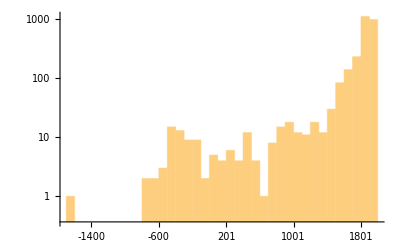

```mathematica
DateHistogram[completebirthDateObjects,"Century",ScalingFunctions->"Log"]
```

No mathematical knowledge between ancient Greeks

```mathematica
TimelinePlot@MapThread[Interval[{#1, #2}]&, {completebirthDateObjects ,completedeathDateObjects/._Missing ->DateObject["Today"]}]
```

-Graphics-

Problem: 
a) Entries that have an ancient city with (now...)

```mathematica
Interpreter["Country"|"City"|"Location"]/@DeleteCases[birthdate,{}][[-10;;,2]]
```

{Kharkiv,Antony,Failure[…],Moscow,Ithaca,Cologne,Padova,Moscow,Adelaide,Tehran}

DateObject processes all non-BC dates

```mathematica
Position[%197,_Failure]
```

{{33},{48},{55},{57},{58},{65}}

```mathematica
Clear[y];Clear[l]
```

DateObjects cannot process death dates as some of the elements have biography data

```mathematica
DateObject/@DeleteCases[deathdate,{}][[-200;;,1]]
```

DateObject::str: String  7 December 2011</font></h3>
<a href=../PictDisplay/Springer.html onclick="javascript:win1('../PictD…ting</a></h4>
</table>
</center>
<hr><article><b>Tonny Springer</b> entered the University of Leiden cannot be interpreted as a date.

DateObject::str: String  27 May 2012</font></h3>
<a href=../PictDisplay/Hirzebruch.html onclick="javascript:win1('../PictDis…r Fritz Hirzebruch and Martha Holtschmidt. Fritz Hirzebruch was the headmaster of a secondary school cannot be interpreted as a date.

DateObject::str: String  12 October 2009</font></h3>
<a href=../PictDisplay/Gohberg.html onclick="javascript:win1('../PictDi…
</table>
</center>
<hr><article><b>Israel Gohberg</b> came from a Jewish family. He attended school cannot be interpreted as a date.

General::stop: Further output of DateObject::str will be suppressed during this calculation.

{Day: Wed 21 Feb 1996,Day: Tue 5 Mar 2013,Day: Wed 26 Nov 1986,Day: Wed 14 Feb 2007,Day: Fri 20 Nov 2015,Day: Mon 7 Apr 2014,Day: Mon 10 Jun 1974,Day: Wed 27 May 1964,Day: Sun 9 Feb 2003,Day: Sun 20 Aug 1972,Day: Sat 26 Dec 1992,Day: Mon 28 Sep 1992,Day: Fri 13 Feb 2015,Day: Sat 10 Aug 2002,Day: Fri 7 Apr 2006,Day: Thu 23 Aug 2012,Day: Thu 8 Jan 2015,Day: Sun 7 Sep 2003,DateObject[ 7 December 2011</font></h3>
<a href=../PictDisplay/Springer.html onclick="javascript:win1('../PictDisplay/Springer.html',700,1000);return false;"><img src =../Thumbnails/Springer.jpg border=1 height=125></a><p><font color=red size=-1>Click the picture above<br>to see three larger pictures</font>
<p>
<a href = "../BirthplaceMaps/The_Hague.html"><b>Show birthplace location</b></a><p>
<table border=0 cellspacing="0" cellpadding="5" bgcolor="ccccff"  >
<tr><td><a href="../index.html" >Main Index</a>
<td><a href="../BiogIndex.html">Biographies index</a>
</table>
<p>
<table border=0 cellspacing=0 cellpadding=0 width=100%>
<tr><td align=left><form action="http://www-history.mcs.st-andrews.ac.uk/Search/historysearch.cgi" target="_blank"><input name="SUGGESTION" size=25 placeholder="Enter word or phrase"><input type="submit" value="Search the MacTutor archive"></form>
<td align=right><h4><a href="../Printonly/Springer.html" onclick="javascript:win1('../Printonly/Springer.html',600,1000);return false;">Version for printing</a></h4>
</table>
</center>
<hr><article><b>Tonny Springer</b> entered the University of Leiden],Day: Sun 31 May 1998,Day: Tue 16 Feb 1971,Day: Mon 25 Aug 1997,Day: Mon 13 Jun 1994,Day: Sat 10 Dec 2016,Day: Wed 4 Jun 2008,DateObject[ 27 May 2012</font></h3>
<a href=../PictDisplay/Hirzebruch.html onclick="javascript:win1('../PictDisplay/Hirzebruch.html',700,1000);return false;"><img src =../Thumbnails/Hirzebruch.jpg border=1 height=125></a><p><font color=red size=-1>Click the picture above<br>to see a larger version</font>
<p>
<a href = "../BirthplaceMaps/Hamm.html"><b>Show birthplace location</b></a><p>
<table border=0 cellspacing="0" cellpadding="5" bgcolor="ccccff"  >
<tr><td><a href="../index.html" >Main Index</a>
<td><a href="../BiogIndex.html">Biographies index</a>
</table>
<p>
<table border=0 cellspacing=0 cellpadding=0 width=100%>
<tr><td align=left><form action="http://www-history.mcs.st-andrews.ac.uk/Search/historysearch.cgi" target="_blank"><input name="SUGGESTION" size=25 placeholder="Enter word or phrase"><input type="submit" value="Search the MacTutor archive"></form>
<td align=right><h4><a href="../Printonly/Hirzebruch.html" onclick="javascript:win1('../Printonly/Hirzebruch.html',600,1000);return false;">Version for printing</a></h4>
</table>
</center>
<hr><article><b>Friedrich Hirzebruch</b> was the son of Dr Fritz Hirzebruch and Martha Holtschmidt. Fritz Hirzebruch was the headmaster of a secondary school],Day: Sun 17 Dec 1978,Day: Mon 12 Sep 2005,Day: Thu 28 Jul 2011,Day: Sun 2 Oct 2011,Day: Sun 21 Jul 1974,Day: Sun 8 Jan 2012,Day: Fri 16 Sep 2016,Day: Wed 28 Jan 2009,Day: Wed 27 Aug 2008,Day: Thu 27 May 2004,Day: Mon 25 Apr 2016,Day: Sat 16 Sep 1989,Day: Mon 15 Sep 2003,Day: Thu 17 Apr 2014,Day: Mon 17 Nov 1958,Day: Tue 26 Apr 2011,Day: Wed 9 Jun 2010,Day: Tue 25 Feb 1997,Day: Thu 15 Aug 2002,Day: Mon 1 Oct 1990,Day: Thu 14 Apr 1983,Day: Fri 25 Oct 1996,DateObject[ 12 October 2009</font></h3>
<a href=../PictDisplay/Gohberg.html onclick="javascript:win1('../PictDisplay/Gohberg.html',700,1000);return false;"><img src =../Thumbnails/Gohberg.jpg border=1 height=125></a><p><font color=red size=-1>Click the picture above<br>to see two larger pictures</font>
<p>
<a href = "../BirthplaceMaps/Tarutino.html"><b>Show birthplace location</b></a><p>
<table border=0 cellspacing="0" cellpadding="5" bgcolor="ccccff"  >
<tr><td><a href="../index.html" >Main Index</a>
<td><a href="../BiogIndex.html">Biographies index</a>
</table>
<p>
<table border=0 cellspacing=0 cellpadding=0 width=100%>
<tr><td align=left><form action="http://www-history.mcs.st-andrews.ac.uk/Search/historysearch.cgi" target="_blank"><input name="SUGGESTION" size=25 placeholder="Enter word or phrase"><input type="submit" value="Search the MacTutor archive"></form>
<td align=right><h4><a href="../Printonly/Gohberg.html" onclick="javascript:win1('../Printonly/Gohberg.html',600,1000);return false;">Version for printing</a></h4>
</table>
</center>
<hr><article><b>Israel Gohberg</b> came from a Jewish family. He attended school],Day: Thu 13 Nov 2014,Day: Wed 10 Oct 2007,Day: Sun 19 Sep 2010,Day: Thu 17 May 2001,Day: Fri 17 Dec 1999,Day: Sat 23 May 2015,Day: Fri 29 Mar 1996,Day: Sat 27 Apr 2013,Day: Tue 29 Apr 2014,Day: Wed 16 Aug 1995,DateObject[ 17 July 2007</font></h3>
<a href=../PictDisplay/Bruhat.html onclick="javascript:win1('../PictDisplay/Bruhat.html',700,1000);return false;"><img src =../Thumbnails/Bruhat.jpg border=1 height=125></a><p><font color=red size=-1>Click the picture above<br>to see a larger version</font>
<p>
<a href = "../BirthplaceMaps/Paris.html"><b>Show birthplace location</b></a><p>
<table border=0 cellspacing="0" cellpadding="5" bgcolor="ccccff"  >
<tr><td><a href="../index.html" >Main Index</a>
<td><a href="../BiogIndex.html">Biographies index</a>
</table>
<p>
<table border=0 cellspacing=0 cellpadding=0 width=100%>
<tr><td align=left><form action="http://www-history.mcs.st-andrews.ac.uk/Search/historysearch.cgi" target="_blank"><input name="SUGGESTION" size=25 placeholder="Enter word or phrase"><input type="submit" value="Search the MacTutor archive"></form>
<td align=right><h4><a href="../Printonly/Bruhat.html" onclick="javascript:win1('../Printonly/Bruhat.html',600,1000);return false;">Version for printing</a></h4>
</table>
</center>
<hr><article><b>François Bruhat</b>'s parents were Georges Bruhat, who was assistant director of the École Normale Supérieure],Day: Wed 13 Jul 2016,Day: Wed 8 Jun 1966,Day: Wed 3 Apr 1974,Day: Wed 23 Aug 2006,Day: Fri 22 Sep 2000,Day: Wed 20 Aug 2014,Day: Sun 26 Oct 2008,Day: Sat 21 Feb 2009,DateObject[ 16 July 2013</font></h3>
<a href=../PictDisplay/Prokhorov.html onclick="javascript:win1('../PictDisplay/Prokhorov.html',700,1000);return false;"><img src =../Thumbnails/Prokhorov.jpg border=1 height=125></a><p><font color=red size=-1>Click the picture above<br>to see two larger pictures</font>
<p>
<a href = "../BirthplaceMaps/Moscow.html"><b>Show birthplace location</b></a><p>
<table border=0 cellspacing="0" cellpadding="5" bgcolor="ccccff"  >
<tr><td><a href="../index.html" >Main Index</a>
<td><a href="../BiogIndex.html">Biographies index</a>
</table>
<p>
<table border=0 cellspacing=0 cellpadding=0 width=100%>
<tr><td align=left><form action="http://www-history.mcs.st-andrews.ac.uk/Search/historysearch.cgi" target="_blank"><input name="SUGGESTION" size=25 placeholder="Enter word or phrase"><input type="submit" value="Search the MacTutor archive"></form>
<td align=right><h4><a href="../Printonly/Prokhorov.html" onclick="javascript:win1('../Printonly/Prokhorov.html',600,1000);return false;">Version for printing</a></h4>
</table>
</center>
<hr><article><b>Yurii Vasilevich Prokhorov</b>'s father, Vasily Prokhorov, was a construction engineer. Several generations of the family had lived],Day: Sat 26 Jan 2008,Day: Fri 2 Nov 2012,Day: Sat 7 Jan 1989,Day: Tue 6 Aug 2002,Day: Thu 29 Jul 2004,Day: Sat 11 Oct 2008,DateObject[ 4 September 2011</font></h3>
<a href=../PictDisplay/Grauert.html onclick="javascript:win1('../PictDisplay/Grauert.html',700,1000);return false;"><img src =../Thumbnails/Grauert.jpg border=1 height=125></a><p><font color=red size=-1>Click the picture above<br>to see a larger version</font>
<p>
<a href = "../BirthplaceMaps/Haren-Ems.html"><b>Show birthplace location</b></a><p>
<table border=0 cellspacing="0" cellpadding="5" bgcolor="ccccff"  >
<tr><td><a href="../index.html" >Main Index</a>
<td><a href="../BiogIndex.html">Biographies index</a>
</table>
<p>
<table border=0 cellspacing=0 cellpadding=0 width=100%>
<tr><td align=left><form action="http://www-history.mcs.st-andrews.ac.uk/Search/historysearch.cgi" target="_blank"><input name="SUGGESTION" size=25 placeholder="Enter word or phrase"><input type="submit" value="Search the MacTutor archive"></form>
<td align=right><h4><a href="../Printonly/Grauert.html" onclick="javascript:win1('../Printonly/Grauert.html',600,1000);return false;">Version for printing</a></h4>
</table>
</center>
<hr><article><b>Hans Grauert</b>'s parents were Clemens and Maria Grauert. He was born],Day: Mon 30 Apr 2012,Day: Fri 26 Jan 2007,Day: Mon 2 Mar 2009,DateObject[ 3 January 2011</font></h3>
<a href=../PictDisplay/Skorokhod.html onclick="javascript:win1('../PictDisplay/Skorokhod.html',700,1000);return false;"><img src =../Thumbnails/Skorokhod.jpg border=1 height=125></a><p><font color=red size=-1>Click the picture above<br>to see three larger pictures</font>
<p>
<a href = "../BirthplaceMaps/Nikopol.html"><b>Show birthplace location</b></a><p>
<table border=0 cellspacing="0" cellpadding="5" bgcolor="ccccff"  >
<tr><td><a href="../index.html" >Main Index</a>
<td><a href="../BiogIndex.html">Biographies index</a>
</table>
<p>
<table border=0 cellspacing=0 cellpadding=0 width=100%>
<tr><td align=left><form action="http://www-history.mcs.st-andrews.ac.uk/Search/historysearch.cgi" target="_blank"><input name="SUGGESTION" size=25 placeholder="Enter word or phrase"><input type="submit" value="Search the MacTutor archive"></form>
<td align=right><h4><a href="../Printonly/Skorokhod.html" onclick="javascript:win1('../Printonly/Skorokhod.html',600,1000);return false;">Version for printing</a></h4>
</table>
</center>
<hr><article><b>Anatolii Volodymyrovych Skorokhod</b>'s parents were Volodymyr Oleksiyovych and Nadiya Andriivna Skorokhod; they were both school teachers. Volodymyr Oleksiyovych taught mathematics, physics and astronomy, while Nadiya Andriivna taught mathematics, history, literature, and music.<b> </b>Anatolii Volodymyrovych were the eldest of his parents two children having a younger brother Valerii Volodymyrovych. Having two teachers for parents, both boys were brought up],Day: Sun 11 Aug 1991,Day: Sun 29 May 2005,Day: Wed 4 Feb 2004,Day: Sun 25 Nov 2012,Day: Sat 24 Jul 1993,Day: Thu 28 Sep 1967,Day: Wed 9 Jul 2014,DateObject[ 1 July 2015</font></h3>
<a href=../PictDisplay/Olech.html onclick="javascript:win1('../PictDisplay/Olech.html',700,1000);return false;"><img src =../Thumbnails/Olech.jpg border=1 height=125></a><p><font color=red size=-1>Click the picture above<br>to see three larger pictures</font>
<p>
<a href = "../BirthplaceMaps/Pinczow.html"><b>Show birthplace location</b></a><p>
<table border=0 cellspacing="0" cellpadding="5" bgcolor="ccccff"  >
<tr><td><a href="../index.html" >Main Index</a>
<td><a href="../BiogIndex.html">Biographies index</a>
</table>
<p>
<table border=0 cellspacing=0 cellpadding=0 width=100%>
<tr><td align=left><form action="http://www-history.mcs.st-andrews.ac.uk/Search/historysearch.cgi" target="_blank"><input name="SUGGESTION" size=25 placeholder="Enter word or phrase"><input type="submit" value="Search the MacTutor archive"></form>
<td align=right><h4><a href="../Printonly/Olech.html" onclick="javascript:win1('../Printonly/Olech.html',600,1000);return false;">Version for printing</a></h4>
</table>
</center>
<hr><article><b>Czes&#322;aw Olech</b> was born],Day: Sun 10 Dec 1995,Month: Aug 1992,Day: Sat 7 Jan 2012,Day: Fri 19 Apr 2013,Day: Fri 16 Nov 2007,Day: Thu 15 May 1975,Day: Wed 21 Jan 2004,Day: Fri 9 Jun 1995,Day: Sat 20 Jan 2001,Day: Sun 18 Apr 1999,Day: Fri 25 Apr 2008,Day: Sun 31 May 1992,Day: Tue 28 Sep 2004,Day: Wed 18 Sep 2002,Day: Wed 1 Apr 1998,Day: Tue 22 Apr 2008,Day: Wed 5 Feb 1997,Day: Thu 27 Sep 2007,Day: Thu 19 Sep 2002,Day: Mon 1 Jun 1998,Day: Sat 18 Nov 2000,Day: Sat 17 Mar 2012,Day: Fri 23 Mar 2007,Day: Thu 30 Jan 2003,Day: Sun 20 Aug 2006,Day: Tue 4 Aug 2009,Day: Fri 23 May 2014,Day: Sat 28 Oct 1989,Day: Tue 3 Jun 2003,Day: Thu 13 Jun 1991,Day: Tue 24 Aug 1982,Day: Mon 24 Nov 2008,Day: Thu 9 Aug 2007,DateObject[ August 5, 2014</font></h3>
<a href=../PictDisplay/Anosov.html onclick="javascript:win1('../PictDisplay/Anosov.html',700,1000);return false;"><img src =../Thumbnails/Anosov.jpg border=1 height=125></a><p><font color=red size=-1>Click the picture above<br>to see two larger pictures</font>
<p>
<a href = "../BirthplaceMaps/Moscow.html"><b>Show birthplace location</b></a><p>
<table border=0 cellspacing="0" cellpadding="5" bgcolor="ccccff"  >
<tr><td><a href="../index.html" >Main Index</a>
<td><a href="../BiogIndex.html">Biographies index</a>
</table>
<p>
<table border=0 cellspacing=0 cellpadding=0 width=100%>
<tr><td align=left><form action="http://www-history.mcs.st-andrews.ac.uk/Search/historysearch.cgi" target="_blank"><input name="SUGGESTION" size=25 placeholder="Enter word or phrase"><input type="submit" value="Search the MacTutor archive"></form>
<td align=right><h4><a href="../Printonly/Anosov.html" onclick="javascript:win1('../Printonly/Anosov.html',600,1000);return false;">Version for printing</a></h4>
</table>
</center>
<hr><article><b>Dmitrii Viktorovich Anosov</b>'s parents were Viktor Yakovlevich Anosov and Nina<br>
Konstantinovna Voskresenskaya. Both worked at the Institute of General and Inorganic Chemistry],Day: Sat 1 Dec 2007,Day: Wed 19 Dec 2001,Day: Wed 27 Dec 2006,Day: Mon 26 Dec 2011,Day: Sun 28 Jul 2013,Day: Mon 29 Nov 2010,Day: Wed 26 Oct 1994,Day: Thu 3 Jun 2010,Day: Mon 29 Nov 2004,Day: Wed 28 May 1997,Day: Fri 27 Nov 1998,Day: Tue 13 Apr 2004,Day: Sun 10 Apr 2011,Day: Sun 5 May 2002,Day: Fri 9 Jun 1989,Day: Mon 23 Oct 2017,Day: Wed 30 Aug 1995,Day: Sat 21 Aug 2010,Day: Sat 31 May 2008,Day: Sun 27 Oct 1974,Day: Fri 7 Jul 2017,Day: Thu 23 Sep 1982,Day: Wed 16 May 2012,Day: Sun 4 Feb 2018,Day: Thu 7 Jan 2010,Day: Sat 8 Oct 1994,Day: Mon 9 Jan 2012,Day: Sat 30 Apr 2011,Day: Fri 3 Dec 2010,Day: Mon 26 Nov 1990,Day: Fri 19 Nov 2004,Day: Fri 12 Dec 2014,Day: Sun 18 Jun 1978,Day: Fri 23 Jun 1978,Day: Sat 21 Mar 2009,Day: Sat 25 Dec 2010,Day: Wed 12 Apr 2000,Day: Sun 9 Dec 2012,Day: Wed 14 Mar 2018,Day: Mon 25 Jul 2016,Day: Tue 14 Aug 2007,Day: Tue 17 Apr 2012,Day: Sat 1 Aug 1987,Day: Sun 1 May 2011,Month: Mar 1973,Day: Tue 18 Mar 1997,Day: Tue 21 Dec 1976,Day: Mon 28 Sep 1998,Day: Tue 31 Aug 2010,Day: Wed 6 Jun 2012,Day: Tue 21 Aug 2012,Day: Mon 29 Sep 2003,Day: Sun 30 Jul 1978,Day: Thu 6 Jun 1985,Day: Mon 26 Mar 2012,Day: Thu 14 Jul 2016,Day: Tue 22 Mar 2011,Day: Thu 5 Nov 2009,Day: Thu 12 Oct 2006,Day: Sun 21 Mar 2010,Day: Thu 4 Feb 2010,Day: Tue 11 Nov 2003,Day: Thu 24 Jul 2014,Day: Fri 29 Jan 1999,Day: Fri 31 Jan 2014,Day: Sun 29 Mar 2015,Month: Nov 1995,Day: Wed 19 Jun 2002,Day: Wed 15 May 1991,DateObject[ 3 September 2016</font></h3>
<a href=../PictDisplay/Yoccoz.html onclick="javascript:win1('../PictDisplay/Yoccoz.html',700,1000);return false;"><img src =../Thumbnails/Yoccoz.jpg border=1 height=125></a><p><font color=red size=-1>Click the picture above<br>to see four larger pictures</font>
<p>
<a href = "../BirthplaceMaps/Paris.html"><b>Show birthplace location</b></a><p>
<table border=0 cellspacing="0" cellpadding="5" bgcolor="ccccff"  >
<tr><td><a href="../index.html" >Main Index</a>
<td><a href="../BiogIndex.html">Biographies index</a>
</table>
<p>
<table border=0 cellspacing=0 cellpadding=0 width=100%>
<tr><td align=left><form action="http://www-history.mcs.st-andrews.ac.uk/Search/historysearch.cgi" target="_blank"><input name="SUGGESTION" size=25 placeholder="Enter word or phrase"><input type="submit" value="Search the MacTutor archive"></form>
<td align=right><h4><a href="../Printonly/Yoccoz.html" onclick="javascript:win1('../Printonly/Yoccoz.html',600,1000);return false;">Version for printing</a></h4>
</table>
</center>
<hr><article><b>Jean-Christophe Yoccoz</b> was placed first],Day: Wed 13 Feb 2013,Day: Tue 30 Oct 2007,Day: Mon 1 Sep 2008,Day: Fri 5 Jun 2009,Day: Sat 30 Sep 2017,Day: Wed 1 Nov 2000,Day: Fri 10 Jan 2014,Day: Fri 14 Jul 2017}

```mathematica
ClearAll[a]
```

Social network graphs

```mathematica
bioReferences = StringCases[htmlBioList,"../Mathematicians/"~~Shortest[a__]~~".html"->a];
```

```mathematica
uniqueReference=Map[Union,bioReferences]
```

{{},{Ahmes},{Ahmes,Baudhayana},{Aristotle,Eudemus,Halley,Heath,Neugebauer,Plato,Proclus,Pythagoras,Russell,Van_der_Waerden},2768,{Fields,Fredholm,Hankel,Kirillov,Plancherel,Toeplitz,Wiles},{Bocher,Fields,Fourier,Gowers,Hedrick,Ostrowski,Polya,Ramanujan,Riemann,Salem,Schrodinger,Stein},{Fields,Kontsevich,McMullen,Riemann,Weil,Witten}}
 |  |  |  |

Association describing name of biography -> name of connected mathematician + how many times each person is mentioned

```mathematica
allNames = Flatten@StringCases[Import["http://www-groups.dcs.st-and.ac.uk/history/Indexes/Full_Chron.html",{"Hyperlinks"}],"/Biographies/"~~Shortest[a__]~~".html"->a]
```

```mathematica
Rule[1 , 2]
```

```mathematica
Rule["Euclid" , {"Newton","Pitagoras"}]
```

Euclid→{Newton,Pitagoras}

```mathematica
Thread [Rule["Euclid" , {"Newton","Pitagoras"}]]
```

```mathematica
Thread[Rule[{1,2},{{a,c},{b,c}}]]
```

{1→{a,c},2→{b,c}}

```mathematica
MapThread[#1 ->#2 &, {{1,2},{a,b}}]
```

{1→a,2→b}

```mathematica
MapThread[#1 ->#2 &, {{1,2},{{a,c},{b,c}}}]
```

{1→{a,c},2→{b,c}}

```mathematica
MapThread[Thread [Rule[#1 , #2]] &, {{1,2},{{a,c},{b,c}}}]
```

{{1→a,1→c},{2→b,2→c}}

```mathematica
vertexList =Flatten@ MapThread[ Thread[Rule[#1 , #2]]&,{allNames,uniqueReference}]
```

{Baudhayana→Ahmes,Manava→Ahmes,Manava→Baudhayana,Thales→Aristotle,Thales→Eudemus,Thales→Halley,Thales→Heath,Thales→Neugebauer,Thales→Plato,Thales→Proclus,24365,Tao→Riemann,Tao→Salem,Tao→Schrodinger,Tao→Stein,Mirzakhani→Fields,Mirzakhani→Kontsevich,Mirzakhani→McMullen,Mirzakhani→Riemann,Mirzakhani→Weil,Mirzakhani→Witten}
 |  |  |  |

```mathematica
Values["Tao"->"Riemann"]
```

Riemann

```mathematica
vertexList // Length
```

24385

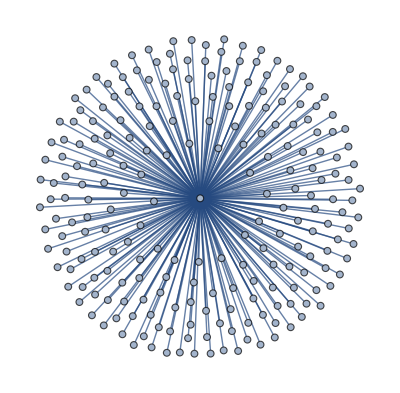

```mathematica
r =Select[vertexList,Values[#]=="Euclid" &];
Graph[r]
```

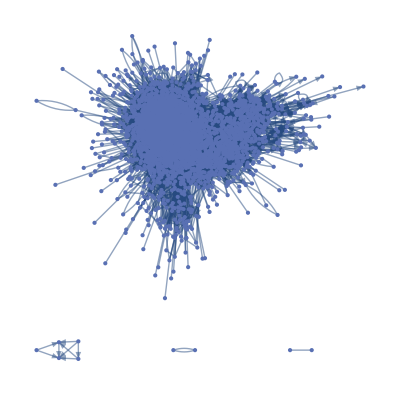

```mathematica
g =Graph[vertexList,VertexLabels->Placed["Name",Tooltip]]
```

```mathematica
CommunityGraphPlot[g]
```

-Graphics-

```mathematica
FindGraphCommunities[g]
```

{{Russell,Frege,Cartan_Henri,Chevalley,Dieudonne,Grothendieck,Weil,Lebesgue,Stieltjes,Ramanujan,Wiles,Dehn,Hellinger,Stone,Vinogradov,Caratheodory,Truesdell,Hilbert,Bogolyubov,Parseval,Hardy,Kolmogorov,Zeeman,Bourbaki,Bocher,Cartan,Mises,Artin,Birkhoff_Garrett,Rota,Ulam,Von_Neumann,Householder,Rado,Tarski,Davenport,Kneser,Lefschetz,Korteweg,Steinitz,Choquet,Zermelo,Chauvenet,Grave,Hadamard,Hahn,Lyapunov,Vallee_Poussin,Borel,Brouwer,Andrews,Lehmer_Derrick,Sierpinski,Egorov,Butzer,Epstein,Noether_Emmy,Lowenheim,Levy_Paul,Rey_Pastor,Ledermann,Shafarevich,Robinson,Moriarty,Nash,Delone,Bieberbach,Hall,Tutte,Hirzebruch,Fischer,Helly,Schrodinger,Skolem,Wiener_Norbert,Courant,Toeplitz,Weyl,Fejer,Riesz,Hirsch,Cole,Malcev,Markov,Matiyasevich,Novikov,Frechet,Schur,Zhukovsky,Andreev,Steklov,Hausdorff,Lesniewski,Wittgenstein,Landau,Remak,Siegel,Lasker,Schmidt,Boas,Czuber,Dickstein,Kuratowski,Knopp,Feit,Thompson_John,Zelmanov,Kiselev,Arnold,Chaplygin,Ostrovskii,Perron,Moore_Robert,Loewy,Moore_Eliakim,Littlewood,Perelman,Zaremba,Fields,Haupt,Wirtinger,Baire,Bernstein_Sergi,Herglotz,Birkhoff,Bliss,Veblen,Dudeney,Sobolev,Pell_Alexander,Wheeler,Collingwood,Julia,Lehto,Polya,Hamel,Lichtenstein,Schreier,Loewner,Steinhaus,Shatunovsky,Chebotaryov,Kagan,Krein,Levin,Plancherel,Janiszewski,Osgood,Hasse,Hecke,Wedderburn,Ackermann,Blumenthal,Curry,Godel,Haar,Hedrick,Kaplansky,Kellogg,Kneser_Hellmuth,Takagi,Wielandt,Gorenstein,Krull,Zariski,Rogers_James,Selberg,Ahlfors,Akhiezer,Ostrowski,Daniell,Cramer_Harald,Zygmund,Thue,Morse,Post,Roth_Klaus,Burkill,Zorawski,Peter,Plessner,Friedmann,Smirnov,Tamarkin,Bohr_Harald,Schwartz,Kotelnikov,Beurling,Valiron,Furtwangler,Radon,Reidemeister,Taussky-Todd,Tauber,Jackson_Dunham,Luzin,Banach,Nikodym,Denjoy,Kolosov,Cartwright,<i>Kampf</i>,Chern,Hodge,Khinchin,Aleksandrov,Kurosh,Nekrasov,Stepanov,Eichler,Iwasawa,Bachelier,Doob,Feller,Ito,Doetsch,Walsh_Joseph,Reichenbach,Galerkin,Baer,Rademacher,Fraenkel,De_Rham,Blaschke,Finsler,Suss,Brauer,Neumann_Bernhard,Schmidt_F-K,Scholz_Arnold,Witt,Vidav,Whittaker_John,Cooper,Albert_Abraham,Tietze,Mordell,Montel,Szego,Mazurkiewicz,Todd_John,Turing,Wilkinson,Faltings,Brauer_Alfred,Eilenberg,Frucht,Green_Sandy,Grunsky,MacLane,Neumann_Hanna,Rado_Richard,Schiffer,Iyanaga,De_Bruijn,Halmos,Whyburn_William,Hopf,Hille,Behnke,Ingham,Riesz_Marcel,Rogosinski,Titchmarsh,Wright,Teichmuller,Birman,Privalov,Kerekjarto,Urysohn,Uryson,Evans,Geiringer,Maruhn,Mazur,Wintner,Bernays,Heyting,Quine,Lukasiewicz,Bilimovic,Frank,Hurewicz,Mandelbrot,Menger,Saks,Krylov_Nikolai,Levinson,Linnik,Erdos,Turan,Lukacs,Hazlett,Slutsky,Alexander,Whitehead_Henry,Kalmar,Richardson_Archibald,Littlewood_Dudley,Kothe,Schramm,Jones_Burton,Rudin,Vandiver,Lindenbaum,Schauder,Walfisz,Jacobson,Chatelet_Albert,Szasz,Bari,Keldysh_Lyudmila,Lavrentev,Menshov,Shnirelman,Suslin,Schouten,Mandelbrojt,Steenrod,Noether_Fritz,Gelfond,Scholz,Kreisel,Bloch,Miranda,Pontryagin,Caccioppoli,Godement,Mahler,Goodstein,Andreotti,Barsotti,Bombieri,Branges,Collatz,Fekete,Dvoretzky,Leray,Ford,Whyburn,Carleman,Hormander,Besicovitch,Lewy,Orlicz,Harary,Feigl,Vietoris,Kac,Kaczmarz,Antoine,Specker,Berwick,Friedrichs,Robbins,Kochina,Schmidt_Otto,Kober,Cassels,Calderon,Threlfall,Fox_Ralph,Seifert,Bott,Hall_Marshall,Gateaux,Hamburger,Razmadze,Rees_David,Zylinski,Stark,Faddeev,Kochin,Mohr_Ernst,Rohrbach,Nielsen_Jakob,Stein_Philip,Spencer,Rapcsak,Renyi,Cohen,Kostrikin,Prufer,Dantzig,Carlson,Krawtchouk,Pollaczek,Schoenberg,Jarnik,Ferrand,Cech,Tikhonov,Dixmier,Lanczos,Bergman,Bers,Mullikin,Wilder,Artzy,Magnus,Moufang,Newman,Lorch_Ray,Church,Frenkel,Gnedenko,Jordan_Pascual,Offord,Sargent,Szeg&#337;,Wrinch,Fefferman,Gelbart,Blackwell,Marcinkiewicz,Paley,Nevanlinna,Hayman,Reinhardt,Rothe_Erich,Herzberger,Rothe-Ille,Lax_Peter,Gentzen,Robinson_Raphael,Fedorchuk,Janovskaja,Kleene,Remez,Schneider,Wazewski,Borsuk,Fox,Bochner,Hilton,Wylie,Davis,Shtokalo,Petryshyn,Weinstein,Deligne,Tate,Bessel-Hagen,Leopoldt,Salem,Suetuna,Taylor_Mary,Bachiller,Zorn,Boruvka,Dorge,Keldysh_Mstislav,Malgrange,Possel,Atiyah,Samuel,Apostol,Cauer,Hopf_Eberhard,Mytropolsky,Puig_Adam,Redei,Vranceanu,Fine_Nathan,Gershgorin,Adian,Boone,Novikov_Sergi,Oka,Petrovsky,Rellich,Sperner,Zassenhaus,Vajda,Suzuki_Michio,Calugareanu,Cohn-Vossen,Aleksandrov_Aleksandr,Efimov,Pogorelov,Estermann,Heilbronn,Petersson,Schwerdtfeger,Shoda,Nakayama,Wall_Hubert,Wegner,Zarankiewicz,Birnbaum,Bosanquet,Rogers,Foster,Smullyan,Ehresmann,Kodaira,Whitney,Delsarte,Dubreil,Serrre,Gelfand,Coates,Cohn,Koksma,Morishima,Rocard,Bruhat,Choquet-Bruhat,Bradistilov,Federer,Serre,Chudakov,Davies,Clifford_Alfred,Dubreil-Jacotin,Fitting,Herbrand,Pisot,Linfoot,Higman,Varga,Kuperberg,Levitzki,Kato,Lehmer,Nirenberg,Mostowski,McShane,Ricci_Giovanni,Frohlich,Keller,Slupecki,Warschawski,Wolf_Frantisek,Beckenbach,Kuttner,Herstein,Carleson,Schutzenberger,Henriques,Kuroda,Lehmer_Emma,Ljunggren,Ribenboim,Kakutani,Dynkin,Tucker_Albert,Dantzig_George,Wallace_Alexander,Spanier,Zippin,Gleason,Montgomery,Straus,Borel_Armand,Cartier,Thom,Faddeeva,Fiedler,Forsythe,Golub,Kantorovich,Kublanovskaya,Specht,Baker_Alan,Bonsall,Goldie_Alfred,Gruenberg,Lopatynsky,Peschl,Laurent,Mirsky,Moser_Jurgen,Samarskii,Shimura,Yau,Alexander_Hugh,Carlitz,Chowla,Pillai,Ursell,Deuring,Livsic,Potapov,Kurepa,Marczewski,Vekua,Claytor,Johnson_Katherine,Lyapin,Preston,Dinghas,Elfving,Gohberg,Motzkin,Reichardt,Schmid,Schwartz_Laurent,Vagner,Van_Kampen,Black,Vladimirov,groups,Gyires,James_Ralph,Peirce,Segal,Yamabe,Naimark,Harish-Chandra,Stiefel,Goldstine,Rutishauser,Speiser,Theilheimer,Varga_Otto,Konig,Arf,Ikeda,Fogels,Hua,John,Koopmans,Lorentz_George,James,Askey,Samelson,Chow,Voevodsky,Langlands,Hahn_Wolfgang,Atkinson,Robinson_Julia,Santalo,Donaldson,Szekeres,Smithies,Chernikov,Dowker,Guinand,Smale,Sasaki,Sunyer,Corominas,Picard,Yano,Teitz,Tietz,Lichnerowicz,Cotlar,Sadosky,Sikorski,Chen,Lyndon,Mazur_Barry,Milnor,Stallings,Fomin,Mikusinski,Rios,Zaanen,Abellanas,Begle,Bing,Cherry_Colin,Cooper_William,Lovasz,De_Groot,Feldbau,Kaluznin,Hoehnke,Pitt,Polozii,Auslander_Louis,Apery,Doeblin,Dou,Kelly,Povzner,Marchenko,Edmonds,Good,Mackey,Hunt,Kolchin,Northcott,Alexiewicz,Eckmann,Gillman,Hibert,Krylov_Nikolai_S,Samoilenko,Rasiowa,Feldman,Fiorentini,Gilbarg,Serrin,Trudinger,Nagata,Szele,Kovacs,Szmielew,Wang,Kruskal_Joseph,Libermann,Rokhlin,Gromov,Schmetterer,Suvorov,Wu_Wen-Tsun,Mumford,Bellman,Ringrose,Britton,Cobbe,Lane,Almgren,Gaschutz,Ingarden,Urbanik,Kuiper,Tits,Los,Ramanathan,Reeb,Rennie,Singh,Gale,Garnir,Koszul,Rham,Kubilius,Lob,Luchins,Matsushima,Rudin_Walter,Trakhtenbrot,Gluskin,Kalicki,Ladyzhenskaya,Bernstein_Sergei,Lakatos,Lax_Anneli,Ree,Quillen,Sullivan,Dezin,Henrici_Peter,Griffiths_Brian,Kadets,Keller_Joseph,Sinai,Piatetski-Shapiro,Grauert,Aubert,Connes,Hoyland,Karlin,Krasovskii,Singer,Patodi,Steinfeld,Dahlquist,Divinsky,Lang,Sato,Auslander,Babuska,Kellogg_Bruce,Bremermann,Adamson,Dye,Eells,Hajek,Lusztig,Kennedy,Karp,Nijenhuis,Wilf,Nygaard,Pawlak,Stein,Shepherdson,Springer,Molien,Browder_Felix,Browder_William,Lyra,Postnikov,Hironaka,Mori,Sachs,Shields,Skopin,Taniyama,Bauer,Bishop,Union,Diaconis,Selten,Pask,Suzuki_Satoshi,Routledge,Gowers,Valdivia,Kalton,Walter,Witten,Kertesz,Manin,Prokhorov,Puri,Abhyankar,Bohr,Adams_Frank,Dijkstra,Foulis,Goldberg,Kalman,Kelly_Max,Morton,Schwartz_Jacob,Skorokhod,Blum,Freedman,Wang_Yuan,Knapowski,McDuff,Thurston,Olech,Tao,Thompson_Robert,Bass,Bollobas,Drinfeld,Honda,Nash-Williams,Solitar,Tarina,Vernon,Warner,Lesokhin,Artin_Michael,Wall,Meyer_Paul-Andre,Ornstein,Wiegold,Furstenberg,Szemeredi,Grigelionis,Hay,Kumano-Go,Bowen,Srinivasan,Allan_Graham,Anosov,Bolibrukh,Cofman,Kirillov,Okounkov,Praeger,Strassen,Valiant,Tichy,Book,Hayes_David,Johnson_Barry,Schoenflies,Black_Fischer,Griffiths,Gromoll,Kirby,Ramanujam,Ratner,Margulis,Uhlenbeck_Karen,Krylov,Subbotovskaya,Hartley,Senechal,Keen,Szafraniec,Varadhan,McMullen,Szasz_Domokos,Young_Lai-Sang,Aubin,Chang,Lafforgue,Rallis,Jones_Vaughan,Millington,Trahtman,Adleman,Shelah,Simon,Schoen,Iwanik,Pisier,Arino,Eisenbud,Carr,Flajolet,Kintala,Murphy_Gerard,Broomhead,Gorbunov,Floer,Thomason,Bourgain,Borcherds,Krejci,Perrin-Riou,Yoccoz,Seress,Thompson_Abigail,Heinonen,Smith_Karen,Werner_Wendelin,Motwani,Dubickas,Kontsevich,Jitomirskaya,Cariolaro,Mirzakhani},{Euclid,Cantor,Weierstrass,Zeuthen,Dedekind,Chasles,Delambre,Lalande,Laplace,Euler,Lagrange,Yativrsabha,Newcomb,Wilson_John,Ruffini,Gauss,Peirce_Charles,Duhem,Loria,Bolzano,De_Morgan,Montucla,Lhuilier,Monge,Struik,Cremona,Libri,Bessel,Glaisher,Mannheim,Jacobi,Poncelet,Petit,Simson,Cantor_Moritz,Condorcet,Saccheri,Betti,Brioschi,Cauchy,Riemann,DAlembert,Arago,Bellavitis,Poinsot,Graves_John,Todhunter,Beltrami,Bolyai,Halsted,Lobachevsky,Segre_Corrado,Legendre,Gergonne,Playfair,Servois,Stewart,Trail,Wallace,Waring,Maskelyne,Coulomb,Boole,Borda,Segner,Binet,Kummer,Lexell,Mayer_Tobias,Yushkevich,Lambert,Landen,Stewart_Dugald,Kaestner,Bartels,Lacroix,Spence,Herschel_William,Mechain,Fourier,Maxwell,Bezout,Hermite,Lindemann,Pringsheim,Sylvester,Bossut,Carnot,Banneker,Clebsch,Paoli,Steiner,Vilant,Harlay,Rayleigh,Dionis,Rocha,Teixeira,Ramsden,Troughton,Vandermonde,Kronecker,Bring,Abel,Crelle,Hamilton,Jerrard,Biot,De_Prony,Brisson,Galois,Jordan,Ivory,Leslie,West,Herschel,Herschel_Caroline,Adams,Le_Verrier,Hindenburg,Gudermann,Cunha,Wessel,Argand,Juel,Lie,Tetens,Hachette,Malus,Mathieu_Claude,Brinkley,Airy,Fresnel,Poincare,Poisson,Puissant,Somerville,Sturm,Dirichlet,Carnot_Sadi,Rankine,Canard,Bertrand,Cournot,Girard_Pierre,Arbogast,Francais_Francois,Bordoni,Kramp,Budan_de_Boislaurent,Sturm&#8217;s,Sturm's,Liouville,Young_Thomas,Babbage,Peacock,Osipovsky,Ostrogradski,Pfaff,Wussing,Wantzel,Lloyd_Bartholomew,Farey,Pick,Bouvard,Francais_Jacques,Carlyle,Clifford,Haldane,Frenet,Serret,Bobillier,Brianchon,Dupin,Lame,Plucker,Reynaud,Lloyd_Humphrey,MacCullagh,Bowditch,Lissajous,Peirce_Benjamin,Burckhardt,Francoeur,Woodhouse,Gregory_Olinthus,Savart,Talbot,Mobius,Adrain,Ampere,Faraday,Savary,Thomson,Weber,Bolyai_Farkas,Germain,Eisenstein,Kirchhoff,Cockle,Wronski,Grassmann,Hesse,Holmboe,Ohm,Ohm_Martin,Von_Staudt,Lovelace,Mathieu_Emile,Bidone,Menabrea,Plana,Chebyshev,Green,Fricke,Klein,Neumann_Franz,Navier,Stokes,Fizeau,Foucault,Catalan,Cayley,Rodrigues,Nicollet,Thomson_James,Walsh,De_Morgan',550,800); return false;">George Boole</m></font>
</article><hr>
<b><a href = "../References/Walsh,Lefebure,Dirksen,Gopel,Heine,Hamilton_William,Venn,Coolidge,Morin,Casorati,Duhamel,Freudenthal,Kovalevskaya,Belanger,Boussinesq,Coriolis,Saint-Venant,Listing,Mollweide.,Terrot,Kelland,Nightingale,Tait,Lebesgue_Victor,Mourey,Whewell,Dandelin,Graffe,Houel,Bachmann,Fuchs,Lipschitz,Cannell,Hopkins,Murphy,Kulik,Archibald,Petzval,Olivier,Quetelet,Taurinus,Ore,Clapeyron,Richard_Louis,MacMahon,Netto,Bienayme,Brashman,Bunyakovsky,Davidov,Somov,Clausius,Hirst,Neumann_Carl,Scherk,Clausen,Darboux,Feuerbach,Lueroth,Noether_Max,Reye,Thomae,Raabe,Jevons,Krylov_Aleksei,Plateau,Douglas,Schwarz,Verhulst,Minkowski,Brasseur,Folie,Le_Paige,Doppler,Nagel,Voronoy,Borchardt,Rosenhain,Schlafli,Seidel,Helmholtz,Sang,Booth,Graves_Charles,Salmon,Gregory_Duncan,Kirkman,Minding,Bonnet,Harnack,Korkin,Peterson,Picard_Emile,Weisbach,Stern,Dupre,Gibbs,Russell_Scott,De_Vries,Hankel,Peano,Wangerin,Castigliano,Pratt,Byrne,Christoffel,Du_Bois-Reymond,Gordan,Joachimsthal,Schonflies,Hart,Aronhold,Henrici,Mayer_Adolph,Meyer,Schroder,Von_Dyck,Weber_Heinrich,Delaunay,Waterston,Anstice,Fano,Laurent_Pierre,Puiseux,Colenso,Da_Silva,Smith,Mocnik,OBrien,Heaviside,Kempe,Bolza,Engel,Frobenius,Gegenbauer,Hensel,Holder,Hurwitz,Killing,Konigsberger,Lerch,Mertens,Mittag-Leffler,Schottky,Stolz,Wolf,Briot,Bouquet,Ferrel,Genocchi,Broch,Hendricks,Hill,Ladd-Franklin,Morley,Schroeter,Bour,Codazzi,Tannery_Jules,Scheffers,Larmor,Casey,Lemoine,Neuberg,Jonquieres,Schubert,Puiseux_Pierre,Tisserand,Routh,Blackburn,Ferrers,Lucas,Haughton,Lindelof,Pincherle,Appell,FitzGerald,Amsler,Arzela,Ascoli,Bertini,Bianchi,Dini,Enriques,Pieri,Ricci-Curbastro,Volterra,Battaglini,Tilly,Schlomilch,Maschke,Dase,Petersen,Runge,Bjerknes_Carl,Bjerknes_Vilhelm,Faa_di_Bruno,Goursat,Spottiswoode,Vashchenko,Bukreev,Walker_John,Capelli,DOvidio,Frattini,Crofton,Meissel,Brill,Wiener_Christian,Merrifield,Roberts,Bruno,Cosserat,Mainardi,Fredholm,Grossmann,Levi-Civita,Pasch,Rosanes,Sturm_Rudolf,Guccia,Veronese,White,Thiele,Beale,Sidler,Geiser,Graf,Rudio,Fiedler_Wilhelm,Fiedler_Ernst,Rouche,Laguerre,Sylow,Tucker_Robert,Brocard,Elliott,Greenhill,Lamb,Zehfuss,Delannoy,Mathews,Painleve,Schlesinger,Wilczynski,Amringe,McClintock,Cesaro,Meray,Laurent_Hermann,Purser,Orr,Stefan_Josef,Weingarten,Bleuler,Bugaev,Sonin,Study,Hertz_Heinrich,Landsberg,Zolotarev,MacColl,Baldwin,Brown,Gram,Barbier,Fiske,Mathematical,Roch,Siacci,Mansion,Johnson_Woolsey,Story,Basso,Rohn,Wilson_Edwin,Clerke,Eisenhart,Castelnuovo,Sokhotsky,Plemelj,Pierpont,Stuart,Tarry,Weber_Heinrich_F,Halphen,Backlund,Burali-Forti,Jourdain,Gubler,Burkhardt,Butzberger,Gysel,Jerabek,Albanese,Fubini,Scorza,Bruns,Poretsky,Vitali,Franklin_Fabian,Stringham,Craig_Thomas,Wilson_John_2,Severi,Suter,Drach,Weyr,Weyr_Eduard,Molin,Hopkinson,Appel,Heawood,Scott_Robert,Woodward,Bertillon,Haret,Jung,Koebe,Taylor_James,Weiler,Cosserat_Francois,Koenigs,Vessiot,Grobli,Herzog,Franel,Lacombe,Rebstein,Upton,Murnaghan,Amaldi,Levi_Beppo,Mellin,Tricomi,Ayrton,Beyel,Phragmen,Sleszynski,Couturat,Valyi,Wiltheiss,Stackel,Wiener_Hermann,Droz-Farny,Morera,Meyer_Adolph,Fine_Henry,Gerbaldi,Bagnera,Cipolla,De_Franchis,Vailati,Gentry,Koch,Del_Re,Berzolari,Montesano,Dumas,Hirsch_Arthur,Heun,Humbert_Georges,Humbert_Pierre,Jensen,Meshchersky,Vivanti,Chini,Nicoletti,Gutzmer,Padoa,Pascal_Ernesto,Bendixson,Boggio,Marcolongo,Berwald,Van_Vleck,Heegaard,Coble,Kasner,Bottasso,Richard_Jules,Gigli,Sokolov,Michell,Miller_Kelly,Snyder,Pade,Richmond,Segre_Beniamino,D&#8217;Ovidio,D'Ovidio,Alasia,Nalli,Ritt,Nielsen,Wiman,Sneddon,Noble,Sintsov,Bosworth,Gould,Leavitt,Newson,Carslaw,Jackson_Frank,Montessus,Norlund,Amberg,Ahrens,Cecioni,Sansone,Pfeiffer,Stephansen,Fuchs_Richard,Pompeiu,Iacob,Sergescu,Sundman,Edge,Hartogs,Stormer,Titeica,Levi_Eugenio,Fatou,Brusotti,Faber,Gronwall,Kahler,Schubert_Hans,Boutroux,Jacobsthal,Insolera,David_Lajos,Hudson,Angheluta,Abramescu,Popoviciu,Chazy,Franklin,Lewis,Angelescu,DOcagne,Nugel,Cherubino,Picone,Fichera,Rychlik,Comessatti,Morin_Ugo,Stoilow,Bompiani,Chisini,Fantappie,Brink,Haynes,Peres,Swain,Subbotin,Schmidt_Harry,Martinelli,Gordon,Oleinik,Eckert_Wallace,Golab,Popoviciu_Elena,Rejewski,Zygalski,Mikhlin,Mihoc,Pic,Ghizzetti,Mazya,Bachmann_Friedrich,Weise,Conforto,Klingenberg,Reiner,Schatten,Grosswald,Magiros,Castelnuovo_Emma,Isaacs,Silva,Hsiung,Fenyo,Luke,Rado_Ferenc,Khruslov,Gallarati,Spence_David,Stancu,Alling,Cheney,Kiss,Borok,Kluvanek,Hildebrant,Kuczma,Daubechies,Tapia,Lupas,Loday,Stromme},{Thales,Aristotle,Eudemus,Halley,Heath,Neugebauer,Plato,Proclus,Pythagoras,Van_der_Waerden,Anaximander,Porphyry,Panini,Backus,Newton,Anaxagoras,Vitruvius,Empedocles,Simplicius,Zeno_of_Elea,Oenopides,Eratosthenes,Tannery_Paul,Antiphon,Eudoxus,Hippocrates,Leucippus,Democritus,Xenocrates,Theodorus,Theaetetus,Archimedes,Chrysippus,Hippias,Geminus,Pappus,Sporus,Bryson,Archytas,Eutocius,Hipparchus,Dinostratus,Menaechmus,Nicomedes,Heraclides,Brahe,Callippus,Diocles,Theon_of_Smyrna,Aristaeus,Apollonius,Hypsicles,Ptolemy,Autolycus,Theodosius,Heron,Theon,Zeno_of_Sidon,Aristarchus,Copernicus,Cavalieri,Conon,Fermat,Kepler,Leibniz,Philon,Cleomedes,Marinus,Dionysodorus,Al-Haytham,Zenodorus,Diophantus,Perseus,Posidonius,Knorr,Nicomachus,Boethius,Menelaus,Thabit,Viviani,Zhang_Heng,Li_Chunfeng,Liu_Hui,Xu_Yue,Liu_Hong,Abul-Wafa,Bachet,Bombelli,Hypatia,Regiomontanus,Descartes,Guldin,Pandrosion,Serenus,Sun_Zi,Ruan_Yuan,Xiahou_Yang,Zhang_Qiujian,Domninus,Zu_Chongzhi,Zu_Geng,Anthemius,Aryabhata_I,Al-Biruni,Bhaskara_I,Nilakantha,Varahamihira,Brahmagupta,Wang_Xiaotong,Cardan,Fibonacci,Li_Zhi,Raphson,Stirling,Lalla,Al-Khwarizmi,Adelard,Banu_Musa,Al-Jawhari,Al-Kindi,Al-Tusi_Nasir,Hunayn,Banu_Musa_Ahmad,Banu_Musa_al-Hasan,Banu_Musa_Muhammad,Gherard,Govindasvami,Mahavira,Al-Mahani,al-Khazin,Khayyam,Yunus,Prthudakasvami,Ahmed,Bradwardine,Campanus,Jordanus,Pacioli,Ibrahim,Sinan,Sankara,Bhaskara_II,Abu_Kamil,Al-Karaji,Al-Battani,Galileo,Sridhara,Al-Nayrizi,Al-Khazin,Al-Khujandi,Al-Uqlidisi,Al-Kashi,Al-Samawal,Stevin,Aryabhata_II,Mansur,Al-Quhi,Al-Sijzi,Vijayanandi,Gerbert,Huygens,Riccati_Vincenzo,Kushyar,Al-Nasawi,Avicenna,Al-Baghdadi,Al-Jayyani,Barrow,Jia_Xian,Horner,Pascal,Yang_Hui,Hermann_of_Reichenau,Sripati,Ferrari,Ferro,Tartaglia,Brahmadeva,Abraham,Ezra,Bacon,Hemchandra,Jabir_ibn_Aflah,Levi,Pell,Al-Tusi_Sharaf,Reinher,Albertus,Cusa,Sacrobosco,Grosseteste,Maurolico,Scot,Viete,Barocius,Clavius,Qin_Jiushao,Al-Maghribi,Qadi_Zada,Guo_Shoujing,Llull,Tibbon,Zhu_Shijie,Al-Samarqandi,Al-Banna,Al-Qalasadi,Al-Farisi,al-Haytham,Li_Rui,Li_Shanlan,Ockham,Oresme,Albert,Leonardo,Al-Khalili,Narayana,Madhava,Gregory,Jyesthadeva,Maclaurin,Ulugh_Beg,Paramesvara,Brunelleschi,Van_Ceulen,Al-Umawi,Bruno_Giordano,Alberti,al-Banna,Francesca,Peurbach,Borgi,Smith_David,Gassendi,Chuquet,La_Roche,Widman,Ries,Rudolff,Werner,Apianus,Durer,Gemma_Frisius,Rheticus,Maior,Cajori,Bouvelles,Tunstall,Ortega,Lax,Stifel,Fine,Hellman,Picard_Jean,Nunes,Dee,Snell,Commandino,Monte,Mercator_Gerardus,Recorde,Ramus,Digges,Harriot,Benedetti,Mersenne,Porta,Lincei,Danti,Vernier,Allen,Roomen,Wittich,Burgi,Craig,Napier,Savile,Al-Amili,al-Kashi,Cataldi,Morgan,Briggs,Wren,Mastlin,Bramer,Ricci_Matteo,Valerio,La_Faille,Saint-Vincent,Tacquet,Torricelli,Delgado,Lavanha,Magini,Gellibrand,Oughtred,Vlacq,Fincke,Bartholin,Pitiscus,Lansberge,Boulliau,Morin_Jean-Baptiste,Xu_Guangqi,Biancani,Riccioli,Scheiner,Ghetaldi,Herigone,Mayr,Castelli,Delamain,Gunter,Jones,Wallis,Ward_Seth,Borelli,Faulhaber,Bernoulli_Jacob,De_Moivre,Beaugrand,Mydorge,Alcuin,Pascal_Etienne,Tschirnhaus,La_Hire,Turner,Jungius,Hobbes,Boyle,Roberval,Frenicle_de_Bessy,Le_Tenneur,Desargues,Petit_Pierre,Schickard,Cassini,Girard_Albert,Golius,Hutton,Arnauld,Hooke,Schooten,Angeli,Hardy_Claude,Grimaldi,Hevelius_Johannes,Carcavi,Auzout,De_Beaune,Billy,Brouncker,Ozanam,Greaves_John,Caramuel,Cunitz,Fabri,Cassini_Dominique,Dechales,Ricci,Stampioen,Flamsteed,Hevelius_Koopman,Molyneux_William,Collins,Rahn,Malebranche,More_Henry,Wilkins,De_Witt,Heuraet,Hudde,Kamalakara,Horrocks,Mouton,Mylon,Mercator_Nicolaus,Sluze,Neile,Mengoli,Richer,Fontenelle,Grandi,Gregory_David,Guarini,Apaczai,Debeaune,Cassini_Jacques,Moore_Jonas,Papin,Cocker,Mei_Wending,Mei_Juecheng,Taylor,Berkeley,De_LHopital,Privat_de_Molieres,Reyneau,Varignon,Lamy,Mohr,Mascheroni,Seidenberg,Seki,Whiston,Siguenza,Bernoulli_Johann,Bernoulli_Nicolaus(I),Clarke,Keill,Ceva_Giovanni,Ceva_Tommaso,Bernoulli_Johann(III),Le_Fevre,Rolle,Saurin,Sharp,Bernoulli_Daniel,Molyneux_Samuel,Clairaut,Montmort,Arbuthnot,Lagny,Carre,Stone_Edmund,Takebe,Romberg,SGravesande,Bernoulli_Johann(II),Bernoulli_Nicolaus(II),Buffon,Cotes,Magnitsky,Kirch,Agnesi,Manfredi,Manfredi_Gabriele,Maupertuis,Riccati,Hermann,Poleni,Bouguer,Cassini_de_Thury,La_Condamine,Doppelmayr,Hayes_Charles,Goldbach,Colson,Machin,Maseres,Simpson,Fagnano_Giulio,Fagnano_Giovanni,Hadley,Boscovich,Castel,Diderot,Paman,MacLaurin,Robins,Jagannatha,Cramer,Braikenridge,Camus,Chatelet,Konig_Samuel,Bliss_Nathaniel,Emerson,Bayes,Price,Castillon,Fontaine_des_Bertins,Kline,Franklin_Benjamin,Fuss,d&#8217;Alembert,d'Alembert,Malfatti,Bassi,Wilson_Alexander,Hatvani,Lepaute,Morgan_William,Aepinus,DArcy,Hutton_James,Frisi,Bougainville,Lorgna,Ajima,Karsten,Rittenhouse,Glenie,Klugel,Mollweide,Atwood,Aida,Tinseau,Hellins,Bonnycastle,Fergola,Flauti,Vega,Bernoulli_Jacob(II),Cheng_Dawei,Marescotti,Bortolotti,Giordano,Gompertz,Strong,Leger,Whish,Rajagopal,Gurbs,Shanks,Ramchundra,Allman,Sprague,Lehmer_Derrick_N,Fueter,Adler,Brun,De_Vries_Hendrik,Euwe,Duarte,Vacca,Schoy,Erlang,Karpinski,Bartel,Prieto,Speiser_Andreas,Ayyangar,Aryabhata,Bhaskara,Zeckendorf,Kramer,Evelyn,Boyer,Freitag,Righini,Lorenz_Edward,Hiebert,Christiansen,Aaboe,Whiteside,Fowler_David},{Einstein,Knuth,Thompson_DArcy,Turnbull,David,Ball,Saunderson,Tweedie,Hubble,Keynes,Richardson,Muir,Bell,MacRobert,Temple,Galton,Kendall,Mackay_J_S,Pearson,Born,Planck,Thomson_William,Whitehead,Baker,Schoute,Watson,Boole_Mary,Stott,Heisenberg,Boltzmann,Balmer,Bohr_Niels,Rydberg,Watson_Henry,Gibson,Wolstenholme,Forsyth,Knott,Dodgson,Hobson,Aitken,Rutherford,De_Forest,Jack_William,Darwin,Lexis,Fisher,Scott,Abbe,Kendall_Maurice,Ball_Robert,Whittaker,Loyd,Reynolds,Robertson,Niven,Burnside,Niven_Charles,Chrystal,Thom_George,Sommerfeld,Gosset,Macaulay,Wigner,Edgeworth,Bromwich,Coxeter,Gray_Andrew,Gray_James,Love,Barclay,Fraser,Zeno_of_Elia,Bryant,Scott_Lang,Lorentz,Macdonald_William,Synge,Kerr,Ehrenfest,Barnes,Brillouin,Broglie,Peirce_B_O,Bateman,Pauli,Boys,Du_Val,Steggall,Peddie,Fawcett,Buchan,Milne_Archibald,Allardice,Gardner,Hertz_Gustav,Dirac,Pearson_Egon,Weldon,Yule,Roth,Coulson,Johnson,Heilbron,Wien,Chree,Morgan_Alexander,Clark_John,Muirhead,Dougall,Taylor_Geoffrey,Alison,Ferguson,Broadbent,Horsburgh,Archibald_James,Campbell,Young_Alfred,Butters,Clark,Mackay,Milne,McCowan,Metzler,Prandtl,Morrison,Beattie,Brown_Alexander,Fowler,Sheppard,Lidstone,Ramsey,Bohl,Esclangon,Dixon,Dixon_Arthur,Graham,Macdonald,Crawford,Conway_Arthur,Sampson,Eddington,See,Ferrar,Dougall_Charles,Erdelyi,Gray,Bennett,Bortkiewicz,Comrie,Burgess,Craig_James,Macdonald_James,McBride,McQuistan,McIntosh,Bethe,Thomson_W_L,Mackay_J S,Martin_Emilie,Chapman,Lawson,Gwilt,Pinkerton,Schwarzschild,Miller_John,Mitchell_James,Turner_John,Neyman,Yates,MacMillan_Chrystal,Meiklejohn,Moulton,Russell_A_D,Sitter,Smoluchowski,Hardie_Patrick,Karman,Copson,Jeans,Robinson_G_de_B ,Abraham_Max,Fermi,Blades,Cantelli,De_Finetti,Cholesky,Fox_Leslie,De_Valera,Uhlenbeck,Gini,Bell_Robert,Gillespie,Mason,Ehrenfest-Afanassjewa,Freundlich,McKendrick,Barkla,Carse,Gentle,Weaver,Adams_Edwin,Milne-Thomson,Eastwood,Gibb,Mineur,Ramsay_Peter,Picken,Young_Andrew,Ramsay,Sommerville,Beatty,Cunningham,Semple,Milne_William,McArthur,Ramsey_Peter,Ross,Bevan-Baker,Snedecor,Cochran,Cox,Wilks,Banachiewicz,Slebarski,Ince,Durell,Dyson,Hotelling,Mercer,Walker_Arthur,Wood,Enskog,Klein_Oskar,Feynman,Rankin,Weatherburn,Brodetsky,Jeffreys,Coutts,Kaluza,Van_der_Pol,McWhan,Sperry,Brown_Walter,Lockhart,Batchelor,Anderson,Darwin_C_G,Escher,Conway,Brash,Butchart,Thompson,Darmois,Pitman,Datta,Goldie,Kennedy-Fraser,Mackie,Williams,Robinson_G_de_B,Dunbar,Forder,Chandrasekhar,Jefferys_Bertha,McCrea,Jeffery_Ralph,Jeffery,Levy_Hyman,Wren_Thomas,Wright_Sewall,Carver,Smeal,Jeffreys_Bertha,Shewhart,Bonferroni,Burchnall,Etherington,Brown_Thomas,Tukey,Madwar,Mahalanobis,Bose_Raj,Rao,Arthur,Bose,Shannon,Schwinger,Kramers,Krieger,Morawetz,Nelson,Lemaitre,Hoyle,Macintyre,Macintyre_Archibald,Scott_Agnes,Rees,Childs,Bolam,Paton,Schlapp,Cunningham_Leslie,Fuller,Wald,Verblunsky,Lumsden,Calderwood,Numbers,Geary,Tinbergen,Jack,Morton_Vernon,Pairman,Kemeny,Pars,Wilson_Bertram,Blanch,Goldstein,Todd,Greaves,Hartree,Mathisson,Wishart,Bondi,Cherry,Penrose,Fock,Infeld,Olds,Mosteller,Levy,Bath,Kloosterman,Payne-Gaposchkin,Youden,Deans,Robb,Williamson,Moore,Hawking,Clunie,Frewin,Gray_Marion,Wolfowitz,Greenstreet,Piaggio,Flugge-Lotz,Lighthill,Pedoe,Mackenzie,Oppenheim,Prager,Hamming,Timms,Eperson,McLeod,Flugge,McVittie,Graham_Tommy,Guthrie,Ruse,Stueckelberg,Cowling,Savage,Fasenmyer,Leech,Roy,Smith_John,Welchman,Box,Jahn,Fuchs_Klaus,Peierls,Bronowski,Landau_Lev,Scheffe,Alfven,Lifshitz,Bartlett,Hsu,Behrend,Feigenbaum,Champernowne,Ollerenshaw,Slater,Pompilj,Wales,Dilworth,Chung,Hoeffding,Spitzer,May,McConnell,Bates,Crank,Nicolson,Hammersley,Montroll,Kruskal_William,Clarke_Joan,Stewartson,Sims,Jack_Henry,Mendelsohn,Scott_Elizabeth,Herivel,Kneebone,Tinney,Kruskal_Martin,Seidel_Jaap,Van_Lint,Pack,Wenninger,Crighton,Amitsur,Mitchell,Moser_Leo,Moser_William,Woods,Chernoff,Kiefer,Cohen_Wim,Kingman,Flett,Tims,Hamill,Macbeath,Wilkins_Ernest,Le_Cam,Reizins,Gupta,Pople,Aitchison,Haselgrove,Moiseiwitsch,Bell_John,Benjamin,Munn,Spencer_Tony,Polkinghorne,Mercer_Alan,Murray,Pless,Lewis_John,ORaifeartaigh,Carmeli,Roach,Kerr_Roy,Parry,Burton,Howie,Third,Schelp,Flato,Mochizuki,Pastur,Cercignani,Pahlings,Waller,Brown_Gavin,Keast,Orszag,Davies_Paul,Grunewald,Rudolph,Cafaro,Hau,Michler},{Martin_Lajos,Eotvos,Hunyadi,Konig_Julius,Scholtz,Konig_Denes,Kurschak,Rethy,Farkas,Bernstein_Felix,Klug,Ratz,Geocze,Bauer_Mihaly,Egervary,Moisil,Berge,Maurer,Wexler-Kreindler,Hammer,Rothblum,Filep,Balogh},{Abbott,Tonelli,Chisholm_Young,Young,Maddison,Cimmino,Cafiero,De_Giorgi,Faedo,Prodi,Stampacchia,Young_Laurence,Lions_Jacques-Louis,Cesari,Warga,Baiada,Vinti,Magenes,Lions,Grattan-Guinness},{Dickson,Martin,Miller,Finkel,Heaton,Seitz,Huntington,Carmichael,Slaught,Blichfeldt,MacDuffee,Suschkevich,Griffiths_Lois,Olive},{Kutta,Hopper,Eckert_John,Aiken,Hollerith,Rhodes,Mauchly,Haack,Zuse,Eckert,Antonelli,Bartik},{Cox_Elbert,Browne,Granville,Lorch,Falconer,Malone-Mayes},{Baudhayana,Ahmes,Manava,Apastamba,Katyayana},{Tweedie_D_J,Tweedie_David},{Meders,Leimanis},{Drysdale,Johnstone},{Arins,Grinbergs}}

```mathematica
clique = FindClique[g]
```

{{Fermat,Huygens,Pascal,Mersenne,Roberval}}

- Pascal was an important mathematician, helping create two major new areas of research: he wrote a significant treatise on the subject of projective geometry at the age of 16, and later corresponded with Pierre de Fermat on probability theory, strongly influencing the development of modern economics and social science. 

- Constantin (Huygens’ Father) had many contacts in England and corresponded regularly with Mersenne and was a friend of Descartes.
 Mersenne challenged Huygens to solve a number of problems including the shape of the rope supported from its ends. Although he failed at this problem he did solve the related problem of how to hang weights on the rope so that it hung in a parabolic shape.
 
 - Between Roberval and René Descartes there existed a feeling of ill-will,[5][6] owing to the jealousy aroused in the mind of the former by the criticism that Descartes offered to some of the methods employed by him and by Pierre de Fermat; and this led him to criticize and oppose the analytical methods that Descartes introduced into geometry about this time.

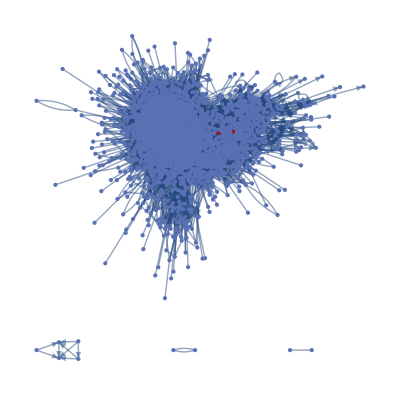

```mathematica
HighlightGraph[g,Subgraph[g,clique]]
```

```mathematica
agents=Part[VertexList[g],Ordering[BetweennessCentrality[g],-5]]
```

{Euler,Weil,Newton,Hilbert,Euclid}

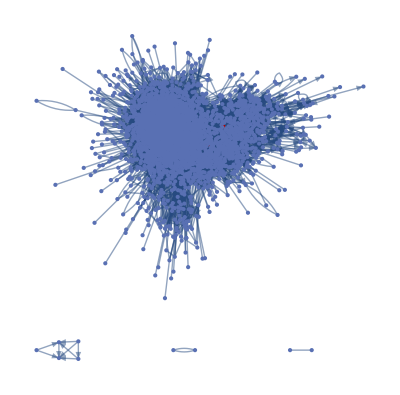

```mathematica
HighlightGraph[g,agents]
```

```mathematica
critical=BetweennessCentrality[g];
criticalNode=Pick[VertexList[g],critical,Max[critical]]
```

{Euclid}

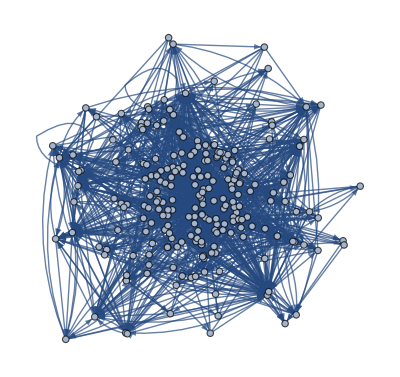

```mathematica
NeighborhoodGraph[g,criticalNode,1,GraphLayout->"SpringEmbedding",VertexLabels->Placed["Name",Tooltip]]
```

## Get Rid of JS stuff (confused!!)

```mathematica
Counts[Flatten[(StringCases[htmlBioList,"../Mathematicians/"~~Shortest[a__]~~".html"->a](StringContainsQ[#," "]&)->Nothing)]];
```

Counts::invl: The argument {{},{Ahmes (StringContainsQ[#1, ]&),Ahmes (StringContainsQ[#1, ]&)},«48»,«2725»}→Nothing is not a list.

```mathematica
"De_Morgan',550,800); return false;\">George Boole</m></font>\n</article><hr>\n<b><a href = \"../References/Walsh"
```

```mathematica
Counts[Flatten[StringCases[htmlList,"../Mathematicians/"~~Shortest[a__]~~".html"->a]]];
```

StringCases::strse: String or list of strings expected at position 1 in StringCases[dataset2,../Mathematicians/~~Shortest[a__]~~.html→a].

Counts::invl: The argument StringCases[dataset2,../Mathematicians/~~Shortest[a__]~~.html→a] is not a list.

## Counting String Length

```mathematica
ClearAll[x];

getBodyBio [ htmlString_String ] := StringCases[ htmlString ,
                                                "<article>" ~~ Shortest[ x__ ] ~~ "</article>" -> x
                                                ];
                                                
deleteHtmlElements [ htmlString_String ] := StringDelete[
                                                          getBodyBio[ htmlString ],
                                                         "<"~~Shortest[__]~~">" 
                                                         ];
                                                         
numberSentences [ htmlString_ ] := Length@First@TextCases[  htmlString , "Sentence"];

numberWords [ htmlString_] := Length@First@TextCases[ htmlString , "Word"];
```

```mathematica
formattedBios =deleteHtmlElements[#]&/@htmlBioList[[;;]]
```

{{
Ahmes is the scribe who wrote the Rhind Papyrus (named after the Scottish Egyptologist Alexander Henry Rhind who went to Thebes for health reasons, became interested in excavating and purchased the papyrus in Egypt in 1858). 

Ahmes claims not to be the author of the work, being, he claims, only a scribe. He says that the material comes from an earlier work of about 2000 BC. 

The papyrus is our chief source of information on Egyptian mathematics. The Recto contains division of 2 by the odd numbers 3 to 101 in unit fractions and the numbers 1 to 9 by 10. The Verso has 87 problems on the four operations, solution of equations, progressions, volumes of granaries, the two-thirds rule etc.

The Rhind Papyrus, which came to the British Museum in 1863, is sometimes called the 'Ahmes papyrus' in honour of Ahmes. Nothing is known of Ahmes other than his own comments in the papyrus.


The Rhind papyrus

Article by: J J O'Connor and E F Robertson
},{To write a biography of Baudhayana is essentially impossible since nothing is known of him except that he was the author of one of the earliest Sulbasutras. We do not know his dates accurately enough to even guess at a life span for him, which is why we have given the same approximate birth year as death year.

He was neither a mathematician in the sense that we would understand it today, nor a scribe who simply copied manuscripts like Ahmes. He would certainly have been a man of very considerable learning but probably not interested in mathematics for its own sake, merely interested in using it for religious purposes. Undoubtedly he wrote the Sulbasutra to provide rules for religious rites and it would appear an almost certainty that Baudhayana himself would be a Vedic priest. 

The mathematics given in the Sulbasutras is there to enable the accurate construction of altars needed for sacrifices. It is clear from the writing that Baudhayana, as well as being a priest, must have been a skilled craftsman. He must have been himself skilled in the practical use of the mathematics he described as a craftsman who himself constructed sacrificial altars of the highest quality. 

The Sulbasutras are discussed in detail in the article Indian Sulbasutras. Below we give one or two details of Baudhayana's Sulbasutra, which contained three chapters, which is the oldest which we possess and, it would be fair to say, one of the two most important.

The Sulbasutra of Baudhayana contains geometric solutions (but not algebraic ones) of a linear equation in a single unknown. Quadratic equations of the forms ax2 = c and ax2 + bx = c appear.

Several values of &#960; occur in Baudhayana's Sulbasutra since when giving different constructions Baudhayana uses different approximations for constructing circular shapes. Constructions are given which are equivalent to taking &#960; equal to 676/225 (where 676/225 = 3.004), 900/289 (where 900/289 = 3.114) and to 1156/361 (where 1156/361 = 3.202). None of these is particularly accurate but, in the context of constructing altars they would not lead to noticeable errors.

An interesting, and quite accurate, approximate value for &#8730;2 is given in Chapter 1 verse 61 of Baudhayana's Sulbasutra. The Sanskrit text gives in words what we would write in symbols as

&#8730;2 = 1 + 1/3 + 1/(3&#215;4) - 1/(3&#215;4&#215;34) = 577/408 

which is, to nine places, 1.414215686. This gives &#8730;2 correct to five decimal places. This is surprising since, as we mentioned above, great mathematical accuracy did not seem necessary for the building work described. If the approximation was given as 

&#8730;2 = 1 + 1/3 + 1/(3&#215;4)

then the error is of the order of 0.002 which is still more accurate than any of the values of &#960;. Why then did Baudhayana feel that he had to go for a better approximation?

See the article Indian Sulbasutras for more information.

Article by: J J O'Connor and E F Robertson
},{Manava was the author of one of the Sulbasutras. The Manava Sulbasutra is not the oldest (the one by Baudhayana is older) nor is it one of the most important, there being at least three Sulbasutras which are considered more important. We do not know Manava's dates accurately enough to even guess at a life span for him, which is why we have given the same approximate birth year as death year. Historians disagree on 750 BC, and some would put this Sulbasutra later by one hundred or more years.

Manava would have not have been a mathematician in the sense that we would understand it today. Nor was he a scribe who simply copied manuscripts like Ahmes. He would certainly have been a man of very considerable learning but probably not interested in mathematics for its own sake, merely interested in using it for religious purposes. Undoubtedly he wrote the Sulbasutra to provide rules for religious rites and it would appear an almost certainty that Manava himself would be a Vedic priest. 

The mathematics given in the Sulbasutras is there to enable accurate construction of altars needed for sacrifices. It is clear from the writing that Manava, as well as being a priest, must have been a skilled craftsman.

Manava's Sulbasutra, like all the Sulbasutras, contained approximate constructions of circles from rectangles, and squares from circles, which can be thought of as giving approximate values of &#960;. There appear therefore different values of &#960; throughout the Sulbasutra, essentially every construction involving circles leads to a different such approximation. The paper [',' R C Gupta, New Indian values of .b9 from the Manava sulba sutra, Centaurus 31 (2) (1988), 114-125.','1] is concerned with an interpretation of verses 11.14 and 11.15 of Manava's work which give &#960; = 25/8 = 3.125.

See the article Indian Sulbasutras for more information on the Sulbasutras in general and the mathematical results which they contain.

Article by: J J O'Connor and E F Robertson
},{Thales of Miletus was the son of Examyes and Cleobuline. His parents are said by some to be from Miletus but others report that they were Phoenicians. J Longrigg writes in [',' J Longrigg, Biography in Dictionary of Scientific Biography (New York 1970-1990).','1]:-

But the majority opinion considered him a true Milesian by descent, and of a distinguished family.
Thales seems to be the first known Greek philosopher, scientist and mathematician although his occupation was that of an engineer. He is believed to have been the teacher of Anaximander (611 BC - 545 BC) and he was the first natural philosopher in the Milesian School. However, none of his writing survives so it is difficult to determine his views or to be certain about his mathematical discoveries. Indeed it is unclear whether he wrote any works at all and if he did they were certainly lost by the time of Aristotle who did not have access to any writings of Thales. On the other hand there are claims that he wrote a book on navigation but these are based on little evidence. In the book on navigation it is suggested that he used the constellation Ursa Minor, which he defined, as an important feature in his navigation techniques. Even if the book is fictitious, it is quite probable that Thales did indeed define the constellation Ursa Minor.

Proclus, the last major Greek philosopher, who lived around 450 AD, wrote:-

[Thales] first went to Egypt and thence introduced this study [geometry] into Greece. He discovered many propositions himself, and instructed his successors in the principles underlying many others, his method of attacking problems had greater generality in some cases and was more in the nature of simple inspection and observation in other cases.
There is a difficulty in writing about Thales and others from a similar period. Although there are numerous references to Thales which would enable us to reconstruct quite a number of details, the sources must be treated with care since it was the habit of the time to credit famous men with discoveries they did not make. Partly this was as a result of the legendary status that men like Thales achieved, and partly it was the result of scientists with relatively little history behind their subjects trying to increase the status of their topic with giving it an historical background.

Certainly Thales was a figure of enormous prestige, being the only philosopher before Socrates to be among the Seven Sages. Plutarch, writing of these Seven Sages, says that (see [',' T L Heath, A History of Greek Mathematics I (Oxford, 1921).','8]):-

[Thales] was apparently the only one of these whose wisdom stepped, in speculation, beyond the limits of practical utility, the rest acquired the reputation of wisdom in politics.
This comment by Plutarch should not be seen as saying that Thales did not function as a politician. Indeed he did. He persuaded the separate states of Ionia to form a federation with a capital at Teos. He dissuaded his compatriots from accepting an alliance with Croesus and, as a result, saved the city.

It is reported that Thales predicted an eclipse of the Sun in 585 BC. The cycle of about 19 years for eclipses of the Moon was well known at this time but the cycle for eclipses of the Sun was harder to spot since eclipses were visible at different places on Earth. Thales's prediction of the 585 BC eclipse was probably a guess based on the knowledge that an eclipse around that time was possible. The claims that Thales used the Babylonian saros, a cycle of length 18 years 10 days 8 hours, to predict the eclipse has been shown by Neugebauer to be highly unlikely since Neugebauer shows in [',' O Neugebauer, The exact sciences in antiquity (Providence, R.I., 1957).','11] that the saros was an invention of Halley. Neugebauer wrote [',' O Neugebauer, The exact sciences in antiquity (Providence, R.I., 1957).','11]:-

... there exists no cycle for solar eclipses visible at a given place: all modern cycles concern the earth as a whole. No Babylonian theory for predicting a solar eclipse existed at 600 BC, as one can see from the very unsatisfactory situation 400 years later, nor did the Babylonians ever develop any theory which took the influence of geographical latitude into account.
After the eclipse on 28 May, 585 BC Herodotus wrote:-

... day was all of a sudden changed into night. This event had been foretold by Thales, the Milesian, who forewarned the Ionians of it, fixing for it the very year in which it took place. The Medes and Lydians, when they observed the change, ceased fighting, and were alike anxious to have terms of peace agreed on.
Longrigg in [',' J Longrigg, Biography in Dictionary of Scientific Biography (New York 1970-1990).','1] even doubts that Thales predicted the eclipse by guessing, writing:-

... a more likely explanation seems to be simply that Thales happened to be the savant around at the time when this striking astronomical phenomenon occurred and the assumption was made that as a savant he must have been able to predict it.
There are several accounts of how Thales measured the height of pyramids. Diogenes Laertius writing in the second century AD quotes Hieronymus, a pupil of Aristotle [',' Diogenes Laertius, Lives of eminent philosophers (New York, 1925).','6] (or see [',' T L Heath, A History of Greek Mathematics I (Oxford, 1921).','8]):-

Hieronymus says that [Thales] even succeeded in measuring the pyramids by observation of the length of their shadow at the moment when our shadows are equal to our own height.
This appears to contain no subtle geometrical knowledge, merely an empirical observation that at the instant when the length of the shadow of one object coincides with its height, then the same will be true for all other objects. A similar statement is made by Pliny (see [',' T L Heath, A History of Greek Mathematics I (Oxford, 1921).','8]):-

Thales discovered how to obtain the height of pyramids and all other similar objects, namely, by measuring the shadow of the object at the time when a body and its shadow are equal in length.
Plutarch however recounts the story in a form which, if accurate, would mean that Thales was getting close to the idea of similar triangles:-

... without trouble or the assistance of any instrument [he] merely set up a stick at the extremity of the shadow cast by the pyramid and, having thus made two triangles by the impact of the sun's rays, ... showed that the pyramid has to the stick the same ratio which the shadow [of the pyramid] has to the shadow [of the stick]
Of course Thales could have used these geometrical methods for solving practical problems, having merely observed the properties and having no appreciation of what it means to prove a geometrical theorem. This is in line with the views of Russell who writes of Thales contributions to mathematics in [',' B Russell, History of Western Philosophy (London, 1961).','12]:-

Thales is said to have travelled in Egypt, and to have thence brought to the Greeks the science of geometry. What Egyptians knew of geometry was mainly rules of thumb, and there is no reason to believe that Thales arrived at deductive proofs, such as later Greeks discovered.
On the other hand B L van der Waerden [',' B L van der Waerden,S cience Awakening (New York, 1954).','16] claims that Thales put geometry on a logical footing and was well aware of the notion of proving a geometrical theorem. However, although there is much evidence to suggest that Thales made some fundamental contributions to geometry, it is easy to interpret his contributions in the light of our own knowledge, thereby believing that Thales had a fuller appreciation of geometry than he could possibly have achieved. In many textbooks on the history of mathematics Thales is credited with five theorems of elementary geometry:-

A circle is bisected by any diameter.
The base angles of an isosceles triangle are equal.
The angles between two intersecting straight lines are equal.
Two triangles are congruent if they have two angles and one side equal.
An angle in a semicircle is a right angle.

What is the basis for these claims? Proclus, writing around 450 AD, is the basis for the first four of these claims, in the third and fourth cases quoting the work History of Geometry by Eudemus of Rhodes, who was a pupil of Aristotle, as his source. The History of Geometry by Eudemus is now lost but there is no reason to doubt Proclus. The fifth theorem is believed to be due to Thales because of a passage from Diogenes Laertius book Lives of eminent philosophers written in the second century AD [',' Diogenes Laertius, Lives of eminent philosophers (New York, 1925).','6]:-

Pamphile says that Thales, who learnt geometry from the Egyptians, was the first to describe on a circle a triangle which shall be right-angled, and that he sacrificed an ox (on the strength of the discovery). Others, however, including Apollodorus the calculator, say that it was Pythagoras.
A deeper examination of the sources, however, shows that, even if they are accurate, we may be crediting Thales with too much. For example Proclus uses a word meaning something closer to 'similar' rather than 'equal- in describing (ii). It is quite likely that Thales did not even have a way of measuring angles so 'equal- angles would have not been a concept he would have understood precisely. He may have claimed no more than "The base angles of an isosceles triangle look similar". The theorem (iv) was attributed to Thales by Eudemus for less than completely convincing reasons. Proclus writes (see [',' T L Heath, A History of Greek Mathematics I (Oxford, 1921).','8]):-

[Eudemus] says that the method by which Thales showed how to find the distances of ships from the shore necessarily involves the use of this theorem.
Heath in [',' T L Heath, A History of Greek Mathematics I (Oxford, 1921).','8] gives three different methods which Thales might have used to calculate the distance to a ship at sea. The method which he thinks it most likely that Thales used was to have an instrument consisting of two sticks nailed into a cross so that they could be rotated about the nail. An observer then went to the top of a tower, positioned one stick vertically (using say a plumb line) and then rotating the second stick about the nail until it point at the ship. Then the observer rotates the instrument, keeping it fixed and vertical, until the movable stick points at a suitable point on the land. The distance of this point from the base of the tower is equal to the distance to the ship.

Although theorem (iv) underlies this application, it would have been quite possible for Thales to devise such a method without appreciating anything of 'congruent triangles'.

As a final comment on these five theorems, there are conflicting stories regarding theorem (iv) as Diogenes Laertius himself is aware. Also even Pamphile cannot be taken as an authority since she lived in the first century AD, long after the time of Thales. Others have attributed the story about the sacrifice of an ox to Pythagoras on discovering Pythagoras's theorem. Certainly there is much confusion, and little certainty.

Our knowledge of the philosophy of Thales is due to Aristotle who wrote in his Metaphysics :-

Thales of Miletus taught that 'all things are water'.
This, as Brumbaugh writes [',' R S Brumbaugh, The philosophers of Greece (Albany, N.Y., 1981).','5]:-

...may seem an unpromising beginning for science and philosophy as we know them today; but, against the background of mythology from which it arose, it was revolutionary.
Sambursky writes in [',' F Ueberweg, A History of Philosophy, from Thales to the Present Time (1972) (2 Volumes).','15]:-

It was Thales who first conceived the principle of explaining the multitude of phenomena by a small number of hypotheses for all the various manifestations of matter.
Thales believed that the Earth floats on water and all things come to be from water. For him the Earth was a flat disc floating on an infinite ocean. It has also been claimed that Thales explained earthquakes from the fact that the Earth floats on water. Again the importance of Thales' idea is that he is the first recorded person who tried to explain such phenomena by rational rather than by supernatural means.

It is interesting that Thales has both stories told about his great practical skills and also about him being an unworldly dreamer. Aristotle, for example, relates a story of how Thales used his skills to deduce that the next season's olive crop would be a very large one. He therefore bought all the olive presses and then was able to make a fortune when the bumper olive crop did indeed arrive. On the other hand Plato tells a story of how one night Thales was gazing at the sky as he walked and fell into a ditch. A pretty servant girl lifted him out and said to him "How do you expect to understand what is going on up in the sky if you do not even see what is at your feet". As Brumbaugh says, perhaps this is the first absent-minded professor joke in the West!

The bust of Thales shown above is in the Capitoline Museum in Rome, but is not contemporary with Thales and is unlikely to bear any resemblance to him.
Article by: J J O'Connor and E F RobertsonClick on this link to see a list of the Glossary entries for this page
},{Little is known about the life of Anaximander of Miletus but we do know a little through the writings of Aristotle, Apollodorus, and Diogenes Laertius and others. We should emphasise that Apollodorus, although writing in the second century BC, was still 500 years later than Anaximander while Diogenes wrote almost 500 years after Apollodorus. Possible details of Anaximander from these sources suggest that he was the son of Praxiades and a pupil of Thales. One ancient text states that Thales was related to Anaximander - possibly his uncle. He may have succeeded Thales as head of his School of Philosophy in Miletus (as reported by Diogenes). He is reported to have travelled widely, and founded a colony called Apollonia on the coast of the Black Sea [','   Anaximander of Miletus, Internet Encyclopedia of Philosophy','9]:-

It is also reported that he displayed solemn manners and wore pompous garments.
None of Anaximander's writings survive but we do know something about his works which were still available to Aristotle and Apollodorus. His main writings are thought to have been On Nature, On the Fixed Stars, Geometric Surveying, Sphere, Map of Greece, and Map of the World. The importance of his work is that he introduced scientific and mathematical principles into the study of astronomy and geography. One should not come away with the impression that this makes his ideas plausible in light of modern knowledge, but nevertheless the attempt to bring scientific and mathematical principles into areas which had been largely the domain of mysticism until that time must mean that Anaximander plays an important role in the development of science. Let us look at his ideas.

Anaximander believed that the earth was a cylinder. If this seems a little strange, then we believe that his reasoning was that if one looked around one saw a circle, then he used a symmetry argument to argue that there was another circle with a cylinder between. He appears to have been the first person to argue that the sun, moon, planets and stars revolved around the earth so the sun which rose in the morning was the same sun that had disappeared on the evening of the preceding day. He saw each heavenly body as being a hole in an opaque circular wheel containing fire and encircling the earth. He also argued that the heavenly bodies were at different distances from the earth, but he was entirely wrong in believing that the stars were closer than any of the other heavenly bodies. He did, however, attempt to give the dimensions of the universe. The radius of the stars circles was 9 times the radius of the circle on top of the cylindrical earth, the radius of the moons circle was 18 times that of the earth, and the ratio of the sun's to the radius of the earth was 27. For more details see [','  D Ehlers, Das Problem und das Gesetz der Reihenfolge in der Entwicklung der Astronomie bis Copernicus, NTM Schr. Geschichte Naturwiss. Tech. Medizin 13 (2) (1976), 54-61. ','12].

In Anaximander's model the earth is suspended in the middle of the circling heavenly bodies.  What then keeps it in place? Aristotle writes:-

But there are some who say that the earth stays where it is because of equality, such as among the ancients Anaximander. For that which is situated in the centre and at equal distances from the extremes, has no inclination whatsoever to move up rather than down or sideways; and since it is impossible to move in opposite directions at the same time, it necessarily stays where it is.
We also know that Anaximander attempted to give an explanation for how the universe came into being. His philosophy argued that all things arose from 'apeiron', the Boundless. Aristotle writes:-

Everything has an origin or is an origin. The Boundless has no origin. For then it would have a limit. Moreover, it is both unborn and immortal, being a kind of origin. For that which has become has also, necessarily, an end, and there is a termination to every process of destruction.
Now the universe was created from the Boundless:-

A germ, filled with hot and cold, was separated off from the Boundless, then out of this germ a sphere of fire grew around the vapor that surrounds the earth, like a bark round a tree.
The sphere of fire split into several wheels which were then the wheels of the stars, moon, and sun.

Anaximander discussed the origins of life, as well as the origins of the cosmos. He argued that the young earth was covered in seas, some of which began to dry out due to the heat of the sun. Life began in the mud of the seas as they dried out. The first animals had skin covered with spines but after they began to live on dry land, the heat of the sun gradually caused the animals to have fewer spines. He argued that man was not suited to live in this early world, so could only have arisen from the animals living on dry land after conditions became suitable. One would have to say that this is a remarkable achievement, again attempting to apply scientific and logical reasoning in an area where only mystical theories existed. 

It appears that Anaximander was the first person to attempt to produce a map of the world. This map, of course, no longer exists, but it must have shown a circular earth - the top of the cylinder. It would have the Mediterranean Sea at its centre and show lands to the north and south, since this was the known world at the time.

Another first for Anaximander is the invention of the solar gnomon, see [','  A Szabó, Astronomische Messungen bei den Griechen im 5. Jahrhundert v. Chr. und ihr Instrument, Historia Sci. No. 21 (1981), 1-26.','19]. A special case of such a gnomon is the pointer on a sundial. The solar gnomon could be used to determine midday (the time of shortest shadow). Since at this time the sun was due south, the gnomon was used to find what we would call today 'the points of the compass'. Another aspect of his thought, having important implications for mathematics, is the dualism finite-infinite in his thoughts. This is discussed in detail in [','   X Renou, L&#8217;infini aux limites du calcul, Anaximandre - Platon - Galilée. Collection &#8217;Algorithme&#8217; (François Maspero, Paris, 1978).','6].  We have discussed above both his attempts to measure the scale of the heavens and also to measure distances on earth with his attempts at maps. These are shown in [','  A Sabo, The measurement of angles and the start of trigonometry (Bulgarian), Fiz.-Mat. Spis. B&#8217; lgar. Akad. Nauk. 20 (53) (2) (1977), 150-160. ','17] to be among the early Greek works that led to the modern study of trigonometry,

Article by: J J O'Connor and E F Robertson
},{To write a biography of Apastamba is essentially impossible since nothing is known of him except that he was the author of a Sulbasutra which is certainly later than the Sulbasutra of Baudhayana. It would also be fair to say that Apastamba's Sulbasutra is the most interesting from a mathematical point of view. We do not know Apastamba's dates accurately enough to even guess at a life span for him, which is why we have given the same approximate birth year as death year.

Apastamba was neither a mathematician in the sense that we would understand it today, nor a scribe who simply copied manuscripts like Ahmes. He would certainly have been a man of very considerable learning but probably not interested in mathematics for its own sake, merely interested in using it for religious purposes. Undoubtedly he wrote the Sulbasutra to provide rules for religious rites and to improve and expand on the rules which had been given by his predecessors. Apastamba would have been a Vedic priest instructing the people in the ways of conducting the religious rites he describes.

The mathematics given in the Sulbasutras is there to enable the accurate construction of altars needed for sacrifices. It is clear from the writing that Apastamba, as well as being a priest and a teacher of religious practices, would have been a skilled craftsman. He must have been himself skilled in the practical use of the mathematics he described as a craftsman who himself constructed sacrificial altars of the highest quality. 

The Sulbasutras are discussed in detail in the article Indian Sulbasutras. Below we give one or two details of Apastamba's Sulbasutra. This work is an expanded version of that of Baudhayana. Apastamba's work consisted of six chapters while the earlier work by Baudhayana contained only three.

The general linear equation was solved in the Apastamba's Sulbasutra. He also gives a remarkably accurate value for &#8730;2 namely

1 + 1/3 + 1/(3&#215;4) - 1/(3&#215;4&#215;34).

which gives an answer correct to five decimal places. A possible way that Apastamba might have reached this remarkable result is described in the article Indian Sulbasutras.

As well as the problem of squaring the circle, Apastamba considers the problem of dividing a segment into 7 equal parts. The article [',' G Kumari, Some significant results of algebra of pre-Aryabhata era, Math. Ed. (Siwan) 14 (1) (1980), B5-B13.','3] looks in detail at a reconstruction of Apastamba's version of these two problems.

Article by: J J O'Connor and E F Robertson
},{Pythagoras of Samos is often described as the first pure mathematician. He is an extremely important figure in the development of mathematics yet we know relatively little about his mathematical achievements. Unlike many later Greek mathematicians, where at least we have some of the books which they wrote, we have nothing of Pythagoras's writings. The society which he led, half religious and half scientific, followed a code of secrecy which certainly means that today Pythagoras is a mysterious figure. 

We do have details of Pythagoras's life from early biographies which use important original sources yet are written by authors who attribute divine powers to him, and whose aim was to present him as a god-like figure. What we present below is an attempt to collect together the most reliable sources to reconstruct an account of Pythagoras's life. There is fairly good agreement on the main events of his life but most of the dates are disputed with different scholars giving dates which differ by 20 years. Some historians treat all this information as merely legends but, even if the reader treats it in this way, being such an early record it is of historical importance.

Pythagoras's father was Mnesarchus ([',' Porphyry, Vita Pythagorae (Leipzig, 1886),','12] and [',' Porphyry, Life of Pythagoras in M Hadas and M Smith, Heroes and Gods (London, 1965)..','13]), while his mother was Pythais [',' Iamblichus, Life of Pythagoras (translated into English by T Taylor) (London, 1818).','8] and she was a native of Samos. Mnesarchus was a merchant who came from Tyre, and there is a story ([',' Porphyry, Vita Pythagorae (Leipzig, 1886),','12] and [',' Porphyry, Life of Pythagoras in M Hadas and M Smith, Heroes and Gods (London, 1965)..','13]) that he brought corn to Samos at a time of famine and was granted citizenship of Samos as a mark of gratitude. As a child Pythagoras spent his early years in Samos but travelled widely with his father. There are accounts of Mnesarchus returning to Tyre with Pythagoras and that he was taught there by the Chaldaeans and the learned men of Syria. It seems that he also visited Italy with his father.

Little is known of Pythagoras's childhood. All accounts of his physical appearance are likely to be fictitious except the description of a striking birthmark which Pythagoras had on his thigh. It is probable that he had two brothers although some sources say that he had three. Certainly he was well educated, learning to play the lyre, learning poetry and to recite Homer. There were, among his teachers, three philosophers who were to influence Pythagoras while he was a young man. One of the most important was Pherekydes who many describe as the teacher of Pythagoras. 

The other two philosophers who were to influence Pythagoras, and to introduce him to mathematical ideas, were Thales and his pupil Anaximander who both lived on Miletus. In [',' Iamblichus, Life of Pythagoras (translated into English by T Taylor) (London, 1818).','8] it is said that Pythagoras visited Thales in Miletus when he was between 18 and 20 years old. By this time Thales was an old man and, although he created a strong impression on Pythagoras, he probably did not teach him a great deal. However he did contribute to Pythagoras's interest in mathematics and astronomy, and advised him to travel to Egypt to learn more of these subjects. Thales's pupil, Anaximander, lectured on Miletus and Pythagoras attended these lectures. Anaximander certainly was interested in geometry and cosmology and many of his ideas would influence Pythagoras's own views.

In about 535 BC Pythagoras went to Egypt. This happened a few years after the tyrant Polycrates seized control of the city of Samos. There is some evidence to suggest that Pythagoras and Polycrates were friendly at first and it is claimed [',' Diogenes Laertius, Lives of eminent philosophers (New York, 1925).','5] that Pythagoras went to Egypt with a letter of introduction written by Polycrates. In fact Polycrates had an alliance with Egypt and there were therefore strong links between Samos and Egypt at this time. The accounts of Pythagoras's time in Egypt suggest that he visited many of the temples and took part in many discussions with the priests. According to Porphyry ([',' Porphyry, Vita Pythagorae (Leipzig, 1886),','12] and [',' Porphyry, Life of Pythagoras in M Hadas and M Smith, Heroes and Gods (London, 1965)..','13]) Pythagoras was refused admission to all the temples except the one at Diospolis where he was accepted into the priesthood after completing the rites necessary for admission.

It is not difficult to relate many of Pythagoras's beliefs, ones he would later impose on the society that he set up in Italy, to the customs that he came across in Egypt. For example the secrecy of the Egyptian priests, their refusal to eat beans, their refusal to wear even cloths made from animal skins, and their striving for purity were all customs that Pythagoras would later adopt. Porphyry in [',' Porphyry, Vita Pythagorae (Leipzig, 1886),','12] and [',' Porphyry, Life of Pythagoras in M Hadas and M Smith, Heroes and Gods (London, 1965)..','13] says that Pythagoras learnt geometry from the Egyptians but it is likely that he was already acquainted with geometry, certainly after teachings from Thales and Anaximander.

In 525 BC Cambyses II, the king of Persia, invaded Egypt. Polycrates abandoned his alliance with Egypt and sent 40 ships to join the Persian fleet against the Egyptians. After Cambyses had won the Battle of Pelusium in the Nile Delta and had captured Heliopolis and Memphis, Egyptian resistance collapsed. Pythagoras was taken prisoner and taken to Babylon. Iamblichus writes that Pythagoras (see [',' Iamblichus, Life of Pythagoras (translated into English by T Taylor) (London, 1818).','8]):-

... was transported by the followers of Cambyses as a prisoner of war. Whilst he was there he gladly associated with the Magoi ... and was instructed in their sacred rites and learnt about a very mystical worship of the gods. He also reached the acme of perfection in arithmetic and music and the other mathematical sciences taught by the Babylonians...
In about 520 BC Pythagoras left Babylon and returned to Samos. Polycrates had been killed in about 522 BC and Cambyses died in the summer of 522 BC, either by committing suicide or as the result of an accident. The deaths of these rulers may have been a factor in Pythagoras's return to Samos but it is nowhere explained how Pythagoras obtained his freedom. Darius of Persia had taken control of Samos after Polycrates' death and he would have controlled the island on Pythagoras's return. This conflicts with the accounts of Porphyry and Diogenes Laertius who state that Polycrates was still in control of Samos when Pythagoras returned there.

Pythagoras made a journey to Crete shortly after his return to Samos to study the system of laws there. Back in Samos he founded a school which was called the semicircle. Iamblichus [',' Iamblichus, Life of Pythagoras (translated into English by T Taylor) (London, 1818).','8] writes in the third century AD that:-

... he formed a school in the city [of Samos], the 'semicircle' of Pythagoras, which is known by that name even today, in which the Samians hold political meetings. They do this because they think one should discuss questions about goodness, justice and expediency in this place which was founded by the man who made all these subjects his business. Outside the city he made a cave the private site of his own philosophical teaching, spending most of the night and daytime there and doing research into the uses of mathematics...
Pythagoras left Samos and went to southern Italy in about 518 BC (some say much earlier). Iamblichus [',' Iamblichus, Life of Pythagoras (translated into English by T Taylor) (London, 1818).','8] gives some reasons for him leaving. First he comments on the Samian response to his teaching methods:-

... he tried to use his symbolic method of teaching which was similar in all respects to the lessons he had learnt in Egypt. The Samians were not very keen on this method and treated him in a rude and improper manner.
This was, according to Iamblichus, used in part as an excuse for Pythagoras to leave Samos:-

... Pythagoras was dragged into all sorts of diplomatic missions by his fellow citizens and forced to participate in public affairs. ... He knew that all the philosophers before him had ended their days on foreign soil so he decided to escape all political responsibility, alleging as his excuse, according to some sources, the contempt the Samians had for his teaching method.
Pythagoras founded a philosophical and religious school in Croton (now Crotone, on the east of the heel of southern Italy) that had many followers. Pythagoras was the head of the society with an inner circle of followers known as mathematikoi. The mathematikoi lived permanently with the Society, had no personal possessions and were vegetarians. They were taught by Pythagoras himself and obeyed strict rules. The beliefs that Pythagoras held were [',' Biography in Encyclopaedia Britannica.','2]:-

(1) that at its deepest level, reality is mathematical in nature,
(2) that philosophy can be used for spiritual purification,
(3) that the soul can rise to union with the divine,
(4) that certain symbols have a mystical significance, and
(5) that all brothers of the order should observe strict loyalty and secrecy.
Both men and women were permitted to become members of the Society, in fact several later women Pythagoreans became famous philosophers. The outer circle of the Society were known as the akousmatics and they lived in their own houses, only coming to the Society during the day. They were allowed their own possessions and were not required to be vegetarians.

Of Pythagoras's actual work nothing is known. His school practised secrecy and communalism making it hard to distinguish between the work of Pythagoras and that of his followers. Certainly his school made outstanding contributions to mathematics, and it is possible to be fairly certain about some of Pythagoras's mathematical contributions. First we should be clear in what sense Pythagoras and the mathematikoi were studying mathematics. They were not acting as a mathematics research group does in a modern university or other institution. There were no 'open problems' for them to solve, and they were not in any sense interested in trying to formulate or solve mathematical problems. 

Rather Pythagoras was interested in the principles of mathematics, the concept of number, the concept of a triangle or other mathematical figure and the abstract idea of a proof. As Brumbaugh writes in [',' R S Brumbaugh, The philosophers of Greece (Albany, N.Y., 1981).','3]:-

It is hard for us today, familiar as we are with pure mathematical abstraction and with the mental act of generalisation, to appreciate the originality of this Pythagorean contribution.
In fact today we have become so mathematically sophisticated that we fail even to recognise 2 as an abstract quantity. There is a remarkable step from 2 ships + 2 ships = 4 ships, to the abstract result 2 + 2 = 4, which applies not only to ships but to pens, people, houses etc. There is another step to see that the abstract notion of 2 is itself a thing, in some sense every bit as real as a ship or a house.

Pythagoras believed that all relations could be reduced to number relations. As Aristotle wrote:-

The Pythagorean ... having been brought up in the study of mathematics, thought that things are numbers ... and that the whole cosmos is a scale and a number.
This generalisation stemmed from Pythagoras's observations in music, mathematics and astronomy. Pythagoras noticed that vibrating strings produce harmonious tones when the ratios of the lengths of the strings are whole numbers, and that these ratios could be extended to other instruments. In fact Pythagoras made remarkable contributions to the mathematical theory of music. He was a fine musician, playing the lyre, and he used music as a means to help those who were ill.

Pythagoras studied properties of numbers which would be familiar to mathematicians today, such as even and odd numbers, triangular numbers, perfect numbers etc. However to Pythagoras numbers had personalities which we hardly recognise as mathematics today [',' R S Brumbaugh, The philosophers of Greece (Albany, N.Y., 1981).','3]:-

Each number had its own personality - masculine or feminine, perfect or incomplete, beautiful or ugly. This feeling modern mathematics has deliberately eliminated, but we still find overtones of it in fiction and poetry. Ten was the very best number: it contained in itself the first four integers - one, two, three, and four [',' K von Fritz, Biography in Dictionary of Scientific Biography (New York 1970-1990). ','1 + 2 + 3 + 4 = 10] - and these written in dot notation formed a perfect triangle.
Of course today we particularly remember Pythagoras for his famous geometry theorem. Although the theorem, now known as Pythagoras's theorem, was known to the Babylonians 1000 years earlier he may have been the first to prove it. Proclus, the last major Greek philosopher, who lived around 450 AD wrote (see [',' T L Heath, A history of Greek mathematics 1 (Oxford, 1931).','7]):-

After [Thales, etc.] Pythagoras transformed the study of geometry into a liberal education, examining the principles of the science from the beginning and probing the theorems in an immaterial and intellectual manner: he it was who discovered the theory of irrational and the construction of the cosmic figures.
Again Proclus, writing of geometry, said:-

I emulate the Pythagoreans who even had a conventional phrase to express what I mean "a figure and a platform, not a figure and a sixpence", by which they implied that the geometry which is deserving of study is that which, at each new theorem, sets up a platform to ascend by, and lifts the soul on high instead of allowing it to go down among the sensible objects and so become subservient to the common needs of this mortal life.
Heath [',' T L Heath, A history of Greek mathematics 1 (Oxford, 1931).','7] gives a list of theorems attributed to Pythagoras, or rather more generally to the Pythagoreans.

(i) The sum of the angles of a triangle is equal to two right angles. Also the Pythagoreans knew the generalisation which states that a polygon with n sides has sum of interior angles 2n - 4 right angles and sum of exterior angles equal to four right angles.

(ii) The theorem of Pythagoras - for a right angled triangle the square on the hypotenuse is equal to the sum of the squares on the other two sides. We should note here that to Pythagoras the square on the hypotenuse would certainly not be thought of as a number multiplied by itself, but rather as a geometrical square constructed on the side. To say that the sum of two squares is equal to a third square meant that the two squares could be cut up and reassembled to form a square identical to the third square.

(iii) Constructing figures of a given area and geometrical algebra. For example they solved equations such as a (a - x) = x2 by geometrical means.

(iv) The discovery of irrationals. This is certainly attributed to the Pythagoreans but it does seem unlikely to have been due to Pythagoras himself. This went against Pythagoras's philosophy the all things are numbers, since by a number he meant the ratio of two whole numbers. However, because of his belief that all things are numbers it would be a natural task to try to prove that the hypotenuse of an isosceles right angled triangle had a length corresponding to a number.

(v) The five regular solids. It is thought that Pythagoras himself knew how to construct the first three but it is unlikely that he would have known how to construct the other two.

(vi) In astronomy Pythagoras taught that the Earth was a sphere at the centre of the Universe. He also recognised that the orbit of the Moon was inclined to the equator of the Earth and he was one of the first to realise that Venus as an evening star was the same planet as Venus as a morning star.

Primarily, however, Pythagoras was a philosopher. In addition to his beliefs about numbers, geometry and astronomy described above, he held [',' Biography in Encyclopaedia Britannica.','2]:-

... the following philosophical and ethical teachings: ... the dependence of the dynamics of world structure on the interaction of contraries, or pairs of opposites; the viewing of the soul as a self-moving number experiencing a form of metempsychosis, or successive reincarnation in different species until its eventual purification (particularly through the intellectual life of the ethically rigorous Pythagoreans); and the understanding ...that all existing objects were fundamentally composed of form and not of material substance. Further Pythagorean doctrine ... identified the brain as the locus of the soul; and prescribed certain secret cultic practices.
In [',' R S Brumbaugh, The philosophers of Greece (Albany, N.Y., 1981).','3] their practical ethics are also described:-

In their ethical practices, the Pythagorean were famous for their mutual friendship, unselfishness, and honesty.
Pythagoras's Society at Croton was not unaffected by political events despite his desire to stay out of politics. Pythagoras went to Delos in 513 BC to nurse his old teacher Pherekydes who was dying. He remained there for a few months until the death of his friend and teacher and then returned to Croton. In 510 BC Croton attacked and defeated its neighbour Sybaris and there is certainly some suggestions that Pythagoras became involved in the dispute. Then in around 508 BC the Pythagorean Society at Croton was attacked by Cylon, a noble from Croton itself. Pythagoras escaped to Metapontium and the most authors say he died there, some claiming that he committed suicide because of the attack on his Society. Iamblichus in [',' Iamblichus, Life of Pythagoras (translated into English by T Taylor) (London, 1818).','8] quotes one version of events:-

Cylon, a Crotoniate and leading citizen by birth, fame and riches, but otherwise a difficult, violent, disturbing and tyrannically disposed man, eagerly desired to participate in the Pythagorean way of life. He approached Pythagoras, then an old man, but was rejected because of the character defects just described. When this happened Cylon and his friends vowed to make a strong attack on Pythagoras and his followers. Thus a powerfully aggressive zeal activated Cylon and his followers to persecute the Pythagoreans to the very last man. Because of this Pythagoras left for Metapontium and there is said to have ended his days.
This seems accepted by most but Iamblichus himself does not accept this version and argues that the attack by Cylon was a minor affair and that Pythagoras returned to Croton. Certainly the Pythagorean Society thrived for many years after this and spread from Croton to many other Italian cities. Gorman [',' P Gorman, Pythagoras, a life (1979).','6] argues that this is a strong reason to believe that Pythagoras returned to Croton and quotes other evidence such as the widely reported age of Pythagoras as around 100 at the time of his death and the fact that many sources say that Pythagoras taught Empedokles to claim that he must have lived well after 480 BC.

The evidence is unclear as to when and where the death of Pythagoras occurred. Certainly the Pythagorean Society expanded rapidly after 500 BC, became political in nature and also spilt into a number of factions. In 460 BC the Society [',' Biography in Encyclopaedia Britannica.','2]:-

... was violently suppressed. Its meeting houses were everywhere sacked and burned; mention is made in particular of "the house of Milo" in Croton, where 50 or 60 Pythagoreans were surprised and slain. Those who survived took refuge at Thebes and other places.
Article by: J J O'Connor and E F RobertsonClick on this link to see a list of the Glossary entries for this page
},{Panini was born in Shalatula, a town near to Attock on the Indus river in present day Pakistan. The dates given for Panini are pure guesses. Experts give dates in the 4th, 5th, 6th and 7th century BC and there is also no agreement among historians about the extent of the work which he undertook. What is in little doubt is that, given the period in which he worked, he is one of the most innovative people in the whole development of knowledge. We will say a little more below about how historians have gone about trying to pinpoint the date when Panini lived.

Panini was a Sanskrit grammarian who gave a comprehensive and scientific theory of phonetics, phonology, and morphology. Sanskrit was the classical literary language of the Indian Hindus and Panini is considered the founder of the language and literature. It is interesting to note that the word "Sanskrit" means "complete" or "perfect" and it was thought of as the divine language, or language of the gods.

A treatise called Astadhyayi (or Astaka ) is Panini's major work. It consists of eight chapters, each subdivided into quarter chapters. In this work Panini distinguishes between the language of sacred texts and the usual language of communication. Panini gives formal production rules and definitions to describe Sanskrit grammar. Starting with about 1700 basic elements like nouns, verbs, vowels, consonants he put them into classes. The construction of sentences, compound nouns etc. is explained as ordered rules operating on underlying structures in a manner similar to modern theory. In many ways Panini's constructions are similar to the way that a mathematical function is defined today. Joseph writes in [',' G G Joseph, The crest of the peacock (London, 1991).','2]:-

[Sanskrit's] potential for scientific use was greatly enhanced as a result of the thorough systemisation of its grammar by Panini. ... On the basis of just under 4000 sutras [rules expressed as aphorisms], he built virtually the whole structure of the Sanskrit language, whose general 'shape' hardly changed for the next two thousand years. ... An indirect consequence of Panini's efforts to increase the linguistic facility of Sanskrit soon became apparent in the character of scientific and mathematical literature. This may be brought out by comparing the grammar of Sanskrit with the geometry of Euclid - a particularly apposite comparison since, whereas mathematics grew out of philosophy in ancient Greece, it was ... partly an outcome of linguistic developments in India.
Joseph goes on to make a convincing argument for the algebraic nature of Indian mathematics arising as a consequence of the structure of the Sanskrit language. In particular he suggests that algebraic reasoning, the Indian way of representing numbers by words, and ultimately the development of modern number systems in India, are linked through the structure of language.

Panini should be thought of as the forerunner of the modern formal language theory used to specify computer languages. The Backus Normal Form was discovered independently by John Backus in 1959, but Panini's notation is equivalent in its power to that of Backus and has many similar properties. It is remarkable to think that concepts which are fundamental to today's theoretical computer science should have their origin with an Indian genius around 2500 years ago.

At the beginning of this article we mentioned that certain concepts had been attributed to Panini by certain historians which others dispute. One such theory was put forward by B Indraji in 1876. He claimed that the Brahmi numerals developed out of using letters or syllables as numerals. Then he put the finishing touches to the theory by suggesting that Panini in the eighth century BC (earlier than most historians place Panini) was the first to come up with the idea of using letters of the alphabet to represent numbers.

There are a number of pieces of evidence to support Indraji's theory that the Brahmi numerals developed from letters or syllables. However it is not totally convincing since, to quote one example, the symbols for 1, 2 and 3 clearly do not come from letters but from one, two and three lines respectively. Even if one accepts the link between the numerals and the letters, making Panini the originator of this idea would seem to have no more behind it than knowing that Panini was one of the most innovative geniuses that world has known so it is not unreasonable to believe that he might have made this step too.

There are other works which are closely associated with the Astadhyayi which some historians attribute to Panini, others attribute to authors before Panini, others attribute to authors after Panini. This is an area where there are many theories but few, if any, hard facts.

We also promised to return to a discussion of Panini's dates. There has been no lack of work on this topic so the fact that there are theories which span several hundreds of years is not the result of lack of effort, rather an indication of the difficulty of the topic. The usual way to date such texts would be to examine which authors are referred to and which authors refer to the work. One can use this technique and see who Panini mentions.

There are ten scholars mentioned by Panini and we must assume from the context that these ten have all contributed to the study of Sanskrit grammar. This in itself, of course, indicates that Panini was not a solitary genius but, like Newton, had "stood on the shoulders of giants". Panini must have lived later than these ten but this is absolutely no help in providing dates since we have absolutely no knowledge of when any of these ten lived.

What other internal evidence is there to use? Well of course Panini uses many phrases to illustrate his grammar any these have been examined meticulously to see if anything is contained there to indicate a date. To give an example of what we mean: if we were to pick up a text which contained as an example "I take the train to work every day" we would know that it had to have been written after railways became common. Let us illustrate with two actual examples from the Astadhyayi which have been the subject of much study. The first is an attempt to see whether there is evidence of Greek influence. Would it be possible to find evidence which would mean that the text had to have been written after the conquests of Alexander the Great? There is a little evidence of Greek influence, but there was Greek influence on this north east part of the Indian subcontinent before the time of Alexander. Nothing conclusive has been identified.

Another angle is to examine a reference Panini makes to nuns. Some argue that these must be Buddhist nuns and therefore the work must have been written after Buddha. A nice argument but there is a counter argument which says that there were Jaina nuns before the time of Buddha and Panini's reference could equally well be to them. Again the evidence is inconclusive.

There are references by others to Panini. However it would appear that the Panini to whom most refer is a poet and although some argue that these are the same person, most historians agree that the linguist and the poet are two different people. Again this is inconclusive evidence.

Let us end with an evaluation of Panini's contribution by Cardona in [',' G Cardona, Panini : a survey of research (Paris, 1976).','1]:-

Panini's grammar has been evaluated from various points of view. After all these different evaluations, I think that the grammar merits asserting ... that it is one of the greatest monuments of human intelligence.
Article by: J J O'Connor and E F Robertson
},{Anaxagoras of Clazomenae was described by Proclus, the last major Greek philosopher, who lived around 450 AD as (see for example [',' T L Heath, A history of Greek mathematics 1 (Oxford, 1931).','4]):-

After [Pythagoras] Anaxagoras of Clazomenae dealt with many questions in geometry...
Anaxagoras was an Ionian, born in the neighbourhood of Smyrna in what today is Turkey. We know few details of his early life, but certainly he lived the first part of his life in Ionia where he learnt about the new studies that were taking place there in philosophy and the new found enthusiasm for a scientific study of the world. He came from a rich family but he gave up his wealth. As Heath writes in [',' T L Heath, A history of Greek mathematics 1 (Oxford, 1931).','4]:-

He neglected his possessions, which were considerable, in order to devote himself to science.
Although Ionia had produced philosophers such as Pythagoras, up to the time of Anaxagoras this new study of knowledge had not spread to Athens. Anaxagoras is famed as the first to introduce philosophy to the Athenians when he moved there in about 480 BC. During Anaxagoras's stay in Athens, Pericles rose to power. Pericles, who was about five years younger than Anaxagoras, was a military and political leader who was successful in both developing democracy and building an empire which made Athens the political and cultural centre of Greece. Anaxagoras and Pericles became friends but this friendship had its drawbacks since Pericles' political opponents also set themselves against Anaxagoras.

In about 450 BC Anaxagoras was imprisoned for claiming that the Sun was not a god and that the Moon reflected the Sun's light. This seems to have been instigated by opponents of Pericles. Russell in [',' B Russell, History of Western Philosophy (London, 1961), 79-81.','6] writes:-

The citizens of Athens ... passed a law permitting impeachment of those who did not practice religion and taught theories about 'the things on high'. Under this law they persecuted Anaxagoras, who was accused of teaching that the sun was a red-hot stone and the moon was earth.
We should examine this teaching of Anaxagoras about the sun more closely for, although it was used as a reason to put him in prison, it is a most remarkable teaching. It was based on his doctrine of "nous" which is translated as "mind" or "reason". Initially "all things were together" and matter was some homogeneous mixture. The nous set up a vortex in this mixture. The rotation [',' T L Heath, A history of Greek mathematics 1 (Oxford, 1931).','4]:-

... began in the centre and then gradually spread, taking in wider and wider circles. The first effect was to separate two great masses, one consisting of the rare, hot, dry, called the "aether", the other of the opposite categories and called "air". The aether took the outer, the air the inner place. From the air were next separated clouds, water, earth and stones. The dense, the moist, the dark and cold, and all the heaviest things, collected in the centre as a result of the circular motion, and it was from these elements when consolidated that the earth was formed; but after this, in consequence of the violence of the whirling motion, the surrounding fiery aether tore stones away from the earth and kindled them into stars.
There are remarkable insights in this description. The idea of differentiation of matter which plays a large role in modern theories of creation of the solar system is present. Anaxagoras also shows an understanding of centrifugal force which again shows the major scientific insights that he possessed.

Anaxagoras proposed that the moon shines by reflected light from the "red-hot stone" which was the sun, the first such recorded claim. Showing great genius he was also then able to take the next step and become the first to explain correctly the reason for eclipses of the sun and moon. His explanation of eclipses of the sun is completely correct but he did spoil his explanation of eclipses of the moon by proposing that in addition to being caused by the shadow of the earth, there were other dark bodies between the earth and the moon which also caused eclipses of the moon. It is a little unclear why he felt it necessary to postulate the existence of these bodies but it does not detract from this major breakthrough in mathematical astronomy. There is also other evidence to suggest that Anaxagoras had applied geometry to the study of astronomy.

As to the structure of matter, Anaxagoras postulated an infinite number of elements, or basic building blocks. He claimed:-

... there is a portion of every thing, i.e. of every elemental stuff, in every thing...[but] each is and was most manifestly those things of which there is most in it.
However, it was the power of nous, or mind, that not only created the world but also was the driving force in its day to day processes. For example [',' Biography in Encyclopaedia Britannica.','2]:-

The growth of living things, according to Anaxagoras, depends on the power of mind within the organisms that enables them to extract nourishment from surrounding substances.
Aristotle both found much to praise in Anaxagoras's theory of nous. Both Plato and Aristotle, however, were critical of the fact that the driving force of the nous as proposed by Anaxagoras was not ethical. They wanted nous to always act in the best interests of the world. In fact the nous of Anaxagoras does provide a mechanical explanation of the world after the non-mechanical start when the vortex is produced. It is worth noting that Newton's mechanical universe would have more in common with Anaxagoras's views than the continuing ethical intelligence proposed by Plato and Aristotle.

We can obtain some clues to the mathematics that Anaxagoras studied but, unfortunately, very little remains in the records to allow us to know of definite results which he may have proved. While in prison he tried to solve the problem of squaring the circle, that is constructing with ruler and compasses a square with area equal to that of a given circle. This is the first record of this problem being studied and this problem, and other similar problems, were to play a major role in the development of Greek mathematics.

One other intriguing piece of information comes from the writing of Vitruvius, a Roman architect, engineer, and author who lived in the first century BC. He records information about the painting of stage scenes for the plays which were performed in Athens and says that Anaxagoras wrote a treatise on how to paint scenes so that some objects appeared to be in the foreground while other appeared in the background. This fascinating comment must mean that Anaxagoras wrote a treatise on perspective, but sadly no such work survives.

Anaxagoras was saved from prison by Pericles but had to leave Athens. He returned to Ionia where he founded a school at Lampsacus. This Greek city on the Asiatic shore of the Hellespont was the place for the worship of Priapus, a god of procreation and fertility. Anaxagoras died there and the anniversary of his death became a holiday for schoolchildren.

The best that we can hope to learn of Anaxagoras's personality is from the story that when once asked what as the point of being born he replied [',' T L Heath, A history of Greek mathematics 1 (Oxford, 1931).','4]:-

The investigation of sun. moon, and heaven.
Even if this story is fictitious, it is likely to be based on the way that Anaxagoras lived his life and so tells us something of the personality of this remarkable scientist who gave a description of the creation of the solar system that took 2000 years to improve upon.
Article by: J J O'Connor and E F RobertsonClick on this link to see a list of the Glossary entries for this page
},{Empedocles was born in Acragas on the south coast of Sicily. The name Acragas is Greek, while the Latin name for the town was Agrigentum. Later the town was called Girgenti and more recently it became known by its present name of Agrigento. It was one of the most beautiful cities of the ancient world up to the time it was destroyed by the Carthaginians in 406 BC. It was, in Empedocles time, a rich city containing the finest Greek culture. Some of the Pythagoreans had come there after being attacked in their centre at Croton.

Empedocles was born into a rich aristocratic family. He travelled throughout the Greek world participating fully in the extraordinary desire for learning and understanding which gripped that part of the world. He is described as follows by Sarton [',' G Sarton, Ancient Science through the Golden Age of Greece (New York, 1980).','5]:-

He was not only a philosopher but a poet, a seer, a physicist, a social reformer, a man of so much enthusiasm that he would easily be considered a charlatan by some people, or become a legendary hero in the eyes of others.
There are many legends regarding Empedocles life. He wrote poetry and 450 lines of such had been preserved by later writers such as Simplicius, Aristotle, Plutarch and others. It is not difficult to see the source of most of the legends about Empedocles for these are built on the poems that he wrote himself. In these he claims god-like powers, but whether this was simply a poetic style or whether he really did believe that he had such powers it is hard to say. Certainly his poems were much appreciated, for example Lucretius admired his hexametric poetry.

If we are to gather anything about the character of the man then it will come from the lines of poetry which have been preserved: 400 lines from his poem Peri physeos (On Nature) and the remainder from his poem Katharmoi (Purifications). These [',' A P D Maurelatos, Biography in Dictionary of Scientific Biography (New York 1970-1990). ','1]:-

... reveal a man of fervid imagination, versatility, and eloquence, with a touch of theatricality.
Some details of his travels appear accurate. He went to Italy and was in the town of Thurii, Lucania shortly after 445 BC. From there he went to the Peloponnese and he was in Olympia in 440 BC. His songs were sung at the Olympic games in that year. He had a young friend, Pausanias the son of Anchitos, who went with him on his travels. Of the many legends regarding his death, the most likely would appear to be that he died following a feast in the Peloponnese. Sarton writes [',' G Sarton, Ancient Science through the Golden Age of Greece (New York, 1980).','5]:-

Empedocles was so great and rare a man that he left no school; none of his admirers or disciples, not even the faithful Pausanias, was able to continue the master's work.
Certainly Empedocles was attributed with many "firsts". Aristotle is said to have considered him the inventor of rhetoric while Galen regarded him as the founder of the science of medicine in Italy. He is best known, however, for his belief that all matter was composed of four elements: fire, air, water, and earth.

The reason for his four element theory was to argue a modification of the belief of the Eleatic School, one of the leading pre-Socratic schools of Greek philosophy, which had been founded by Parmenides in Elea in southern Italy. The philosophy of this school, which included Zeno of Elea, was the claim that the many things which appear to exist are merely a single eternal reality. Empedocles did not go for the "all is one" version, but his "all is composed of the four elements" is extremely important in the development of science since it was adopted by Plato and Aristotle. As Sarton writes [',' G Sarton, Ancient Science through the Golden Age of Greece (New York, 1980).','5]:-

In spite of its arbitrariness, that hypothesis had a singular fortune, for it dominated Western thought in one form or another almost until the eighteenth century.
We should also note an important feature of the hypothesis. It, like the ideas of Pythagoras, tried to explain the multitude of complexity seen in the world as being the consequence of a small number of simple underlying properties. Although we no longer believe in Empedocles' four element theory, we do still look for simple mathematics which will explain the complex phenomena that surround us.

Empedocles did not base his four element hypothesis on any experimental evidence. He did base some other scientific ideas on experiment, however, and he showed by experiment that air existed and was not empty space. He did this with a clepsydra, a vessel with a hole in the bottom and one in the top. Placing the bottom hole of the vessel under water, Empedocles observed that the vessel filled up with water. If, however, he put his finger over the top hole, then the water did not enter the hole at the bottom but it did once he removed his finger. Empedocles correctly deduced that the air in the container prevented the water entering.

Empedocles believed that light travelled with a finite velocity, not through any experimental evidence, of course, but simply through reasoning. Aristotle writes in De sensu :-

Empedocles says that the light from the Sun arrives first in the intervening space before it comes to the eye, or reaches the Earth. This might plausibly seem to be the case. For whatever is moved through space, is moved from one place to another; hence, there must be a corresponding interval of time also in which it is moved from the one place to the other. But any given time is divisible into parts; so that we should assume a time when the sun's ray was not as yet seen, but was still travelling in the middle space.
It is remarkable how many of Empedocles' ideas have turned out to be correct. In addition to his belief in the finite velocity of light he also developed a crude evolutionary theory based on the survival of the fittest. He also had a form of the law of conservation of energy and had a theory of constant proportions in chemical reactions. His ideas, although they had little influence on the development of science, can be seen in the light of our current scientific knowledge to be quite incredible. If we have to explain how such prophetically correct ideas could have such little influence we have to agree with the philosopher Hans Reichenbach who, in a book published in 1957, said (see [',' A P D Maurelatos, Biography in Dictionary of Scientific Biography (New York 1970-1990). ','1]):-

... a good idea stated within an insufficient theoretical frame loses its explanatory power and is forgotten.
Article by: J J O'Connor and E F RobertsonClick on this link to see a list of the Glossary entries for this page
},{Very little is known about the life of Oenopides of Chios except that his place of birth was the island of Chios. We believe that Oenopides was in Athens when a young man but there is only circumstantial evidence for this.

In Plato's Erastae Oenopides is described as (see for example [',' I Bulmer-Thomas, Biography in Dictionary of Scientific Biography (New York 1970-1990). ','1]):-

... having acquired a reputation for mathematics...
and Plato also describes a scene where Socrates comes across two young men in the school of Dionysius who was Plato's teacher. The young men were discussing a question in mathematical astronomy which had been tackled by Oenopides and Anaxagoras. This question was certainly that of the angle that the ecliptic makes with the celestial equator. Bulmer-Thomas writes in [',' I Bulmer-Thomas, Biography in Dictionary of Scientific Biography (New York 1970-1990). ','1]:-

... it was probably [Oenopides] who settled on the value of 24&#176;, which was accepted in Greece until refined by Eratosthenes. Indeed, if Oenopides did not fix on this or some other figure it is difficult to know in what his achievement consisted, for the Babylonians no less than the Pythagoreans and Egyptians must have realised from early days that the apparent path of the sun was inclined to the celestial equator.
However, in contrast to these claims, Heath writes [',' T L Heath, A history of Greek mathematics I, II (Oxford, 1931).','2]:-

It does not appear that Oenopides made any measurement of the obliquity of the ecliptic.
Another major contribution to mathematical astronomy made by Oenopides was his discovery of the period of the Great Year. Originally the "Great Year" was the period after which the motions of the sun and moon came to repeat themselves. Later it came to mean the period after which the motions of the sun, moon and planets all repeated themselves so in the period of one Great Year all should have returned to their positions at the beginning of the Great Year.

Oenopides gave a value of the Great Year as 59 years. Heath writes [',' T L Heath, A history of Greek mathematics I, II (Oxford, 1931).','2]:-

His Great Year clearly had reference to the sun and moon only; he merely sought to find the least integral number of complete years which would contain an exact number of lunar months.
Based on this Paul Tannery [',' P Tannery, La grande année d&#8217;Aristarque de Samos, Mémoires de la Société des sciences physiques et naturelles de Bordeaux 4 (1888), 79-96.','5] showed that Oenopides' result leads to a lunar month of 29.53013 days which is remarkably close to the modern value of 29.53059 days. However many historians doubt whether Oenopides could have collected sufficient good quality data to enable him to obtain a value as accurate as this. To collect the data for even one period requires 59 years and this makes it almost impossible for someone to gather the data in their own lifetime.

Toomer believed that in fact despite Oenopides' Great Year of 59 years, he did not have this accurate value for the length of the month, and later calculations were made using better data than would have been available to Oenopides to give this very accurate value for the length of the month, more accurate than Oenopides could ever have known.

Paul Tannery in [',' P Tannery, La grande année d&#8217;Aristarque de Samos, Mémoires de la Société des sciences physiques et naturelles de Bordeaux 4 (1888), 79-96.','5] makes another claim however when he states that Oenopides considered some of the planets as well as the sun and moon as part of his 59 year Great Year. The data works well for some of the planets, for example Saturn is only 2&#176; from its starting position at the end of the 59 year cycle. Tannery is forced to conclude that not all the planets could have been taken into account by Oenopides, however, as some of the planets would be in the wrong sign of the Zodiac after the period ended.

Proclus attributes two theorems which appear in Euclid's Elements to Oenopides. These are to draw a perpendicular to a line from a given point not on the line, and to construct on a line from a given point a line at a given angle to the first line. These are elementary results but Heath believes that their significance might be that Oenopides set out for the first time the explicit 'ruler and compass' type of allowable construction. He writes [',' T L Heath, A history of Greek mathematics I, II (Oxford, 1931).','2]:-

... [Oenopides] may have been the first to lay down the restriction of the means permissible in constructions with ruler and compasses which became a canon of Greek geometry for all plane constructions...
Oenopides also developed a theory to account for the Nile floods. He suggested that heat stored in the ground during the winter dries up the underground water so that the river shrinks. In the summer the heat disappears, as testing the temperature of deep wells suggests, and water flows up into the river so causing floods. This theory, which of course is false, did not prove popular as other rivers in Libya were subject to similar conditions but did not behave in the same way.

We have some other indications of the philosophy of Oenopides. He is said to have believed in fire and air as basic elements and thought of the world as a living being with God as its soul.
Article by: J J O'Connor and E F RobertsonClick on this link to see a list of the Glossary entries for this page
},{Very little is known of the life of Zeno of Elea. We certainly know that he was a philosopher, and he is said to have been the son of Teleutagoras. The main source of our knowledge of Zeno comes from the dialogue Parmenides written by Plato. 

Zeno was a pupil and friend of the philosopher Parmenides and studied with him in Elea. The Eleatic School, one of the leading pre-Socratic schools of Greek philosophy, had been founded by Parmenides in Elea in southern Italy. His philosophy of monism claimed that the many things which appear to exist are merely a single eternal reality which he called Being. His principle was that "all is one" and that change or non-Being are impossible. Certainly Zeno was greatly influenced by the arguments of Parmenides and Plato tells us that the two philosophers visited Athens together in around 450 BC.

Despite Plato's description of the visit of Zeno and Parmenides to Athens, it is far from universally accepted that the visit did indeed take place. However, Plato tells us that Socrates, who was then young, met Zeno and Parmenides on their visit to Athens and discussed philosophy with them. Given the best estimates of the dates of birth of these three philosophers, Socrates would be about 20, Zeno about 40, and Parmenides about 65 years of age at the time, so Plato's claim is certainly possible.

Zeno had already written a work on philosophy before his visit to Athens and Plato reports that Zeno's book meant that he had achieved a certain fame in Athens before his visit there. Unfortunately no work by Zeno has survived, but there is very little evidence to suggest that he wrote more than one book. The book Zeno wrote before his visit to Athens was his famous work which, according to Proclus, contained forty paradoxes concerning the continuum. Four of the paradoxes, which we shall discuss in detail below, were to have a profound influence on the development of mathematics.

Diogenes Laertius [',' V Ya Komarova, The teachings of Zeno of Elea : An attempt to reconstruct a system of arguments (Russian) (Leningrad, 1988).','10] gives further details of Zeno's life which are generally thought to be unreliable. Zeno returned to Elea after the visit to Athens and Diogenes Laertius claims that he met his death in a heroic attempt to remove a tyrant from the city of Elea. The stories of his heroic deeds and torture at the hands of the tyrant may well be pure inventions. Diogenes Laertius also writes about Zeno's cosmology and again there is no supporting evidence regarding this, but we shall give some indication below of the details.

Zeno's book of forty paradoxes was, according to Plato [',' T L Heath, A history of Greek mathematics 1 (Oxford, 1931).','8]:-

... a youthful effort, and it was stolen by someone, so that the author had no opportunity of considering whether to publish it or not. Its object was to defend the system of Parmenides by attacking the common conceptions of things.
Proclus also described the work and confirms that [',' K von Fritz, Biography in Dictionary of Scientific Biography (New York 1970-1990).','1]:-

... Zeno elaborated forty different paradoxes following from the assumption of plurality and motion, all of them apparently based on the difficulties deriving from an analysis of the continuum.
In his arguments against the idea that the world contains more than one thing, Zeno derived his paradoxes from the assumption that if a magnitude can be divided then it can be divided infinitely often. Zeno also assumes that a thing which has no magnitude cannot exist. Simplicius, the last head of Plato's Academy in Athens, preserved many fragments of earlier authors including Parmenides and Zeno. Writing in the first half of the sixth century he explained Zeno's argument why something without magnitude could not exist [',' K von Fritz, Biography in Dictionary of Scientific Biography (New York 1970-1990).','1]:-

For if it is added to something else, it will not make it bigger, and if it is subtracted, it will not make it smaller. But if it does not make a thing bigger when added to it nor smaller when subtracted from it, then it appears obvious that what was added or subtracted was nothing.
Although Zeno's argument is not totally convincing at least, as Makin writes in [',' S Makin, Zeno of Elea, Routledge Encyclopedia of Philosophy 9 (London, 1998), 843-853.','25]:-

Zeno's challenge to simple pluralism is successful, in that he forces anti-Parmenideans to go beyond common sense.
The paradoxes that Zeno gave regarding motion are more perplexing. Aristotle, in his work Physics, gives four of Zeno's arguments, The Dichotomy, The Achilles, The Arrow, and The Stadium. For the dichotomy, Aristotle describes Zeno's argument (in Heath's translation [',' T L Heath, A history of Greek mathematics 1 (Oxford, 1931).','8]):-

There is no motion because that which is moved must arrive at the middle of its course before it arrives at the end. 
In order the traverse a line segment it is necessary to reach its midpoint. To do this one must reach the 1/4 point, to do this one must reach the 1/8 point and so on ad infinitum. Hence motion can never begin. The argument here is not answered by the well known infinite sum

1/2 + 1/4 + 1/8 + ... = 1

On the one hand Zeno can argue that the sum 1/2 + 1/4 + 1/8 + ... never actually reaches 1, but more perplexing to the human mind is the attempts to sum 1/2 + 1/4 + 1/8 + ... backwards. Before traversing a unit distance we must get to the middle, but before getting to the middle we must get 1/4 of the way, but before we get 1/4 of the way we must reach 1/8 of the way etc. This argument makes us realise that we can never get started since we are trying to build up this infinite sum from the "wrong" end. Indeed this is a clever argument which still puzzles the human mind today.

Zeno bases both the dichotomy paradox and the attack on simple pluralism on the fact that once a thing is divisible, then it is infinitely divisible. One could counter his paradoxes by postulating an atomic theory in which matter was composed of many small indivisible elements. However other paradoxes given by Zeno cause problems precisely because in these cases he considers that seemingly continuous magnitudes are made up of indivisible elements. Such a paradox is 'The Arrow' and again we give Aristotle's description of Zeno's argument (in Heath's translation [',' T L Heath, A history of Greek mathematics 1 (Oxford, 1931).','8]):-

If, says Zeno, everything is either at rest or moving when it occupies a space equal to itself, while the object moved is in the instant, the moving arrow is unmoved.
The argument rests on the fact that if in an indivisible instant of time the arrow moved, then indeed this instant of time would be divisible (for example in a smaller 'instant' of time the arrow would have moved half the distance). Aristotle argues against the paradox by claiming:-

... for time is not composed of indivisible 'nows', no more than is any other magnitude.
However, this is considered by some to be irrelevant to Zeno's argument. Moreover to deny that 'now' exists as an instant which divides the past from the future seems also to go against intuition. Of course if the instant 'now' does not exist then the arrow never occupies any particular position and this does not seem right either. Again Zeno has presented a deep problem which, despite centuries of efforts to resolve it, still seems to lack a truly satisfactory solution. As Frankel writes in [',' H Frankel, Zeno of Elea&#8217;s attacks on plurality, Amer. J. Philology 63 (1942), 1-25; 193-206.','20]:-

The human mind, when trying to give itself an accurate account of motion, finds itself confronted with two aspects of the phenomenon. Both are inevitable but at the same time they are mutually exclusive. Either we look at the continuous flow of motion; then it will be impossible for us to think of the object in any particular position. Or we think of the object as occupying any of the positions through which its course is leading it; and while fixing our thought on that particular position we cannot help fixing the object itself and putting it at rest for one short instant.
Vlastos (see [',' G Vlastos, A note on Zeno&#8217;s arrow, Phronesis 11 (1966), 3-18.','32]) points out that if we use the standard mathematical formula for velocity we have v = s/t, where s is the distance travelled and t is the time taken. If we look at the velocity at an instant we obtain v = 0/0, which is meaningless. So it is fair to say that Zeno here is pointing out a mathematical difficulty which would not be tackled properly until limits and the differential calculus were studied and put on a proper footing.

As can be seen from the above discussion, Zeno's paradoxes are important in the development of the notion of infinitesimals. In fact some authors claim that Zeno directed his paradoxes against those who were introducing infinitesimals. Anaxagoras and the followers of Pythagoras, with their development of incommensurables, are also thought by some to be the targets of Zeno's arguments (see for example [',' V Ya Komarova, The teachings of Zeno of Elea : An attempt to reconstruct a system of arguments (Russian) (Leningrad, 1988).','10]). Certainly it appears unlikely that the reason given by Plato, namely to defend Parmenides' philosophical position, is the whole explanation of why Zeno wrote his famous work on paradoxes.

The most famous of Zeno's arguments is undoubtedly the Achilles. Heath's translation from Aristotle's Physics is:-

... the slower when running will never be overtaken by the quicker; for that which is pursuing must first reach the point from which that which is fleeing started, so that the slower must necessarily always be some distance ahead.
Most authors, starting with Aristotle, see this paradox to be essentially the same as the Dichotomy. For example Makin [',' S Makin, Zeno of Elea, Routledge Encyclopedia of Philosophy 9 (London, 1998), 843-853.','25] writes:-

... as long as the Dichotomy can be resolved, the Achilles can be resolved. The resolutions will be parallel.
As with most statements about Zeno's paradoxes, there is not complete agreement about any particular position. For example Toth [',' I Toth, Aristote et les paradoxes de Zénon d&#8217;Élée, Eleutheria (2) (1979), 304-309.','29] disputes the similarity of the two paradoxes, claiming that Aristotle's remarks leave much to be desired and suggests that the two arguments have entirely different structures.

Both Plato and Aristotle did not fully appreciate the significance of Zeno's arguments. As Heath says [',' T L Heath, A history of Greek mathematics 1 (Oxford, 1931).','8]:-

Aristotle called them 'fallacies', without being able to refute them.
Russell certainly did not underrate Zeno's significance when he wrote in [',' B Russell, The Principles of Mathematics I (1903).','13]:-

In this capricious world nothing is more capricious than posthumous fame. One of the most notable victims of posterity's lack of judgement is the Eleatic Zeno. Having invented four arguments all immeasurably subtle and profound, the grossness of subsequent philosophers pronounced him to be a mere ingenious juggler, and his arguments to be one and all sophisms. After two thousand years of continual refutation, these sophisms were reinstated, and made the foundation of a mathematical renaissance ....
Here Russell is thinking of the work of Cantor, Frege and himself on the infinite and particularly of Weierstrass on the calculus. In [',' Biography in Encyclopaedia Britannica.','2] the relation of the paradoxes to mathematics is also discussed, and the author comes to a conclusion similar to Frankel in the above quote:-

Although they have often been dismissed as logical nonsense, many attempts have also been made to dispose of them by means of mathematical theorems, such as the theory of convergent series or the theory of sets. In the end, however, the difficulties inherent in his arguments have always come back with a vengeance, for the human mind is so constructed that it can look at a continuum in two ways that are not quite reconcilable.
It is difficult to tell precisely what effect the paradoxes of Zeno had on the development of Greek mathematics. B L van der Waerden (see [',' B L van der Waerden, Zenon und die Grundlagenkrise der griechischen Mathematik, Math. Ann. 117 (1940), 141-161.','31]) argues that the mathematical theories which were developed in the second half of the fifth century BC suggest that Zeno's work had little influence. Heath however seems to detect a greater influence [',' T L Heath, A history of Greek mathematics 1 (Oxford, 1931).','8]:-

Mathematicians, however, ... realising that Zeno's arguments were fatal to infinitesimals, saw that they could only avoid the difficulties connected with them by once and for all banishing the idea of the infinite, even the potentially infinite, altogether from their science; thenceforth, therefore, they made no use of magnitudes increasing or decreasing ad infinitum, but contented themselves with finite magnitudes that can be made as great or as small as we please.
We commented above that Diogenes Laertius in [',' V Ya Komarova, The teachings of Zeno of Elea : An attempt to reconstruct a system of arguments (Russian) (Leningrad, 1988).','10] describes a cosmology that he believes is due to Zeno. According to his description, Zeno proposed a universe consisting of several worlds, composed of "warm" and "cold, "dry" and "wet" but no void or empty space. Because this appears to have nothing in common with his paradoxes, it is usual to take the line that Diogenes Laertius is in error. However, there is some evidence that this type of belief was around in the fifth century BC, particularly associated with medical theory, and it could easily have been Zeno's version of a belief held by the Eleatic School.

Article by: J J O'Connor and E F RobertsonClick on this link to see a list of the Glossary entries for this page
},{Antiphon was an orator and statesman who took up rhetoric as a profession. He was a Sophist and a contemporary of Socrates. These definite assertions are, however, disputed by some historians. The problem seems to revolve round whether there was one Sophist philosopher named Antiphon who lived around this time or whether there are two, or as some experts claim, three distinct Antiphons.

In what follows we shall assume that at least the orator named Antiphon was the same person as the Sophist who made the mathematical advances. This is the same line as taken in [',' G B Kerferd, Biography in Dictionary of Scientific Biography (New York 1970-1990). ','1] while in [',' Biography in Encyclopaedia Britannica.','2] only Antiphon as an orator is discussed without reference to the philosophical or mathematical works. In [',' E Craig (ed.), Routledge Encyclopedia of Philosophy 1 (London-New York, 1998), 301-303.','7] the hypothesis that Antiphon is one, or several different men is discussed without any definite view being preferred either way.

A number of speeches which were written by Antiphon have been preserved. Three of these speeches were real speeches made by Antiphon as the prosecutor in murder trials. Twelve speeches are specimen speeches written by Antiphon for use in teaching students the skills of prosecuting and defending clients in cases. The speeches come as three collections of four; two prosecution speeches and two defence speeches for each of three different cases.

Antiphon published a number of works on philosophy which have been lost except for a small number of fragments which have been discovered together with some quotations from the works in the writings of other authors. These works include On Truth, On Concord, The Statesman, and On Interpretation of Dreams. The work On Truth is written to support the views of Parmenides who believed that there was a single sole reality and that the apparent world of many things was unreal. In this work Antiphon is defending the same philosophical ideas which Zeno of Elea supported with his paradoxes.

In On Concord Antiphon [',' G B Kerferd, Biography in Dictionary of Scientific Biography (New York 1970-1990). ','1]:-

... defends the authority of the community as a safeguard against anarchy and recommends the ideals of concord and self-restraint both within communities and within the individual soul. Most probably he was only concerned to criticise the laws of a city by asking whether or not they satisfy the "natural" needs of the individual.
Hobbs in [',' E Craig (ed.), Routledge Encyclopedia of Philosophy 1 (London-New York, 1998), 301-303.','7] notes that:-

... some have doubted whether the same man could have written "On Truth" and the conventional gnomic utterances of "On Concord".
In [',' E Craig (ed.), Routledge Encyclopedia of Philosophy 1 (London-New York, 1998), 301-303.','7] three reasons are given to support at least the same author for these two philosophical works:-

(1) "On Truth" is not as radical as it appears, but simply a plea for legal reform;

(2) its doctrines, although radical, are not endorsed by Antiphon;

(3) Antiphon changed his mind.

Finally while discussing which works were written by Antiphon it is worth remarking that some historians reject the idea that Antiphon wrote the two other works attributed to him The Statesman and On Interpretation of Dreams. 

Antiphon made an early and important contribution to mathematics when he made an attempt to square the circle. In doing so he became the first to propose a method of exhaustion although it is not entirely clear how well he understood his own proposal. He proposed successively doubling the number of sides of a regular polygon inscribed in a circle so that the difference in areas would eventually become exhausted. 

We know of his work via Aristotle and his commentators. Aristotle claims that a geometer only needs to show that false arguments are false if they are based on geometry, otherwise he can ignore them. Aristotle writes in his Physics (see for example [',' T L Heath, A History of Greek Mathematics (2 Vols.) (Oxford, 1921).','4]):-

... thus it is the geometer's business to refute the quadrature by means of segments, but it is not his business to refute that of Antiphon.
In case the reader is wondering what Aristotle refers to with his phrase 'quadrature by means of segments' then it is almost certain that he means the method of lunes of Hippocrates.

However Simplicius failed to properly understand what Antiphon was doing. He thought that Antiphon was claiming to have squared the circle. He wrote (translation by Heath given in [',' T L Heath, A History of Greek Mathematics (2 Vols.) (Oxford, 1921).','4]):-

Antiphon thought that in this way the area of the circle would be used up, and we should some time have a polygon inscribed in the circle the sides of which, owing to their smallness, coincide with the circumference of the circle. And as we can make a square equal to any polygon ... we shall be in a position to make a square equal to a circle.
However, according to Heath, this was not what Antiphon claimed [',' T L Heath, A History of Greek Mathematics (2 Vols.) (Oxford, 1921).','4]:-

Antiphon therefore deserves an honourable place in the history of geometry as having originated the idea of exhausting an area by means of inscribed regular polygons with an ever increasing number of sides, an idea upon which ... Eudoxus founded his epoch-making method of exhaustion.
Kerferd in [',' G B Kerferd, Biography in Dictionary of Scientific Biography (New York 1970-1990). ','1] suggests that Antiphon may have regarded a circle as a polygon with a large number of sides:-

In modern times it has often been supposed that Antiphon was simply making a bad mistake in geometry by supposing that any approximation could ever amount to coincidence between a polygon with however many sides and a continuously curved circumference of a curved circle. ... This may not be the right view to take. Antiphon appears to have believed that complete coincidence could be achieved by his method ... This may mean that Antiphon regarded the circle as a polygon with a very large (or possibly infinite) number of sides.
Antiphon was involved in an anti-democratic revolution which failed. Thucydides' in his famous History believes that Antiphon was the leader of the revolution [',' Biography in Encyclopaedia Britannica.','2]:-

[Antiphon] conceived the whole matter and the means by which it was brought to pass.
Despite his profession as a writer of defence speeches, his brilliant speech, described by Thucydides as:-

... the greatest ever made by a man on trial for his life...
failed to save him when he was tried for treason and he was executed.

Article by: J J O'Connor and E F RobertsonClick on this link to see a list of the Glossary entries for this page
},{Leucippus of Miletus carried on the scientific philosophy which had begun to become associated with Miletus. We know little of his life but it is thought that he founder the School at Abdera on the coast of Thrace near the mouth of the Nestos River. Today the town is in Greece and is called Avdhira. At the time that Leucippus would have lived in Abdera it was a prosperous town which politically was a member of the Delian League. 

The philosopher Protagoras was born in Abdera and he was a contemporary of Leucippus but Protagoras, the first of the Sophists, spent most of his life in Athens and may have left Abdera before Leucippus arrived there. Although now there seems little doubt that Leucippus existed, it is worth remarking that Epicurus, at the end of the fourth century BC, actually believed that Leucippus had never existed since so little was known of him. However we now know enough in the way of independent evidence to be sure that Leucippus did exist.

Aristotle refers to Leucippus as a philosopher with rather different views to those of Parmenides. Aristotle refers to him several times and quotes from his works on a number of occasions. For example in De caelo Aristotle writes:-

... of those who have maintained the existence of indivisibles, some, as for example Leucippus and Democritus, believe in indivisible bodies, others, like Xenocrates, in indivisible lines.
Unfortunately Aristotle is not entirely consistent in his references to Leucippus. Some quotes suggest that atomism began with Leucippus, other quotes such as the one above bracket Leucippus and Democritus, while in a few places Aristotle seems to imply that Democritus alone invented atomism.

Certainly it seems that Leucippus was much influenced in his thinking by Zeno of Elea and by Parmenides, but it seems relatively unlikely that there is any truth in the later claim that he was a pupil of Zeno of Elea. More likely here is that later writers realised that Leucippus followed Zeno's ideas and 'pupil' was intended in this sense.

It is thought that Democritus was a pupil of Leucippus, where this time 'pupil' really does have its standard meaning. Together they are considered as the joint founders of atomic theory. Leucippus stated that atoms are [',' J Barnes, Reason and necessity in Leucippus, in Proc. First International Congress on Democritus (Xanthi, 1984), 141-158.','7]:-

... imperceptible, individual particles that differ only in shape and position. 
The mixing of these particles gives rise to the world we experience. The reason that some early writers did not believe in the existence of Leucippus seems to be because his views and those of Democritus became completely entwined. Quite soon the whole became attributed to Democritus who was the more famous of the pair. It seems likely that Democritus as a pupil of Leucippus, developed the ideas of his teacher but it is quite beyond us to disentangle the contributions of each to this important doctrine.

Two works, almost certainly written by Leucippus, are The Great World System and On the Mind. The first of these is attributed to Leucippus by Theophrastus. Theophrastus (about 372 BC - 287 BC) was a pupil of Aristotle who had studied at Athens under Aristotle. Theophrastus became head of the Lyceum in Athens after Aristotle in 323 BC. He was in a position to be able to distinguish the works of Leucippus from those of Democritus and we shall describe his views on this matter.

Theophrastus claimed that the basic ideas of atomism were present in the philosophy of Leucippus according to which [',' G B Kerferd, Biography in Dictionary of Scientific Biography (New York 1970-1990). ','1]:-

Both matter and void have real existence. The constituents of matter are elements infinite in number and always in motion, with an infinite variety of shapes, completely solid in composition.
According to Diogenes Laertius, the cosmology put forward by Leucippus in The Great World System is a creation of worlds by agglomerations of atoms by chance collisions. There is then differentiation with the smaller atoms being sent off into the infinity of space while the rest form into a spherical structure with the larger atoms at the centre and the smaller atoms further away from the centre.

From the treatise On the Mind we have the only quotation of the words of Leucippus which have survived. In this work he writes (see for example [',' E Craig (ed.), Routledge Encyclopedia of Philosophy 5 (London-New York, 1998), 578-579.','8]):-

Nothing happens in vain, but everything from reason and of necessity.
Leucippus also contributed to the method of exhaustion.

Article by: J J O'Connor and E F RobertsonClick on this link to see a list of the Glossary entries for this page
},{Hippocrates of Chios taught in Athens and worked on the classical problems of squaring the circle and duplicating the cube. Little is known of his life but he is reported to have been an excellent geometer who, in other respects, was stupid and lacking in sense. Some claim that he was defrauded of a large sum of money because of his naiveté. Iamblichus [',' Iamblichus, Life of Pythagoras (translated into English by T Taylor) (London, 1818).','4] writes:-

One of the Pythagoreans [Hippocrates] lost his property, and when this misfortune befell him he was allowed to make money by teaching geometry.
Heath [',' T L Heath, A History of Greek Mathematics I (Oxford, 1921), 182-202.','6] recounts two versions of this story:-

One version of the story is that [Hippocrates] was a merchant, but lost all his property through being captured by a pirate vessel. He then came to Athens to persecute the offenders and, during a long stay, attended lectures, finally attaining such proficiency in geometry that he tried to square the circle.
Heath also recounts a different version of the story as told by Aristotle:-

... he allowed himself to be defrauded of a large sum by custom-house officers at Byzantium, thereby proving, in Aristotle's opinion, that, though a good geometer, he was stupid and incompetent in the business of ordinary life.
The suggestion is that this 'long stay' in Athens was between about 450 BC and 430 BC.

In his attempts to square the circle, Hippocrates was able to find the areas of lunes, certain crescent-shaped figures, using his theorem that the ratio of the areas of two circles is the same as the ratio of the squares of their radii. We describe this impressive achievement more fully below.

Hippocrates also showed that a cube can be doubled if two mean proportionals can be determined between a number and its double. This had a major influence on attempts to duplicate the cube, all efforts after this being directed towards the mean proportionals problem.

He was the first to write an Elements of Geometry and although his work is now lost it must have contained much of what Euclid later included in Books 1 and 2 of the Elements. Proclus, the last major Greek philosopher, who lived around 450 AD wrote:-

Hippocrates of Chios, the discoverer of the quadrature of the lune, ... was the first of whom it is recorded that he actually compiled "Elements".
Hippocrates' book also included geometrical solutions to quadratic equations and included early methods of integration. 

Eudemus of Rhodes, who was a pupil of Aristotle, wrote History of Geometry in which he described the contribution of Hippocrates on lunes. This work has not survived but Simplicius of Cilicia, writing in around 530, had access to Eudemus's work and he quoted the passage about the lunes of Hippocrates 'word for word except for a few additions' taken from Euclid's Elements to make the description clearer.

We will first quote part of the passage of Eudemus about the lunes of Hippocrates, following the historians of mathematics who have disentangled the additions from Euclid's Elements which Simplicius added. See [',' T L Heath, A History of Greek Mathematics I (Oxford, 1921), 182-202.','6] both for the translation which we give and for a discussion of which parts are due to Eudemus:-

The quadratures of lunes, which were considered to belong to an uncommon class of propositions on account of the close relation of lunes to the circle, were first investigated by Hippocrates, and his exposition was thought to be correct; we will therefore deal with them at length and describe them. He started with, and laid down as the first of the theorems useful for the purpose, the proposition that similar segments of circles have the same ratio to one another as the squares on their bases. And this he proved by first showing that the squares on the diameters have the same ratio as the circles.
Before continuing with the quote we should note that Hippocrates is trying to 'square a lune' by which he means to construct a square equal in area to the lune. This is precisely what the problem of 'squaring the circle' means, namely to construct a square whose area is equal to the area of the circle. Again following Heath's translation in [',' T L Heath, A History of Greek Mathematics I (Oxford, 1921), 182-202.','6]:-

After proving this, he proceeded to show in what way it was possible to square a lune the outer circumference of which is that of a semicircle. This he affected by circumscribing a semicircle about an isosceles right-angled triangle and a segment of a circle similar to those cut off by the sides. Then, since the segment about the base is equal to the sum of those about the sides, it follows that, when the part of the triangle above the segment about the base is added to both alike, the lune will be equal to the triangle. Therefore the lune, having been proved equal to the triangle, can be squared.

To follow Hippocrates' argument here, look at the diagram. 

ABCD is a square and O is its centre. The two circles in the diagram are the circle with centre O through A, B, C and D, and the circle with centre D through A and C. 

Notice first that the segment marked 1 on AB subtends a right angle at the centre of the circle (the angle AOB) while the segment 2 on AC also subtends a right angle at the centre (the angle ADC). 

Therefore the segment 1 on AB and the segment 2 on AC are similar. Now
segment 1/segment 2 = AB2/AC2 = 1/2 since AB2+ BC2= AC2 by Pythagoras's theorem, and AB = BC so AC2= 2AB2.

Now since segment 2 is twice segment 1, the segment 2 is equal to the sum of the two segments marked 1.

Then Hippocrates argues that the semicircle ABC with the two segments 1 removed is the triangle ABC which can be squared (it was well known how to construct a square equal to a triangle). 

However, if we subtract the segment 2 from the semicircle ABC we get the lune shown in the second diagram. Thus Hippocrates has proved that the lune can be squared.


However, Hippocrates went further than this in studying lunes. The proof we have examined in detail is one where the outer circumference of the lune is the arc of a semicircle. He also studied the cases where the outer arc was less than that of a semicircle and also the case where the outer arc was greater than a semicircle, showing in each case that the lune could be squared. This was a remarkable achievement and a major step in attempts to square the circle. As Heath writes in [',' T L Heath, A History of Greek Mathematics I (Oxford, 1921), 182-202.','6]:-

... he wished to show that, if circles could not be squared by these methods, they could be employed to find the area of some figures bounded by arcs of circles, namely certain lunes, and even of the sum of a certain circle and a certain lune.
There is one further remarkable achievement which historians of mathematics believe that Hippocrates achieved, although we do not have a direct proof since his works have not survived. In Hippocrates' study of lunes, as described by Eudemus, he uses the theorem that circles are to one another as the squares on their diameters. This theorem is proved by Euclid in the Elements and it is proved there by the method of exhaustion due to Eudoxus. However, Eudoxus was born within a few years of the death of Hippocrates, and so there follows the intriguing question of how Hippocrates proved this theorem. Since Eudemus seems entirely satisfied that Hippocrates does indeed have a correct proof, it seems almost certain from this circumstantial evidence that we can deduce that Hippocrates himself developed at least a variant of the method of exhaustion. 
Article by: J J O'Connor and E F RobertsonClick on this link to see a list of the Glossary entries for this page
},{Theodorus of Cyrene was a pupil of Protagoras and himself the tutor of Plato, teaching him mathematics, and also the tutor of Theaetetus. Plato travelled to and from Egypt and on such occasions he spent time with Theodorus in Cyrene. Theodorus, however, did not spend his whole life in Cyrene for he was certainly in Athens at a time when Socrates was alive.

Theodorus, in addition to his work in mathematics, was [',' T L Heath, A History of Greek Mathematics I (Oxford, 1921), 203-204, 209-212.','5]:-

... distinguished ... in astronomy, arithmetic, music and all educational subjects.
A member of the society of Pythagoras, Theodorus was one of the main philosophers in the Cyrenaic school of moral philosophy. He believed that pleasures and pains are neither good nor bad. Cheerfulness and wisdom, he believed, were sufficient for happiness.

Our knowledge of Theodorus comes through Plato who wrote about him in his work Theaetetus. Theodorus is remembered by mathematicians for his contribution to the development of irrational numbers and it is this aspect of his work which Plato describes (see for example [',' T L Heath, A History of Greek Mathematics I (Oxford, 1921), 203-204, 209-212.','5]):-

[Theodorus] was proving to us a certain thing about square roots, I mean the side (i.e. root) of a square of three square units and of five square units, that these roots are not commensurable in length with the unit length, and he went on in this way, taking all the separate cases up to the root of seventeen square units, at which point, for some reason, he stopped.
Our whole knowledge of Theodorus's mathematical achievements are given by this passage from Plato. Yet there are points of interest which immediately arise. The first point is that Plato does not credit Theodorus with a proof that the square root of two was irrational. This must be because &#8730;2 was proved irrational before Theodorus worked on the problem, some claim this was proved by Pythagoras himself.

There is no doubt that Theodorus would have constructed lines of length &#8730;3, &#8730;5 etc. using Pythagoras's theorem. It is also clear that Theodorus had no general result here, for Plato goes on to describe how Theodorus's results inspired Theaetetus and Socrates to look at generalisations:-

The idea occurred to the two of us (Theaetetus and Socrates), seeing that these square roots appeared to be unlimited in multitude, to try to arrive at one collective term by which we could designate all these roots....
So the question which naturally comes next is how did Theodorus prove that &#8730;3, &#8730;5, ..., &#8730;17 were irrational without giving a proof which would clearly prove that any non-square number was irrational. The usual proof that &#8730;2 is irrational, namely the one which supposes that &#8730;2 = p/q where p/q is a rational in its lowest terms and derives a contradiction by showing that p and q are both even, would have been known to Theodorus. This proof generalises easily (for a modern mathematicians thinking in terms of numbers rather than lengths) to show &#8730;n is irrational for any non-square n. It is almost impossible to conceive that Theodorus would have used this proof on each of &#8730;3, &#8730;5, ..., &#8730;17 without obtaining a general theorem long before he got to 17.

An interesting proposal was made by Zeuthen in 1915. He suggested that Theodorus may have used the result which would later appear in Euclid's Elements namely:-

If, when the lesser of two unequal magnitudes is continually subtracted in turn from the greater, that which is left never measures the one before it, the magnitudes will be incommensurable.
Heath [',' T L Heath, A History of Greek Mathematics I (Oxford, 1921), 203-204, 209-212.','5] illustrates the use of this result to show that &#8730;5 is irrational. Start with 1 and &#8730;5.

&#8730;5/1 = 2 +(&#8730;5-2)
1/(&#8730;5-2) = 4 + (&#8730;5-2)2
(&#8730;5-2)/(&#8730;5-2)2= 1/(&#8730;5-2) = 4 + (&#8730;5-2)2
.......

The process now clearly fails to terminate since the ratio 1 : (&#8730;5-2) is the same as (&#8730;5-2) : (&#8730;5-2)2. Heath [',' T L Heath, A History of Greek Mathematics I (Oxford, 1921), 203-204, 209-212.','5] gives a geometric version of this, starting with a right-angled triangle with sides 1, 2 and &#8730;5 which may be close to the method that Theodorus used. However there is little chance to do more than guess at Theodorus's method. 

Article by: J J O'Connor and E F RobertsonClick on this link to see a list of the Glossary entries for this page
},{Democritus of Abdera is best known for his atomic theory but he was also an excellent geometer. Very little is known of his life but we know that Leucippus was his teacher. 

Democritus certainly visited Athens when he was a young man, principally to visit Anaxagoras, but Democritus complained how little he was known there. He said, according to Diogenes Laertius writing in the second century AD [',' Diogenes Laertius, Lives of eminent philosophers (New York, 1925).','5]:-

I came to Athens and no one knew me.
Democritus was disappointed by his trip to Athens because Anaxagoras, then an old man, had refused to see him. 

As Brumbaugh points out in [',' 4. R S Brumbaugh, The philosophers of Greece (Albany, N.Y., 1981).','3]:-

How different he would find the trip today, where the main approach to the city from the northeast runs past the impressive "Democritus Nuclear Research Laboratory".
Certainly Democritus made many journeys other than the one to Athens. Russell in [',' B Russell, History of Western Philosophy (London, 1961), 82-90.','9] writes:-

He travelled widely in southern and eastern lands in search of knowledge, he perhaps spent a considerable time in Egypt, and he certainly visited Persia. He then returned to Abdera, where he remained.
Democritus himself wrote (but some historians dispute that the quote is authentic) (see [',' Diogenes Laertius, Lives of eminent philosophers (New York, 1925).','5]):-

Of all my contemporaries I have covered the most ground in my travels, making the most exhaustive inquiries the while; I have seen the most climates and countries and listened to the greatest number of learned men.
His travels certainly took him to Egypt and Persia, as Russell suggests, but he almost certainly also travelled to Babylon, and some claim he travelled to India and Ethiopia. Certainly he was a man of great learning. As Heath writes in [',' T L Heath, A History of Greek Mathematics I (Oxford, 1921).','7]:-

... there was no subject to which he did not notably contribute, from mathematics and physics on the one hand to ethics and poetics on the other; he even went by the name of 'wisdom'.
Although little is known of his life, quite a lot is known of his physics and philosophy. There are two main sources for our knowledge of his of physical and philosophical theories. Firstly Aristotle discusses Democritus's ideas thoroughly because he strongly disagreed with his ideas of atomism. The second source is in the work of Epicurus but, in contrast to Aristotle, Epicurus is a strong believer in Democritus's atomic theory. This work of Epicurus is preserved by Diogenes Laertius in his second century AD book [',' Diogenes Laertius, Lives of eminent philosophers (New York, 1925).','5]. 

Certainly Democritus was not the first to propose an atomic theory. His teacher Leucippus had proposed an atomic system, as had Anaxagoras of Clazomenae. In fact traces of an atomic theory go back further than this, perhaps to the Pythagorean notion of the regular solids playing a fundamental role in the makeup of the universe. However Democritus produced a much more elaborate and systematic view of the physical world than had any of his predecessors. His view is summarised in [',' Biography in Encyclopaedia Britannica.','2]:-

Democritus asserted that space, or the Void, had an equal right with reality, or Being, to be considered existent. He conceived of the Void as a vacuum, an infinite space in which moved an infinite number of atoms that made up Being (i.e. the physical world). These atoms are eternal and invisible; absolutely small, so small that their size cannot be diminished (hence the name atomon, or "indivisible"); absolutely full and incompressible, as they are without pores and entirely fill the space they occupy; and homogeneous, differing only in shape, arrangement, position, and magnitude.
With this as a basis to the physical world, Democritus could explain all changes in the world as changes in motion of the atoms, or changes in the way that they were packed together. This was a remarkable theory which attempted to explain the whole of physics based on a small number of ideas and also brought mathematics into a fundamental physical role since the whole of the structure proposed by Democritus was quantitative and subject to mathematical laws. Another fundamental idea in Democritus's theory is that nature behaves like a machine, it is nothing more than a highly complex mechanism.

There are then questions for Democritus to answer. Where do qualities such as warmth, colour, and taste fit into the atomic theory? To Democritus atoms differ only in quantity, and all qualitative differences are only apparent and result from impressions of an observer caused by differing configurations of atoms. The properties of warmth, colour, taste are only by convention - the only things that actually exist are atoms and the Void.

Democritus's philosophy contains an early form of the conservation of energy. In his theory atoms are eternal and so is motion. Democritus explained the origin of the universe through atoms moving randomly and colliding to form larger bodies and worlds. There was no place in his theory for divine intervention. Instead he postulated a world which had always existed, and would always exist, and was filled with atoms moving randomly. Vortex motions occurred due to collisions of the atoms and in resulting vortex motion created differentiation of the atoms into different levels due only to their differing mass. This was not a world which came about through the design or purpose of some supernatural being, but rather it was a world which came about through necessity, that is from the nature of the atoms themselves.

Democritus built an ethical theory on top of his atomist philosophy. His system was purely deterministic so he could not admit freedom of choice to individuals. To Democritus freedom of choice was an illusion since we are unaware of all the causes for a decision. Democritus believed that [',' 4. R S Brumbaugh, The philosophers of Greece (Albany, N.Y., 1981).','3]:-

... the soul will either be disturbed, so that its motion affects the body in a violent way, or it will be at rest in which case it regulates thoughts and actions harmoniously. Freedom from disturbance is the condition that causes human happiness, and this is the ethical goal.
Democritus describes the ultimate good, which he identifies with cheerfulness, as:-

... a state in which the soul lives peacefully and tranquilly, undisturbed by fear or superstition or any other feeling.
He wanted to remove the belief in gods which were, he believed, only introduced to explain phenomena for which no scientific explanation was then available.

Very little is known for certainty about Democritus's contributions to mathematics. As stated in the Oxford Classical Dictionary :-

Little is known (although much is written) about the mathematics of Democritus.
We do know that Democritus wrote many mathematical works. Diogenes Laertius (see [',' Diogenes Laertius, Lives of eminent philosophers (New York, 1925).','5]) lists his works and gives Thrasyllus as the source of this information. He wrote On numbers, On geometry, On tangencies, On mappings, On irrationals but none of these works survive. However we do know a little from other references. Heath [',' T L Heath, A History of Greek Mathematics I (Oxford, 1921).','7] writes:-

In the Method of Archimedes, happily discovered in 1906, we are told that Democritus was the first to state the important propositions that the volume of a cone is one third of that of a cylinder having the same base and equal height, and that the volume of a pyramid is one third of that of a prism having the same base and equal height; that is to say, Democritus enunciated these propositions some fifty years or more before they were first scientifically proved by Eudoxus.
There is another intriguing piece of information about Democritus which is given by Plutarch in his Common notions against the Stoics where he reports on a dilemma proposed by Democritus as reported by the Stoic Chrysippus (see [',' T L Heath, A History of Greek Mathematics I (Oxford, 1921).','7], [',' R Seide, Kontinuum und geometrischer Atomismus bei Demokrit, Sudhoffs Arch. 65 (2) (1981), 105-116.','10] or [',' V Vita, Democritus and geometric indivisibles (Italian), Boll. Storia Sci. Mat. 4 (2) (1984), 3-23.','11]).

If a cone were cut by a plane parallel to the base [by which he means a plane indefinitely close to the base], what must we think of the surfaces forming the sections? Are they equal or unequal? For, if they are unequal, they will make the cone irregular as having many indentations, like steps, and unevennesses; but, if they are equal, the sections will be equal, and the cone will appear to have the property of the cylinder and to be made up of equal, not unequal, circles, which is very absurd.
There are important ideas in this dilemma. Firstly notice, as Heath points out in [',' T L Heath, A History of Greek Mathematics I (Oxford, 1921).','7], that Democritus has the idea of a solid being the sum of infinitely many parallel planes and he may have used this idea to find the volumes of the cone and pyramid as reported by Archimedes. This idea of Democritus may have led Archimedes later to apply the same idea to great effect. This idea would eventually lead to theories of integration.

There is much discussion in [',' T L Heath, A History of Greek Mathematics I (Oxford, 1921).','7], [',' D E Hahm, Chrysippus&#8217; solution to the Democritean dilemma of the cone, Isis 63 (217) (1972), 205-220. ','8], [',' R Seide, Kontinuum und geometrischer Atomismus bei Demokrit, Sudhoffs Arch. 65 (2) (1981), 105-116.','10] and [',' V Vita, Democritus and geometric indivisibles (Italian), Boll. Storia Sci. Mat. 4 (2) (1984), 3-23.','11] as to whether Democritus distinguished between the geometrical continuum and the physical discrete of his atomic system. Heath points out that if Democritus carried over his atomic theory to geometrical lines then there is no dilemma for him since his cone is indeed stepped with atom sized steps. Heath certainly believed that to Democritus lines were infinitely divisible. Others, see for example [',' R Seide, Kontinuum und geometrischer Atomismus bei Demokrit, Sudhoffs Arch. 65 (2) (1981), 105-116.','10], have come to the opposite conclusion, believing that Democritus made contributions to problems of applied mathematics but, because of his atomic theory, he could not deal with the infinitesimal questions arising.
Article by: J J O'Connor and E F RobertsonClick on this link to see a list of the Glossary entries for this page
},{Hippias of Elis was a statesman and philosopher who travelled from place to place taking money for his services. He lectured on poetry, grammar, history, politics, archaeology, mathematics and astronomy. Plato describes him as a vain man being both arrogant and boastful, having a wide but superficial knowledge. Heath tells us something of this character when he writes in [',' T L Heath, A History of Greek Mathematics I (Oxford, 1921).','3]:-

He claimed ... to have gone once to the Olympian festival with everything that he wore made by himself, ring and sandal (engraved), oil-bottle, scraper, shoes, clothes, and a Persian girdle of expensive type; he also took poems, epics, tragedies, dithyrambs, and all sorts of prose works.
As to Hippias's academic achievements, Heath writes:-

He was a master of the science of calculation, geometry, astronomy, 'rhythms and harmonies and correct writing'. He also had a wonderful system of mnemonics enabling him, if he once heard a string of fifty names to remember them all.
A rather nice story, which says more of the Spartans than it does of Hippias, is that it was reported that he received no payment for the lectures he gave in Sparta since [',' T L Heath, A History of Greek Mathematics I (Oxford, 1921).','3]:-

... the Spartans could not endure lectures on astronomy or geometry or calculation; it was only a small minority of them who could even count; what they liked was history and archaeology.
Since Hippias was reported to give lectures on archaeology, he seems to have chosen the wrong topics when he lectured in Sparta!

Hippias's only contribution to mathematics seems to be the quadratrix which may have been used by him for trisecting an angle and squaring the circle. The curve may be used for dividing an angle into any number of equal parts. Perhaps the highest compliment that we can pay to Hippias is to report on the arguments of certain historians of mathematics who have claimed that the Hippias who discovered the quadratrix cannot be Hippias of Elis since geometry was not far enough advanced at this time to have allowed him to make these discoveries. However, their arguments are not generally accepted and there is ample evidence to attribute the discovery of the quadratrix to Hippias of Elis.

Heath [',' T L Heath, A History of Greek Mathematics I (Oxford, 1921).','3] writes:-

It was probably about 420 BC that Hippias of Elis invented the curve known as the quadratrix for the purpose of trisecting any angle.
However this is far from certain and there is some evidence to suggest that Geminus, writing in the first century BC, had in his possession a treatise by Hippias of Elis on the quadratrix which indicated how it could be used to square the circle. If this is indeed the case then the treatise by Hippias must have been lost between this time and that of Sporus in the third century AD.

Pappus wrote his major work on geometry Synagoge in 340. It is a collection of mathematical writings in eight books. Book IV contains a description of the quadratrix of Hippias. 

Look at the diagram of the quadratrix.

ABCD is a square and BED is part of a circle, centre A radius AB. As the radius AB rotates about A to move to the position AD then the line BC moves at the same rate parallel to itself to end at AD. Then the locus of the point of intersection F of the rotating radius AB and the moving line BC is the quadratrix. Hence

angle EAD/angle BAD = arc ED/arc BED = FH/AB,

so, taking AB = 1,

angle EAD = arc ED = FH &#215; &#960;/2.

To divide the angle FAD in a given ratio, say p : q, then draw a point P on the line FH dividing it in the ratio p : q. 
Draw a line through P parallel to AD to meet the quadratrix at Q. Then AQ divides angle FAD in the ratio p : q.


Pappus also gives the rather more complicated version of the construction necessary to square the circle. However, Pappus reports that Sporus had two criticisms of Hippias's method with which he agrees. The second is specifically related to the construction necessary for squaring the circle which we have not described. The first however relates to the construction of the quadratrix itself. Pappus reports that Sporus writes (see [',' T L Heath, A History of Greek Mathematics I (Oxford, 1921).','3]):-

The very thing for which the construction is thought to serve is actually assumed in the hypothesis. For how is it possible, with two points starting from B, to make one of them move along a straight line to A and the other along a circumference to D in an equal time, unless you first know the ratio of the straight line AB to the circumference BED? In fact this ratio must also be that of the speeds of motion. For, if you employ speeds not definitely adjusted to this ratio, how can you make the motions end at the same moment, unless this should sometime happen by pure chance? Is not the thing thus shown to be absurd?
The point here seems to be a question of what exactly Hippias is trying to show with his quadratrix. Certainly he knew perfectly well that he was not providing a ruler and compass construction for squaring the circle. Exactly what he has proved concerning squaring the circle is, as Pappus and Sporus suggest, far from clear.Article by: J J O'Connor and E F RobertsonClick on this link to see a list of the Glossary entries for this page
},{Plato and Aristotle both mention a mathematician called Bryson, but as is often the case, there is not complete agreement among scholars as to whether these refer to the same person or to two different people.

Aristotle mentions Bryson of Heraclea, who was the son of Herodorus of Heraclea. Bryson was a Sophist and Aristotle criticises him both for his assertion that there is no such thing as indecent language, and also for his method of squaring the circle. We do know some details of this methods of squaring the circle and, despite the criticisms of Aristotle, it was an important step forward in the development of mathematics. Aristotle's criticism appears to have been based on the fact that Bryson's proof used general principles rather than on geometric ones, but it is somewhat unclear exactly what Aristotle meant by this.

Diogenes Laertius gives some other biographical details of Bryson, but these cannot all be correct since Bryson's interaction with a number of philosophers is stated, yet certain of these are impossible due to the dates during which these men lived. Perhaps the most likely of the details preserved by Diogenes Laertius is that Bryson was either a pupil of Socrates or of Euclid of Megara.

It is a little difficult to reconstruct exactly what Bryson's method of squaring the circle was. According to Alexander Aphrodisiensis, writing in about 210 AD, Bryson inscribed a square in the circle and circumscribed a second square. Bryson then constructed a third square between the inscribed and circumscribed square (but Alexander does not tell us how this third square was constructed).

Alexander then claims that Bryson's argument was that the circle was intermediate between the inscribed and circumscribed squares, the third square is also intermediate between the inscribed and circumscribed squares and therefore the third square equals the circle. Alexander then rightly points out that this argument of nonsense since, to use Alexander's example, 8 and 9 are both greater than 7 and less than 10 but 8 does not equal 9.

If indeed Alexander is right in what he attributes to Bryson then his contribution would not merit inclusion in this archive. However, other commentators attribute a much more significant argument to Bryson. Themistius, another ancient commentator, writes that Bryson claimed that the circle was greater than all inscribed polygons and less than all circumscribed polygons. It is unclear how quite how Bryson continued the argument but it seems likely that he was saying that by taking polygons with larger and larger numbers of sides then the difference the inscribed and circumscribed polygons could be made as small as we like so that a polygon intermediate between them will equal the circle to whatever degree of accuracy we chose.

This would be an improvement on Antiphon's argument and Bryson is getting close to the method of exhaustion as rigorously applied by Archimedes. 

We know little else of Bryson. He wrote Diatribes which some accused Plato of stealing and indeed Bryson is claimed to have associated with Polyxenus who put forward philosophical arguments which appear in Plato's Pramenides and could well be the arguments which were claimed stolen from Bryson's Diatribes.

Article by: J J O'Connor and E F RobertsonClick on this link to see a list of the Glossary entries for this page
},{Archytas of Tarentum was a mathematician, statesman and philosopher who lived in Tarentum in Magna Graecia, an area of southern Italy which was under Greek control in the fifth century BC. The Pythagoreans, who had at one stage been strong throughout Magna Graecia, were attacked and expelled until only the town of Tarentum remained a stronghold for them. Archytas led the Pythagoreans in Tarentum and tried to unite the Greek towns in the area to form an alliance against their non-Greek neighbours. He was commander in chief of the forces in Tarentum for seven years despite there being a law that nobody could hold the post for more than a year. Plato, who became a close friend, made his acquaintance while staying in Magna Graecia. Heath writes in [',' T L Heath, A History of Greek Mathematics (2 Vols.) (Oxford, 1921).','4]:-

... he is said, by means of a letter, to have saved Plato from death at the hands of Dionysius.
In fact Plato made a number of trips to Sicily and it was on the third of these trips in 361 BC that he was detained by Dionysius II. Plato wrote to Archytas who sent a ship to rescue him. For more details on the relationship between Archytas and Plato consult the interesting article [',' G E R LLoyd, Plato and Archytas in the seventh letter, Phronesis (2) 35 (1990), 159-173.','8].

Given the above story and the conclusion that Archytas came after Socrates, it may seem strange to include him in works on pre-socratic philosophers as is done in [',' K Freeman, Ancilla to the Pre-Socratic Philosophers (Oxford, 1971).','3]. This is done, however, because of the style of Archytas's philosophy rather than the strict chronology.

Archytas was a pupil of Philolaus and so was a firm supporter of the philosophy of Pythagoras believing that mathematics provided the path to the understanding of all things. Although Archytas studied many topics, since he was a Pythagorean, mathematics was his main subject and all other disciplines were seen as dependent on mathematics. He claimed that mathematics was composed of four branches, namely geometry, arithmetic, astronomy and music. He also believed that the study of mathematics was important in other respects as a fragment of his writings that has been preserved shows (see [',' K Freeman, Ancilla to the Pre-Socratic Philosophers (Oxford, 1971).','3] or [',' E Craig (ed.), Routledge Encyclopedia of Philosophy 1 (London-New York, 1998), 367-369.','6]):-

Mathematicians seem to me to have excellent discernment, and it is not at all strange that they should think correctly about the particulars that are; for inasmuch as they can discern excellently about the physics of the universe, they are also likely to have excellent perspective on the particulars that are. Indeed, they have transmitted to us a keen discernment about the velocities of the stars and their risings and settings, and about geometry, arithmetic, astronomy, and, not least of all, music. These seem to be sister sciences, for they concern themselves with the first two related forms of being [number and magnitude].
This fragment comes from the preface to one of his works which some claim was entitled On Mathematics while others claim that it was entitled On Harmonics. Certainly, coming after this quote, there is a discussion of pitch, frequency and a theory of sound. It does contain some errors but it is still a remarkable piece of work and formed the basis for the theory of sound in the writings of Plato.

Archytas worked on the harmonic mean and gave it that name (it had been called sub-contrary in earlier times). The reason he worked on this was his interest in the problem of duplicating the cube, finding the side of a cube with volume twice that of a given cube. Hippocrates reduced the problem to finding two mean proportionals. Archytas solved the problem with a remarkable geometric solution (not of course a ruler and compass construction).

One interesting innovation which Archytas brought into his solution of finding two mean proportionals between two line segments was to introduce movement into geometry. His method uses a semicircle rotating in three dimensional space and the curve formed by it cutting another three dimensional surface.

We know of Archytas's solution to the problem of duplicating the cube through the writings of Eutocius of Ascalon. In these Eutocius claims to quote the description given in History of geometry by Eudemus of Rhodes but the accuracy of the quotation is doubted by the authors of [',' E Neuenschwander, Zur überlieferung der Archytas-Lösung des delischen Problems, Centaurus 18 (1973/74), 1-5.','10].

Another interesting mathematical discovery due to Archytas is that there can be no number which is a geometric mean between two numbers in the ratio (n+1) : n. The most interesting thing about his proof is that it is close to that given by Euclid many years later, and also that it quotes known theorems which would later appear in Euclid's Elements Book VII. 

The arguments just given led van der Waerden to claim (see for example [',' B L van der Waerden, Science Awakening (New York, 1954).','5]) that many of the results which appear in Book VII of the Elements predate Archytas. Clearly, he claims, there were some works, written many years before Euclid wrote the Elements, which covered the same material. Archytas built on this earlier work and his discoveries are then largely those presented by Euclid in the Elements Book VIII. Following these arguments of van der Waerden it is now widely accepted that Euclid borrowed Archytas's work for Book VIII of the Elements.

Archytas is sometimes called the founder of mechanics and he is said to have invented two mechanical devices. One device was a mechanical bird [',' Biography in Encyclopaedia Britannica.','2]:-

The bird was apparently suspended from the end of a pivoted bar, and the whole apparatus revolved by means of a jet of steam or compressed air. 
Another mechanical device was a rattle for children which was useful, in Aristotle's words (see for example [',' T L Heath, A History of Greek Mathematics (2 Vols.) (Oxford, 1921).','4]):-

... to give to children to occupy them, and so prevent them from breaking things about the house (for the young are incapable of keeping still).
This does seem a remarkably modern thought for an inventor in 400 BC! In fact this interest in applying mathematics is in contrast to the pure mathematical ideas of Plato and this contrast formed the basis for a poem written by the Polish author C K Norwid (1821-1883). This fascinating poem is discussed and given in French translation by Marczewski in [',' E Marczewski, &#8217;Platon et Archytas&#8217; de Norwid, Zastos. Mat. 10 (1969), 9-15.','9].

Simplicius, in his Physics, quotes Archytas's view that the universe is infinite (in Heath's translation [',' T L Heath, A History of Greek Mathematics (2 Vols.) (Oxford, 1921).','4]):-

If I were at the outside, say at the heaven of the fixed stars, could I stretch my hand or my stick outward or not? To suppose that I could not is absurd: and if I can stretch it out, that which is outside must be either body or space (it makes no difference which it is as we shall see). We may then in the same way get to the outside of that again, and so on, asking on arrival at each new limit the same question; and if there is always a new place to which the stick may be held out, this clearly involves extension without limit. If now what so extends is body, the proposition is proved; but even if it is space, then, since space is that in which body is or can be, and in the case of eternal things we must treat that which potentially is as being, it follows equally that there must be body and space extending without limit.
When it came to a philosophy of politics and ethics, again Archytas based his ideas on mathematical foundations. He wrote (see for example [',' K Freeman, Ancilla to the Pre-Socratic Philosophers (Oxford, 1971).','3] or [',' E Craig (ed.), Routledge Encyclopedia of Philosophy 1 (London-New York, 1998), 367-369.','6]):-

When mathematical reasoning has been found, it checks political faction and increases concord, for there is no unfair advantage in its presence, and equality reigns. With mathematical reasoning we smooth out differences in our dealings with each other. Through it the poor take from the powerful, and the rich give to the needy, both trusting in it to obtain an equal share...
Finally we quote again from the writings of Archytas about his theory of how to learn. The fragment appears in [',' K Freeman, Ancilla to the Pre-Socratic Philosophers (Oxford, 1971).','3] or [',' E Craig (ed.), Routledge Encyclopedia of Philosophy 1 (London-New York, 1998), 367-369.','6]:-

To become knowledgeable about things one does not know, one must either learn from others or find out for oneself. Now learning derives from someone else and is foreign, whereas finding out is of and by oneself. Finding out without seeking is difficult and rare, but with seeking it is manageable and easy, though someone who does not know how to seek cannot find. 
Article by: J J O'Connor and E F RobertsonClick on this link to see a list of the Glossary entries for this page
},{Before giving details of Plato's life we will take a few moments to discuss how definite the details are which we give below. The details are mostly given by Plato himself in letters which seem, on the face of it, to make them certain. However, it is disputed whether Plato did indeed write the letters so there are three possible interpretations. Firstly that Plato wrote the letters and therefore the details are accurate. Secondly that although not written by Plato, the letters were written by someone who knew him or at least had access to accurate information on his life. The third possibility, which unfortunately cannot be ruled out, is that they were written by someone as pure fiction.

Next we should comment on the name 'Plato'. In [',' C J Rowe, Plato (1984).','13] Rowe writes:-

It was claimed that Plato's real name was Aristocles, and that 'Plato' was a nickname (roughly 'the broad') derived either from the width of his shoulders, the results of training for wrestling, or from the breadth of his style, or from the size of his forehead.
Plato was the youngest son of Ariston and Perictione who both came from famous wealthy families who had lived in Athens for generations. While Plato was a young man his father died and his mother remarried, her second husband being Pyrilampes. It was mostly in Pyrilampes' house that Plato was brought up. Aristotle writes that when Plato was a young man he studied under Cratylus who was a student of Heracleitus, famed for his cosmology which is based on fire being the basic material of the universe. It almost certain that Plato became friends with Socrates when he was young, for Plato's mother's brother Charmides was a close friend of Socrates.

The Peloponnesian War was fought between Athens and Sparta between 431 BC and 404 BC. Plato was in military service from 409 BC to 404 BC but at this time he wanted a political career rather than a military one. At the end of the war he joined the oligarchy of the Thirty Tyrants in Athens set up in 404 BC, one of whose leaders being his mother's brother Charmides, but their violent acts meant that Plato quickly left. 

In 403 BC there was a restoration of democracy at Athens and Plato had great hopes that he would be able to enter politics again. However, the excesses of Athenian political life seem to have persuaded him to give up political ambitions. In particular, the execution of Socrates in 399 BC had a profound effect on him and he decided that he would have nothing further to do with politics in Athens. 

Plato left Athens after Socrates had been executed and travelled in Egypt, Sicily and Italy. In Egypt he learnt of a water clock and later introduced it into Greece. In Italy he learned of the work of Pythagoras and came to appreciate the value of mathematics. This was an event of great importance since from the ideas Plato gained from the disciples of Pythagoras, he formed his idea [',' G C Field, The philosophy of Plato (Oxford, 1956).','6]:-

... that the reality which scientific thought is seeking must be expressible in mathematical terms, mathematics being the most precise and definite kind of thinking of which we are capable. The significance of this idea for the development of science from the first beginnings to the present day has been immense.
Again there was a period of war and again Plato entered military service. It was claimed by later writers on Plato's life that he was decorated for bravery in battle during this period of his life. It is also thought that he began to write his dialogues at this time.

Plato returned to Athens and founded his Academy in Athens, in about 387 BC. It was on land which had belonged to a man called Academos, and this is where the name "Academy" came from. The Academy was an institution devoted to research and instruction in philosophy and the sciences, and Plato presided over it from 387 BC until his death in 347 BC. 

His reasons for setting up the Academy were connected with his earlier ventures into politics. He had been bitterly disappointed with the standards displayed by those in public office and he hoped to train young men who would become statesmen. However, having given them the values that Plato believed in, Plato thought that these men would be able to improve the political leadership of the cities of Greece. 

Only two further episodes in Plato's life are recorded. He went to Syracuse in 367 BC following the death of Dionysius I who had ruled the city. Dion, the brother-in-law of Dionysius I, persuaded Plato to come to Syracuse to tutor Dionysius II, the new ruler. Plato did not expect the plan to succeed but because both Dion and Archytas of Tarentum believed in the plan then Plato agreed. Their plan was that if Dionysius II was trained in science and philosophy he would be able to prevent Carthage invading Sicily. However, Dionysius II was jealous of Dion who he forced out of Syracuse and the plan, as Plato had expected, fell apart. 

Plato returned to Athens, but visited Syracuse again in 361 BC hoping to be able to bring the rivals together. He remained in Syracuse for part of 360 BC but did not achieve a political solution to the rivalry. Dion attacked Syracuse in a coup in 357, gained control, but was murdered in 354.

Field writes in [',' G C Field, The philosophy of Plato (Oxford, 1956).','6] that Plato's life:-

... makes it clear that the popular conception of Plato as an aloof unworldly scholar, spinning theories in his study remote from practical life, is singularly wide of the mark. On the contrary, he was a man of the world, an experienced soldier, widely travelled, with close contacts with many of the leading men of affairs, both in his own city and elsewhere.
Plato's main contributions are in philosophy, mathematics and science. However, it is not as easy as one might expect to discover Plato's philosophical views. The reason for this is that Plato wrote no systematic treatise giving his views, rather he wrote a number of dialogues (about 30) which are written in the form of conversations. Firstly we should comment on what superb pieces of literature these dialogues are [',' G C Field, The philosophy of Plato (Oxford, 1956).','6]:-

They show the mastery of language, the power of indicating character, the sense of a situation, and the keen eye for both its tragic and its comic aspects, which set Plato among the greatest writers of the world. He uses these gifts to the full in inculcating the lessons he wants to teach.
In letters written by Plato he makes it clear that he understands that it will be difficult to work out his philosophical theory from the dialogues but he claims that the reader will only understand it after long thought, discussion and questioning. The dialogues do not contain Plato as a character so he does not declare that anything asserted in them are his own views. The characters are historic with Socrates usually the protagonist so it is not clear how much these characters express views with which they themselves would have put forward. It is thought that, at least in the early dialogues, the character of Socrates expresses views that Socrates actually held.

Through these dialogues, Plato contributed to the theory of art, in particular dance, music, poetry, architecture, and drama. He discussed a whole range of philosophical topics including ethics, metaphysics where topics such as immortality, man, mind, and Realism are discussed.

He discussed the philosophy of mathematics, political philosophy where topics such as censorship are discussed, and religious philosophy where topics such as atheism, dualism and pantheism are considered. In discussing epistemology he looked at ideas such as a priori knowledge and Rationalism. In his theory of Forms, Plato rejected the changeable, deceptive world that we are aware of through our senses proposing instead his world of ideas which were constant and true.

Let us illustrate Plato's theory of Forms with one of his mathematical examples. Plato considers mathematical objects as perfect forms. For example a line is an object having length but no breadth. No matter how thin we make a line in the world of our senses, it will not be this perfect mathematical form, for it will always have breadth. In the Phaedo Plato talks of objects in the real world trying to be like their perfect forms. By this he is thinking of thinner and thinner lines which are tending in the limit to the mathematical concept of a line but, of course, never reaching it. Another example from the Phaedo is given in [',' G C Field, The philosophy of Plato (Oxford, 1956).','6]:-

The instance taken there is the mathemtical relation of equality, and the contrast is drawn between the absolute equality we think of in mathematics and the rough, approximate equality which is what we have to be content with in dealing with objects with our senses.
Again in the Republic Plato talks of geometrical diagrams as imperfect imitations of the perfect mathematical objects which they represent.

Plato's contributions to the theories of education are shown by the way that he ran the Academy and his idea of what constitutes an educated person. He also contributed to logic and legal philosophy, including rhetoric.

Although Plato made no important mathematical discoveries himself, his belief that mathematics provides the finest training for the mind was extremely important in the development of the subject. Over the door of the Academy was written:-

Let no one unversed in geometry enter here. 
Plato concentrated on the idea of 'proof' and insisted on accurate definitions and clear hypotheses. This laid the foundations for Euclid's systematic approach to mathematics. In [',' Biography in Encyclopaedia Britannica.','2] his contributions to mathematics through his students are summarised:-

All of the most important mathematical work of the 4th century was done by friends or pupils of Plato. The first students of conic sections, and possibly Theaetetus, the creator of solid geometry, were members of the Academy. Eudoxus of Cnidus - author of the doctrine of proportion expounded in Euclid's "Elements", inventor of the method of finding the areas and volumes of curvilinear figures by exhaustion, and propounder of the astronomical scheme of concentric spheres adopted and altered by Aristotle - removed his school from Cyzicus to Athens for the purpose of cooperating with Plato; and during one of Plato's absences he seems to have acted as the head of the Academy. Archytas, the inventor of mechanical science, was a friend and correspondent of Plato.
In mathematics Plato's name is attached to the Platonic solids. In the Timaeus there is a mathematical construction of the elements (earth, fire, air, and water), in which the cube, tetrahedron, octahedron, and icosahedron are given as the shapes of the atoms of earth, fire, air, and water. The fifth Platonic solid, the dodecahedron, is Plato's model for the whole universe.

Plato's beliefs as regards the universe were that the stars, planets, Sun and Moon move round the Earth in crystalline spheres. The sphere of the Moon was closest to the Earth, then the sphere of the Sun, then Mercury, Venus, Mars, Jupiter, Saturn and furthest away was the sphere of the stars. He believed that the Moon shines by reflected sunlight.

Perhaps the best overview of Plato's views can be gained from examining what he thought that a proper course of education should consist. Here is his course of study [',' Biography in Encyclopaedia Britannica.','2]:-

... the exact sciences - arithmetic, plane and solid geometry, astronomy, and harmonics - would first be studied for ten years to familiarise the mind with relations that can only be apprehended by thought. Five years would then be given to the still severer study of 'dialectic'. Dialectic is the art of conversation, of question and answer; and according to Plato, dialectical skill is the ability to pose and answer questions about the essences of things. The dialectician replaces hypotheses with secure knowledge, and his aim is to ground all science, all knowledge, on some 'unhypothetical first principle'.
Plato's Academy flourished until 529 AD when it was closed down by the Christian Emperor Justinian who claimed it was a pagan establishment. Having survived for 900 years it is the longest surviving university known.Article by: J J O'Connor and E F RobertsonClick on this link to see a list of the Glossary entries for this page
},{Most of what we know of Theaetetus's life comes from the writing of Plato. It is clear that Plato held Theaetetus in the highest regard and he wrote two dialogues which had Theaetetus as the principal character, one of the dialogues being Theaetetus while the other is the Sophist. 

In Theaetetus a discussion between Socrates, Theaetetus and his teacher Theodorus of Cyrene is recorded. This conversation took place in 399 BC and Theaetetus is described as a youth at the time. This allows us to give a fairly accurate date for Theaetetus's birth (although some have claimed that the Greek word could describe a man of up to 21 years old). Again from Plato we learn that Theaetetus's father, Euphronius of Sunium, was a wealthy man and left a large fortune. However, the money was squandered by the trustees of the will but despite this Theaetetus was generous to all around him.

In appearance Theaetetus had a snub nose and protruding eyes but he is described by Plato as having a beautiful mind and he is also described as being the perfect gentleman. Theodorus said that of all his pupils [',' I Bulmer-Thomas, Biography in Dictionary of Scientific Biography (New York 1970-1990).','1]:-

... he had never found one so marvellously gifted.
There are two references to a 'Theaetetus' in the Suda Lexicon (a work of a 10th century Greek lexicographer). The first states (see for example [',' I Bulmer-Thomas, Biography in Dictionary of Scientific Biography (New York 1970-1990).','1]):-

Theaetetus, of Athens, astronomer, philosopher, disciple of Socrates, taught at Heraclea. He was the first to construct the so-called five solids. He lived after the Peloponnesian war.
The Peloponnesian War was fought between Athens and Sparta from 431 BC to 404 BC so the dates here are consistent since Theaetetus would be 13 years old when the War ended so saying the he 'lived after the Peloponnesian war' is reasonable.

The second reference in the Suda Lexicon states (see for example [',' I Bulmer-Thomas, Biography in Dictionary of Scientific Biography (New York 1970-1990).','1]):-

Theaetetus, of Heraclea in Pontus, philosopher and pupil of Plato.
Of course it is unclear whether these refer to the same person or to two different people. There are many historians of mathematics who believe that these refer to the same person. Bulmer-Thomas in [',' I Bulmer-Thomas, Biography in Dictionary of Scientific Biography (New York 1970-1990).','1], however, thinks that Allman's explanation in [',' G J Allman, Theaetetus, in Greek geometry from Thales to Euclid ((London-Dublin, 1889), 206-215.','5] is the most likely. According to this theory the second Theaetetus was the son of the first. If this is so then he would have been born when Theaetetus of Athens was teaching in Heraclea and would have been sent by his father to Athens to be educated at the Academy there under Plato.

Theaetetus took part in the battle between Athens and Corinth in 369 BC. After acquitting himself with distinction in the battle, he was wounded and carried back to Athens. As a result of the wounds that he received in the battle, Theaetetus contracted dysentery and died in Athens.

Theaetetus made very important contributions to mathematics and despite none of his writing having survived we do know a great deal about his contribution. Book X and Book XIII of Euclid's Elements are almost certainly a description of Theaetetus's work. This means that it was Theaetetus's work on irrational lengths which is described in the Book X, thought by many to be the finest work of the Elements. Pappus wrote in the introduction to his commentary to Book X of Euclid's Elements (see for example [',' I Bulmer-Thomas, Biography in Dictionary of Scientific Biography (New York 1970-1990).','1]):-

The aim of Book X of Euclid's treatise on the "Elements" is to investigate the commensurable and the incommensurable, the rational and irrational continuous quantities. This science has its origin in the school of Pythagoras, but underwent an important development in the hands of the Athenian, Theaetetus, who is justly admired for his natural aptitude in this as in other branches of mathematics. One of the most gifted of men, he patiently pursued the investigation of truth contained in these branches of science ... and was in my opinion the chief means of establishing exact distinctions and irrefutable proofs with respect to the above mentioned quantities.
Pappus tells us, therefore, that Theaetetus was inspired by the work of Theodorus to work on incommensurables and that he made major contributions to the theory. In Heath's translation, see for example [',' T L Heath, A History of Greek Mathematics (2 Vols.) (Oxford, 1921).','3], (we repeat in a slightly different form part of the above quotation by Pappus) the theory of irrationals:-

... was considerably developed by Theaetetus the Athenian, who gave proof, in this part of mathematics as in others, of ability which has been justly admired. ... As for the exact distinctions of the above-named magnitudes and the rigorous demonstrations of the propositions to which this theory gives rise, I believe that they were chiefly established by this mathematician. For Theaetetus had distinguished square roots commensurable in length from those which are incommensurable, and who divided the more generally known irrational lines according to the different means, assigning the medial line to geometry, the binomial to arithmetic and the apotome to harmony, as stated by Eudemus...
B L van der Waerden argues in [',' B L van der Waerden, Science Awakening (New York, 1954).','4] that Book X of the Elements is entirely the work of Theaetetus. He writes:-

Has the same Theaetetus who studied the medial, the binomial, and the apotome, also defined and investigated the ten other irrationalities, or were they introduced later on? It seems to me that all this is the work of one mathematician. For the study of the 13 irrationalities is a unit. The same fundamental idea prevails throughout the book, the same methods of proof are applied in all cases. ... Hence the entire book is the work of Theaetetus.
However, as Bulmer-Thomas points out in [',' I Bulmer-Thomas, Biography in Dictionary of Scientific Biography (New York 1970-1990).','1], van der Waerden's argument only holds up if we assume that Euclid has not done a lots of work in unifying the methods and giving a consistent approach to the work of Book X. Bulmer-Thomas prefers the conjecture that although Book X is based on Theaetetus's work there is much due to Euclid presented there too.

Plato, writing in his work Theaetetus, has Theaetetus describe how he came to generalise Theodorus's proof that &#8730;3, &#8730;5, ..., &#8730;17 were irrational (see for example [',' T L Heath, A History of Greek Mathematics (2 Vols.) (Oxford, 1921).','3]):-

The idea occurred to the two of us [Theaetetus and the younger Socrates], seeing that these square roots appeared to be unlimited in multitude, to try to arrive at one collective term by which we could designate all these roots. ... We divided number in general into two classes. The number which can be expressed as equal multiplied by equal we likened to a square in form, and we called it square ... The intermediate number, such as three, five, and any number which cannot be expressed as equal multiplied by equal ... we likened to an oblong figure and called it an oblong number...
In [',' M E Paiow, Die mathematische Theaetetsstelle, Arch. Hist. Exact Sci. 27 (1) (1982), 87--99. ','10], however, Paiow argues that Theodorus had a general method and only presented the particular cases for pedagogical reasons. If his arguments are valid then, of course, Theaetetus would not be the first to prove the general result.

Theaetetus is also thought to be the author of the theory of proportion which appears in Eudoxus's work.

Theaetetus was the first to study the octahedron and the icosahedron and it is believed that Book XIII of Euclid's Elements is based on his work. A comment (thought to be due to Geminus) states [',' T L Heath, A History of Greek Mathematics (2 Vols.) (Oxford, 1921).','3]:-

... the five so-called Platonic figures which, however, do not belong to Plato, three of the five being due to the Pythagoreans, namely the cube, the pyramid, and the dodecahedron, while the octahedron and the icosahedron are due to Theaetetus.
We quoted from Pappus above where he described Theaetetus's work on the medial, the binomial, and the apotome. Given two magnitudes a, b the medial is ab, the binomial is a + b, and the apotome is a - b. It is easy to see that the medial and the binomial are closely related to the geometric mean and the arithmetic mean respectively. What is much less clear is how the apotome is a - b is related to the modern harmonic mean. 

Article by: J J O'Connor and E F RobertsonClick on this link to see a list of the Glossary entries for this page
},{Eudoxus of Cnidus was the son of Aischines. As to his teachers, we know that he travelled to Tarentum, now in Italy, where he studied with Archytas who was a follower of Pythagoras. The problem of duplicating the cube was one which interested Archytas and it would be reasonable to suppose that Eudoxus's interest in that problem was stimulated by his teacher. Other topics that it is probable that he learnt about from Archytas include number theory and the theory of music. 

Eudoxus also visited Sicily, where he studied medicine with Philiston, before making his first visit to Athens in the company of the physician Theomedon. Eudoxus spent two months in Athens on this visit and he certainly attended lectures on philosophy by Plato and other philosophers at the Academy which had only been established a short time before. Heath [',' T L Heath, A History of Greek Mathematics I (Oxford, 1921).','3] writes of Eudoxus as a student in Athens:-

... so poor was he that he took up his abode at the Piraeus and trudged to Athens and back on foot each day.
After leaving Athens, he spent over a year in Egypt where he studied astronomy with the priests at Heliopolis. At this time Eudoxus made astronomical observations from an observatory which was situated between Heliopolis and Cercesura. From Egypt Eudoxus travelled to Cyzicus in northwestern Asia Minor on the south shore of the sea of Marmara. There he established a School which proved very popular and he had many followers.

In around 368 BC Eudoxus made a second visit to Athens accompanied by a number of his followers. It is hard to work out exactly what his relationship with Plato and the Academy were at this time. There is some evidence to suggest that Eudoxus had little respect for Plato's analytic ability and it is easy to see why that might be, since as a mathematician his abilities went far beyond those of Plato. It is also suggested that Plato was not entirely pleased to see how successful Eudoxus's School had become. Certainly there is no reason to believe that the two philosophers had much influence on each others ideas.

Eudoxus returned to his native Cnidus and there was acclaimed by the people who put him into an important role in the legislature. However he continued his scholarly work, writing books and lecturing on theology, astronomy and meteorology.

He had built an observatory on Cnidus and we know that from there he observed the star Canopus. The observations made at his observatory in Cnidus, as well as those made at the observatory near Heliopolis, formed the basis of two books referred to by Hipparchus. These works were the Mirror and the Phaenomena which are thought by some scholars to be revisions of the same work. Hipparchus tells us that the works concerned the rising and setting of the constellations but unfortunately these books, as all the works of Eudoxus, have been lost.

He constructed a sundial here. You can see a picture of it at THIS LINK.

Eudoxus made important contributions to the theory of proportion, where he made a definition allowing possibly irrational lengths to be compared in a similar way to the method of cross multiplying used today. A major difficulty had arisen in mathematics by the time of Eudoxus, namely the fact that certain lengths were not comparable. The method of comparing two lengths x and y by finding a length t so that x = m &#215; t and y = n &#215; t for whole numbers m and n failed to work for lines of lengths 1 and &#8730;2 as the Pythagoreans had shown. 

The theory developed by Eudoxus is set out in Euclid's Elements Book V. Definition 4 in that Book is called the Axiom of Eudoxus and was attributed to him by Archimedes. The definition states (in Heath's translation [',' T L Heath, A History of Greek Mathematics I (Oxford, 1921).','3]):-

Magnitudes are said to have a ratio to one another which is capable, when a multiple of either may exceed the other.
By this Eudoxus meant that a length and an area do not have a capable ratio. But a line of length &#8730;2 and one of length 1 do have a capable ratio since 1 &#215; &#8730;2 &gt; 1 and 2 &#215; 1 &gt; &#8730;2. Hence the problem of irrational lengths was solved in the sense that one could compare lines of any lengths, either rational or irrational.

Eudoxus then went on to say when two ratios are equal. This appears as Euclid's Elements Book V Definition 5 which is, in Heath's translation [',' T L Heath, A History of Greek Mathematics I (Oxford, 1921).','3]:-

Magnitudes are said to be of the same ratio, the first to the second and the third to the fourth, when, if any equimultiples whatever be taken of the first and the third, and any equimultiples whatever of the second and fourth, the former equimultiples alike exceed, are alike equal to, or are alike less than the latter equimultiples taken in corresponding order.
In modern notation, this says that a : b and c : d are equal (where a, b, c, d are possibly irrational) if for every possible pair of integers m, n 
if ma &lt; nb then mc &lt; nd,
if ma = nb then mc = nd,
if ma &gt; nb then mc &gt; nd.
Huxley writes in [',' G L Huxley, Biography in Dictionary of Scientific Biography (New York 1970-1990). ','1]:-

It is difficult to exaggerate the significance of the theory, for it amounts to a rigorous definition of real number. Number theory was allowed to advance again, after the paralysis imposed on it by the Pythagorean discovery of irrationals, to the inestimable benefit of all subsequent mathematics.
A number of authors have discussed the ideas of real numbers in the work of Eudoxus and compared his ideas with those of Dedekind, in particular the definition involving 'Dedekind cuts' given in 1872. Dedekind himself emphasised that his work was inspired by the ideas of Eudoxus. Heath [',' T L Heath, A History of Greek Mathematics I (Oxford, 1921).','3] writes that Eudoxus's definition of equal ratios:-

... corresponds exactly to the modern theory of irrationals due to Dedekind, and that it is word for word the same as Weierstrass's definition of equal numbers.
However, some historians take a rather different view. For example, the article [',' J-L Gardies, Eudoxe et Dedekind, Rev. Histoire Sci. Appl. 37 (2) (1984), 111-125.','15] (quoting from the author's summary):-

... analyses, first, the historical significance of the theory of proportions contained in Book V of Euclid's "Elements" and attributed to Eudoxus. It then demonstrates the radical originality, relative to this theory, of the definition of real numbers on the basis of the set of rationals proposed by Dedekind. Two conclusions: (1) there are not in Book V of the "Elements" the gaps perceived by Dedekind; (2) one cannot properly speak of an 'influence' of Eudoxus's ideas on Dedekind's theory.
Another remarkable contribution to mathematics made by Eudoxus was his early work on integration using his method of exhaustion. This work developed directly out of his work on the theory of proportion since he was now able to compare irrational numbers. It was also based on earlier ideas of approximating the area of a circle by Antiphon where Antiphon took inscribed regular polygons with increasing numbers of sides. Eudoxus was able to make Antiphon's theory into a rigorous one, applying his methods to give rigorous proofs of the theorems, first stated by Democritus, that 
the volume of a pyramid is one-third the volume of the prism having the same base and equal height; and

 the volume of a cone is one-third the volume of the cylinder having the same base and height.

The proofs of these results are attributed to Eudoxus by Archimedes in his work On the sphere and cylinder and of course Archimedes went on to use Eudoxus's method of exhaustion to prove a remarkable collection of theorems.

We know that Eudoxus studied the classical problem of the duplication of the cube. Eratosthenes, who wrote a history of the problem, says that Eudoxus solved the problem by means of curved lines. Eutocius wrote about Eudoxus's solution but it appears that he had in front of him a document which, although claiming to give Eudoxus's solution, must have been written by someone who had failed to understand it. Paul Tannery tried to reconstruct Eudoxus's proof from very little evidence, so it must remain no more than a guess. Tannery's ingenious suggestion was that Eudoxus had used the kampyle curve in his solution and, as a consequence, the curve is now known as the kampyle of Eudoxus. Heath, however, doubts Tannery's suggestions [',' T L Heath, A History of Greek Mathematics I (Oxford, 1921).','3]:-

To my mind the objection to it is that it is too close an adaptation of Archytas's ideas ... Eudoxus was, I think, too original a mathematician to content himself with a mere adaptation of Archytas's method of solution.
We have still to discuss Eudoxus's planetary theory, perhaps the work for which he is most famous, which he published in the book On velocities which is now lost. Perhaps the first comment that is worth making is that Eudoxus was greatly influenced by the philosophy of the Pythagoreans through his teacher Archytas. Therefore it is not surprising that he developed a system based on spheres following Pythagoras's belief that the sphere was the most perfect shape. The homocentric sphere system proposed by Eudoxus consisted of a number of rotating spheres, each sphere rotating about an axis through the centre of the Earth. The axis of rotation of each sphere was not fixed in space but, for most spheres, this axis was itself rotating as it was determined by points fixed on another rotating sphere.



As in the diagram on the right, suppose we have two spheres S1 and S2, the axis XY of S1 being a diameter of the sphere S2. As S2 rotates about an axis AB, then the axis XY of S1 rotates with it. If the two spheres rotate with constant, but opposite, angular velocity then a point P on the equator of S1 describes a figure of eight curve. This curve was called a hippopede (meaning a horse-fetter).

Eudoxus used this construction of the hippopede with two spheres and then considered a planet as the point P traversing the curve. He introduced a third sphere to correspond to the general motion of the planet against the background stars while the motion round the hippopede produced the observed periodic retrograde motion. The three sphere subsystem was set into a fourth sphere which gave the daily rotation of the stars.

The planetary system of Eudoxus is described by Aristotle in Metaphysics and the complete system contains 27 spheres. Simplicius, writing a commentary on Aristotle in about 540 AD, also describes the spheres of Eudoxus. They represent a magnificent geometrical achievement. As Heath writes [',' T L Heath, A History of Greek Mathematics I (Oxford, 1921).','3]:-

... to produce the retrogradations in this theoretical way by superimposed axial rotations of spheres was a remarkable stroke of genius. It was no slight geometrical achievement, for those days, to demonstrate the effect of the hypothesis; but this is nothing in comparison with the speculative power which enabled the man to invent the hypothesis which could produce the effect.
There is no doubting this incredible mathematical achievement. But there remain many questions which one must then ask. Did Eudoxus believe that the spheres actually existed? Did he invent them as a geometrical model which was purely a computational device? Did the model accurately represent the way the planets are observed to behave? Did Eudoxus test his model with observational evidence?

One argument in favour of thinking that Eudoxus believed in the spheres only as a computational device is the fact that he appears to have made no comment on the substance of the spheres nor on their mode of interconnection. One has to distinguish between Eudoxus's views and those of Aristotle for as Huxley writes in [',' G L Huxley, Biography in Dictionary of Scientific Biography (New York 1970-1990). ','1]:-

Eudoxus may have regarded his system simply as an abstract geometrical model, but Aristotle took it to be a description of the physical world...
The question of whether Eudoxus thought of his spheres as geometry or a physical reality is studied in the interesting paper [',' L Wright, The astronomy of Eudoxus : geometry or physics?, Studies in Hist. and Philos. Sci. 4 (2) (1973/74), 165-172.','29] which argues that Eudoxus was more interested in actually representing the paths of the planets than in predicting astronomical phenomena. 

Certainly the model does not represent, and perhaps more significantly could not represent, the actual paths of the planets with a degree of accuracy which would pass even the simplest of observational tests. As to the question of how much Eudoxus relied on observational data in verifying his hypothesis, Neugebauer writes in [',' O Neugebauer, A History of Ancient Mathematical Astronomy (3 Vols.) (Berlin-Heidelberg-New York, 1975).','7]:-

... not only do we not have evidence for numerical data in the construction of Eudoxus's homocentric spheres but it would also be difficult how his theory could have survived a comparison with observational parameters.
Perhaps it is just too modern a way of thinking to wonder how Eudoxus could have developed such an intricate theory without testing it out with observational data.

Many of the early commentators believed that Plato was the inspiration for Eudoxus's representation of planetary motion by his system of homocentric spheres. These view are still quite widely held but the article [',' W R Knorr, Plato and Eudoxus on the planetary motions, J. Hist. Astronom. 21 (4) (1990), 313-329.','19] argues convincingly that this is not so and that the ideas which influenced Eudoxus to come up with his masterpiece of 3-dimensional geometry were Pythagorean and not from Plato.

As a final comment we should note that Eudoxus also wrote a book on geography called Tour of the Earth which, although lost, is fairly well known through around 100 quotes in various sources. The work consisted of seven books and studied the peoples of the Earth known to Eudoxus, in particular examining their political systems, their history and background. Eudoxus wrote about Egypt and the religion of that country with particular authority and it is clear that he learnt much about that country in the year he spent there. In the seventh book Eudoxus wrote at length on the Pythagorean Society in Italy again about which he was clearly extremely knowledgeable.

Article by: J J O'Connor and E F RobertsonClick on this link to see a list of the Glossary entries for this page
},{We know nothing of Gan De's life and very little about his work. The dates we give are guesses, although we do know that at least they are roughly correct (we do know for instance that he was making observations in 365 BC). He was one of the earliest of Chinese astronomers and made observations which he recorded giving dates and coordinates. We know of two books which he wrote, namely the Suixing Jing (Treatise on Jupiter) and the Tianwen Xingzhan (Astrological Predictions), but sadly both texts have been lost.

We have included Gan De this archive for one reason only. That is that a quotation from his book Suixing Jing (Treatise on Jupiter) was recorded by later writers. This records an observation which he made in the summer of 365 BC:-

Jupiter was very large and bright. Apparently, there was a small reddish star appended to its side. This is called "an alliance".
Of course the intriguing question is what was the small reddish star which Gan De saw? Could it have been one of Jupiter's satellites? This has intrigued those interested in the history of astronomy. If he did see one of the Galilean satellites, then it would have been Ganymede which is the brightest of the four. Ganymede can have a magnitude of 4.6 which means that it is within the range which anyone might expect to see. However the reason that Ganymede is not readily visible is that Jupiter, being so much brighter and so close to Ganymede when viewed from earth, obscures the faint satellite. Gan De might have possessed exceptional eyesight and been able to separate the faint Ganymede and the bright Jupiter. The only thing in the description which would have one doubt this is the fact that Gan De records the small star on the side of Jupiter to be reddish. At this low light level colours are not distinguished by the eye. However, we must remember that he observed under conditions of absolutely no light pollution, something impossible today.

Evidence on the positive side suggesting that he did indeed observe Ganymede comes from the accuracy of his observations in general. He gave the following description of Jupiter's journey through the constellations:-

Every 12 years Jupiter returns to the same position in the sky; every 370 days it disappears in the fire of the Sun in the evening to the west, 30 days later it reappears in the morning to the east ...
and also gave accurately observed details of the planet's movements throughout its 12 year cycle. We also know that Gan De produced star catalogues.

Article by: J J O'Connor and E F Robertson
},{We are told a little about Thymaridas' life. He was apparently a rich man but, for some reason we are not told about, he fell into poverty. Thestor of Poseidonia sailed to Paros to help him with money specially collected for his benefit.

Thymaridas was a Pythagorean and a number theorist who wrote on prime numbers. Iamblichus tells us that Thymaridas called a prime number rectilinear since it can only be represented one-dimensionally. Non-primes such as 6 are represented by rectangles of sides 2 and 3. We are also told that he called 'one' a 'limiting quantity' or a 'limit of fewness'.

Thymaridas also gave methods for solving simultaneous linear equations which became known as the 'flower of Thymaridas'. For the n equations in n unknowns

x + x1 + x2 + ... + xn-1 = S
x + x1 = a1
x + x2 = a2
.
.
.
x + xn-1 = an-1

then Thymaridas gives the solution

x = [(a1 + a2 + .... + an-1) - S]/(n - 2).

He also shows how certain other types of equations can be put into this form.
Article by: J J O'Connor and E F RobertsonClick on this link to see a list of the Glossary entries for this page
},{Xenocrates of Chalcedon was a student of Plato who entered the Academy in Athens in about 376 BC. In about 367 BC Xenocrates accompanied Plato on his journey to Syracuse following the death of Dionysius I. Xenocrates left Athens with Aristotle after Plato's death in 347 BC when they were both invited to Assos. Xenocrates remained for around five years in Assos. 

Plato's nephew Speusippus had become head of the Academy on Plato's death, but in 340 BC he sent for Xenocrates to return to Athens to prepare to become his successor. Despite Xenocrates having been chosen to head the Academy by Speusippus, an election took place to find a successor to Speusippus after his death. It was a close battle between Xenocrates, Menedemus of Pyrrha and Heraclides Ponticus but Xenocrates triumphed by just a few votes. 

Although Xenocrates had been many years in Athens he had refused to become a citizen of that state since he did not approve of its close relations with Macedonia. In this respect he contrasted strongly with his predecessor Speusippus who had strongly supported the political ties between Athens and Macedonia. It is clear that the Academy at this time was far from what many picture it as, namely an institution where scholars sat thinking, isolated from the world around them. On the contrary, the Academy was highly involved in the politics of the day and different political views strove for supremacy.

In 322 BC Xenocrates found himself in a directly political post when he headed a team negotiating a political settlement with Macedonia. To say 'political settlement' is perhaps rather wide of the mark since effectively they had to negotiate terms for the surrender of Athens. The fact that Xenocrates was not an Athenian citizen became a sore point with the Macedonians and he was deemed to be illegitimate as an ambassador for Athens.

Xenocrates remained head of the Academy in Athens for the rest of his life. A hard working man, Xenocrates is described as [',' H Dorrie, Biography in Dictionary of Scientific Biography (New York 1970-1990).','1]:-

... good-natured, gentle and considerate but ... he lacked the graciousness of his teacher Plato.
Xenocrates wrote on philosophy and mathematics. Diogenes Laertius gives the titles of two mathematics books by Xenocrates, namely On numbers and The theory of numbers. All his books are lost and it would appear that there only ever existed a single copy of each in his own hand.

In many ways Xenocrates was not a particularly original thinker. Certainly he saw it his duty as the head of the Academy to promote the views of Plato as exactly as he possibly could. As Dorrie writes in [',' H Dorrie, Biography in Dictionary of Scientific Biography (New York 1970-1990).','1]:-

Xenocrates' lifework consisted of producing a kind of codification - and thus of necessity, a transformation - of Plato's philosophy. But it immediately became apparent that others, especially Aristotle, understood Plato in a wholly different way with respect to certain key questions.
Xenocrates believed that matter is composed of indivisible units, so he may be regarded as an early believer in the atomic theory. He agreed with Pythagoras regarding the importance of numbers in philosophy and attributed to Pythagoras an atomic view of acoustics where sound, perceived as a single entity, consists of discrete sounds.

Xenocrates believed in human beings having threefold existence, mind, body and soul. It is not clear whether he was the instigator of this belief. He also believed that people die twice, once on Earth, then for a second time on the Moon when the mind separates from the soul and travels to the Sun.

Plutarch writes about an attempt by Xenocrates to calculate the total number of syllables which could be made from the letters of the alphabet. The result which Xenocrates obtained was, according to Plutarch, 1,002,000,000,000. If true this probably represents the first attempt at solving a combinatorial problem involving permutations.

Article by: J J O'Connor and E F RobertsonClick on this link to see a list of the Glossary entries for this page
},{Dinostratus is mentioned by Proclus who says (see for example [',' I Bulmer-Thomas, Biography in Dictionary of Scientific Biography (New York 1970-1990). ','1] or [',' T L Heath, A History of Greek Mathematics I (Oxford, 1921).','3]):-

Amyclas of Heraclea, one of the associates of Plato, and Menaechmus, a pupil of Eudoxus who had studied with Plato, and his brother Dinostratus made the whole of geometry still more perfect.
It is usually claimed that Dinostratus used the quadratrix, discovered by Hippias, to solve the problem of squaring the circle. Pappus tells us (see for example [',' I Bulmer-Thomas, Biography in Dictionary of Scientific Biography (New York 1970-1990). ','1] or [',' T L Heath, A History of Greek Mathematics I (Oxford, 1921).','3]):-

For the squaring of the circle there was used by Dinostratus, Nicomedes and certain other later persons a certain curve which took its name from this property, for it is called by them square-forming [in other words the quadratrix]. 
It appears from this quote that Hippias discovered the curve but that it was Dinostratus who was the first to use it to find a square equal in area to a given circle. Proclus, who claims to be quoting from Eudemus, writes (see [',' I Bulmer-Thomas, Biography in Dictionary of Scientific Biography (New York 1970-1990). ','1]):-

Nicomedes trisected any rectilinear angle by means of the conchoidal curves, of which he had handed down the origin, order, and properties, being himself the discoverer of their special characteristic. Others have done the same thing by means of the quadratrices of Hippias and Nicomedes.
This makes somewhat less convincing the claim that Dinostratus used the quadratrix, discovered by Hippias, to square the circle since Eudemus does not even mention Dinostratus. There is also a suggestion that Hippias wrote a treatise on the quadratrix and if this is the case it seems hard to believe that he did not show how it could be used to square the circle.

Whether Dinostratus was indeed the first to square the circle using the quadratrix seems almost irrelevant for, as Bulmer-Thomas writes in [',' I Bulmer-Thomas, Biography in Dictionary of Scientific Biography (New York 1970-1990). ','1]:-

... posterity has firmly associated the name of Dinostratus with the quadrature of the circle by means of the quadratrix.


Pappus relates how the quadratrix was used to square the circle. The construction of the curve is described in the article on Hippias. The quadratrix meets the line AD in the point G and 

arc BED / AB = AB / AG

so the length of the circumference of the circle is expressed in terms of the lengths of straight lines. This leads to the construction of a square equal to the circle.

Pappus reports that Sporus was critical of this construction. He had two objections, the first of which relates to the construction of the quadratrix itself (see the article on Hippias). The second objection relates to Dinostratus's use of the quadratrix to square the circle. Sporus claims that the moving line B'C' never cuts the line AD and so the point G is not determined. The point G can only be found as a limit. There is no doubt that Sporus is quite correct with his objection.

Dinostratus probably did much more work on geometry but nothing is known of it.

Article by: J J O'Connor and E F RobertsonClick on this link to see a list of the Glossary entries for this page
},{Heraclides of Pontus has achieved fame for a long time as the first to propose that the sun was the centre of the solar system but this has been shown to be due to a misinterpretation of what he wrote.

We do have some details of Heraclides' life. His father was named Euthyphron, a wealthy man of high status from Heraclea Pontica, who was descended from one of the original founders of this Greek city on the south coast of the Black Sea. Heraclides attended the Academy in Athens and was left in charge of it during Plato's third visit to Sicily in 360 BC.

Although in some sense he was a pupil of Plato, he also studied with Aristotle and with Speusippus who was Plato's successor as head of the Academy. When Speusippus died in 339 BC there was an election for the new leader despite Xenocrates having been chosen to head the Academy by Speusippus. It was a close battle between Xenocrates, Menedemus of Pyrrha and Heraclides Ponticus but Xenocrates triumphed by just a few votes. 

At this point Heraclides left the Athens and returned to Heraclea Pontica. Stories told of his death are not really believable yet they must at least point to the type of person that Heraclides was. It is said that Heraclea Pontica suffered a famine and Heraclides bribed the messengers sent to the Delphic oracle to say that the city would be saved if Heraclides was given a gold crown and made a hero after his death. The story relates that Heraclides died while being presented with the golden crown.

Perhaps Heraclides had the last laugh here for indeed he did become a hero after is death based on a false interpretation of his writing. For example Heath [',' T L Heath, A history of Greek mathematics I, II (Oxford, 1931).','2] writes:-

Heraclides of Pontus, Plato's famous pupil, is known on clear evidence to have discovered that Venus and Mercury revolve round the sun like satellites. He may have come to the same conclusion about the superior planets but this is not certain...
The misunderstanding comes from a commentary by Calcidius in the fifth century AD on Plato's Timaeus. This reads (in Neugebauer's translation in [',' O Neugebauer, A history of ancient mathematical astronomy (New York, 1975).','3]):-

Heraclides Ponticus, when describing the circle of Venus as well as that of the sun, and giving the two circles one centre and one mean motion, showed how Venus is sometimes above, sometimes below the sun.
T H Martin, in 1849, pointed out the significance of the passage saying that Venus is sometimes above, sometimes below the sun clearly means that Heraclides believed that it was in orbit round the sun. Schiaparelli accepted Martin's argument and went further to claim that Heraclides must have proposed the theory that the sun revolves round the earth, but the planets revolve round the sun. This theory, first proposed by Tycho Brahe at the end of the 16th century, was never as far as we know put forward by a Greek astronomer.

Neugebauer [',' O Neugebauer, A history of ancient mathematical astronomy (New York, 1975).','3] shows clearly that the passage indicating that Venus is sometimes above, sometimes below the sun, means that it is sometimes ahead of the sun, sometimes behind it. Toomer in [',' G J Toomer, Biography in Dictionary of Scientific Biography (New York 1970-1990). ','1] agrees completely with Neugebauer's interpretation but a still more amazing interpretation of Heraclides had been proposed by van der Waerden. Rather than basing his argument on Calcidius's words, van der Waerden interpreted a diagram in Calcidius to mean that the sun, Venus and the earth all revolve round a common centre.

The article [',' B L van der Waerden, On the motion of the planets according to Heraclides of Pontus, Arch. Internat. Hist. Sci. 28 (103) (1978), 167-182.','6] by van der Waerden was an attempt by him to defend his hypothesis despite the new interpretation of the situation by Neugebauer. It is an unconvincing article and it seems to only repeat van der Waerden's earlier hypothesis without making any attempt to counter the rather simple and totally convincing argument by Neugebauer.

Heraclides does, however, still have a claim to fame for an astronomical hypothesis. A number of sources quote his belief that the earth is at the centre of the universe but that it rotates on its axis once a day. Certainly he is the first known to have held this view and deserves great credit for it. 

We do know a little more concerning Heraclides. He is said to have (see [',' G J Toomer, Biography in Dictionary of Scientific Biography (New York 1970-1990). ','1]):-

... dressed richly, was very fat and stately, and was nicknamed "stately and magnificent" by the Athenians.
This nickname is a Greek pun based on the word Pompikos (meaning stately and magnificent) replacing Pontikos (meaning from Pontus).

Apart from his writings on astronomy, Heraclides wrote on many of the usual topics that a leading philosopher of his day would have written on. These topics included ethics, literature, rhetoric, history, politics and music.

Article by: J J O'Connor and E F RobertsonClick on this link to see a list of the Glossary entries for this page
},{Aristotle was not primarily a mathematician but made important contributions by systematising deductive logic. He wrote on physical subjects: some parts of his Analytica posteriora show an unusual grasp of the mathematical method. Primarily, however, he is important in the development of all knowledge for, as the authors of [',' Biography in Encyclopaedia Britannica.','2] write:-

Aristotle, more than any other thinker, determined the orientation and the content of Western intellectual history. He was the author of a philosophical and scientific system that through the centuries became the support and vehicle for both medieval Christian and Islamic scholastic thought: until the end of the 17th century, Western culture was Aristotelian. And, even after the intellectual revolutions of centuries to follow, Aristotelian concepts and ideas remained embedded in Western thinking. 
Aristotle was born in Stagirus, or Stagira, or Stageirus, on the Chalcidic peninsula of northern Greece. His father was Nicomachus, a medical doctor, while his mother was named Phaestis. Nicomachus was certainly living in Chalcidice when Aristotle was born and he had probably been born in that region. Aristotle's mother, Phaestis, came from Chalcis in Euboea and her family owned property there.

There is little doubt that Nicomachus would have intended Aristotle to become a doctor, for the tradition was that medical skills were kept secret and handed down from father to son. It was not a society where people visited a doctor but rather it was the doctors who travelled round the country tending to the sick. Although we know nothing of Aristotle's early years it is highly likely that he would have accompanied his father in his travels. We do know that Nicomachus found the conditions in Chalcidice less satisfactory than in the neighbouring state of Macedonia and he began to work there with so much success that he was soon appointed as the personal physician to Amyntas III, king of Macedonia.

There is no record to indicate whether Aristotle lived with his father in Pella, the capital of Macedonia, while Nicomachus attended to king Amyntas at the court there. However, Aristotle was certainly friendly with Philip, king Amyntas's son, some years later and it seems reasonable to assume that the two, who were almost exactly the same age, had become friendly in Pella as young children. 

When Aristotle was about ten years old his father died. This certainly meant that Aristotle could not now follow in his father's profession of doctor and, since his mother seems also to have died young, Aristotle was brought up by a guardian, Proxenus of Atarneus, who was his uncle (or possibly a family friend as is suggested by some authors). Proxenus taught Aristotle Greek, rhetoric, and poetry which complemented the biological teachings that Nicomachus had given Aristotle as part of training his son in medicine. Since in latter life Aristotle wrote fine Greek prose, this too must have been part of his early education.

In 367 BC Aristotle, at the age of seventeen, became a student at Plato's Academy in Athens. At the time that Aristotle joined the Academy it had been operating for twenty years. Plato was not in Athens, but rather he was on his first visit to Syracuse. We should not think of Plato's Academy as a non-political organisation only interested in abstract ideas. The Academy was highly involved in the politics of the time, in fact Plato's visit to Sicily was for political reasons, and the politics of the Academy and of the whole region would play a major role in influencing the course of Aristotle's life. 

When Aristotle arrived in Athens, the Academy was being run by Eudoxus of Cnidos in Plato's absence. Speusippus, Plato's nephew, was also teaching at the Academy as was Xenocrates of Chalcedon. After being a student, Aristotle soon became a teacher at the Academy and he was to remain there for twenty years. We know little regarding what Aristotle taught at the Academy. In [',' Diogenes Laertius, Lives of eminent philosophers (New York, 1925).','10] Diogenes Laertius, writing in the second century AD, says that Aristotle taught rhetoric and dialectic. Certainly Aristotle wrote on rhetoric at this time, issuing Gryllus which attacked the views on rhetoric of Isocrates, who ran another major educational establishment in Athens. All Aristotle's writings of this time

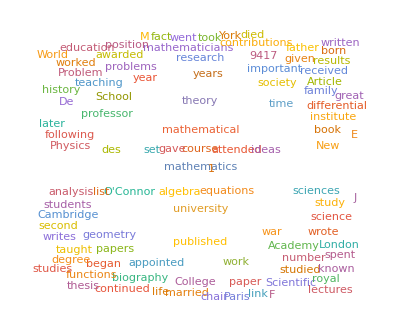

```mathematica
WordCloud[DeleteStopwords[StringJoin[formattedBios]]]
```

```mathematica
WordCloud[%133]
```

WordCloud::nomem: Not enough memory available to compute the word cloud.

WordCloud[WordCloud[{1}]]
 |  |  |  |

```mathematica
sentenceCounts=numberSentences /@ formattedBios
```

{7,22,14,82,57,23,130,58,54,52,34,86,44,36,45,28,73,36,19,47,84,57,96,24,15,29,25,35,150,43,23,29,31,42,126,61,106,45,24,22,35,79,67,34,35,12,18,107,29,26,40,45,45,23,47,54,50,89,49,48,29,71,122,19,16,23,97,81,34,15,92,19,24,42,40,61,20,49,26,60,56,23,34,17,91,44,31,38,10,38,68,67,27,44,22,20,138,33,64,9,14,53,52,6,38,8,23,8,31,84,33,46,61,30,34,32,67,29,46,23,1,32,69,20,49,108,64,79,117,48,23,142,45,93,46,32,41,87,20,114,77,14,27,49,33,28,23,108,25,71,57,59,17,85,42,101,22,59,102,83,99,32,69,52,71,17,43,90,12,39,55,85,43,130,67,68,84,28,35,14,27,46,51,43,76,78,51,39,105,76,53,124,69,43,99,41,17,95,37,31,51,42,52,55,37,139,153,42,21,28,107,83,74,129,45,99,31,82,118,74,74,77,98,111,63,63,39,89,113,119,60,99,74,43,73,61,107,111,82,142,38,58,64,78,92,91,48,65,96,58,33,75,80,68,68,145,91,94,123,43,112,64,165,66,91,130,55,120,127,101,121,30,37,107,55,81,24,94,17,37,35,105,46,131,127,61,38,27,115,78,33,78,143,83,27,47,105,50,123,95,70,31,61,96,21,68,134,72,59,71,48,144,95,114,66,43,87,56,73,47,62,103,100,20,98,77,87,71,32,22,76,94,47,84,32,84,79,101,111,41,80,40,27,43,40,90,38,45,124,39,74,112,110,96,34,123,82,67,131,44,135,60,103,78,35,69,22,152,27,40,182,68,53,106,29,45,113,23,75,57,54,84,115,84,69,93,83,46,27,1,54,27,75,57,107,83,107,67,75,62,68,122,47,100,54,53,78,60,48,27,51,80,124,65,47,50,52,66,35,31,89,57,81,98,33,70,37,74,47,54,91,18,118,12,38,139,107,37,99,40,37,11,95,105,55,31,95,73,25,32,143,15,80,195,61,87,14,25,51,47,134,45,84,65,37,18,1,40,81,30,29,36,49,63,61,34,112,73,91,147,103,60,52,45,40,111,35,64,36,126,113,55,95,28,84,86,47,58,79,89,124,19,64,83,34,150,77,41,30,22,38,15,41,110,43,64,131,35,36,79,122,37,122,71,144,41,73,48,34,114,81,75,29,85,42,48,73,111,47,34,37,43,48,15,46,58,57,72,58,43,56,44,44,100,128,54,69,43,42,104,31,19,28,64,27,56,65,120,44,25,62,23,33,102,75,72,72,27,85,106,83,68,58,109,78,32,24,25,50,75,99,23,39,64,62,42,44,103,73,104,53,103,83,34,54,77,33,42,109,119,28,73,41,89,98,46,91,35,119,45,116,79,94,67,45,88,120,112,85,43,139,77,68,39,110,102,85,60,113,43,68,32,91,26,97,101,80,53,9,60,26,83,79,68,73,74,87,101,40,20,28,25,98,26,57,60,96,25,91,71,82,94,82,105,89,24,131,59,107,43,134,99,72,38,109,74,48,57,42,125,72,104,121,100,127,18,120,36,109,51,77,117,24,124,97,80,31,80,44,114,90,47,70,83,30,101,70,115,89,61,129,84,46,30,98,25,29,26,78,188,70,96,92,85,34,63,105,45,79,82,26,101,59,31,44,66,36,42,78,47,129,106,86,100,63,25,34,39,61,80,62,73,101,29,54,40,83,129,42,47,143,133,102,37,109,87,30,70,136,86,90,47,93,33,131,54,23,104,26,85,61,34,40,25,55,64,118,26,35,119,62,42,27,64,61,38,136,48,40,56,34,25,33,18,37,106,72,25,63,52,42,91,100,52,123,96,66,89,105,46,125,169,111,21,118,118,31,98,68,100,60,89,76,54,53,120,34,33,45,46,76,49,41,83,41,139,26,14,86,82,69,29,94,40,33,46,74,68,23,62,28,52,65,51,56,87,92,44,33,10,42,27,59,87,68,40,26,40,27,64,30,98,48,28,63,51,93,108,44,76,94,28,81,87,111,75,52,1,130,23,49,125,60,47,30,40,59,115,57,61,15,55,63,17,61,59,50,49,50,81,71,52,72,66,42,78,68,137,133,28,54,52,22,21,26,24,45,85,104,92,42,66,54,88,74,20,39,31,55,42,100,84,120,20,44,43,54,24,69,119,99,26,51,42,41,44,94,37,100,50,32,119,104,55,37,24,22,88,104,64,55,61,54,64,18,43,64,113,27,46,35,130,90,42,66,51,34,62,37,114,16,58,72,47,36,44,44,101,71,46,92,127,100,50,30,42,57,117,62,106,116,25,24,88,49,69,141,18,143,75,60,31,72,46,63,98,29,66,120,50,58,42,38,60,25,36,24,27,61,27,14,62,92,101,60,17,34,64,80,47,150,17,78,63,105,83,25,64,28,59,27,39,30,83,98,107,118,105,45,48,76,47,33,105,29,98,24,23,51,57,95,35,35,69,113,54,63,10,96,21,102,87,1,137,60,48,57,105,70,24,45,98,111,35,96,13,39,37,63,26,36,15,106,62,102,14,26,81,38,47,1,67,159,37,22,97,33,85,37,53,28,49,100,127,27,26,50,19,73,73,73,30,87,15,127,50,92,46,20,56,47,62,87,46,136,12,118,103,64,14,58,52,83,13,44,87,62,35,66,121,62,24,82,38,86,87,125,20,16,39,29,104,36,42,27,100,104,104,37,22,44,31,87,83,92,75,20,108,79,46,70,35,35,80,83,68,23,108,32,30,45,40,69,104,44,36,70,51,69,63,27,50,19,56,82,98,79,102,145,28,42,17,69,89,13,18,50,166,121,100,76,22,34,85,99,64,43,25,39,10,68,36,34,47,35,50,6,16,6,54,92,66,112,75,39,24,109,14,16,109,49,90,48,66,28,31,14,61,20,25,50,69,58,66,22,102,63,58,35,33,86,38,68,53,21,94,37,30,81,49,71,48,72,78,79,23,45,1,86,61,43,50,67,38,76,71,56,36,40,53,63,77,26,52,106,52,148,86,83,80,17,65,76,54,76,114,28,35,114,32,30,26,70,96,44,50,82,18,69,20,27,43,55,40,125,96,37,68,64,102,24,70,45,47,146,9,82,127,110,60,59,92,78,44,124,54,31,88,102,100,52,52,32,26,19,39,33,149,23,32,92,29,37,51,140,99,29,56,51,122,42,49,41,89,42,106,30,68,37,46,63,27,69,17,55,93,48,49,133,112,71,57,107,97,48,92,105,34,21,76,157,99,50,87,143,49,107,37,25,62,115,56,85,94,7,29,97,30,107,116,61,76,72,76,47,111,36,96,46,123,90,63,113,69,20,78,86,42,132,23,102,7,45,52,80,120,96,77,40,80,51,36,106,19,78,94,59,47,112,56,77,89,108,31,43,109,18,100,52,77,43,50,40,24,77,59,57,45,62,87,39,42,51,126,36,47,40,55,160,61,129,119,71,32,85,57,40,44,145,141,55,25,72,20,65,102,106,101,117,20,96,67,31,63,21,64,96,101,74,73,71,86,66,109,39,85,45,96,107,128,140,24,45,43,27,23,97,104,131,58,59,110,46,37,102,104,89,45,83,83,51,65,83,18,93,88,9,135,129,25,43,18,39,55,95,86,139,56,31,113,76,25,30,126,77,56,60,97,49,39,52,42,108,72,93,94,24,62,51,33,60,97,39,88,33,94,64,64,23,73,121,49,105,36,16,43,55,19,128,51,70,92,56,103,85,33,84,92,114,74,11,56,93,72,126,46,59,50,82,18,52,29,34,80,95,20,63,117,70,89,65,103,96,141,59,55,86,24,126,16,78,97,41,62,59,67,48,78,58,120,25,35,79,7,90,47,42,14,29,126,49,56,14,107,90,56,79,57,31,24,126,91,71,66,136,50,89,56,59,149,107,38,81,73,36,22,69,22,50,109,81,79,76,56,93,93,40,35,96,77,73,55,49,31,74,75,133,40,53,76,104,54,108,84,110,35,42,103,99,157,108,97,68,110,85,43,46,111,71,65,116,104,58,20,69,53,110,111,44,14,116,96,95,38,26,123,17,118,156,22,138,31,101,98,30,71,137,57,50,110,29,127,20,67,60,77,44,155,69,143,50,57,53,53,63,96,101,108,56,43,110,34,110,78,120,86,79,71,28,96,127,73,101,37,45,113,36,78,78,16,54,18,68,73,137,130,125,90,25,83,19,127,135,144,65,76,25,71,111,25,66,106,54,88,94,74,52,52,118,61,112,108,48,69,45,120,57,81,51,14,42,110,143,60,120,49,62,56,60,71,143,62,19,132,35,52,65,21,107,40,86,101,63,65,38,88,43,64,72,124,92,39,75,18,57,37,125,89,120,40,70,72,84,52,58,77,76,45,88,74,58,148,36,115,47,99,91,72,56,74,34,72,52,89,56,64,78,84,87,44,41,56,115,71,52,2,99,45,70,157,105,108,100,27,83,162,98,36,44,79,68,97,88,55,61,51,133,125,49,56,39,74,36,106,76,135,108,54,64,78,60,111,76,59,99,39,124,15,77,100,40,85,64,27,141,74,100,52,63,88,66,66,48,51,58,67,42,64,47,120,58,54,52,100,66,23,113,96,69,79,41,84,135,56,74,85,69,26,121,125,115,92,127,34,49,88,103,89,62,46,63,78,92,45,121,88,51,95,91,54,46,55,144,67,49,48,139,110,60,108,36,48,47,33,44,59,145,65,108,112,42,100,57,107,91,88,74,108,36,98,92,87,111,152,53,104,126,88,49,60,36,118,23,37,17,56,127,98,44,86,59,134,52,70,66,59,108,128,81,128,23,103,119,154,96,103,94,89,63,97,126,91,98,115,98,29,91,75,97,31,78,109,81,57,88,55,105,98,97,74,125,127,93,128,92,102,84,63,101,85,11,32,119,43,44,60,64,130,116,52,111,124,125,66,68,52,159,131,109,97,133,139,91,43,55,67,85,58,130,70,143,66,97,12,78,39,51,81,107,158,71,51,64,48,118,89,117,52,58,85,108,42,54,54,103,110,54,59,127,53,79,28,35,73,61,55,83,13,45,100,96,154,75,62,48,91,128,31,70,44,93,111,25,53,62,116,121,85,70,72,102,106,130,98,54,36,56,103,72,47,130,69,59,93,70,92,128,74,76,107,85,49,100,94,43,72,48,93,68,56,44,86,122,81,91,76,89,1,66,77,97,108,21,53,100,90,75,88,60,96,18,59,48,33,65,53,62,86,50,74,99,36,110,31,105,47,83,45,65,94,132,49,32,135,129,62,32,108,63,59,94,60,169,89,61,88,78,65,97,81,122,96,118,42,61,127,69,66,116,102,19,61,24,71,64,84,145,97,97,27,94,101,62,36,156,55,120,112,52,53,83,104,142,100,45,131,61,79,144,53,88,37,95,144,86,74,68,103,45,99,59,45,84,107,34,33,56,106,117,40,104,34,84,90,30,80,85,97,91,113,86,118,59,71,42,57,53,123,42,72,94,66,28,64,121,26,86,72,111,158,74,72,35,48,63,53,57,127,37,118,61,71,48,85,65,56,104,45,71,77,120,76,84,148,81,113,77,57,96,85,87,74,132,49,101,81,113,83,103,29,170,67,57,91,113,111,96,183,56,111,88,140,79,89,149,140,59,27,111,118,102,93,50,137,39,44,69,75,56,81,141,66,42,69,103,89,106,60,88,79,64,90,107,64,85,111,70,61,37,60,60,48,104,52,85,147,132,58,72,111,102,124,114,65,101,34,36,118,125,111,146,120,112,24,117,73,94,23,66,68,52,71,80,56,78,103,86,38,69,54,53,105,91,100,101,119,79,92,56,78,56,117,2,82,112,99,82,119,40,53,36,92,106,71,45,51,110,97,52,113,71,79,45,73,68,80,51,35,44,100,75,67,88,63,71,78,62,94,51,82,76,45,45,69,128,81,104,60,64,52,85,109,58,74,82,65,149,94,89,112,63,125,80,43,108,123,64,50,53,140,132,53,147,117,62,47,113,22,105,45,71,104,73,37,46,63,93,131,59,95,46,68,114,81,61,87,42,98,56,51,81,154,64,126,100,70,19,102,38,64,57,116,73,101,54,59,53,89,45,115,25,107,119,106,47,71,67,106,114,81,119,159,67,155,63,61,99,85,34,76,85,69,37,73,53,35,41,61,62,101,64,40,66,65,34,57,70,56,42,71,47,29,87,80,79,70,58,77,72,120,94,68,71,53,107,98,85,126,96,117,68,95,57,99,117}

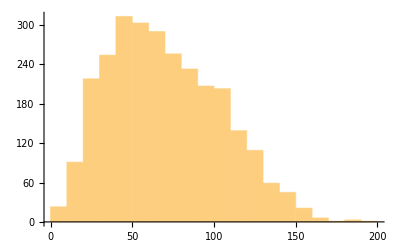

```mathematica
Histogram[Sort[sentenceCounts]]
```

```mathematica
wordsCounts=numberWords/@ formattedBios
```

{167,477,326,2266,1144,412,3284,1287,1316,1166,933,2321,1119,783,1351,735,1730,938,549,1536,2093,1463,2454,443,190,673,564,874,3582,1240,629,729,900,1161,3082,1763,3319,943,696,601,760,2059,1940,848,1193,291,527,2819,762,516,1117,1101,990,449,1071,1512,1260,2429,1298,1175,709,1547,3646,422,312,565,2429,1980,813,391,2457,492,634,1247,903,1462,461,1417,722,1466,1030,520,672,459,2178,1080,848,1033,227,885,1557,1594,861,938,550,616,3170,688,1301,194,298,1113,1291,80,814,175,566,271,706,1860,834,1154,1413,793,759,763,1354,835,1160,557,1,753,1323,446,878,2617,1481,1973,2733,1268,486,3265,993,2227,1052,742,899,2174,579,2503,2265,245,698,1036,710,595,573,2578,692,1719,1310,1635,344,2235,1185,2061,340,1509,2110,2111,2432,680,1706,1083,1681,386,1048,2161,211,999,1303,1923,931,3110,1508,1321,1997,802,910,297,558,1038,1117,886,1810,1991,1292,1033,2609,1859,1317,3215,1457,1205,2334,931,320,2111,720,678,1438,950,1320,1348,730,2778,3630,934,499,626,2698,2020,1698,3271,1046,2109,674,2122,2919,1795,1831,1858,2416,2544,1678,1306,1065,2194,2472,3050,1327,2752,1907,1020,1839,1784,2509,2511,1812,3227,1054,1773,1832,1899,1818,2134,1206,1720,2621,1543,664,1925,2134,1455,2049,3422,2349,1851,2838,947,2420,1548,4267,1699,2095,3712,1540,2946,3272,2577,3108,560,830,2384,1233,1884,441,2252,354,810,766,2603,1209,3145,3086,1342,840,691,2485,1790,821,2025,3391,1931,517,1183,2685,1187,2944,2304,2565,794,1598,2516,485,1318,3208,2164,1385,1666,1099,3440,2779,2932,1639,1081,1872,1208,1525,969,1634,2536,2333,430,2483,2028,2046,1680,627,533,1953,2146,1083,1913,739,2141,2100,2506,2811,1005,1818,1007,971,1012,893,2168,863,992,2757,845,1551,2392,2434,2730,753,3110,1910,1611,3395,1469,3252,1407,2402,1942,800,1735,483,3746,583,794,3815,1544,1285,2698,616,1172,2479,571,1951,1581,1234,1904,2735,2253,2252,2396,1966,1110,736,1,1418,854,2072,1314,2520,1966,2565,1395,1949,1418,1648,2701,1046,2361,1366,1180,2261,1475,1260,731,1816,2232,2481,1820,1224,1247,1341,1753,697,756,1951,1131,2139,2045,572,1940,808,1984,1126,1312,1855,461,3068,206,726,3419,2578,837,2369,980,1335,252,2629,2660,1654,674,2393,1843,680,731,3203,324,1820,4674,1604,2485,248,658,1160,1086,2861,952,2139,1641,821,309,1,1017,2160,782,630,679,1121,1746,1496,890,2547,1729,2146,3040,2450,1133,1183,997,933,2616,959,1247,825,2945,2746,1135,2199,663,2439,2302,914,1428,1976,2119,3163,387,1415,2079,840,2886,1888,888,567,614,773,290,1007,2490,1154,1776,3089,747,739,1879,3088,930,2908,2264,3873,990,1878,1120,838,3219,1994,2037,586,1897,1160,1315,1786,2530,1063,920,920,1248,1065,300,1277,1501,1256,1593,1527,1076,1494,1298,998,2303,3144,1262,1773,1007,997,2147,694,360,614,1593,601,1419,1473,3446,990,500,1197,519,724,3104,1697,1966,1870,688,1851,2578,2331,1727,1412,2404,1686,724,521,648,1053,1933,2295,532,922,1819,1263,1044,1152,2369,2270,2564,1051,2609,2568,727,1491,1715,712,1110,2441,2776,634,1943,977,2971,2146,1050,2093,868,2920,1059,2490,2007,2330,1362,959,2294,3075,2210,2154,1236,3395,2123,1590,872,2900,2400,2202,1273,2802,920,1564,673,2150,613,2239,2346,2115,1233,235,1573,570,1809,2401,1847,1883,1660,1949,2277,1031,402,592,689,2520,641,1100,1525,2435,548,2105,1834,2021,2594,2135,2477,1894,543,2864,1355,2351,1088,3050,2455,1813,780,2625,2103,1086,1339,851,2802,1912,2603,2795,2215,2932,386,3157,858,3011,1103,2077,2775,550,3045,2046,2185,662,1769,995,2772,1964,1040,1523,2347,622,2486,1430,2073,2099,1364,3222,1851,997,723,2522,561,755,650,2033,4269,1772,2380,2246,1915,792,1710,2473,1113,1932,2360,590,2707,1270,598,873,1432,791,1079,1961,930,2875,2258,2052,2360,1516,391,808,708,1378,1819,1489,2006,2748,837,1322,1140,1859,2794,1071,1136,3270,3304,2787,713,2298,2529,595,1439,2754,2102,1876,1256,2606,671,3116,1270,481,2610,462,2176,1448,887,986,716,1429,1539,2887,597,963,2746,1458,1049,588,1592,1414,840,2847,1259,1012,1290,724,451,568,327,961,2314,1756,478,1410,1263,835,1828,1888,1883,3088,2191,1735,2114,2682,1101,2900,3681,2339,524,2935,2655,656,2238,1710,2468,1493,2292,2008,1313,1320,2814,771,613,1082,1262,1581,1098,1008,1972,994,3430,648,314,2147,1804,1445,772,2114,814,697,1019,1783,1556,642,1621,766,1502,1584,1266,1057,2132,2306,1007,669,270,1161,629,1545,2115,1697,948,525,929,661,1544,734,2211,1108,665,1876,1301,1895,2778,855,1722,2477,707,2149,2258,2582,1775,917,1,2861,372,1347,3194,1177,1053,695,875,1497,2575,1489,1484,264,1114,1321,295,1483,1327,1035,1133,925,1899,2099,1186,1426,1710,1075,1754,1258,3206,3040,707,1089,1125,487,355,765,620,947,2096,2385,1919,1380,1529,1298,2250,1905,501,861,752,1078,1016,2394,1894,2784,469,922,737,1120,567,1665,2925,2153,568,1221,1113,776,865,2118,875,2278,1377,811,2528,2369,1215,1035,542,607,2439,2403,1610,1108,1285,1288,1171,269,1003,1781,2915,542,1038,719,3218,1968,1019,1725,1101,652,1388,813,2590,336,1629,1902,953,871,1181,990,2319,1812,911,2011,2713,2693,1221,654,916,1406,3063,1411,2435,2926,443,405,1797,1080,1623,3019,297,3295,2040,1109,656,1464,982,1594,2365,611,1946,2760,1092,1326,958,854,1441,478,875,435,538,1533,625,392,1333,2178,2135,1558,325,776,1598,1824,1135,3146,376,1785,1378,2807,1588,558,1239,739,1243,573,927,766,2056,2422,2769,2887,2418,1002,1120,2078,993,595,2749,691,2191,573,674,997,1456,2781,901,750,1660,2764,1197,1322,168,2407,384,3070,2281,1,3066,1367,1444,1266,2557,1487,389,1112,2113,2658,802,2054,209,854,750,1397,585,819,298,2356,1578,2385,449,465,1995,905,953,1,1840,3494,848,560,2612,947,2385,695,1325,585,1011,2458,2694,423,505,1295,514,1592,1807,1724,759,2381,431,3215,1224,2452,1023,452,1417,1124,1393,1695,1028,3389,296,2735,2732,1490,267,1212,1210,1615,219,887,1840,1605,821,1281,3174,1654,505,1908,744,2381,2197,2785,436,288,1066,720,2582,1042,739,549,2339,2184,2295,836,576,1243,744,2444,2352,2130,1808,567,2656,1898,1171,1562,894,701,1738,1732,1447,437,2476,784,644,974,784,1808,2248,1329,551,2002,968,1483,1319,587,1160,328,1269,2062,2204,1959,2361,3289,664,1012,323,2020,2333,218,406,1137,3739,2672,2638,1795,366,874,2149,2431,1640,1469,642,713,163,1481,783,897,1163,626,1104,95,287,94,916,2223,1612,2507,1888,761,532,2944,298,311,2454,1144,2587,1410,1659,688,738,305,1554,458,514,973,2045,1355,1520,397,2565,1524,1474,714,712,1925,944,1679,1440,363,2341,887,666,2004,1250,1728,1165,1528,1597,1918,619,1173,1,2113,1647,802,1140,1525,955,1940,1498,1270,835,1048,1292,1250,2124,552,1222,2631,1323,3145,1839,1762,2311,410,1507,1677,1228,1679,2830,723,910,2634,870,664,689,1421,2655,715,1440,1869,419,1803,389,617,1319,1214,1017,2695,2411,669,1632,1445,2620,508,1820,1026,1178,3124,199,1829,3083,2638,1654,1336,2538,2151,1021,2655,1377,643,1724,2362,2123,1062,1206,762,630,339,755,607,3477,580,741,2548,661,770,1496,2787,2229,654,1398,1054,2709,891,1075,874,2109,1134,2585,676,1325,785,1135,1702,716,1657,237,1073,2290,929,1123,2739,2631,1701,1520,2221,2291,1239,2264,1854,775,462,1859,3214,2066,1117,1976,2935,899,2436,921,546,1434,2437,1396,2221,2523,156,630,2296,606,2577,2652,1832,1647,1764,2070,1078,2755,697,2530,961,2758,2173,1591,2690,1435,379,1936,1999,807,2671,503,2415,229,837,1186,2064,3055,2161,1891,793,1897,1337,766,2478,327,1985,2753,1153,1363,2590,1273,1835,1857,2413,722,948,2733,383,2345,1178,2008,759,1287,788,423,2243,1369,1369,1051,1227,2291,782,849,1210,2526,830,1082,898,1256,3571,1422,2948,2717,1712,651,1830,1451,882,1135,3196,3193,1214,467,1414,472,1797,2088,2547,2239,2582,417,2292,1753,646,1415,482,1394,2500,2523,1768,1868,1480,1977,1389,2640,872,2450,918,2308,2584,3319,3069,602,988,1073,475,660,2419,2339,2877,1454,1427,2204,1279,909,2505,2583,2138,923,1968,1977,1517,1526,2242,286,1707,2029,173,2871,3137,568,1072,396,811,1286,2373,1888,3072,1330,658,2429,1745,516,738,2592,2052,1626,1498,2363,1236,727,1333,1044,2582,2005,2083,2171,487,1430,1181,741,1557,2217,922,1864,732,2500,1395,1577,427,1634,2794,1140,2470,850,290,924,1482,432,2816,944,1388,1907,1086,2366,1851,850,2147,2284,2525,1484,234,1134,1888,1658,2542,1042,1307,1236,2255,366,1182,608,775,2298,2143,349,1604,2585,1825,1950,1618,2447,2109,3105,1183,1379,2508,448,2994,327,1824,2306,746,1342,1222,1472,1102,1780,1365,2355,789,844,1815,144,2212,1220,1079,292,726,2889,1004,1192,236,2446,2008,1229,2201,1263,614,431,2731,1965,1475,1696,3558,1263,1988,1434,1241,2742,2132,908,1741,1615,931,413,1548,413,1122,2528,1904,1971,1421,1099,2252,2101,984,851,2142,1646,1654,1161,1094,585,1778,1721,2878,738,1526,1805,2348,1173,2567,2100,2921,806,806,2508,2502,3107,2499,2160,1433,2476,1898,1021,835,2408,1813,1895,2554,2456,1382,552,1537,1710,2301,2422,1130,319,2691,2202,2295,790,505,2776,368,2639,3362,361,3393,586,2255,2330,697,1399,3082,1393,1148,2739,671,2573,353,1578,1127,1823,1107,3605,1902,3077,1105,1209,1105,1287,1597,2620,2302,2686,1268,978,2762,672,2633,1627,3112,2285,2143,1848,485,2551,2989,1798,2454,994,921,2489,746,1789,2025,432,1277,292,1502,1820,3080,2752,2694,2108,575,1675,410,3065,2792,2817,1531,1969,594,1655,2219,723,1443,2534,1257,2366,1878,1559,1257,854,2764,1198,2541,2400,1116,1751,1135,2524,1234,2074,946,268,1081,2460,3381,1634,2635,1078,2131,1208,1394,1742,2707,1280,371,2961,744,1160,1409,427,2195,780,1809,2657,1688,1757,858,1937,1039,1341,1871,2371,2007,1018,1850,339,1391,864,2756,2029,2583,1066,1618,1426,2034,1251,1594,1986,1495,1693,1992,1802,1302,3562,876,2768,1305,2297,1837,1854,1183,1738,833,1713,1073,2665,1312,1232,1794,1846,1737,1153,868,1335,2656,1652,1270,40,2270,1203,1712,3315,2410,2722,2296,618,1614,3320,2397,886,768,1730,1494,2457,1784,1347,1421,962,2373,2656,1078,1377,731,1982,1046,2496,1758,2905,2627,1282,1504,1906,1705,2438,1891,976,2300,826,2925,407,1781,2252,932,2445,1353,513,3561,1856,2925,1212,1725,2013,1690,1787,1083,1163,1523,1605,961,1523,1094,2877,1325,1261,1173,2571,1452,471,2615,1963,1591,1556,993,1950,2953,1597,1530,2381,1734,524,2442,2603,2573,1645,2691,823,1246,1537,2610,1946,1492,1004,1450,1828,2532,979,2828,2326,1317,3465,2281,1122,1103,1358,2851,1481,1205,1245,3004,2659,1176,2418,714,1110,1145,822,1101,1309,3216,1365,2722,2523,997,2577,1133,2717,2089,2115,1841,2691,722,2472,2127,2042,2391,2667,1347,2239,3013,2010,1294,1285,801,2219,481,957,592,1304,3658,2467,940,2332,1336,3169,1130,1721,1528,1220,2842,3061,1877,2635,461,3316,2666,3484,1915,2219,2438,1905,1488,2282,2855,2071,2761,2725,2406,562,1780,1454,2524,953,1799,2301,1711,1120,2122,1459,2783,2493,2325,1724,2717,2561,2214,2857,1956,2264,1776,1357,2414,1876,241,675,2574,944,1020,1265,1666,2590,2375,1129,2666,2792,3157,1723,1653,1171,3413,2999,2607,2294,2889,3093,2238,1191,1176,1656,2455,1358,3088,1861,3003,1268,2528,296,1667,949,1149,2022,2417,3125,1531,1163,1673,1244,2627,2201,2712,1089,1310,2052,2894,997,1331,1386,2613,2756,1382,1383,2349,1135,1550,701,724,1822,1520,1221,2315,331,944,2426,2798,3142,1925,1488,1155,2102,2696,789,1720,1352,2297,2527,574,1320,1266,2535,2968,1767,1701,1563,2379,2148,2910,2242,1374,682,1374,2561,1773,1031,3253,1446,1502,2309,2004,2475,2732,1492,1708,2244,2081,1183,2670,2165,1113,1495,1137,2032,1682,1470,975,1813,2485,1960,1914,1980,2109,1,1663,1615,2334,2586,463,1485,2745,1956,1610,2380,1561,2071,321,1276,1325,777,1671,1297,1352,1771,1435,2122,2256,958,2657,691,2182,1241,2535,977,1226,2394,2806,1285,641,2637,3025,1472,648,2469,1379,1247,2362,1481,3951,2228,1578,1893,1931,1432,2137,1728,2629,2170,2343,975,1500,2869,1700,1826,2748,2506,576,1372,513,1889,1492,1862,3351,2393,2095,595,2395,2465,1429,802,3059,1362,2806,2715,1233,1395,2110,2580,2607,2404,1060,2716,1562,1988,2849,1215,1656,800,1975,3097,2154,1937,1382,2281,937,2051,1524,1048,1961,2266,778,960,1178,2667,2445,888,2446,764,1977,2379,725,1896,1919,2392,2108,2757,2173,2574,1254,1652,984,1306,1408,2969,989,1819,2246,1576,689,1134,2797,648,1900,1676,2901,3330,2076,2014,831,1270,1443,1271,1457,2542,723,2549,1623,1924,1353,1904,1403,1014,2413,1056,1529,1664,2529,1585,1860,2767,1692,1283,1733,1217,2651,2081,1691,1721,3243,1110,2459,2022,2485,1666,2301,715,3727,1463,1141,1818,2287,2309,2132,4028,1272,2207,1745,2665,2193,2154,2964,3238,1556,677,2571,2446,2432,2061,1313,3009,1043,1254,1837,1566,1204,1999,2870,1541,1064,1965,1986,2067,2498,1300,2162,1897,1526,2248,2377,1647,1981,2510,1839,1210,856,1281,1358,1064,2623,1116,1610,3398,2647,1096,1584,2353,2360,2597,2860,1632,2208,1024,837,2713,2670,2271,3382,2630,2256,573,2781,1559,2090,565,1521,1579,1172,1558,2069,1419,1924,2828,1847,907,1492,1317,1240,2488,2031,2060,2310,2768,2166,2366,1288,2137,1236,2762,44,1903,2578,2327,2172,2651,711,1296,601,2195,2244,1401,1292,1371,2506,2235,1250,2576,1795,1811,932,1564,1732,1785,1130,771,928,2287,1530,1434,2136,1397,1667,1693,1411,2220,1224,1754,1801,998,1188,1837,3014,1646,3465,1559,1764,1267,2163,2843,1660,1762,1631,1780,3193,1932,2357,2562,1398,2583,1783,1403,2644,2743,1569,1119,1204,2937,3248,1283,2951,2708,1286,1162,2851,398,2541,1062,1560,1925,1840,942,1191,1559,1978,2759,1219,2086,1040,1634,2624,2162,1552,2047,1153,2249,1199,1024,1869,3624,1522,2723,2259,1695,483,2604,969,1653,1334,2442,1616,2460,1553,1254,1405,1732,1124,2523,627,2579,2533,2246,1007,1580,1728,2841,2798,1853,2412,3208,1333,2913,1479,1323,2303,2287,796,1929,2120,1546,888,1384,1372,759,1062,1126,1515,2247,1500,1188,1828,1563,690,1685,1569,1373,953,1595,1121,765,2279,1841,1779,1439,1341,1782,1780,2422,2470,1830,1708,1257,2304,2185,2157,2868,2113,2977,1759,2285,1153,2534,2551}

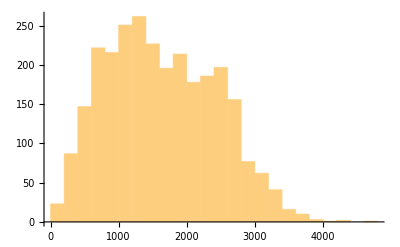

```mathematica
Histogram[Sort[wordsCounts]]
```

## Wikipedia Data

```mathematica
ClearAll[b]
```

```mathematica
enWikiGet[mgpid_String]:=With[{res=Import["https://query.wikidata.org/sparql?query="<>URLEncode["SELECT ?wikipedia_article
        WHERE
        {
          ?person wdt:P1563 \""<>mgpid<>"\" . 
          ?wikipedia_article schema:about ?person .
          ?wikipedia_article schema:isPartOf <https://en.wikipedia.org/> .
        }"]<>"&format=json","RawJSON"]},Replace[res["results","bindings"][[All,"wikipedia_article","value"]],{s_String}:>URLDecode@StringReplace[s,"https://en.wikipedia.org/wiki/"->""]]]
```

```mathematica
wikiNames=Map[enWikiGet,allNames];
```

```mathematica
wikiNames = Import["C:\\Users\\tanha\\Desktop\\Wolfram\\wikiNames.mx"];
```

```mathematica
wikiNames[[1;;15]]
```

{Ahmes,Baudhayana_sutras,Manava,Thales_of_Miletus,Anaximander,{},Pythagoras,Pāṇini,Anaxagoras,Empedocles,Oenopides,Zeno_of_Elea,Antiphon_(orator),Leucippus,Hippocrates_of_Chios}

```mathematica
allWikiHtmls =Import["C:\\Users\\tanha\\Desktop\\Wolfram\\allWikiHtmls.mx"];
```

```mathematica
wikiHtmlsasoc=AssociationThread[wikiNames,allWikiHtmls];
```

```mathematica
allWikiHtmlsFiltered = Select[wikiHtmlsasoc,StringQ];
```

```mathematica
allWikiHtmlsFiltered[[6]]
```

```mathematica
wikiBioReferences[names_String]:= StringCases[allWikiHtmlsFiltered,"/wiki/"~~Shortest[n__]~~"\""->n];
```

```mathematica
wikiNameAsoc =AssociationThread[Keys[allWikiHtmlsFiltered],Map[Intersection[#,wikiNames]&,StringCases[Values[allWikiHtmlsFiltered],"/wiki/"~~Shortest[n__]~~"\""->n]]];
```

```mathematica
vertexList2 =Flatten@ MapThread[ Thread[Rule[#1 , #2]]&,{Keys[wikiNameAsoc],Values[wikiNameAsoc]}];
```

```mathematica
vertexList//Length
```

30541

```mathematica
w =Graph[vertexList2,VertexLabels->Placed["Name",Tooltip]]
```

-Graphics-

```mathematica
ConnectedGraphComponents[w[[1]]]
```

Part::partd: Part specification … is longer than depth of object.

ConnectedGraphComponents::graph: A graph object is expected at position 1 in ….

ConnectedGraphComponents[(-Graphics-)⟦1⟧]

```mathematica
Counts[Map[Head,allWikiHtmls]]
```

<|String→2456,getWikiHtml→318,Symbol→1|>

Make Wikipedia Queries, accept results that are unique and pass through interpreter if multiple entries

```mathematica
findWikiBioIDs[name_]:=With[{wikiSearch = WikipediaSearch[name]},
If[Length[wikiSearch]<2,wikiSearch,Interpreter["Person"][name]]]
```

Filter out Wikipedia Queries that returned a biography page

```mathematica
wikiBioChecker[wikiResults_]:=With[{trueEntries=Select[findWikiBioIDs[wikiResults],Not@*FailureQ]},{trueEntries}]
```

```mathematica
Map[wikiBioChecker,fullNames] (*what are all these errors? what to do about empty lists?*)
```

URLFetch::invhttp: Could not resolve host: en.wikipedia.org.

Select::normal: Nonatomic expression expected at position 1 in Select[Null,Not@*FailureQ].

URLFetch::invhttp: Could not resolve host: en.wikipedia.org.

Select::normal: Nonatomic expression expected at position 1 in Select[Null,Not@*FailureQ].

URLFetch::invhttp: Could not resolve host: en.wikipedia.org.

General::stop: Further output of URLFetch::invhttp will be suppressed during this calculation.

Select::normal: Nonatomic expression expected at position 1 in Select[Null,Not@*FailureQ].

General::stop: Further output of Select::normal will be suppressed during this calculation.

{{{Ahmes}},{{}},{{}},{{Thales of Miletus}},{{Anaximander of Miletus}},{{}},{{Pythagoras of Samos}},{{Pāṇini}},{{Anaxagoras of Clazomenae}},{{Empedocles of Acragas}},{{Oenopides of Chios}},{{Zeno of Elea}},{{Antiphon the Sophist}},{{Leucippus of Miletus}},{{Hippocrates of Chios}},{{Theodorus of Cyrene}},{{Democritus of Abdera}},{{Hippias of Elis}},{{Bryson of Heraclea}},{{Archytas of Tarentum}},{{Plato}},{{Theaetetus of Athens}},{{Eudoxus of Cnidus}},{{}},{{Thymaridas of Paros}},{{Xenocrates of Chalcedon}},{{Dinostratus}},{{Heraclides of Pontus}},{{Aristotle}},{{Menaechmus}},{{Aristaeus the Elder}},{{Callippus of Cyzicus}},{{Autolycus of Pitane}},{{Eudemus of Rhodes}},{{Euclid of Alexandria}},{{Aristarchus of Samos}},{{Archimedes of Syracuse}},{{Chrysippus of Soli}},{{Conon of Samos}},{{Nicomedes}},{{Philo of Byzantium}},{{Eratosthenes of Cyrene}},{{Apollonius of Perga}},{{}},{{Diocles of Carystus}},{{}},{{}},{{Hipparchus of Rhodes}},{{Hypsicles of Alexandria}},{{}},{{Theodosius of Bithynia}},{{Zeno of Sidon}},{{Posidonius of Rhodes}},{{}},{{Marcus Vitruvius Pollio}},{{Geminus}},{{}},{{Hero of Alexandria}},{{Nicomachus of Gerasa}},{{Menelaus of Alexandria}},{{Theon of Smyrna}},{{Zhang Heng}},{{Claudius Ptolemy}},{{Yavaneśvara}},{{Liu Hong}},{{}},{{Diophantus of Alexandria}},{{Liu Hui}},{{}},{{Sporus of Nicaea}},{{Pappus of Alexandria}},{{}},{{Serenus of Antinouplis}},{{Theon of Alexandria}},{{Hypatia of alexandria}},{{Sun Tzu}},{{}},{{Proclus Diadochus}},{{Domninus of Larissa}},{{Zu Chongzhi}},{{Zhang Qiujian Suanjing}},{{Marinus of Neapolis}},{{Zu Gengzhi}},{{Anthemius of Tralles}},{{}},{{Anicius manlius severinus boethius}},{{Eutocius of Ascalon}},{{Simplicius Of Cilicia}},{{Yativrsabha}},{{Varāhamihira}},{{}},{{Brahmagupta}},{{}},{{Li Chunfeng}},{{}},{{Alcuin of York}},{{Abū Jaʿfar Muḥammad ibn Mūsā al-Khwārizmī}},{{Al-Abbas ibn Said Al-Jawhari}},{{Banu Musa brothers}},{{Jafar Muhammad Banu Musa}},{{Govindasvāmi}},{{Mahavira}},{{Abu Yusuf Yaqub ibn Ishaq al-Sabbah Al-Kindi}},{{Ahmad Banu Musa}},{{Abu Zayd Hunayn ibn Ishaq al-Ibadi}},{{Al-Hasan Banu Musa}},{{Abu Abd Allah Muhammad ibn Isa Al-Mahani}},{{Prthudakasvami}},{{Ahmad ibn Yusuf al-Misri}},{{}},{{}},{{Abu Kamil Shuja ibn Aslam ibn Muhammad ibn Shuja}},{{Abu Abdallah Mohammad ibn Jabir Al-Battani}},{{C. V. Sridhar}},{{Abu'l Abbas al-Fadl ibn Hatim Al-Nayrizi}},{{}},{{Abu Jafar Muhammad ibn al-Hasan Al-Khazin}},{{Ibrahim ibn Sinan ibn Thabit ibn Qurra}},{{Abu'l Hasan Ahmad ibn Ibrahim Al-Uqlidisi}},{{}},{{}},{{Abu Mahmud Hamid ibn al-Khidr Al-Khujandi}},{{Abu Sahl Waijan ibn Rustam al-Quhi}},{{}},{{Abu Said Ahmad ibn Muhammad Al-Sijzi}},{{Gerbert of Aurillac}},{{}},{{Abu Bekr ibn Muhammad ibn al-Husayn Al-Karaji}},{{Abu Ali al-Hasan ibn al-Haytham}},{{Abu Nasr Mansur ibn Ali ibn Iraq}},{{Kushyar ibn Labban}},{{Abu Arrayhan Muhammad ibn Ahmad al-Biruni}},{{Abu Mansur ibn Tahir Al-Baghdadi}},{{}},{{Abu Abd Allah Muhammad ibn Muadh Al-Jayyani}},{{Abu l'Hasan Ali ibn Ahmad Al-Nasawi}},{{}},{{Hermann of Reichenau}},{{}},{{}},{{Omar Khayyam}},{{}},{{Abraham bar Hiyya Ha-Nasi}},{{Adelard of Bath}},{{Acharya Hemchandra}},{{Abraham Ben Meir ibn Ezra}},{{Al-Ishbili Abu Muhammad Jabir ibn Aflah}},{{Bhāskara II}},{{Gherard of Cremona}},{{Ibn Yahya al-Maghribi Al-Samawal}},{{Sharaf al-Din al-Muzaffar al-Tusi}},{{}},{{Robert Grosseteste}},{{Leonardo Pisano Fibonacci's Number Sequence}},{{}},{{Li Zhi}},{{Johannes de Sacrobosco}},{{Saint Albertus Magnus}},2459,{{Argelia Velez-Rodriguez}},{{Charles Terence Clegg Wall}},{{Vladimir Igorevich Arnold}},{{Johannes Boersma}},{{}},{{John Horton Conway}},{{}},{{}},{{}},{{Barry Edward Johnson}},{{}},{{Yuri Ivanovich Manin}},{{Barry Charles Mazur}},{{Vladimir Gilelevich Maz'ya}},{{}},{{David Bryant Mumford}},{{Leonid Andreevich Pastur}},{{Charles Coffin Sims}},{{George Andrews}},{{Fischer Black}},{{}},{{}},{{Detlef Gromoll}},{{Robion Cromwell Kirby}},{{Donald Ervin Knuth}},{{Sergei Petrovich Novikov}},{{Chidambaram Padmanabhan Ramanujam}},{{Marina Ratner}},{{}},{{}},{{}},{{Alan Baker}},{{Carlo Cercignani}},{{}},{{Brian Hartley}},{{John Frank Charles Kingman}},{{}},{{}},{{}},{{Richard Alfred Tapia}},{{Enrico Bombieri}},{{}},{{Daniel Gray Quillen}},{{}},{{}},{{Endre Szemerédi}},{{}},{{Richard Alan Kayne}},{{László Filep}},{{}},{{Peter Stefan}},{{}},{{}},{{}},{{Thierry Émilien Flavien Aubin}},{{Lenore Blum}},{{Gavin Brown}},{{David George Crighton}},{{}},{{Stephen William Hawking}},{{}},{{Alexandru Ioan Lupaș}},{{}},{{Neil Sidney Trudinger}},{{Karen Keskulla Uhlenbeck}},{{Béla Bollobás}},{{Mikhail Leonidovich Gromov}},{{}},{{Steven Alan Orszag}},{{Pierre René Deligne}},{{Mitchell Jay Feigenbaum}},{{}},{{}},{{}},{{Leonard Adleman}},{{John Henry Coates}},{{Persi Warren Diaconis}},{{}},{{}},{{Vijay Kumar Patodi}},{{Saharon Shelah}},{{}},{{Paul Charles William Davies}},{{}},{{Nigel John Kalton}},{{Jean-Louis Loday}},{{George Lusztig}},{{Gregori Aleksandrovich Margulis}},{{William Paul Thurston}},{{}},{{}},{{Alain Connes}},{{David Eisenbud}},{{András P Huhn}},{{}},{{}},{{John F. Carr}},{{Sun-Yung Alice Chang}},{{Philippe Flajolet}},{{}},{{László Lovász}},{{}},{{Cheryl Elisabeth Praeger}},{{}},{{Charles Louis Fefferman}},{{}},{{}},{{Leslie Gabriel Valiant}},{{Shing-Tung Yau}},{{Andrei Andreevich Bolibrukh}},{{David Broomhead}},{{}},{{}},{{Richard Melvin Schoen}},{{Michael Hartley Freedman}},{{Shigefumi Mori}},{{}},{{Edward Witten}},{{}},{{Vaughan Frederick Randal Jones}},{{Robert Wayne Thomason}},{Select[Null,Not@*FailureQ]},{Select[Null,Not@*FailureQ]},{Select[Null,Not@*FailureQ]},{Select[Null,Not@*FailureQ]},{Select[Null,Not@*FailureQ]},{Select[Null,Not@*FailureQ]},{Select[Null,Not@*FailureQ]},{Select[Null,Not@*FailureQ]},{Select[Null,Not@*FailureQ]},{{Efim Isaakovich Zelmanov}},{{Andreas Floer}},{{Pierre-Louis Lions}},{{Simon Kirwan Donaldson}},{{Jean-Christophe Yoccoz}},{{Curtis Tracy McMullen}},{{}},{{Abigail A. Thompson}},{{Richard Ewen Borcherds}},{{Lene Vestergaard Hau}},{{}},{{Oded Schramm}},{{Rajeev Motwani}},{{William timothy gowers}},{{}},{{Maxim Lvovich Kontsevich}},{{Sijue Wu}},{{}},{{Svetlana Yakovlevna Jitomirskaya}},{{Laurent Lafforgue}},{{Grigori Yakovlevich Perelman}},{{}},{{}},{{Wendelin Werner}},{{}},{{}},{{Terence Chi-Shen Tao}},{{Maryam Mirzakhani}}}
 |  |  |  |

Return list of mathematicians without a matching wiki-page

```mathematica
wikiBlackBox[wikiResults_]:=Complement[Select[wikiResults,FailureQ==True]]
```

Check black box entries with (mathematician) label

```mathematica
wikiCodeMathematicians= Map[WikipediaData[#<>" (mathematician)","ArticleWikicode"] &,fullNames[[30;;40]]];
```

WikiBios not working

```mathematica
someBios = Map[wikiBioChecker,fullNames[[3;;10]] ]
```

{{{}},{{Thales of Miletus}},{{Anaximander of Miletus}},{{}},{{Pythagoras of Samos}},{{Pāṇini}},{{Anaxagoras of Clazomenae}},{{Empedocles of Acragas}}}

```mathematica
Map[wikiBlackBox,fullNames[[3;;150]]]//Length (*question: are there geographic trends in biographies that are missing from Wikipedia?*)
```

148

Count Mentions Across All Wikipedia Pages
issue: panini has a ridiculously high count

```mathematica
macroCounter[mathematicians_]:=Length@WikipediaSearch["Content"->mathematicians,MaxItems->1000]
```

```mathematica
Map[macroCounter,fullNames[[3;;12]]]
```

{329,170,103,174,175,1000,18,20,13,118}

```mathematica
fullNames[[3;;12]]
```

{{Manava },{Thales of Miletus },{Anaximander of Miletus },{Apastamba },{Pythagoras of Samos },{Panini },{Anaxagoras of Clazomenae },{Empedocles of Acragas },{Oenopides of Chios },{Zeno of Elea }}

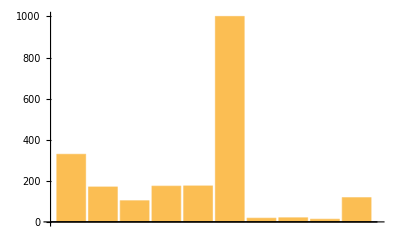

```mathematica
BarChart[%]
```

Find overlap of list of mathematicians names (should this be string list or entity matched list) and Wikipedia Biography Data

```mathematica
wikiMentions[names_]:= Intersection[WikipediaData[names,"LinksList"],Flatten[fullNames]]
```

```mathematica
Map[wikiMentions,wikiBioChecker]
```

{Albert Einstein,Alfred North Whitehead,Johannes Kepler,John Dee,Nicolaus Copernicus}

## Mental Health Disorders List

```mathematica
mentalDisorders = Import["C:\\Users\\tanha\\OneDrive\\Documents\\GitHub\\Summer2018\\StudentDeliverables","List"]
```

```mathematica
expandedDisorders=Join[{"fatigue","dementia"},mentalDisorders];
```

Jofre????? how did he match with mcs bios?

```mathematica
mentalDisorderChecker[namesofm_]:=Intersection[WikipediaData[namesofm,"ArticlePlaintext"],expandedDisroders]
```

## Female Mathematicians

```mathematica
femaleDataset = Import["http://www-history.mcs.st-and.ac.uk/Indexes/Women.html",{"Hyperlinks"}]
```

{http://www-history.mcs.st-and.ac.uk/Biographies/Ayrton.html,http://www-history.mcs.st-and.ac.uk/Biographies/Bari.html,http://www-history.mcs.st-and.ac.uk/Biographies/Bartik.html,http://www-history.mcs.st-and.ac.uk/Biographies/Bassi.html,http://www-history.mcs.st-and.ac.uk/Biographies/Baxter.html,http://www-history.mcs.st-and.ac.uk/Biographies/Beale.html,http://www-history.mcs.st-and.ac.uk/Biographies/Birman.html,http://www-history.mcs.st-and.ac.uk/Biographies/Blanch.html,http://www-history.mcs.st-and.ac.uk/Biographies/Blum.html,http://www-history.mcs.st-and.ac.uk/Biographies/Boole_Mary.html,http://www-history.mcs.st-and.ac.uk/Biographies/Borok.html,http://www-history.mcs.st-and.ac.uk/Biographies/Bosworth.html,http://www-history.mcs.st-and.ac.uk/Biographies/Boyle_Margaret.html,http://www-history.mcs.st-and.ac.uk/Biographies/Browne.html,http://www-history.mcs.st-and.ac.uk/Biographies/Bryant.html,http://www-history.mcs.st-and.ac.uk/Biographies/Burton.html,http://www-history.mcs.st-and.ac.uk/Biographies/Calderwood.html,http://www-history.mcs.st-and.ac.uk/Biographies/Cannell.html,http://www-history.mcs.st-and.ac.uk/Biographies/Cartwright.html,http://www-history.mcs.st-and.ac.uk/Biographies/Castelnuovo_Emma.html,http://www-history.mcs.st-and.ac.uk/Biographies/Chang.html,http://www-history.mcs.st-and.ac.uk/Biographies/Chatelet.html,http://www-history.mcs.st-and.ac.uk/Biographies/Chisholm_Young.html,http://www-history.mcs.st-and.ac.uk/Biographies/Choquet-Bruhat.html,http://www-history.mcs.st-and.ac.uk/Biographies/Chung.html,http://www-history.mcs.st-and.ac.uk/Biographies/Clarke_Joan.html,http://www-history.mcs.st-and.ac.uk/Biographies/Clerke.html,http://www-history.mcs.st-and.ac.uk/Biographies/Cobbe.html,http://www-history.mcs.st-and.ac.uk/Biographies/Cofman.html,http://www-history.mcs.st-and.ac.uk/Biographies/Cox.html,http://www-history.mcs.st-and.ac.uk/Biographies/Daubechies.html,http://www-history.mcs.st-and.ac.uk/Biographies/David.html,http://www-history.mcs.st-and.ac.uk/Biographies/Deans.html,http://www-history.mcs.st-and.ac.uk/Biographies/Dubreil-Jacotin.html,http://www-history.mcs.st-and.ac.uk/Biographies/Edmonds.html,http://www-history.mcs.st-and.ac.uk/Biographies/Ehrenfest-Afanassjewa.html,http://www-history.mcs.st-and.ac.uk/Biographies/Faddeeva.html,http://www-history.mcs.st-and.ac.uk/Biographies/Falconer.html,http://www-history.mcs.st-and.ac.uk/Biographies/Fasenmyer.html,http://www-history.mcs.st-and.ac.uk/Biographies/Fawcett.html,http://www-history.mcs.st-and.ac.uk/Biographies/Fennema.html,http://www-history.mcs.st-and.ac.uk/Biographies/Ferrand.html,http://www-history.mcs.st-and.ac.uk/Biographies/Flugge-Lotz.html,http://www-history.mcs.st-and.ac.uk/Biographies/Freitag.html,http://www-history.mcs.st-and.ac.uk/Biographies/Geiringer.html,http://www-history.mcs.st-and.ac.uk/Biographies/Gentry.html,http://www-history.mcs.st-and.ac.uk/Biographies/Germain.html,http://www-history.mcs.st-and.ac.uk/Biographies/Gould.html,http://www-history.mcs.st-and.ac.uk/Biographies/Granville.html,http://www-history.mcs.st-and.ac.uk/Biographies/Gray.html,http://www-history.mcs.st-and.ac.uk/Biographies/Gray_Marion.html,http://www-history.mcs.st-and.ac.uk/Biographies/Griffiths_Lois.html,http://www-history.mcs.st-and.ac.uk/Biographies/Hamill.html,http://www-history.mcs.st-and.ac.uk/Biographies/Haynes.html,http://www-history.mcs.st-and.ac.uk/Biographies/Harlay.html,http://www-history.mcs.st-and.ac.uk/Biographies/Hau.html,http://www-history.mcs.st-and.ac.uk/Biographies/Hay.html,http://www-history.mcs.st-and.ac.uk/Biographies/Hayes.html,http://www-history.mcs.st-and.ac.uk/Biographies/Hazlett.html,http://www-history.mcs.st-and.ac.uk/Biographies/Hellman.html,http://www-history.mcs.st-and.ac.uk/Biographies/Henriques.html,http://www-history.mcs.st-and.ac.uk/Biographies/Herschel_Caroline.html,http://www-history.mcs.st-and.ac.uk/Biographies/Hevelius_Koopman.html,http://www-history.mcs.st-and.ac.uk/Biographies/Hewitt.html,http://www-history.mcs.st-and.ac.uk/Biographies/Hopper.html,http://www-history.mcs.st-and.ac.uk/Biographies/Hudson.html,http://www-history.mcs.st-and.ac.uk/Biographies/Hypatia.html,http://www-history.mcs.st-and.ac.uk/Biographies/Janovskaja.html,http://www-history.mcs.st-and.ac.uk/Biographies/Jitomirskaya.html,http://www-history.mcs.st-and.ac.uk/Biographies/Johnson_Katherine.html,http://www-history.mcs.st-and.ac.uk/Biographies/Karp.html,http://www-history.mcs.st-and.ac.uk/Biographies/Keen.html,http://www-history.mcs.st-and.ac.uk/Biographies/Keldysh_Lyudmila.html,http://www-history.mcs.st-and.ac.uk/Biographies/Kochina.html,http://www-history.mcs.st-and.ac.uk/Biographies/Kovalevskaya.html,http://www-history.mcs.st-and.ac.uk/Biographies/Kramer.html,http://www-history.mcs.st-and.ac.uk/Biographies/Krieger.html,http://www-history.mcs.st-and.ac.uk/Biographies/Kuperberg.html,http://www-history.mcs.st-and.ac.uk/Biographies/Ladd-Franklin.html,http://www-history.mcs.st-and.ac.uk/Biographies/Ladyzhenskaya.html,http://www-history.mcs.st-and.ac.uk/Biographies/Lax_Anneli.html,http://www-history.mcs.st-and.ac.uk/Biographies/Leavitt.html,http://www-history.mcs.st-and.ac.uk/Biographies/Lehmer_Emma.html,http://www-history.mcs.st-and.ac.uk/Biographies/Lepaute.html,http://www-history.mcs.st-and.ac.uk/Biographies/Libermann.html,http://www-history.mcs.st-and.ac.uk/Biographies/Lovelace.html,http://www-history.mcs.st-and.ac.uk/Biographies/Luchins.html,http://www-history.mcs.st-and.ac.uk/Biographies/Macintyre.html,http://www-history.mcs.st-and.ac.uk/Biographies/Mackenzie.html,http://www-history.mcs.st-and.ac.uk/Biographies/MacMillan_Chrystal.html,http://www-history.mcs.st-and.ac.uk/Biographies/Maddison.html,http://www-history.mcs.st-and.ac.uk/Biographies/Malone-Mayes.html,http://www-history.mcs.st-and.ac.uk/Biographies/Martin_Emilie.html,http://www-history.mcs.st-and.ac.uk/Biographies/McDuff.html,http://www-history.mcs.st-and.ac.uk/Biographies/Merrill.html,http://www-history.mcs.st-and.ac.uk/Biographies/Michler.html,http://www-history.mcs.st-and.ac.uk/Biographies/Millington.html,http://www-history.mcs.st-and.ac.uk/Biographies/Mirzakhani.html,http://www-history.mcs.st-and.ac.uk/Biographies/Morawetz.html,http://www-history.mcs.st-and.ac.uk/Biographies/Moufang.html,http://www-history.mcs.st-and.ac.uk/Biographies/Nalli.html,http://www-history.mcs.st-and.ac.uk/Biographies/Nelson.html,http://www-history.mcs.st-and.ac.uk/Biographies/Neumann_Hanna.html,http://www-history.mcs.st-and.ac.uk/Biographies/Newson.html,http://www-history.mcs.st-and.ac.uk/Biographies/Nicolson.html,http://www-history.mcs.st-and.ac.uk/Biographies/Nightingale.html,http://www-history.mcs.st-and.ac.uk/Biographies/Noether_Emmy.html,http://www-history.mcs.st-and.ac.uk/Biographies/Nugel.html,http://www-history.mcs.st-and.ac.uk/Biographies/Numbers.html,http://www-history.mcs.st-and.ac.uk/Biographies/Oleinik.html,http://www-history.mcs.st-and.ac.uk/Biographies/Olive.html,http://www-history.mcs.st-and.ac.uk/Biographies/Ollerenshaw.html,http://www-history.mcs.st-and.ac.uk/Biographies/Orshansky.html,http://www-history.mcs.st-and.ac.uk/Biographies/Pairman.html,http://www-history.mcs.st-and.ac.uk/Biographies/Pandrosion.html,http://www-history.mcs.st-and.ac.uk/Biographies/Payne-Gaposchkin.html,http://www-history.mcs.st-and.ac.uk/Biographies/Perrin-Riou.html,http://www-history.mcs.st-and.ac.uk/Biographies/Peter.html,http://www-history.mcs.st-and.ac.uk/Biographies/Philip_Flora.html,http://www-history.mcs.st-and.ac.uk/Biographies/Pless.html,http://www-history.mcs.st-and.ac.uk/Biographies/Praeger.html,http://www-history.mcs.st-and.ac.uk/Biographies/Rasiowa.html,http://www-history.mcs.st-and.ac.uk/Biographies/Ratner.html,http://www-history.mcs.st-and.ac.uk/Biographies/Rees.html,http://www-history.mcs.st-and.ac.uk/Biographies/Rhodes.html,http://www-history.mcs.st-and.ac.uk/Biographies/Robinson_Julia.html,http://www-history.mcs.st-and.ac.uk/Biographies/Rothe-Ille.html,http://www-history.mcs.st-and.ac.uk/Biographies/Rudin.html,http://www-history.mcs.st-and.ac.uk/Biographies/Sadosky.html,http://www-history.mcs.st-and.ac.uk/Biographies/Sargent.html,http://www-history.mcs.st-and.ac.uk/Biographies/Schafer.html,http://www-history.mcs.st-and.ac.uk/Biographies/Schattschneider.html,http://www-history.mcs.st-and.ac.uk/Biographies/Scott.html,http://www-history.mcs.st-and.ac.uk/Biographies/Scott_Agnes.html,http://www-history.mcs.st-and.ac.uk/Biographies/Scott_Elizabeth.html,http://www-history.mcs.st-and.ac.uk/Biographies/Senechal.html,http://www-history.mcs.st-and.ac.uk/Biographies/Simpson_Mary.html,http://www-history.mcs.st-and.ac.uk/Biographies/Smith_Karen.html,http://www-history.mcs.st-and.ac.uk/Biographies/Somerville.html,http://www-history.mcs.st-and.ac.uk/Biographies/Sperry.html,http://www-history.mcs.st-and.ac.uk/Biographies/Srinivasan.html,http://www-history.mcs.st-and.ac.uk/Biographies/Steele.html,http://www-history.mcs.st-and.ac.uk/Biographies/Stephansen.html,http://www-history.mcs.st-and.ac.uk/Biographies/Stott.html,http://www-history.mcs.st-and.ac.uk/Biographies/Swain.html,http://www-history.mcs.st-and.ac.uk/Biographies/Szmielew.html,http://www-history.mcs.st-and.ac.uk/Biographies/Taussky-Todd.html,http://www-history.mcs.st-and.ac.uk/Biographies/Taylor_Mary.html,http://www-history.mcs.st-and.ac.uk/Biographies/Thompson_Abigail.html,http://www-history.mcs.st-and.ac.uk/Biographies/Tinney.html,http://www-history.mcs.st-and.ac.uk/Biographies/Uhlenbeck_Karen.html,http://www-history.mcs.st-and.ac.uk/Biographies/Velez-Rodriguez.html,http://www-history.mcs.st-and.ac.uk/Biographies/Vernon.html,http://www-history.mcs.st-and.ac.uk/Biographies/Wales.html,http://www-history.mcs.st-and.ac.uk/Biographies/Walter.html,http://www-history.mcs.st-and.ac.uk/Biographies/Warner.html,http://www-history.mcs.st-and.ac.uk/Biographies/Wexler-Kreindler.html,http://www-history.mcs.st-and.ac.uk/Biographies/Wheeler.html,http://www-history.mcs.st-and.ac.uk/Biographies/Wood.html,http://www-history.mcs.st-and.ac.uk/Biographies/Wrinch.html,http://www-history.mcs.st-and.ac.uk/Biographies/Wu.html,http://www-history.mcs.st-and.ac.uk/Biographies/Young_Lai-Sang.html,http://www-history.mcs.st-and.ac.uk/Davis/index.html,http://www-history.mcs.st-and.ac.uk/Indexes/Women_pics.html,http://www-history.mcs.st-and.ac.uk/Indexes/A.html,http://www-history.mcs.st-and.ac.uk/Indexes/B.html,http://www-history.mcs.st-and.ac.uk/Indexes/C.html,http://www-history.mcs.st-and.ac.uk/Indexes/D.html,http://www-history.mcs.st-and.ac.uk/Indexes/E.html,http://www-history.mcs.st-and.ac.uk/Indexes/F.html,http://www-history.mcs.st-and.ac.uk/Indexes/G.html,http://www-history.mcs.st-and.ac.uk/Indexes/H.html,http://www-history.mcs.st-and.ac.uk/Indexes/IJ.html,http://www-history.mcs.st-and.ac.uk/Indexes/K.html,http://www-history.mcs.st-and.ac.uk/Indexes/L.html,http://www-history.mcs.st-and.ac.uk/Indexes/M.html,http://www-history.mcs.st-and.ac.uk/Indexes/N.html,http://www-history.mcs.st-and.ac.uk/Indexes/O.html,http://www-history.mcs.st-and.ac.uk/Indexes/PQ.html,http://www-history.mcs.st-and.ac.uk/Indexes/R.html,http://www-history.mcs.st-and.ac.uk/Indexes/S.html,http://www-history.mcs.st-and.ac.uk/Indexes/T.html,http://www-history.mcs.st-and.ac.uk/Indexes/UV.html,http://www-history.mcs.st-and.ac.uk/Indexes/W.html,http://www-history.mcs.st-and.ac.uk/Indexes/XYZ.html,http://www-history.mcs.st-and.ac.uk/index.html,http://www-history.mcs.st-and.ac.uk/BiogIndex.html,http://www-history.mcs.st-and.ac.uk/Indexes/Full_Chron.html,http://www-maths.mcs.st-andrews.ac.uk/,http://www.st-andrews.ac.uk/,http://www-maths.mcs.st-andrews.ac.uk/}

```mathematica
femaleDataset1 =Flatten[StringCases[femaleDataset,"http://www-history.mcs.st-and.ac.uk/Biographies/"~~__]];
```

```mathematica
femaleDataset2 = Import[#,"Text"]&/@femaleDataset1
```

{25839,23105,21446,12250,8948,152,27091,17744,12880,14815,17691}
 |  |  |  |

```mathematica
femHtmls= Map[htmlToText,femaleDataset2]
```

{25804,23084,21446,12236,8948,152,27045,17744,12880,14801,17677}
 |  |  |  |

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\tanha\OneDrive\Documents\GitHub\Summer2018\StudentDeliverables

```mathematica
Export["femaleBioList.mx",femHtmls,"MX"]
```

femaleBioList.mx

```mathematica
femBioList = Import["C:\\Users\\tanha\\OneDrive\\Documents\\GitHub\\Summer2018\\StudentDeliverables\\femaleBioList.mx"]
```

{25804,23084,21446,12236,8948,152,27045,17744,12880,14801,17677}
 |  |  |  |

```mathematica
femFullNames = StringCases[femBioList,"<h1>"~~x__~~"</h1>"->x]
```

{{Phoebe Sarah Hertha Marks Ayrton},{Nina Karlovna Bari},{Betty Jean Jennings Bartik},{Laura Maria Catarina Bassi},{Agnes Sime Baxter},{Dorothea Beale},{Joan Sylvia Lyttle Birman},{Gertrude Blanch},{Lenore Blum},{Mary Everest Boole},{Valentina Mikhailovna Borok},{Anne Lucy Bosworth Focke},{Margaret Edward Boyle},{Marjorie Lee Browne},{Sophie Willock Bryant},{Leone Minna Gold Burton},{Nora Isobel Calderwood},{Doris Mary Cannell},{Dame Mary Lucy Cartwright},{Emma Castelnuovo},{Sun-Yung Alice Chang},{ Gabrielle Émilie Le Tonnelier de  Breteuil Marquise du Châtelet},{Grace Chisholm Young},{Yvonne Suzanne Marie-Louise Choquet-Bruhat},{Fan Rong K Chung Graham},{Joan Elisabeth Lowther Clarke Murray},{Agnes Mary Clerke},{Anne Philippa Cobbe},{Judita Cofman},{Gertrude Mary Cox},{Ingrid Daubechies},{Florence Nightingale David},{Winifred Margaret Deans},{Marie-Louise Dubreil-Jacotin},{Sheila May Edmonds},{Tatiana Ehrenfest-Afanassjewa},{Vera Nikolaevna Faddeeva},{Etta Zuber Falconer},{Mary Celine Fasenmyer},{Philippa Garrett Fawcett},{Ann Elizabeth Hammer Fennema},{Jacqueline Ferrand},{Irmgard Flügge-Lotz},{Herta Taussig Freitag},{Hilda Geiringer von Mises},{Ruth Ellen Gentry},{Marie-Sophie Germain},{Alice Bache Gould},{Evelyn Boyd Granville},{Mary Lee Wheat Gray},{Marion Cameron Gray},{Lois Wilfred Griffiths},{Christine Mary Hamill},{Martha Euphemia Lofton Haynes},{Marie-Jeanne Amélie Harlay},{Lene Vestergaard Hau},{Louise Schmir Hay},{Ellen Amanda Hayes},{Olive Clio Hazlett},{Clarisse Doris Hellman},{Anna Adelaide Stafford Henriques},{Caroline Lucretia Herschel},{Catherina Elisabetha Koopman Hevelius},{Gloria Conyers Hewitt},{Grace Brewster Murray Hopper},{Hilda Phoebe Hudson},{Hypatia of Alexandria },{Sof'ja Aleksandrovna Janovskaja},{Svetlana Yakovlevna Jitomirskaya},{Katherine Coleman Goble Johnson},{Carol Ruth Karp},{Linda Goldway Keen},{Lyudmila Vsevolodovna Keldysh},{Pelageia Yakovlevna Polubarinova Kochina},{Sofia Vasilyevna Kovalevskaya},{Edna Ernestine Kramer Lassar},{Cypra Cecilia Krieger Dunaij},{Krystyna Maria Trybulec Kuperberg},{Christine Ladd-Franklin},{Olga Alexandrovna Ladyzhenskaya},{Anneli Cahn Lax},{Henrietta Swan Leavitt },{Emma Markovna Trotskaia Lehmer},{Nicole-Reine Etable de Labrière Lepaute},{Paulette Libermann},{ Augusta Ada King, countess of Lovelace},{Edith Hirsch Luchins},{Sheila Scott Macintyre},{Gladys Isabel Mackenzie},{Jessie Chrystal MacMillan},{Ada Isabel Maddison},{Vivienne Malone-Mayes},{Emilie Norton Martin},{Margaret Dusa Waddington McDuff},{Winifred Edgerton Merrill},{Ruth Ingrid Michler},{Margaret Hilary Ashworth Millington},{Maryam Mirzakhani},{Cathleen Synge Morawetz},{Ruth Moufang},{Pia Maria Nalli},{Evelyn Merle Roden Nelson},{Hanna Neumann},{Mary Frances Winston Newson},{Phyllis Nicolson},{Florence Nightingale},{Emmy Amalie Noether},{Frieda Nugel},{Annie Hutton Numbers},{Olga Arsen'evna Oleinik},{Gloria Olive},{Kathleen Timpson Ollerenshaw},{Mollie Orshansky},{Eleanor Pairman},{Pandrosion of Alexandria },{Cecilia Helena Payne-Gaposchkin},{Bernadette Perrin-Riou},{Rózsa Péter},{Flora Philip},{Vera Pless},{Cheryl Elisabeth Praeger},{Helena Rasiowa},{Marina Ratner},{Mina Spiegel Rees},{Ida Rhodes},{Julia Hall Bowman Robinson},{Hildegard Rothe-Ille},{Mary Ellen Rudin},{Cora Susana Sadosky},{Winifred Lydia Caunden Sargent},{Alice Turner Schafer},{Doris Jean Wood Schattschneider},{Charlotte Angas Scott},{Agnes Mary Scott},{Elizabeth Leonard Scott},{Marjorie Lee Wikler Senechal},{Mary Constance Simpson},{Karen Ellen Smith},{ Mary Fairfax Greig Somerville},{Pauline Sperry},{Bhama Srinivasan},{Catherine Cassels Steele},{Mary Ann Elizabeth Stephansen},{Alicia Boole Stott},{Lorna Mary Swain},{Wanda Montlak Szmielew},{Olga Taussky-Todd},{Mary Taylor Slow},{Abigail A Thompson},{Sheila Christina Power Tinney},{Karen Keskulla Uhlenbeck},{Argelia Velez-Rodriguez},{Siobhan O'Shea Vernon},{Muriel Kennett Wales},{Marion Ilse Walter},{Mary Wynne Warner},{Eléna Wexler-Kreindler},{Anna Johnson Pell Wheeler},{Frances Chick Wood},{Dorothy Maud Wrinch},{Sijue Wu},{Lai-Sang Young}}

```mathematica
fembioReferences = StringCases[femBioList,"../Mathematicians/"~~Shortest[a__]~~".html"->a];
```

```mathematica
femuniqueReference=Map[Union,fembioReferences]
```

{{Maxwell,Rayleigh,Scott,Thomson},{Aleksandrov,Chaplygin,Egorov,Fourier,Hadamard,Lavrentev,Lebesgue,Luzin,Menshov,Stepanov,Urysohn,Zhukovsky,Zygmund},{Eckert_John,Goldstine,Mauchly,Von_Neumann},{Descartes,Newton},{},{Euclid},{Artin,Chauvenet,Fox_Ralph,Magnus,Morawetz,Nirenberg,Noether_Emmy},{Baker,Goldstein,Ince,Karman,Mathieu_Emile,Planck,Snyder,Todd},{Euler,Gauss,Godel,Mandelbrot,Newton,Penrose,Smale,Turing},{Babbage,Boole,Herschel,Stott},{Cauchy,Lindelof,Phragmen},{Bolza,Halsted,Hilbert,Klein,Moore_Eliakim,Schonflies,Schur},{},{Granville},{Ladd-Franklin,Pappus,Scott},{Levy,Levy_Hyman,Russell,Whitehead},{Aitken,Numbers},{Green},{Ahlfors,De_Morgan,Hardy,Littlewood,Morton_Vernon,Sylvester,Titchmarsh,Watson,Whittaker},{Castelnuovo,Choquet,Clairaut,Dieudonne,Enriques,Euclid,Freudenthal,Klein,Lichnerowicz},{Aubin,Hedrick,Osgood,Schoen},{Clairaut,Euler,Fontenelle,Kline,Konig_Samuel,Leibniz,Maupertuis,Newton},{Cantor,Cartwright,Klein,Maddison,Young},{Apery,Bruhat,Cartan,Chern,Einstein,Heisenberg,Lichnerowicz,Lie,Schrodinger,Schwinger,Stiefel,Weyl,Wiener_Norbert,Yau},{Erdos,Graham,Ramsey,Schelp},{Fawcett,Turing},{Airy,Ball_Robert,Bessel,Cotes,De_Moivre,Galileo,Glaisher,Herschel,Herschel_Caroline,Huygens,Kepler,Lagrange,Landen,Laplace,Machin,Somerville,Wilson_Alexander},{Lane,Whitehead_Henry},{Hirzebruch},{Cochran,Quetelet,Yates},{Fourier},{Birnbaum,Fisher,Kendall_Maurice,Neyman,Nightingale,Pearson,Pearson_Egon,Wilks,Wolfowitz},{Born},{Artin,Bjerknes_Vilhelm,Cartan,Chevalley,Dubreil,Hadamard,Hilbert,Julia,Lebesgue,Leray,Levi-Civita,Noether_Emmy,Prufer,Rutherford,Schutzenberger,Vessiot,Weyl},{Al-Karaji,Hardy,Parseval},{Boltzmann,De_Bruijn,Ehrenfest,Euclid,Gibbs,Hilbert,Klein,Tutte,Zermelo},{Faddeev,Fiedler,Forsythe,Galerkin,Golub,Householder,Kantorovich,Kublanovskaya,Mikhlin,Peter,Smirnov,Steklov,Stieltjes,Taussky-Todd,Varga,Wilkinson},{Granville,Lorch,Moufang},{Bateman,Jacobi,Knuth,Legendre},{Ball,Hobson},{},{Apery,Denjoy,Dieudonne,Dubreil-Jacotin,Hayman,Julia,Lichnerowicz,Lindelof,Montel,Poincare,Valiron},{Karman},{Fibonacci,Gauss},{Lichtenstein,Mises,Neyman,Poisson,Pollaczek,Schur,Wheeler,Wirtinger},{Bouquet,Briot,Cayley,Fuchs,Klein,Schlesinger,Scott},{Archimedes,De_Prony,Euler,Gauss,Kummer,Lagrange,Laplace,Legendre,Newton,Poisson},{Bessel,Brocard,Gauss,Moore_Eliakim,Newcomb,Peirce_Benjamin},{Browne,Hille,John},{Scott},{Wheeler,Whittaker},{Birkhoff_Garrett,Brown,Carmichael,Dickson,MacDuffee,MacLane},{Todd},{Morley},{Herschel_Caroline,Lalande,Newton},{Bohr_Niels,Bose,Einstein,Heisenberg},{Artin,Lukasiewicz,Neumann_Hanna,Turing},{},{Albert_Abraham,Dickson,Galois,Halmos,Moore_Eliakim,Scott,Van_der_Waerden},{Boyer,Hopper},{Alexander,Apostol,Einstein,Nielsen_Jakob,Veblen,Wilder},{Flamsteed,Gauss,Herschel,Herschel_William,Maclaurin,Maskelyne,Somerville},{Arago,Bernoulli_Johann(III),Halley,Hevelius_Johannes},{},{Aiken,Eckert,Eckert_John,Mauchly,Ore},{Cayley,Cremona,Landau,Schottky,Schwarz,Scott,Semple},{Apollonius,Diophantus,Euclid,Heath,Ptolemy,Theon},{Ackermann,Aristotle,Church,Descartes,Euclid,Frege,Godel,Goodstein,Hilbert,Kleene,Lobachevsky,Polya,Rolle,Shatunovsky,Tarski,Turing,Wittgenstein,Zeno_of_Elea},{Arnold,Borok,Bourgain,Cantor,Green,Schrodinger,Sinai},{Claytor},{Godel},{Ahlfors,Bers,Courant,Fricke,Noether_Emmy,Riemann,Thurston},{Adian,Aleksandrov,Baire,Borel,Keldysh_Mstislav,Khinchin,Kolmogorov,Luzin,Menshov,Novikov,Peano,Steklov,Suslin},{Chaplygin,Friedmann,Keldysh_Mstislav,Kochin,Kovalevskaya,Krylov_Aleksei,Mittag-Leffler,Smirnov,Sobolev,Steklov,Vinogradov,Weierstrass},{Agnesi,Bruns,Chebyshev,Crelle,Kirchhoff,Konigsberger,Lame,Mittag-Leffler,Ostrogradski,Volterra,Weierstrass},{Dodgson,Einstein,Fermat,Kasner,Khayyam,Newton},{Fields,Morawetz,Nelson,Sierpinski,Synge},{Borsuk,Hurewicz,Kuratowski,Mostowski,Poincare,Seifert,Ulam},{Franklin_Fabian,Helmholtz,Peirce_Charles,Story,Sylvester},{Bernstein_Sergei,Cauchy,Chebyshev,Courant,Delone,Gelfand,Hilbert,Hopf,Kurosh,Leray,Maxwell,Navier,Petrovsky,Schrodinger,Smirnov,Sobolev,Steklov,Stepanov,Stokes,Tikhonov,Von_Neumann},{Courant,Hilbert,Lax_Peter,Poincare,Robbins},{Mittag-Leffler},{Crelle,Davenport,Erdos,Hardy,Hasse,Lehmer_Derrick,Lehmer_Derrick_N,Littlewood,Mahler,Mordell,Pontryagin,Vandiver},{Clairaut,Halley,Lalande},{Cartan,Ehresmann,Ferrand,Leray,Lichnerowicz,Lie,Poisson,Whitehead_Henry},{Babbage,De_Morgan,Menabrea,Ohm,Somerville},{Banach,Bonsall,Courant,Friedrichs,Germain,Hausdorff,Hypatia,Kovalevskaya,Noether_Emmy,Noether_Max,Weierstrass},{Abel,Cartwright,Gregory,Laplace,Macintyre_Archibald,Newton,Ramanujan,Whittaker,Wright},{Barkla},{Chrystal,Knott,Tait},{Burkhardt,Cayley,Chisholm_Young,Hilbert,Klein,Scott,Whitehead,Young},{Falconer,Granville,Hausdorff,Lorch,Moore_Robert},{Cayley,Hilbert,Klein,Scott},{Adams_Frank,Gelfand,Gromov,Milnor,Witten},{},{Atiyah,Baer,Ball,De_Rham,Hodge,Kahler,Loday,Macaulay,Manin,Penrose},{Fourier,Petersson,Ramanujan},{Fields,Kontsevich,McMullen,Riemann,Weil,Witten},{Birkhoff,Courant,Friedrichs,Karman,Krieger,Nelson,Synge},{Bieberbach,Dehn,Desargues,Descartes,Epstein,Euclid,Hellinger,Hilbert,Magnus,Pappus,Prager,Schonflies,Siegel,Szasz},{Bagnera,Bianchi,Borel,Castelnuovo,Denjoy,Dirichlet,Du_Bois-Reymond,Enriques,Fichera,Fredholm,Guccia,Hadamard,Hilbert,Lebesgue,Levi-Civita,Peano,Picone,Poincare,Ricci-Curbastro,Riemann,Segre_Corrado,Vallee_Poussin,Vitali,Volterra},{Krieger},{Bieberbach,Courant,Feigl,Hall,Hasse,Higman,Hirsch,Kurosh,Lehmer_Derrick,Neumann_Bernhard,Rado_Richard,Schmidt,Schur,Taussky-Todd,Whitehead_Henry,Wielandt},{Bolza,Chisholm_Young,Franklin_Fabian,Hermite,Hilbert,Klein,Kovalevskaya,Ladd-Franklin,Lame,Maschke,Moore_Eliakim,Scott,Smith_David,Weber_Heinrich},{Crank,Hartree,Richardson},{Aristotle,Cayley,Euclid,Quetelet,Sylvester},{Albert_Abraham,Artin,Blumenthal,Brauer,Einstein,Fischer,Gordan,Hasse,Hilbert,Klein,Lasker,Mertens,Minkowski,Noether_Max,Schwarzschild,Van_der_Waerden,Vandiver,Veblen,Weyl,Wheeler},{Cantor,Frobenius,Fuchs,Gauss,Gutzmer,Hilbert,Kronecker,Kummer,Lindemann,Noether_Emmy,Schottky,Schur,Schwarz,Wangerin,Weierstrass},{},{Dirichlet,Navier,Noether_Emmy,Petrovsky,Stokes},{Douglas,MacDuffee,MacLane,Rota},{Bondi,Einstein,Euler,Ferrar,Frenicle_de_Bessy,Mahler,Turing,Turnbull},{},{Birkhoff,Ford,Kemeny,Knott,Pearson},{Hypatia,Pappus},{Bohr_Niels,Eddington,Einstein,Euclid,Fowler,Newton},{Bloch,Coates,Euler,Galois,Godement,Hasse,Iwasawa,Kato,Tate},{Ackermann,Bernays,Bolyai,Carmichael,Dickson,Eotvos,Fejer,Godel,Goodstein,Herbrand,Hilbert,Kalmar,Kemeny,Kleene,Kurschak,Peano},{},{Conway,Hamming,Kaplansky,Noether_Emmy},{Neumann_Bernhard,Neumann_Hanna},{Borsuk,Heyting,Lukasiewicz,Mazurkiewicz,Mostowski,Post,Sierpinski,Stone,Tarski},{Bowen,Daubechies,Kolmogorov,Lie,Margulis,Noether_Emmy,Oppenheim,Ostrowski,Sinai,Uhlenbeck_Karen},{Dickson,MacLane,Noether_Emmy},{Blanch,Eckert_John,Hopper,Mauchly},{Bell,Church,Davis,Godel,Herbrand,Hilbert,Kleene,Neyman,Noether_Emmy,Post,Robinson_Raphael,Tarski,Turing,Wheeler},{Brauer_Alfred,Einstein,Erdos,Hopf,Rado_Richard,Ramsey,Rothe_Erich,Schmidt,Schottky,Schur,Turan,Van_der_Waerden},{Chisholm_Young,Hausdorff,Jones_Burton,Moore_Robert,Noether_Emmy,Rudin_Walter,Wilder},{Calderon,Cotlar,Darmois,Frechet,Noether_Emmy,Picone,Poincare,Riemann,Zygmund},{Bosanquet,Burkill,Cesaro,Denjoy,Fourier,Lebesgue,Perron,Riemann,Young},{},{},{Cayley,Gentry,Macaulay,Maddison,Whitehead},{Ford,Gibb},{David,Neyman,Sperry},{Apostol,Delone,Lorch,Menger,Wrinch},{},{Fefferman,Heinonen,Noether_Emmy},{Adams,Airy,Arago,Babbage,Biot,Euclid,Herschel,Herschel_Caroline,Herschel_William,Laplace,Leslie,Lovelace,Mathieu_Emile,Maxwell,Newton,Peacock,Playfair,Poinsot,Poisson,Wallace},{Wilczynski},{Blum,Brauer,Green_Sandy,Hall,Lie,Littlewood,Lusztig,Neumann_Bernhard,Newman,Noether_Emmy,Ramanujan,Ree,Van_der_Waerden},{},{DAlembert,Euler,Frobenius,Hilbert,Hurwitz,Klein,Lagrange,Zermelo},{Baker,Boole,Boole_Mary,Coxeter,Euclid,Schoute,Taylor_Geoffrey},{Lamb},{Borsuk,Coxeter,Hilbert,Kuratowski,Lindenbaum,Lukasiewicz,Malcev,Moore_Eliakim,Mostowski,Rasiowa,Robinson,Sierpinski,Tarski,Veblen},{Apostol,Artin,Courant,Crelle,Furtwangler,Godel,Hahn,Hardy,Helly,Hilbert,Magnus,Menger,Neumann_Hanna,Noether_Emmy,Schur,Sylow,Todd_John,Von_Neumann,Wirtinger},{Courant},{Birman,Dehn,Heegaard,Kirby,Thurston},{Born,Conway_Arthur,De_Valera,Dirac,Dyson,Eddington,Einstein,Feynman,Harish-Chandra,Schrodinger,Tait,Uhlenbeck,Weyl},{Courant,Donaldson,Einstein,Witten,Yau},{},{Kennedy},{Beatty},{Albert_Abraham,Bers,Blanch,Courant,Forsythe,Friedrichs,Hall_Marshall,Hunt,Kac,Kaplansky,Lanczos,Lehmer_Derrick,Motzkin,Polya,Schoenberg,Taussky-Todd,Walsh_Joseph,Wolfowitz},{Borsuk,Kuratowski,Whitehead_Henry,Zeeman},{Moisil,Ore},{Bocher,Fourier,Herglotz,Hilbert,Klein,Lichtenstein,Minkowski,Moore_Eliakim,Noether_Emmy,Osgood,Pell_Alexander,Schwarzschild,Scott},{Galton,Pearson,Yule},{Johnson,Russell,Von_Neumann,Wiener_Norbert},{},{Birman,Kovalevskaya,Lyapunov,McDuff,Noether_Emmy,Poincare}}

```mathematica
ClearAll[a]
```

```mathematica
allfemNames = Flatten@StringCases[Import["http://www-history.mcs.st-and.ac.uk/Indexes/Women.html",{"Hyperlinks"}],"/Biographies/"~~Shortest[a__]~~".html"->a]
```

{Ayrton,Bari,Bartik,Bassi,Baxter,Beale,Birman,Blanch,Blum,Boole_Mary,Borok,Bosworth,Boyle_Margaret,Browne,Bryant,Burton,Calderwood,Cannell,Cartwright,Castelnuovo_Emma,Chang,Chatelet,Chisholm_Young,Choquet-Bruhat,Chung,Clarke_Joan,Clerke,Cobbe,Cofman,Cox,Daubechies,David,Deans,Dubreil-Jacotin,Edmonds,Ehrenfest-Afanassjewa,Faddeeva,Falconer,Fasenmyer,Fawcett,Fennema,Ferrand,Flugge-Lotz,Freitag,Geiringer,Gentry,Germain,Gould,Granville,Gray,Gray_Marion,Griffiths_Lois,Hamill,Haynes,Harlay,Hau,Hay,Hayes,Hazlett,Hellman,Henriques,Herschel_Caroline,Hevelius_Koopman,Hewitt,Hopper,Hudson,Hypatia,Janovskaja,Jitomirskaya,Johnson_Katherine,Karp,Keen,Keldysh_Lyudmila,Kochina,Kovalevskaya,Kramer,Krieger,Kuperberg,Ladd-Franklin,Ladyzhenskaya,Lax_Anneli,Leavitt,Lehmer_Emma,Lepaute,Libermann,Lovelace,Luchins,Macintyre,Mackenzie,MacMillan_Chrystal,Maddison,Malone-Mayes,Martin_Emilie,McDuff,Merrill,Michler,Millington,Mirzakhani,Morawetz,Moufang,Nalli,Nelson,Neumann_Hanna,Newson,Nicolson,Nightingale,Noether_Emmy,Nugel,Numbers,Oleinik,Olive,Ollerenshaw,Orshansky,Pairman,Pandrosion,Payne-Gaposchkin,Perrin-Riou,Peter,Philip_Flora,Pless,Praeger,Rasiowa,Ratner,Rees,Rhodes,Robinson_Julia,Rothe-Ille,Rudin,Sadosky,Sargent,Schafer,Schattschneider,Scott,Scott_Agnes,Scott_Elizabeth,Senechal,Simpson_Mary,Smith_Karen,Somerville,Sperry,Srinivasan,Steele,Stephansen,Stott,Swain,Szmielew,Taussky-Todd,Taylor_Mary,Thompson_Abigail,Tinney,Uhlenbeck_Karen,Velez-Rodriguez,Vernon,Wales,Walter,Warner,Wexler-Kreindler,Wheeler,Wood,Wrinch,Wu,Young_Lai-Sang}

```mathematica
femvertexList = Flatten@ MapThread[ Thread[Rule[#1 , #2]]&,{allfemNames,femuniqueReference}]
```

{Ayrton→Maxwell,Ayrton→Rayleigh,Ayrton→Scott,Ayrton→Thomson,Bari→Aleksandrov,Bari→Chaplygin,Bari→Egorov,Bari→Fourier,Bari→Hadamard,Bari→Lavrentev,Bari→Lebesgue,Bari→Luzin,Bari→Menshov,Bari→Stepanov,Bari→Urysohn,Bari→Zhukovsky,Bari→Zygmund,Bartik→Eckert_John,Bartik→Goldstine,Bartik→Mauchly,Bartik→Von_Neumann,Bassi→Descartes,Bassi→Newton,Beale→Euclid,Birman→Artin,Birman→Chauvenet,Birman→Fox_Ralph,Birman→Magnus,Birman→Morawetz,Birman→Nirenberg,Birman→Noether_Emmy,Blanch→Baker,Blanch→Goldstein,Blanch→Ince,Blanch→Karman,Blanch→Mathieu_Emile,Blanch→Planck,Blanch→Snyder,Blanch→Todd,Blum→Euler,Blum→Gauss,Blum→Godel,Blum→Mandelbrot,Blum→Newton,Blum→Penrose,Blum→Smale,Blum→Turing,Boole_Mary→Babbage,Boole_Mary→Boole,Boole_Mary→Herschel,Boole_Mary→Stott,Borok→Cauchy,Borok→Lindelof,Borok→Phragmen,Bosworth→Bolza,Bosworth→Halsted,Bosworth→Hilbert,Bosworth→Klein,Bosworth→Moore_Eliakim,Bosworth→Schonflies,Bosworth→Schur,Browne→Granville,Bryant→Ladd-Franklin,Bryant→Pappus,Bryant→Scott,Burton→Levy,Burton→Levy_Hyman,Burton→Russell,Burton→Whitehead,Calderwood→Aitken,Calderwood→Numbers,Cannell→Green,Cartwright→Ahlfors,Cartwright→De_Morgan,Cartwright→Hardy,Cartwright→Littlewood,Cartwright→Morton_Vernon,Cartwright→Sylvester,Cartwright→Titchmarsh,Cartwright→Watson,Cartwright→Whittaker,Castelnuovo_Emma→Castelnuovo,Castelnuovo_Emma→Choquet,Castelnuovo_Emma→Clairaut,Castelnuovo_Emma→Dieudonne,Castelnuovo_Emma→Enriques,Castelnuovo_Emma→Euclid,Castelnuovo_Emma→Freudenthal,Castelnuovo_Emma→Klein,Castelnuovo_Emma→Lichnerowicz,Chang→Aubin,Chang→Hedrick,Chang→Osgood,Chang→Schoen,Chatelet→Clairaut,Chatelet→Euler,Chatelet→Fontenelle,Chatelet→Kline,Chatelet→Konig_Samuel,Chatelet→Leibniz,Chatelet→Maupertuis,Chatelet→Newton,Chisholm_Young→Cantor,Chisholm_Young→Cartwright,Chisholm_Young→Klein,Chisholm_Young→Maddison,Chisholm_Young→Young,Choquet-Bruhat→Apery,Choquet-Bruhat→Bruhat,Choquet-Bruhat→Cartan,Choquet-Bruhat→Chern,Choquet-Bruhat→Einstein,Choquet-Bruhat→Heisenberg,Choquet-Bruhat→Lichnerowicz,Choquet-Bruhat→Lie,Choquet-Bruhat→Schrodinger,Choquet-Bruhat→Schwinger,Choquet-Bruhat→Stiefel,Choquet-Bruhat→Weyl,Choquet-Bruhat→Wiener_Norbert,Choquet-Bruhat→Yau,Chung→Erdos,Chung→Graham,Chung→Ramsey,Chung→Schelp,Clarke_Joan→Fawcett,Clarke_Joan→Turing,Clerke→Airy,Clerke→Ball_Robert,Clerke→Bessel,Clerke→Cotes,Clerke→De_Moivre,Clerke→Galileo,Clerke→Glaisher,Clerke→Herschel,Clerke→Herschel_Caroline,Clerke→Huygens,Clerke→Kepler,Clerke→Lagrange,Clerke→Landen,Clerke→Laplace,Clerke→Machin,Clerke→Somerville,Clerke→Wilson_Alexander,Cobbe→Lane,Cobbe→Whitehead_Henry,Cofman→Hirzebruch,Cox→Cochran,Cox→Quetelet,Cox→Yates,Daubechies→Fourier,David→Birnbaum,David→Fisher,David→Kendall_Maurice,David→Neyman,David→Nightingale,David→Pearson,David→Pearson_Egon,David→Wilks,David→Wolfowitz,Deans→Born,Dubreil-Jacotin→Artin,Dubreil-Jacotin→Bjerknes_Vilhelm,Dubreil-Jacotin→Cartan,Dubreil-Jacotin→Chevalley,Dubreil-Jacotin→Dubreil,Dubreil-Jacotin→Hadamard,Dubreil-Jacotin→Hilbert,Dubreil-Jacotin→Julia,Dubreil-Jacotin→Lebesgue,Dubreil-Jacotin→Leray,Dubreil-Jacotin→Levi-Civita,Dubreil-Jacotin→Noether_Emmy,Dubreil-Jacotin→Prufer,Dubreil-Jacotin→Rutherford,Dubreil-Jacotin→Schutzenberger,Dubreil-Jacotin→Vessiot,Dubreil-Jacotin→Weyl,Edmonds→Al-Karaji,Edmonds→Hardy,Edmonds→Parseval,Ehrenfest-Afanassjewa→Boltzmann,Ehrenfest-Afanassjewa→De_Bruijn,Ehrenfest-Afanassjewa→Ehrenfest,Ehrenfest-Afanassjewa→Euclid,Ehrenfest-Afanassjewa→Gibbs,Ehrenfest-Afanassjewa→Hilbert,Ehrenfest-Afanassjewa→Klein,Ehrenfest-Afanassjewa→Tutte,Ehrenfest-Afanassjewa→Zermelo,Faddeeva→Faddeev,Faddeeva→Fiedler,Faddeeva→Forsythe,Faddeeva→Galerkin,Faddeeva→Golub,Faddeeva→Householder,Faddeeva→Kantorovich,Faddeeva→Kublanovskaya,Faddeeva→Mikhlin,Faddeeva→Peter,Faddeeva→Smirnov,Faddeeva→Steklov,Faddeeva→Stieltjes,Faddeeva→Taussky-Todd,Faddeeva→Varga,Faddeeva→Wilkinson,Falconer→Granville,Falconer→Lorch,Falconer→Moufang,Fasenmyer→Bateman,Fasenmyer→Jacobi,Fasenmyer→Knuth,Fasenmyer→Legendre,Fawcett→Ball,Fawcett→Hobson,Ferrand→Apery,Ferrand→Denjoy,Ferrand→Dieudonne,Ferrand→Dubreil-Jacotin,Ferrand→Hayman,Ferrand→Julia,Ferrand→Lichnerowicz,Ferrand→Lindelof,Ferrand→Montel,Ferrand→Poincare,Ferrand→Valiron,Flugge-Lotz→Karman,Freitag→Fibonacci,Freitag→Gauss,Geiringer→Lichtenstein,Geiringer→Mises,Geiringer→Neyman,Geiringer→Poisson,Geiringer→Pollaczek,Geiringer→Schur,Geiringer→Wheeler,Geiringer→Wirtinger,Gentry→Bouquet,Gentry→Briot,Gentry→Cayley,Gentry→Fuchs,Gentry→Klein,Gentry→Schlesinger,Gentry→Scott,Germain→Archimedes,Germain→De_Prony,Germain→Euler,Germain→Gauss,Germain→Kummer,Germain→Lagrange,Germain→Laplace,Germain→Legendre,Germain→Newton,Germain→Poisson,Gould→Bessel,Gould→Brocard,Gould→Gauss,Gould→Moore_Eliakim,Gould→Newcomb,Gould→Peirce_Benjamin,Granville→Browne,Granville→Hille,Granville→John,Gray→Scott,Gray_Marion→Wheeler,Gray_Marion→Whittaker,Griffiths_Lois→Birkhoff_Garrett,Griffiths_Lois→Brown,Griffiths_Lois→Carmichael,Griffiths_Lois→Dickson,Griffiths_Lois→MacDuffee,Griffiths_Lois→MacLane,Hamill→Todd,Haynes→Morley,Harlay→Herschel_Caroline,Harlay→Lalande,Harlay→Newton,Hau→Bohr_Niels,Hau→Bose,Hau→Einstein,Hau→Heisenberg,Hay→Artin,Hay→Lukasiewicz,Hay→Neumann_Hanna,Hay→Turing,Hazlett→Albert_Abraham,Hazlett→Dickson,Hazlett→Galois,Hazlett→Halmos,Hazlett→Moore_Eliakim,Hazlett→Scott,Hazlett→Van_der_Waerden,Hellman→Boyer,Hellman→Hopper,Henriques→Alexander,Henriques→Apostol,Henriques→Einstein,Henriques→Nielsen_Jakob,Henriques→Veblen,Henriques→Wilder,Herschel_Caroline→Flamsteed,Herschel_Caroline→Gauss,Herschel_Caroline→Herschel,Herschel_Caroline→Herschel_William,Herschel_Caroline→Maclaurin,Herschel_Caroline→Maskelyne,Herschel_Caroline→Somerville,Hevelius_Koopman→Arago,Hevelius_Koopman→Bernoulli_Johann(III),Hevelius_Koopman→Halley,Hevelius_Koopman→Hevelius_Johannes,Hopper→Aiken,Hopper→Eckert,Hopper→Eckert_John,Hopper→Mauchly,Hopper→Ore,Hudson→Cayley,Hudson→Cremona,Hudson→Landau,Hudson→Schottky,Hudson→Schwarz,Hudson→Scott,Hudson→Semple,Hypatia→Apollonius,Hypatia→Diophantus,Hypatia→Euclid,Hypatia→Heath,Hypatia→Ptolemy,Hypatia→Theon,Janovskaja→Ackermann,Janovskaja→Aristotle,Janovskaja→Church,Janovskaja→Descartes,Janovskaja→Euclid,Janovskaja→Frege,Janovskaja→Godel,Janovskaja→Goodstein,Janovskaja→Hilbert,Janovskaja→Kleene,Janovskaja→Lobachevsky,Janovskaja→Polya,Janovskaja→Rolle,Janovskaja→Shatunovsky,Janovskaja→Tarski,Janovskaja→Turing,Janovskaja→Wittgenstein,Janovskaja→Zeno_of_Elea,Jitomirskaya→Arnold,Jitomirskaya→Borok,Jitomirskaya→Bourgain,Jitomirskaya→Cantor,Jitomirskaya→Green,Jitomirskaya→Schrodinger,Jitomirskaya→Sinai,Johnson_Katherine→Claytor,Karp→Godel,Keen→Ahlfors,Keen→Bers,Keen→Courant,Keen→Fricke,Keen→Noether_Emmy,Keen→Riemann,Keen→Thurston,Keldysh_Lyudmila→Adian,Keldysh_Lyudmila→Aleksandrov,Keldysh_Lyudmila→Baire,Keldysh_Lyudmila→Borel,Keldysh_Lyudmila→Keldysh_Mstislav,Keldysh_Lyudmila→Khinchin,Keldysh_Lyudmila→Kolmogorov,Keldysh_Lyudmila→Luzin,Keldysh_Lyudmila→Menshov,Keldysh_Lyudmila→Novikov,Keldysh_Lyudmila→Peano,Keldysh_Lyudmila→Steklov,Keldysh_Lyudmila→Suslin,Kochina→Chaplygin,Kochina→Friedmann,Kochina→Keldysh_Mstislav,Kochina→Kochin,Kochina→Kovalevskaya,Kochina→Krylov_Aleksei,Kochina→Mittag-Leffler,Kochina→Smirnov,Kochina→Sobolev,Kochina→Steklov,Kochina→Vinogradov,Kochina→Weierstrass,Kovalevskaya→Agnesi,Kovalevskaya→Bruns,Kovalevskaya→Chebyshev,Kovalevskaya→Crelle,Kovalevskaya→Kirchhoff,Kovalevskaya→Konigsberger,Kovalevskaya→Lame,Kovalevskaya→Mittag-Leffler,Kovalevskaya→Ostrogradski,Kovalevskaya→Volterra,Kovalevskaya→Weierstrass,Kramer→Dodgson,Kramer→Einstein,Kramer→Fermat,Kramer→Kasner,Kramer→Khayyam,Kramer→Newton,Krieger→Fields,Krieger→Morawetz,Krieger→Nelson,Krieger→Sierpinski,Krieger→Synge,Kuperberg→Borsuk,Kuperberg→Hurewicz,Kuperberg→Kuratowski,Kuperberg→Mostowski,Kuperberg→Poincare,Kuperberg→Seifert,Kuperberg→Ulam,Ladd-Franklin→Franklin_Fabian,Ladd-Franklin→Helmholtz,Ladd-Franklin→Peirce_Charles,Ladd-Franklin→Story,Ladd-Franklin→Sylvester,Ladyzhenskaya→Bernstein_Sergei,Ladyzhenskaya→Cauchy,Ladyzhenskaya→Chebyshev,Ladyzhenskaya→Courant,Ladyzhenskaya→Delone,Ladyzhenskaya→Gelfand,Ladyzhenskaya→Hilbert,Ladyzhenskaya→Hopf,Ladyzhenskaya→Kurosh,Ladyzhenskaya→Leray,Ladyzhenskaya→Maxwell,Ladyzhenskaya→Navier,Ladyzhenskaya→Petrovsky,Ladyzhenskaya→Schrodinger,Ladyzhenskaya→Smirnov,Ladyzhenskaya→Sobolev,Ladyzhenskaya→Steklov,Ladyzhenskaya→Stepanov,Ladyzhenskaya→Stokes,Ladyzhenskaya→Tikhonov,Ladyzhenskaya→Von_Neumann,Lax_Anneli→Courant,Lax_Anneli→Hilbert,Lax_Anneli→Lax_Peter,Lax_Anneli→Poincare,Lax_Anneli→Robbins,Leavitt→Mittag-Leffler,Lehmer_Emma→Crelle,Lehmer_Emma→Davenport,Lehmer_Emma→Erdos,Lehmer_Emma→Hardy,Lehmer_Emma→Hasse,Lehmer_Emma→Lehmer_Derrick,Lehmer_Emma→Lehmer_Derrick_N,Lehmer_Emma→Littlewood,Lehmer_Emma→Mahler,Lehmer_Emma→Mordell,Lehmer_Emma→Pontryagin,Lehmer_Emma→Vandiver,Lepaute→Clairaut,Lepaute→Halley,Lepaute→Lalande,Libermann→Cartan,Libermann→Ehresmann,Libermann→Ferrand,Libermann→Leray,Libermann→Lichnerowicz,Libermann→Lie,Libermann→Poisson,Libermann→Whitehead_Henry,Lovelace→Babbage,Lovelace→De_Morgan,Lovelace→Menabrea,Lovelace→Ohm,Lovelace→Somerville,Luchins→Banach,Luchins→Bonsall,Luchins→Courant,Luchins→Friedrichs,Luchins→Germain,Luchins→Hausdorff,Luchins→Hypatia,Luchins→Kovalevskaya,Luchins→Noether_Emmy,Luchins→Noether_Max,Luchins→Weierstrass,Macintyre→Abel,Macintyre→Cartwright,Macintyre→Gregory,Macintyre→Laplace,Macintyre→Macintyre_Archibald,Macintyre→Newton,Macintyre→Ramanujan,Macintyre→Whittaker,Macintyre→Wright,Mackenzie→Barkla,MacMillan_Chrystal→Chrystal,MacMillan_Chrystal→Knott,MacMillan_Chrystal→Tait,Maddison→Burkhardt,Maddison→Cayley,Maddison→Chisholm_Young,Maddison→Hilbert,Maddison→Klein,Maddison→Scott,Maddison→Whitehead,Maddison→Young,Malone-Mayes→Falconer,Malone-Mayes→Granville,Malone-Mayes→Hausdorff,Malone-Mayes→Lorch,Malone-Mayes→Moore_Robert,Martin_Emilie→Cayley,Martin_Emilie→Hilbert,Martin_Emilie→Klein,Martin_Emilie→Scott,McDuff→Adams_Frank,McDuff→Gelfand,McDuff→Gromov,McDuff→Milnor,McDuff→Witten,Michler→Atiyah,Michler→Baer,Michler→Ball,Michler→De_Rham,Michler→Hodge,Michler→Kahler,Michler→Loday,Michler→Macaulay,Michler→Manin,Michler→Penrose,Millington→Fourier,Millington→Petersson,Millington→Ramanujan,Mirzakhani→Fields,Mirzakhani→Kontsevich,Mirzakhani→McMullen,Mirzakhani→Riemann,Mirzakhani→Weil,Mirzakhani→Witten,Morawetz→Birkhoff,Morawetz→Courant,Morawetz→Friedrichs,Morawetz→Karman,Morawetz→Krieger,Morawetz→Nelson,Morawetz→Synge,Moufang→Bieberbach,Moufang→Dehn,Moufang→Desargues,Moufang→Descartes,Moufang→Epstein,Moufang→Euclid,Moufang→Hellinger,Moufang→Hilbert,Moufang→Magnus,Moufang→Pappus,Moufang→Prager,Moufang→Schonflies,Moufang→Siegel,Moufang→Szasz,Nalli→Bagnera,Nalli→Bianchi,Nalli→Borel,Nalli→Castelnuovo,Nalli→Denjoy,Nalli→Dirichlet,Nalli→Du_Bois-Reymond,Nalli→Enriques,Nalli→Fichera,Nalli→Fredholm,Nalli→Guccia,Nalli→Hadamard,Nalli→Hilbert,Nalli→Lebesgue,Nalli→Levi-Civita,Nalli→Peano,Nalli→Picone,Nalli→Poincare,Nalli→Ricci-Curbastro,Nalli→Riemann,Nalli→Segre_Corrado,Nalli→Vallee_Poussin,Nalli→Vitali,Nalli→Volterra,Nelson→Krieger,Neumann_Hanna→Bieberbach,Neumann_Hanna→Courant,Neumann_Hanna→Feigl,Neumann_Hanna→Hall,Neumann_Hanna→Hasse,Neumann_Hanna→Higman,Neumann_Hanna→Hirsch,Neumann_Hanna→Kurosh,Neumann_Hanna→Lehmer_Derrick,Neumann_Hanna→Neumann_Bernhard,Neumann_Hanna→Rado_Richard,Neumann_Hanna→Schmidt,Neumann_Hanna→Schur,Neumann_Hanna→Taussky-Todd,Neumann_Hanna→Whitehead_Henry,Neumann_Hanna→Wielandt,Newson→Bolza,Newson→Chisholm_Young,Newson→Franklin_Fabian,Newson→Hermite,Newson→Hilbert,Newson→Klein,Newson→Kovalevskaya,Newson→Ladd-Franklin,Newson→Lame,Newson→Maschke,Newson→Moore_Eliakim,Newson→Scott,Newson→Smith_David,Newson→Weber_Heinrich,Nicolson→Crank,Nicolson→Hartree,Nicolson→Richardson,Nightingale→Aristotle,Nightingale→Cayley,Nightingale→Euclid,Nightingale→Quetelet,Nightingale→Sylvester,Noether_Emmy→Albert_Abraham,Noether_Emmy→Artin,Noether_Emmy→Blumenthal,Noether_Emmy→Brauer,Noether_Emmy→Einstein,Noether_Emmy→Fischer,Noether_Emmy→Gordan,Noether_Emmy→Hasse,Noether_Emmy→Hilbert,Noether_Emmy→Klein,Noether_Emmy→Lasker,Noether_Emmy→Mertens,Noether_Emmy→Minkowski,Noether_Emmy→Noether_Max,Noether_Emmy→Schwarzschild,Noether_Emmy→Van_der_Waerden,Noether_Emmy→Vandiver,Noether_Emmy→Veblen,Noether_Emmy→Weyl,Noether_Emmy→Wheeler,Nugel→Cantor,Nugel→Frobenius,Nugel→Fuchs,Nugel→Gauss,Nugel→Gutzmer,Nugel→Hilbert,Nugel→Kronecker,Nugel→Kummer,Nugel→Lindemann,Nugel→Noether_Emmy,Nugel→Schottky,Nugel→Schur,Nugel→Schwarz,Nugel→Wangerin,Nugel→Weierstrass,Oleinik→Dirichlet,Oleinik→Navier,Oleinik→Noether_Emmy,Oleinik→Petrovsky,Oleinik→Stokes,Olive→Douglas,Olive→MacDuffee,Olive→MacLane,Olive→Rota,Ollerenshaw→Bondi,Ollerenshaw→Einstein,Ollerenshaw→Euler,Ollerenshaw→Ferrar,Ollerenshaw→Frenicle_de_Bessy,Ollerenshaw→Mahler,Ollerenshaw→Turing,Ollerenshaw→Turnbull,Pairman→Birkhoff,Pairman→Ford,Pairman→Kemeny,Pairman→Knott,Pairman→Pearson,Pandrosion→Hypatia,Pandrosion→Pappus,Payne-Gaposchkin→Bohr_Niels,Payne-Gaposchkin→Eddington,Payne-Gaposchkin→Einstein,Payne-Gaposchkin→Euclid,Payne-Gaposchkin→Fowler,Payne-Gaposchkin→Newton,Perrin-Riou→Bloch,Perrin-Riou→Coates,Perrin-Riou→Euler,Perrin-Riou→Galois,Perrin-Riou→Godement,Perrin-Riou→Hasse,Perrin-Riou→Iwasawa,Perrin-Riou→Kato,Perrin-Riou→Tate,Peter→Ackermann,Peter→Bernays,Peter→Bolyai,Peter→Carmichael,Peter→Dickson,Peter→Eotvos,Peter→Fejer,Peter→Godel,Peter→Goodstein,Peter→Herbrand,Peter→Hilbert,Peter→Kalmar,Peter→Kemeny,Peter→Kleene,Peter→Kurschak,Peter→Peano,Pless→Conway,Pless→Hamming,Pless→Kaplansky,Pless→Noether_Emmy,Praeger→Neumann_Bernhard,Praeger→Neumann_Hanna,Rasiowa→Borsuk,Rasiowa→Heyting,Rasiowa→Lukasiewicz,Rasiowa→Mazurkiewicz,Rasiowa→Mostowski,Rasiowa→Post,Rasiowa→Sierpinski,Rasiowa→Stone,Rasiowa→Tarski,Ratner→Bowen,Ratner→Daubechies,Ratner→Kolmogorov,Ratner→Lie,Ratner→Margulis,Ratner→Noether_Emmy,Ratner→Oppenheim,Ratner→Ostrowski,Ratner→Sinai,Ratner→Uhlenbeck_Karen,Rees→Dickson,Rees→MacLane,Rees→Noether_Emmy,Rhodes→Blanch,Rhodes→Eckert_John,Rhodes→Hopper,Rhodes→Mauchly,Robinson_Julia→Bell,Robinson_Julia→Church,Robinson_Julia→Davis,Robinson_Julia→Godel,Robinson_Julia→Herbrand,Robinson_Julia→Hilbert,Robinson_Julia→Kleene,Robinson_Julia→Neyman,Robinson_Julia→Noether_Emmy,Robinson_Julia→Post,Robinson_Julia→Robinson_Raphael,Robinson_Julia→Tarski,Robinson_Julia→Turing,Robinson_Julia→Wheeler,Rothe-Ille→Brauer_Alfred,Rothe-Ille→Einstein,Rothe-Ille→Erdos,Rothe-Ille→Hopf,Rothe-Ille→Rado_Richard,Rothe-Ille→Ramsey,Rothe-Ille→Rothe_Erich,Rothe-Ille→Schmidt,Rothe-Ille→Schottky,Rothe-Ille→Schur,Rothe-Ille→Turan,Rothe-Ille→Van_der_Waerden,Rudin→Chisholm_Young,Rudin→Hausdorff,Rudin→Jones_Burton,Rudin→Moore_Robert,Rudin→Noether_Emmy,Rudin→Rudin_Walter,Rudin→Wilder,Sadosky→Calderon,Sadosky→Cotlar,Sadosky→Darmois,Sadosky→Frechet,Sadosky→Noether_Emmy,Sadosky→Picone,Sadosky→Poincare,Sadosky→Riemann,Sadosky→Zygmund,Sargent→Bosanquet,Sargent→Burkill,Sargent→Cesaro,Sargent→Denjoy,Sargent→Fourier,Sargent→Lebesgue,Sargent→Perron,Sargent→Riemann,Sargent→Young,Scott→Cayley,Scott→Gentry,Scott→Macaulay,Scott→Maddison,Scott→Whitehead,Scott_Agnes→Ford,Scott_Agnes→Gibb,Scott_Elizabeth→David,Scott_Elizabeth→Neyman,Scott_Elizabeth→Sperry,Senechal→Apostol,Senechal→Delone,Senechal→Lorch,Senechal→Menger,Senechal→Wrinch,Smith_Karen→Fefferman,Smith_Karen→Heinonen,Smith_Karen→Noether_Emmy,Somerville→Adams,Somerville→Airy,Somerville→Arago,Somerville→Babbage,Somerville→Biot,Somerville→Euclid,Somerville→Herschel,Somerville→Herschel_Caroline,Somerville→Herschel_William,Somerville→Laplace,Somerville→Leslie,Somerville→Lovelace,Somerville→Mathieu_Emile,Somerville→Maxwell,Somerville→Newton,Somerville→Peacock,Somerville→Playfair,Somerville→Poinsot,Somerville→Poisson,Somerville→Wallace,Sperry→Wilczynski,Srinivasan→Blum,Srinivasan→Brauer,Srinivasan→Green_Sandy,Srinivasan→Hall,Srinivasan→Lie,Srinivasan→Littlewood,Srinivasan→Lusztig,Srinivasan→Neumann_Bernhard,Srinivasan→Newman,Srinivasan→Noether_Emmy,Srinivasan→Ramanujan,Srinivasan→Ree,Srinivasan→Van_der_Waerden,Stephansen→DAlembert,Stephansen→Euler,Stephansen→Frobenius,Stephansen→Hilbert,Stephansen→Hurwitz,Stephansen→Klein,Stephansen→Lagrange,Stephansen→Zermelo,Stott→Baker,Stott→Boole,Stott→Boole_Mary,Stott→Coxeter,Stott→Euclid,Stott→Schoute,Stott→Taylor_Geoffrey,Swain→Lamb,Szmielew→Borsuk,Szmielew→Coxeter,Szmielew→Hilbert,Szmielew→Kuratowski,Szmielew→Lindenbaum,Szmielew→Lukasiewicz,Szmielew→Malcev,Szmielew→Moore_Eliakim,Szmielew→Mostowski,Szmielew→Rasiowa,Szmielew→Robinson,Szmielew→Sierpinski,Szmielew→Tarski,Szmielew→Veblen,Taussky-Todd→Apostol,Taussky-Todd→Artin,Taussky-Todd→Courant,Taussky-Todd→Crelle,Taussky-Todd→Furtwangler,Taussky-Todd→Godel,Taussky-Todd→Hahn,Taussky-Todd→Hardy,Taussky-Todd→Helly,Taussky-Todd→Hilbert,Taussky-Todd→Magnus,Taussky-Todd→Menger,Taussky-Todd→Neumann_Hanna,Taussky-Todd→Noether_Emmy,Taussky-Todd→Schur,Taussky-Todd→Sylow,Taussky-Todd→Todd_John,Taussky-Todd→Von_Neumann,Taussky-Todd→Wirtinger,Taylor_Mary→Courant,Thompson_Abigail→Birman,Thompson_Abigail→Dehn,Thompson_Abigail→Heegaard,Thompson_Abigail→Kirby,Thompson_Abigail→Thurston,Tinney→Born,Tinney→Conway_Arthur,Tinney→De_Valera,Tinney→Dirac,Tinney→Dyson,Tinney→Eddington,Tinney→Einstein,Tinney→Feynman,Tinney→Harish-Chandra,Tinney→Schrodinger,Tinney→Tait,Tinney→Uhlenbeck,Tinney→Weyl,Uhlenbeck_Karen→Courant,Uhlenbeck_Karen→Donaldson,Uhlenbeck_Karen→Einstein,Uhlenbeck_Karen→Witten,Uhlenbeck_Karen→Yau,Vernon→Kennedy,Wales→Beatty,Walter→Albert_Abraham,Walter→Bers,Walter→Blanch,Walter→Courant,Walter→Forsythe,Walter→Friedrichs,Walter→Hall_Marshall,Walter→Hunt,Walter→Kac,Walter→Kaplansky,Walter→Lanczos,Walter→Lehmer_Derrick,Walter→Motzkin,Walter→Polya,Walter→Schoenberg,Walter→Taussky-Todd,Walter→Walsh_Joseph,Walter→Wolfowitz,Warner→Borsuk,Warner→Kuratowski,Warner→Whitehead_Henry,Warner→Zeeman,Wexler-Kreindler→Moisil,Wexler-Kreindler→Ore,Wheeler→Bocher,Wheeler→Fourier,Wheeler→Herglotz,Wheeler→Hilbert,Wheeler→Klein,Wheeler→Lichtenstein,Wheeler→Minkowski,Wheeler→Moore_Eliakim,Wheeler→Noether_Emmy,Wheeler→Osgood,Wheeler→Pell_Alexander,Wheeler→Schwarzschild,Wheeler→Scott,Wood→Galton,Wood→Pearson,Wood→Yule,Wrinch→Johnson,Wrinch→Russell,Wrinch→Von_Neumann,Wrinch→Wiener_Norbert,Young_Lai-Sang→Birman,Young_Lai-Sang→Kovalevskaya,Young_Lai-Sang→Lyapunov,Young_Lai-Sang→McDuff,Young_Lai-Sang→Noether_Emmy,Young_Lai-Sang→Poincare}

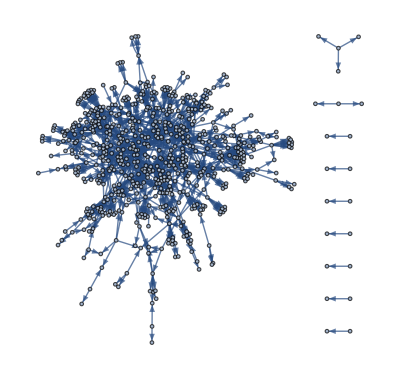

```mathematica
f =Graph[femvertexList,VertexLabels->Placed["Name",Tooltip]]
```

Female nodes highlighted

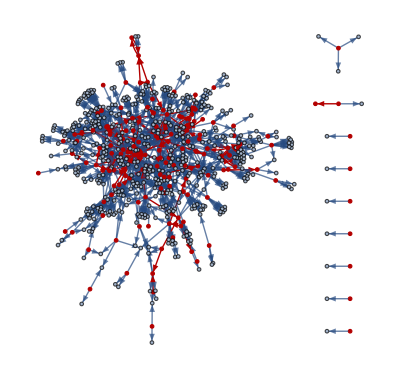

```mathematica
HighlightGraph[f,Subgraph[f,allfemNames ]]
```

```mathematica
femAgents=Part[VertexList[f],Ordering[BetweennessCentrality[f],-5]]
```

{Chisholm_Young,Maddison,Scott,Wheeler,Noether_Emmy}

```mathematica
criticalfem=BetweennessCentrality[f];
criticalfemNode=Pick[VertexList[f],criticalfem,Max[criticalfem]]
```

{Noether_Emmy}

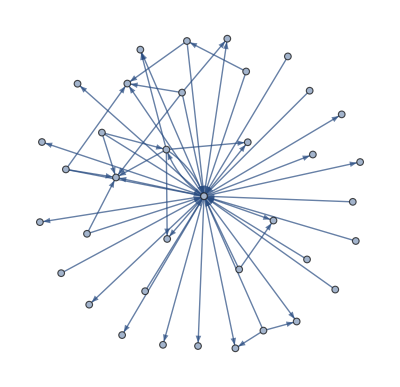

```mathematica
criticalfemGraph= NeighborhoodGraph[f,criticalfemNode,1,GraphLayout->"SpringEmbedding",VertexLabels->Placed["Name",Tooltip]]
```

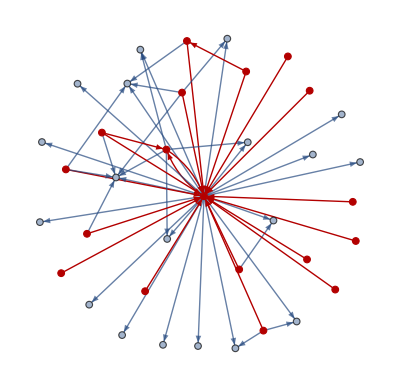

```mathematica
HighlightGraph[criticalfemGraph,Subgraph[criticalfemGraph,allfemNames ]]
```

```mathematica
FindClique[f]
```

{{Boole_Mary,Stott}}

“Mary Everest Boole (11 March 1832 in Wickwar, Gloucestershire – 17 May 1916 in Middlesex, England) was a self-taught mathematician who is best known as an author of didactic works on mathematics, such as Philosophy and Fun of Algebra, and as the wife of fellow mathematician George Boole. Her progressive ideas on education, as expounded in The Preparation of the Child for Science, included encouraging children to explore mathematics through playful activities such as curve stitching. Her life is of interest to feminists as an example of how women made careers in an academic system that did not welcome them

Alicia Boole Stott was the third of the five daughters of Mary Everest Boole. Despite having no formal education in mathematics, she still possessed a great power of geometric visualization in hyperspace. From the age of seventeen until her death, she remained interested in regular and semi-regular four-dimensional polytopes and made several important discoveries in this area.”

Timeline of Only Female mathematician

Positions of Female Mathematicians in Original List

```mathematica
femPositions =Flatten[Position[fullNames,#]&/@ femFullNames]
```

{1031,1790,2394,460,1268,825,2458,1715,2673,833,2544,1239,1913,2164,990,2607,1698,2141,1770,2142,2715,451,1240,2366,2721,2231,906,2302,2608,1773,2743,2048,1794,1914,2216,1354,1950,2580,1951,1245,2489,2256,1848,2018,1641,1142,589,1246,2398,2651,1825,1754,2373,1600,562,2757,2597,1006,1601,2076,1919,527,373,2598,1958,1430,75,1701,2766,2262,2443,2659,1892,1756,993,1829,1666,2689,962,2351,2353,1249,1962,473,2283,740,2335,2084,1855,1298,1263,2566,1264,2696,1149,2770,2690,2775,2383,1929,1525,2685,2179,1265,2248,767,1451,1484,1723,2420,2384,2132,2204,1706,72,1780,2747,1930,1203,2554,2720,2249,2645,1832,1784,2285,1762,2410,2661,1935,2208,2655,1087,1671,2251,2656,1810,2765,598,1510,2603,1869,1308,1112,1619,2273,1977,1746,2755,2274,2682,2618,2574,2156,2505,2575,2557,1470,1471,1676,2764,2739}

```mathematica
femTimelineList = MapThread[Interval[{#1, #2}]&, {completebirthDateObjects[[femPositions]] ,completedeathDateObjects[[femPositions]]/._Missing ->DateObject["Today"]}]
```

{Interval[{Day: Fri 28 Apr 1854,Day: Thu 23 Aug 1923}],Interval[{Day: Tue 19 Nov 1901,Day: Sat 15 Jul 1961}],Interval[{Day: Sat 27 Dec 1924,Day: Wed 23 Mar 2011}],Interval[{Day: Sat 31 Oct 1711,Day: Fri 20 Feb 1778}],Interval[{Day: Fri 18 Mar 1870,Day: Fri 9 Mar 1917}],Interval[{Day: Mon 21 Mar 1831,Day: Fri 9 Nov 1906}],Interval[{Day: Mon 30 May 1927,Day: Mon 9 Jul 2018}],Interval[{Day: Tue 2 Feb 1897,Day: Mon 1 Jan 1996}],Interval[{Day: Fri 18 Dec 1942,Day: Mon 9 Jul 2018}],Interval[{Day: Sun 11 Mar 1832,Day: Wed 17 May 1916}],Interval[{Day: Thu 9 Jul 1931,Day: Wed 4 Feb 2004}],Interval[{Day: Tue 29 Sep 1868,Day: Wed 15 May 1907}],Interval[{Day: Fri 5 May 1905,Day: Mon 11 Sep 1995}],Interval[{Day: Wed 9 Sep 1914,Day: Fri 19 Oct 1979}],Interval[{Day: Fri 15 Feb 1850,Day: Mon 14 Aug 1922}],Interval[{Day: Mon 14 Sep 1936,Day: Sat 1 Dec 2007}],Interval[{Day: Sat 14 Mar 1896,Month: Apr 1985}],Interval[{Day: Sat 19 Jul 1913,Day: Tue 18 Apr 2000}],Interval[{Day: Mon 17 Dec 1900,Day: Fri 3 Apr 1998}],Interval[{Day: Fri 12 Dec 1913,Day: Sun 13 Apr 2014}],Interval[{Day: Wed 24 Mar 1948,Day: Mon 9 Jul 2018}],Interval[{Day: Fri 17 Dec 1706,Day: Wed 10 Sep 1749}],Interval[{Day: Sun 15 Mar 1868,Day: Wed 29 Mar 1944}],Interval[{Day: Sat 29 Dec 1923,Day: Mon 9 Jul 2018}],Interval[{Day: Sun 9 Oct 1949,Day: Mon 9 Jul 2018}],Interval[{Day: Sun 24 Jun 1917,Day: Wed 4 Sep 1996}],Interval[{Day: Thu 10 Feb 1842,Day: Sun 20 Jan 1907}],Interval[{Day: Sat 7 Aug 1920,Day: Wed 15 Dec 1971}],Interval[{Day: Thu 4 Jun 1936,Day: Wed 19 Dec 2001}],Interval[{Day: Sat 13 Jan 1900,Day: Tue 17 Oct 1978}],Interval[{Day: Tue 17 Aug 1954,Day: Mon 9 Jul 2018}],Interval[{Day: Mon 23 Aug 1909,Day: Fri 23 Jul 1993}],Interval[{Day: Wed 9 Oct 1901,Day: Thu 7 Jun 1990}],Interval[{Day: Fri 7 Jul 1905,Day: Thu 19 Oct 1972}],Interval[{Day: Sat 1 Apr 1916,Day: Mon 2 Sep 2002}],Interval[{Day: Sun 19 Nov 1876,Day: Tue 14 Apr 1964}],Interval[{Day: Thu 20 Sep 1906,Day: Fri 15 Apr 1983}],Interval[{Day: Tue 21 Nov 1933,Day: Thu 19 Sep 2002}],Interval[{Day: Thu 4 Oct 1906,Day: Fri 27 Dec 1996}],Interval[{Day: Sat 4 Apr 1868,Day: Thu 10 Jun 1948}],Interval[{Day: Sun 8 Apr 1928,Day: Mon 9 Jul 2018}],Interval[{Day: Sun 17 Feb 1918,Day: Sat 26 Apr 2014}],Interval[{Day: Thu 16 Jul 1903,Day: Wed 22 May 1974}],Interval[{Day: Sun 6 Dec 1908,Day: Tue 25 Jan 2000}],Interval[{Day: Thu 28 Sep 1893,Day: Thu 22 Mar 1973}],Interval[{Day: Sat 22 Feb 1862,Day: Thu 18 Oct 1917}],Interval[{Day: Mon 1 Apr 1776,Day: Mon 27 Jun 1831}],Interval[{Day: Sun 5 Jan 1868,Day: Sat 25 Jul 1953}],Interval[{Day: Thu 1 May 1924,Day: Mon 9 Jul 2018}],Interval[{Day: Tue 4 Apr 1939,Day: Mon 9 Jul 2018}],Interval[{Day: Wed 26 Mar 1902,Day: Sun 16 Sep 1979}],Interval[{Day: Tue 27 Jun 1899,Day: Mon 9 Nov 1981}],Interval[{Day: Tue 24 Jul 1923,Day: Sat 24 Mar 1956}],Interval[{Day: Thu 11 Sep 1890,Day: Fri 25 Jul 1980}],Interval[{Year: 1768,Year: 1832}],Interval[{Day: Fri 13 Nov 1959,Day: Mon 9 Jul 2018}],Interval[{Day: Fri 14 Jun 1935,Day: Sat 28 Oct 1989}],Interval[{Day: Tue 23 Sep 1851,Day: Mon 27 Oct 1930}],Interval[{Day: Mon 27 Oct 1890,Day: Fri 8 Mar 1974}],Interval[{Day: Sun 28 Aug 1910,Day: Wed 28 Mar 1973}],Interval[{Day: Sun 20 Aug 1905,Day: Sun 28 Nov 2004}],Interval[{Day: Mon 16 Mar 1750,Day: Sun 9 Jan 1848}],Interval[{Day: Thu 17 Jan 1647,Day: Tue 22 Dec 1693}],Interval[{Day: Sat 26 Oct 1935,Day: Mon 9 Jul 2018}],Interval[{Day: Sun 9 Dec 1906,Day: Wed 1 Jan 1992}],Interval[{Day: Sat 11 Jun 1881,Day: Fri 26 Nov 1965}],Interval[{Year: 370,Month: Mar 415}],Interval[{Day: Fri 31 Jan 1896,Day: Mon 24 Oct 1966}],Interval[{Day: Sat 4 Jun 1966,Day: Mon 9 Jul 2018}],Interval[{Day: Mon 26 Aug 1918,Day: Mon 9 Jul 2018}],Interval[{Day: Tue 10 Aug 1926,Day: Sun 20 Aug 1972}],Interval[{Day: Fri 9 Aug 1940,Day: Mon 9 Jul 2018}],Interval[{Day: Sat 12 Mar 1904,Day: Mon 16 Feb 1976}],Interval[{Day: Sat 13 May 1899,Day: Sat 3 Jul 1999}],Interval[{Day: Tue 15 Jan 1850,Day: Tue 10 Feb 1891}],Interval[{Day: Sun 11 May 1902,Day: Mon 9 Jul 1984}],Interval[{Day: Mon 9 Apr 1894,Day: Sat 17 Aug 1974}],Interval[{Day: Mon 17 Jul 1944,Day: Mon 9 Jul 2018}],Interval[{Day: Wed 1 Dec 1847,Day: Wed 5 Mar 1930}],Interval[{Day: Tue 7 Mar 1922,Day: Mon 12 Jan 2004}],Interval[{Day: Thu 23 Feb 1922,Day: Fri 24 Sep 1999}],Interval[{Day: Sat 4 Jul 1868,Day: Mon 12 Dec 1921}],Interval[{Day: Tue 6 Nov 1906,Day: Mon 7 May 2007}],Interval[{Day: Tue 5 Jan 1723,Day: Sat 6 Dec 1788}],Interval[{Day: Fri 14 Nov 1919,Day: Tue 10 Jul 2007}],Interval[{Day: Sun 10 Dec 1815,Day: Sat 27 Nov 1852}],Interval[{Day: Wed 21 Dec 1921,Day: Mon 18 Nov 2002}],Interval[{Day: Sun 3 Apr 1910,Day: Mon 21 Mar 1960}],Interval[{Day: Sat 2 May 1903,Year: 1972}],Interval[{Day: Thu 13 Jun 1872,Day: Tue 21 Sep 1937}],Interval[{Day: Tue 13 Apr 1869,Day: Sun 22 Oct 1950}],Interval[{Day: Wed 10 Feb 1932,Day: Fri 9 Jun 1995}],Interval[{Day: Thu 30 Dec 1869,Day: Sat 8 Feb 1936}],Interval[{Day: Thu 18 Oct 1945,Day: Mon 9 Jul 2018}],Interval[{Day: Wed 24 Sep 1862,Day: Thu 6 Sep 1951}],Interval[{Day: Wed 8 Mar 1967,Day: Wed 1 Nov 2000}],Interval[{Day: Wed 22 Mar 1944,Month: Mar 1973}],Interval[{Day: Tue 3 May 1977,Day: Fri 14 Jul 2017}],Interval[{Day: Sat 5 May 1923,Day: Tue 8 Aug 2017}],Interval[{Day: Tue 10 Jan 1905,Day: Sat 26 Nov 1977}],Interval[{Day: Wed 10 Feb 1886,Day: Sun 27 Sep 1964}],Interval[{Day: Thu 25 Nov 1943,Day: Sat 1 Aug 1987}],Interval[{Day: Thu 12 Feb 1914,Day: Sun 14 Nov 1971}],Interval[{Day: Sat 7 Aug 1869,Day: Sat 5 Dec 1959}],Interval[{Day: Fri 21 Sep 1917,Day: Sun 6 Oct 1968}],Interval[{Day: Fri 12 May 1820,Day: Sat 13 Aug 1910}],Interval[{Day: Thu 23 Mar 1882,Day: Sun 14 Apr 1935}],Interval[{Day: Wed 18 Jun 1884,Day: Sun 6 Nov 1966}],Interval[{Day: Sat 6 Mar 1897,Day: Sun 10 Apr 1988}],Interval[{Day: Thu 2 Jul 1925,Day: Sat 13 Oct 2001}],Interval[{Day: Fri 8 Jun 1923,Day: Mon 17 Apr 2006}],Interval[{Day: Tue 1 Oct 1912,Day: Sun 10 Aug 2014}],Interval[{Day: Sat 9 Jan 1915,Day: Mon 18 Dec 2006}],Interval[{Day: Mon 8 Jun 1896,Day: Fri 14 Sep 1973}],Interval[{Year: 300,Year: 360}],Interval[{Day: Thu 10 May 1900,Day: Fri 7 Dec 1979}],Interval[{Day: Mon 1 Aug 1955,Day: Mon 9 Jul 2018}],Interval[{Day: Fri 17 Feb 1905,Day: Wed 16 Feb 1977}],Interval[{Day: Fri 19 May 1865,Day: Sat 14 Aug 1943}],Interval[{Day: Thu 5 Mar 1931,Day: Mon 9 Jul 2018}],Interval[{Day: Tue 7 Sep 1948,Day: Mon 9 Jul 2018}],Interval[{Day: Wed 20 Jun 1917,Day: Tue 9 Aug 1994}],Interval[{Day: Sun 30 Oct 1938,Day: Fri 7 Jul 2017}],Interval[{Day: Sat 2 Aug 1902,Day: Sat 25 Oct 1997}],Interval[{Day: Tue 15 May 1900,Day: Sat 1 Feb 1986}],Interval[{Day: Mon 8 Dec 1919,Day: Tue 30 Jul 1985}],Interval[{Day: Mon 4 Sep 1899,Month: Dec 1942}],Interval[{Day: Sun 7 Dec 1924,Day: Mon 18 Mar 2013}],Interval[{Day: Thu 23 May 1940,Day: Fri 3 Dec 2010}],Interval[{Day: Mon 8 May 1905,Month: Oct 1979}],Interval[{Day: Fri 18 Jun 1915,Day: Sun 27 Sep 2009}],Interval[{Day: Thu 19 Oct 1939,Day: Mon 9 Jul 2018}],Interval[{Day: Tue 8 Jun 1858,Day: Tue 10 Nov 1931}],Interval[{Day: Wed 28 Feb 1894,Year: 1950}],Interval[{Day: Fri 23 Nov 1917,Day: Tue 20 Dec 1988}],Interval[{Day: Tue 18 Jul 1939,Day: Mon 9 Jul 2018}],Interval[{Year: 1901,Year: 1980}],Interval[{Day: Sun 9 May 1965,Day: Mon 9 Jul 2018}],Interval[{Day: Tue 26 Dec 1780,Day: Fri 29 Nov 1872}],Interval[{Day: Thu 5 Mar 1885,Year: 1967}],Interval[{Day: Mon 22 Apr 1935,Day: Mon 9 Jul 2018}],Interval[{Day: Thu 17 Sep 1903,Day: Sun 3 Dec 1995}],Interval[{Day: Sun 10 Mar 1872,Day: Thu 23 Feb 1961}],Interval[{Day: Fri 8 Jun 1860,Day: Tue 17 Dec 1940}],Interval[{Day: Sun 22 Mar 1891,Day: Fri 8 May 1936}],Interval[{Day: Fri 5 Apr 1918,Day: Fri 27 Aug 1976}],Interval[{Day: Thu 30 Aug 1906,Day: Sat 7 Oct 1995}],Interval[{Day: Fri 15 Jul 1898,Day: Sat 26 May 1984}],Interval[{Day: Mon 30 Jun 1958,Day: Mon 9 Jul 2018}],Interval[{Day: Tue 15 Jan 1918,Day: Sat 27 Mar 2010}],Interval[{Day: Mon 24 Aug 1942,Day: Mon 9 Jul 2018}],Interval[{Year: 1936,Day: Mon 9 Jul 2018}],Interval[{Day: Wed 24 Feb 1932,Day: Wed 18 Sep 2002}],Interval[{Day: Mon 9 Jun 1913,Day: Sat 8 Aug 2009}],Interval[{Day: Mon 30 Jul 1928,Day: Mon 9 Jul 2018}],Interval[{Day: Wed 22 Jun 1932,Day: Wed 1 Apr 1998}],Interval[{Day: Thu 15 Oct 1931,Month: Aug 1992}],Interval[{Day: Sat 5 May 1883,Day: Sat 26 Mar 1966}],Interval[{Day: Tue 25 Dec 1883,Day: Sun 12 Oct 1919}],Interval[{Day: Wed 12 Sep 1894,Day: Wed 11 Feb 1976}],Interval[{Day: Fri 15 May 1964,Day: Mon 9 Jul 2018}],Interval[{Year: 1952,Day: Mon 9 Jul 2018}]}

```mathematica
TimelinePlot[femTimelineList,
```

```mathematica
femFullNames[[{55,67}]]
```

{{Marie-Jeanne Amélie Harlay},{Hypatia of Alexandria }}

Hypatia: 

Prominent astronomers of her time used to ask her advice on the construction of an astrolabe and a hydroscope + she helped her father in revision ptolemy’s astronomical works and euclid’s elements + among the pupuls who she taught in Alexandria were prominent Christians which is important because there were clashes between neoplatonism and christianity in alexandria during the 4th century

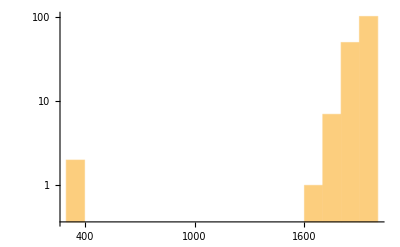

```mathematica
DateHistogram[completebirthDateObjects[[femPositions]],"Century",ScalingFunctions->"Log"]
```

```mathematica
femFormattedBios =deleteHtmlElements[#]&/@femBioList[[;;]]
```

{{17496},{12052},158,{8215},{9693}}
 |  |  |  |

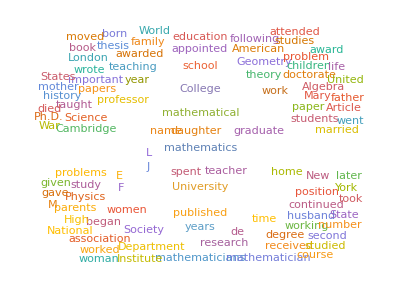

```mathematica
WordCloud[DeleteStopwords[StringJoin[femFormattedBios]]]
```